## Redshfit-space real universe

## Code for Evaluating 1-loop real space integral

Initial setup

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Useful routines

Routine that takes a two-column table and “integrates” it via the midpoint method. It’s probably woefully inefficient, but I won’t worry about it for now...

```mathematica
Clear[MidpointIntegrate];MidpointIntegrate[table_]:=Module[{n},
Table[(table[[n]][[2]]+table[[n-1]][[2]])/2*(table[[n]][[1]]-table[[n-1]][[1]]),{n,2,Length[table]}]//Total
]
```

Table that outputs progress so far if aborted (from http://stackoverflow.com/questions/6470625/mathematica-table-function):

```mathematica
ClearAll[AbortableTable];
SetAttributes[AbortableTable,HoldAll];
AbortableTable[expr_,iter:{_Symbol,__}..]:=Module[{indices,indexedRes,sowTag,depth=Length[Hold[iter]]-1},Hold[iter]/.{sym_Symbol,__}:>sym/.Hold[syms__]:>(indices:={syms});
indexedRes=Replace[#,{x_}:>x]&@Last@Reap[CheckAbort[Do[Sow[{expr,indices},sowTag],iter],Null],sowTag];
AbortProtect[SplitBy[indexedRes,Array[Function[x,#[[2,x]]&],{depth}]][[##,1]]&@@Table[All,{depth+1}]]];
```

Routines to add, subtract, or divide the second column of a two-column table:

```mathematica
addCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]+tab2[[n]][[2]]},{n,1,Length[tab1]}]
subCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]-tab2[[n]][[2]]},{n,1,Length[tab1]}]
divCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]/tab2[[n]][[2]]},{n,1,Length[tab1]}]
```

ΛCDM growth factor

ΛCDM growth factor (messy code, copied from JJ’s file a few years ago...)

```mathematica
paramSubs={Subscript[Ω, m]->0.307, Subscript[Ω, Λ]->1-0.307,ℋ0->100,Subscript[Ω, b]->0.048};
```

```mathematica
(hSol=ℋ[a]->ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2);
hpSol=Map[D[#,a]&,hSol];{hSol,hpSol});
```

```mathematica
hsubs={ℋ[a_]:>ℋ0 √(Subscript[Ω, m]/a+a^2 Subscript[Ω, Λ]),ℋ'[a_]:>(ℋ0 (-Subscript[Ω, m]/a^2+2 a Subscript[Ω, Λ]))/(2 √(Subscript[Ω, m]/a+a^2 Subscript[Ω, Λ])),ℋ''[a_]:>(3 ℋ0 Subscript[Ω, m] (Subscript[Ω, m]+4 a^3 Subscript[Ω, Λ]))/(4 a^4 ((Subscript[Ω, m]+a^3 Subscript[Ω, Λ])/a)^(3/2))};
```

```mathematica
DgS[a_]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a) Integrate[(1/ℋ[ap])^3,{ap,0,a}]
grS[a_,ai_]:=(ℋ[a]/a^2) Integrate[(1/ℋ[ap])^3,{ap,ai,a}]
(DgpS[a_]=D[DgS[a],a]);
(DgppS[a_]=D[DgpS[a],a]);
```

```mathematica
ClearAll[DgN,DgppN,DgpN];
DgpN[a_?NumericQ]:=(DgpS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubs/.paramSubs)/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgppN[a_?NumericQ]:=(DgppS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubs/.paramSubs)/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgN[a_?NumericQ]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a/.hsubs/.paramSubs) NIntegrate[(1/ℋ[ap])^3/.hsubs/.paramSubs,{ap,0,a}]
```

```mathematica
x
```

x

```mathematica
dgN1=DgN[1.];
Dgrtab=Monitor[AbortableTable[{z,DgN[1/(1+z)]/dgN1},{z,0,10,0.01}],z];
DgrtabInterp=Interpolation[Dgrtab];
Clear[Dgrowth];
Dgrowth[z_]=DgrtabInterp[z];
```

```mathematica
dgpN1=DgpN[1.];
Dpgrtab=Monitor[AbortableTable[{z,DgpN[1/(1+z)]/dgN1},{z,0,10,0.01}],z];
Clear[DpgrowthNorm];
DpgrowthNorm=Interpolation[Dpgrtab];
```

```mathematica
D1sub={D1[zz_]:>Dgrowth[zz],D1p[zz_]:>DpgrowthNorm[zz]};
```

```mathematica
ftab=Monitor[AbortableTable[{z,(1/(1+z))/DgrtabInterp[z] DpgrowthNorm[z]},{z,0,10,0.01}],z];
f=Interpolation[ftab];

zz[a_]=(1-a)/a;
```

Linear Power Spectrum from CAMB

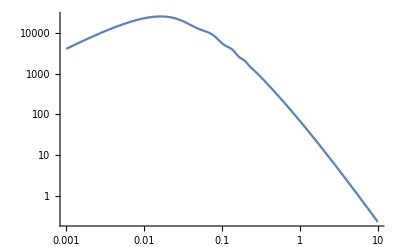

```mathematica
P11data={{0.0001,463.44},{0.00010202,472.42},{0.00010408,481.57},{0.00010618,490.9},{0.00010833,500.41},{0.00011052,510.1},{0.00011275,519.99},{0.00011503,530.06},{0.00011735,540.33},{0.00011972,550.79},{0.00012214,561.46},{0.00012461,572.34},{0.00012712,583.42},{0.00012969,594.72},{0.00013231,606.24},{0.00013499,617.98},{0.00013771,629.95},{0.00014049,642.15},{0.00014333,654.59},{0.00014623,667.26},{0.00014918,680.18},{0.0001522,693.35},{0.00015527,706.78},{0.00015841,720.46},{0.00016161,734.41},{0.00016487,748.62},{0.0001682,763.11},{0.0001716,777.89},{0.00017507,792.94},{0.0001786,808.29},{0.00018221,823.93},{0.00018589,839.87},{0.00018965,856.12},{0.00019348,872.69},{0.00019739,889.57},{0.00020138,906.78},{0.00020544,924.32},{0.00020959,942.2},{0.00021383,960.42},{0.00021815,978.99},{0.00022255,997.92},{0.00022705,1017.2},{0.00023164,1036.9},{0.00023632,1056.9},{0.00024109,1077.4},{0.00024596,1098.2},{0.00025093,1119.4},{0.000256,1141.},{0.00026117,1163.1},{0.00026645,1185.5},{0.00027183,1208.4},{0.00027732,1231.8},{0.00028292,1255.5},{0.00028864,1279.8},{0.00029447,1304.5},{0.00030042,1329.7},{0.00030649,1355.3},{0.00031268,1381.5},{0.00031899,1408.1},{0.00032544,1435.3},{0.00033201,1462.9},{0.00033872,1491.1},{0.00034556,1519.9},{0.00035254,1549.1},{0.00035966,1579.},{0.00036693,1609.4},{0.00037434,1640.4},{0.0003819,1672.},{0.00038962,1704.1},{0.00039749,1736.9},{0.00040552,1770.3},{0.00041371,1804.4},{0.00042207,1839.},{0.0004306,1874.4},{0.00043929,1910.4},{0.00044817,1947.1},{0.00045722,1984.4},{0.00046646,2022.5},{0.00047588,2061.3},{0.0004855,2100.8},{0.0004953,2141.1},{0.00050531,2182.1},{0.00051552,2223.9},{0.00052593,2266.4},{0.00053656,2309.8},{0.00054739,2354.},{0.00055845,2399.},{0.00056973,2444.8},{0.00058124,2491.5},{0.00059299,2539.},{0.00060496,2587.5},{0.00061719,2636.8},{0.00062965,2687.},{0.00064237,2738.2},{0.00065535,2790.3},{0.00066859,2843.4},{0.0006821,2897.4},{0.00069588,2952.4},{0.00070993,3008.5},{0.00072427,3065.5},{0.00073891,3123.6},{0.00075383,3182.8},{0.00076906,3243.},{0.0007846,3304.3},{0.00080045,3366.8},{0.00081662,3430.3},{0.00083311,3495.},{0.00084994,3560.9},{0.00086711,3627.9},{0.00088463,3696.2},{0.0009025,3765.7},{0.00092073,3836.4},{0.00093933,3908.3},{0.00095831,3981.5},{0.00097767,4056.1},{0.00099742,4131.9},{0.0010176,4209.1},{0.0010381,4287.6},{0.0010591,4367.5},{0.0010805,4448.8},{0.0011023,4531.5},{0.0011246,4615.6},{0.0011473,4701.1},{0.0011705,4788.2},{0.0011941,4876.7},{0.0012182,4966.8},{0.0012429,5058.3},{0.001268,5151.4},{0.0012936,5246.1},{0.0013197,5342.4},{0.0013464,5440.3},{0.0013736,5539.8},{0.0014013,5641.},{0.0014296,5743.8},{0.0014585,5848.3},{0.001488,5954.5},{0.001518,6062.5},{0.0015487,6172.1},{0.00158,6283.6},{0.0016119,6396.8},{0.0016445,6511.9},{0.0016777,6628.7},{0.0017116,6747.4},{0.0017462,6867.9},{0.0017814,6990.3},{0.0018174,7114.6},{0.0018541,7240.8},{0.0018916,7368.9},{0.0019298,7498.9},{0.0019688,7630.9},{0.0020086,7764.8},{0.0020491,7900.8},{0.0020905,8038.7},{0.0021328,8178.6},{0.0021758,8320.5},{0.0022198,8464.4},{0.0022646,8610.3},{0.0023104,8758.3},{0.0023571,8908.4},{0.0024047,9060.4},{0.0024533,9214.6},{0.0025028,9370.8},{0.0025534,9529.1},{0.002605,9689.4},{0.0026576,9851.9},{0.0027113,10016.},{0.002766,10183.},{0.0028219,10352.},{0.0028789,10522.},{0.0029371,10695.},{0.0029964,10870.},{0.0030569,11047.},{0.0031187,11226.},{0.0031817,11407.},{0.003246,11589.},{0.0033115,11774.},{0.0033784,11961.},{0.0034467,12150.},{0.0035163,12341.},{0.0035874,12534.},{0.0036598,12728.},{0.0037338,12925.},{0.0038092,13123.},{0.0038861,13323.},{0.0039646,13525.},{0.0040447,13729.},{0.0041264,13934.},{0.0042098,14141.},{0.0042948,14350.},{0.0043816,14560.},{0.0044701,14771.},{0.0045604,14984.},{0.0046525,15199.},{0.0047465,15415.},{0.0048424,15632.},{0.0049402,15850.},{0.00504,16069.},{0.0051419,16290.},{0.0052457,16511.},{0.0053517,16733.},{0.0054598,16956.},{0.0055701,17180.},{0.0056826,17405.},{0.0057974,17630.},{0.0059145,17855.},{0.006034,18081.},{0.0061559,18307.},{0.0062803,18533.},{0.0064072,18759.},{0.0065366,18985.},{0.0066686,19210.},{0.0068033,19436.},{0.0069408,19660.},{0.007081,19884.},{0.007224,20108.},{0.00737,20330.},{0.0075189,20551.},{0.0076708,20771.},{0.0078257,20989.},{0.0079838,21206.},{0.0081451,21421.},{0.0083096,21633.},{0.0084775,21844.},{0.0086488,22053.},{0.0088235,22258.},{0.0090017,22461.},{0.0091836,22661.},{0.0093691,22858.},{0.0095583,23052.},{0.0097514,23241.},{0.0099484,23427.},{0.010149,23609.},{0.010354,23787.},{0.010564,23960.},{0.010777,24128.},{0.010995,24291.},{0.011217,24448.},{0.011443,24600.},{0.011675,24746.},{0.01191,24886.},{0.012151,25020.},{0.012397,25147.},{0.012647,25266.},{0.012902,25379.},{0.013163,25484.},{0.013429,25581.},{0.0137,25670.},{0.013977,25751.},{0.014259,25823.},{0.014547,25886.},{0.014841,25940.},{0.015141,25985.},{0.015447,26019.},{0.015759,26044.},{0.016077,26058.},{0.016402,26062.},{0.016734,26055.},{0.017072,26037.},{0.017416,26007.},{0.017768,25966.},{0.018127,25914.},{0.018493,25850.},{0.018867,25774.},{0.019248,25686.},{0.019637,25585.},{0.020034,25473.},{0.020438,25348.},{0.020851,25210.},{0.021272,25061.},{0.021702,24899.},{0.022141,24724.},{0.022588,24538.},{0.023044,24339.},{0.02351,24129.},{0.023985,23906.},{0.024469,23673.},{0.024964,23428.},{0.025468,23173.},{0.025982,22907.},{0.026507,22631.},{0.027043,22346.},{0.027589,22052.},{0.028146,21749.},{0.028715,21439.},{0.029295,21122.},{0.029887,20798.},{0.03049,20469.},{0.031106,20136.},{0.031735,19798.},{0.032376,19457.},{0.03303,19114.},{0.033697,18770.},{0.034378,18425.},{0.035072,18082.},{0.035781,17740.},{0.036504,17399.},{0.037241,17061.},{0.037993,16725.},{0.038761,16394.},{0.039544,16068.},{0.040343,15749.},{0.041158,15439.},{0.041989,15137.},{0.042838,14846.},{0.043703,14564.},{0.044586,14293.},{0.045486,14033.},{0.046405,13784.},{0.047343,13545.},{0.048299,13317.},{0.049275,13099.},{0.05027,12891.},{0.051286,12692.},{0.052322,12501.},{0.053379,12317.},{0.054457,12139.},{0.055557,11968.},{0.05668,11806.},{0.057825,11654.},{0.058993,11505.},{0.060184,11355.},{0.0614,11201.},{0.062641,11044.},{0.063906,10885.},{0.065197,10722.},{0.066514,10551.},{0.067858,10373.},{0.069229,10186.},{0.070627,9988.},{0.072054,9779.4},{0.07351,9559.4},{0.074994,9328.2},{0.076509,9086.2},{0.078055,8834.4},{0.079632,8574.3},{0.081241,8307.3},{0.082882,8035.6},{0.084556,7761.5},{0.086264,7487.3},{0.088007,7215.5},{0.089785,6948.6},{0.091598,6689.3},{0.093449,6440.},{0.095337,6202.9},{0.097263,5980.2},{0.099227,5773.7},{0.10123,5584.4},{0.10328,5412.9},{0.10536,5259.2},{0.10749,5122.3},{0.10966,5001.},{0.11188,4893.3},{0.11414,4796.8},{0.11644,4709.},{0.1188,4626.5},{0.1212,4546.2},{0.12365,4464.5},{0.12614,4377.5},{0.12869,4282.2},{0.13129,4176.},{0.13394,4057.4},{0.13665,3926.9},{0.13941,3786.3},{0.14223,3638.2},{0.1451,3486.3},{0.14803,3333.9},{0.15102,3184.7},{0.15407,3041.7},{0.15718,2908.},{0.16036,2786.4},{0.1636,2679.4},{0.1669,2587.2},{0.17028,2509.1},{0.17371,2443.3},{0.17722,2386.},{0.1808,2333.3},{0.18446,2281.8},{0.18818,2227.9},{0.19198,2169.},{0.19586,2103.2},{0.19982,2029.6},{0.20386,1949.4},{0.20797,1865.1},{0.21218,1779.8},{0.21646,1697.1},{0.22083,1620.3},{0.2253,1551.3},{0.22985,1491.6},{0.23449,1441.1},{0.23923,1397.4},{0.24406,1358.2},{0.24899,1320.6},{0.25402,1281.6},{0.25915,1239.3},{0.26439,1193.5},{0.26973,1144.3},{0.27518,1093.8},{0.28074,1044.7},{0.28641,998.91},{0.29219,957.57},{0.2981,921.37},{0.30412,889.3},{0.31026,859.67},{0.31653,830.95},{0.32292,801.66},{0.32945,770.7},{0.3361,738.67},{0.34289,706.85},{0.34982,676.33},{0.35689,648.},{0.36409,622.48},{0.37145,599.14},{0.37895,576.9},{0.38661,555.01},{0.39442,533.1},{0.40239,510.99},{0.41052,489.22},{0.41881,468.55},{0.42727,449.34},{0.4359,431.33},{0.44471,414.19},{0.45369,397.63},{0.46286,381.34},{0.47221,365.28},{0.48174,349.78},{0.49148,335.14},{0.50141,321.28},{0.51153,308.02},{0.52187,295.2},{0.53241,282.81},{0.54317,270.83},{0.55414,259.3},{0.56533,248.3},{0.57675,237.81},{0.5884,227.75},{0.60029,218.04},{0.61242,208.67},{0.62479,199.7},{0.63741,191.13},{0.65029,182.91},{0.66342,175.02},{0.67683,167.43},{0.6905,160.16},{0.70445,153.2},{0.71868,146.53},{0.7332,140.13},{0.74801,134.},{0.76312,128.12},{0.77854,122.49},{0.79426,117.09},{0.81031,111.92},{0.82668,106.97},{0.84338,102.23},{0.86041,97.69},{0.8778,93.342},{0.89553,89.18},{0.91362,85.196},{0.93208,81.383},{0.95091,77.733},{0.97011,74.241},{0.98971,70.899},{1.0097,67.702},{1.0301,64.643},{1.0509,61.717},{1.0721,58.918},{1.0938,56.242},{1.1159,53.683},{1.1384,51.236},{1.1614,48.897},{1.1849,46.66},{1.2088,44.523},{1.2333,42.481},{1.2582,40.529},{1.2836,38.663},{1.3095,36.88},{1.336,35.177},{1.363,33.55},{1.3905,31.996},{1.4186,30.512},{1.4472,29.094},{1.4765,27.74},{1.5063,26.448},{1.5367,25.213},{1.5678,24.035},{1.5994,22.91},{1.6318,21.836},{1.6647,20.811},{1.6984,19.833},{1.7327,18.9},{1.7677,18.009},{1.8034,17.159},{1.8398,16.348},{1.877,15.575},{1.9149,14.837},{1.9536,14.133},{1.993,13.462},{2.0333,12.822},{2.0744,12.211},{2.1163,11.629},{2.159,11.074},{2.2026,10.545},{2.2471,10.04},{2.2925,9.559},{2.3388,9.1005},{2.3861,8.6634},{2.4343,8.2469},{2.4835,7.85},{2.5336,7.4717},{2.5848,7.1113},{2.637,6.7679},{2.6903,6.4407},{2.7447,6.129},{2.8001,5.832},{2.8567,5.5491},{2.9144,5.2797},{2.9733,5.0231},{3.0333,4.7787},{3.0946,4.5459},{3.1571,4.3243},{3.2209,4.1132},{3.286,3.9123},{3.3523,3.721},{3.4201,3.5388},{3.4892,3.3654},{3.5596,3.2004},{3.6316,3.0432},{3.7049,2.8937},{3.7798,2.7514},{3.8561,2.6159},{3.934,2.487},{4.0135,2.3644},{4.0946,2.2476},{4.1773,2.1366},{4.2617,2.0309},{4.3478,1.9304},{4.4356,1.8348},{4.5252,1.7438},{4.6166,1.6572},{4.7099,1.5749},{4.805,1.4966},{4.9021,1.4222},{5.0011,1.3514},{5.1021,1.284},{5.2052,1.22},{5.3104,1.1591},{5.4176,1.1012},{5.5271,1.0461},{5.6387,0.99378},{5.7526,0.94402},{5.8689,0.89671},{5.9874,0.85174},{6.1084,0.80899},{6.2318,0.76836},{6.3577,0.72974},{6.4861,0.69303},{6.6171,0.65814},{6.7508,0.62499},{6.8872,0.59348},{7.0263,0.56354},{7.1682,0.53509},{7.313,0.50806},{7.4608,0.48237},{7.6115,0.45797},{7.7653,0.43479},{7.9221,0.41276},{8.0822,0.39183},{8.2454,0.37196},{8.412,0.35308},{8.5819,0.33514},{8.7553,0.31811},{8.9322,0.30193},{9.1126,0.28656},{9.2967,0.27196},{9.4845,0.2581},{9.6761,0.24494},{9.8716,0.23244},{10.071,0.22058},{10.274,0.20931},{10.482,0.19861},{10.694,0.18845},{10.91,0.1788},{11.13,0.16965},{11.355,0.16095},{11.584,0.1527},{11.818,0.14487},{12.057,0.13743},{12.301,0.13037},{12.549,0.12367},{12.803,0.11731},{13.061,0.11127},{13.325,0.10555},{13.594,0.10011},{13.869,0.094949},{14.149,0.090053},{14.435,0.085407},{14.727,0.080998},{15.024,0.076814},{15.328,0.072844},{15.637,0.069078},{15.953,0.065504},{16.275,0.062113},{16.604,0.058896},{16.94,0.055845},{17.282,0.052949},{17.631,0.050203},{17.987,0.047598},{18.351,0.045126},{18.721,0.042782},{19.099,0.040558},{19.485,0.038449},{19.879,0.036449},{20.28,0.034552},{20.69,0.032752},{21.108,0.031046},{21.535,0.029427},{21.97,0.027893},{22.413,0.026437},{22.866,0.025057},{23.328,0.023748},{23.799,0.022507},{24.28,0.021331},{24.771,0.020215},{25.271,0.019157},{25.782,0.018154},{26.302,0.017203},{26.834,0.016302},{27.376,0.015447},{27.929,0.014637},{28.493,0.013869},{29.069,0.013141},{29.656,0.012451},{30.255,0.011797},{30.866,0.011177},{31.49,0.010589},{32.126,0.010032},{32.775,0.0095035},{33.437,0.0090031},{34.112,0.0085287},{34.801,0.0080792},{35.504,0.0076532},{36.222,0.0072494},{36.953,0.0068668},{37.7,0.0065042},{38.462,0.0061606},{39.239,0.005835},{40.031,0.0055265},{40.84,0.0052342},{41.665,0.0049572},{42.507,0.0046947},{43.365,0.0044461},{44.241,0.0042105},{45.135,0.0039872},{46.047,0.0037758},{46.977,0.0035754},{47.926,0.0033856},{48.894,0.0032058},{49.882,0.0030355},{50.89,0.0028741},{51.918,0.0027213},{52.966,0.0025765},{54.036,0.0024393},{55.128,0.0023094},{56.242,0.0021864},{57.378,0.0020698},{58.537,0.0019594},{59.72,0.0018549},{60.926,0.0017559},{62.157,0.0016621},{63.412,0.0015733},{64.693,0.0014892},{66.,0.0014095},{67.334,0.0013341},{68.694,0.0012627},{70.082,0.0011951},{71.497,0.001131},{72.942,0.0010704},{74.415,0.0010129},{75.918,0.00095856},{77.452,0.00090708},{79.017,0.00085834},{80.613,0.00081219},{82.241,0.00076849},{83.903,0.00072713},{85.598,0.00068796},{87.327,0.00065089},{89.091,0.00061579},{90.891,0.00058257},{92.727,0.00055112},{94.6,0.00052134},{96.511,0.00049316},{98.461,0.00046648},{100.45,0.00044123},{102.48,0.00041733},{104.55,0.00039471},{106.66,0.0003733},{108.82,0.00035304},{111.01,0.00033386},{113.26,0.00031571},{115.54,0.00029854},{117.88,0.00028229},{120.26,0.0002669},{122.69,0.00025235},{125.17,0.00023858},{127.7,0.00022554},{130.28,0.00021321},{132.91,0.00020155},{135.59,0.00019051},{138.33,0.00018006},{141.13,0.00017018},{143.98,0.00016083},{146.89,0.00015199},{149.85,0.00014363},{152.88,0.00013571},{155.97,0.00012823},{159.12,0.00012114},{162.33,0.00011445},{165.61,0.00010811},{168.96,0.00010212},{172.37,0.000096456},{175.85,0.000091098},{179.41,0.00008603},{183.03,0.000081239},{186.73,0.000076708},{190.5,0.000072424},{194.35,0.000068373},{198.28,0.000064543},{202.28,0.000060923},{206.37,0.0000575},{210.54,0.000054265},{214.79,0.000051206},{219.13,0.000048315},{223.56,0.000045583},{228.07,0.000043001},{232.68,0.000040561},{237.38,0.000038255},{242.17,0.000036077},{247.07,0.000034018},{252.06,0.000032074},{257.15,0.000030236},{262.34,0.000028501},{267.64,0.000026862},{273.05,0.000025314},{278.57,0.000023852},{284.19,0.000022472},{289.94,0.000021168},{295.79,0.000019938},{301.77,0.000018776},{307.86,0.00001768},{314.08,0.000016645},{320.43,0.000015669},{326.9,0.000014747},{333.51,0.000013878},{340.24,0.000013058},{347.12,0.000012285},{354.13,0.000011556},{361.28,0.000010868},{368.58,0.00001022},{376.03,9.6083*^-6},{383.62,9.0323*^-6},{391.37,8.4895*^-6},{399.28,7.978*^-6},{407.34,7.4962*^-6},{415.57,7.0424*^-6},{423.97,6.6151*^-6},{432.53,6.2127*^-6},{441.27,5.8339*^-6},{450.19,5.4775*^-6},{459.28,5.142*^-6},{468.56,4.8265*^-6},{478.02,4.5296*^-6},{487.68,4.2505*^-6},{497.53,3.988*^-6},{507.58,3.7413*^-6},{517.84,3.5094*^-6},{528.3,3.2916*^-6},{538.97,3.0869*^-6},{549.86,2.8946*^-6},{560.97,2.7141*^-6},{572.3,2.5446*^-6},{583.86,2.3855*^-6},{595.65,2.2362*^-6},{607.69,2.096*^-6},{619.96,1.9646*^-6},{632.49,1.8413*^-6},{645.26,1.7257*^-6},{658.3,1.6172*^-6},{671.6,1.5156*^-6},{685.16,1.4203*^-6},{699.01,1.3309*^-6},{713.13,1.2472*^-6},{727.53,1.1688*^-6},{742.23,1.0952*^-6},{757.22,1.0264*^-6},{772.52,9.6181*^-7},{788.13,9.0133*^-7},{804.05,8.4468*^-7},{820.29,7.9159*^-7},{836.86,7.4186*^-7},{853.77,6.9527*^-7},{871.01,6.5162*^-7},{888.61,6.1072*^-7},{906.56,5.7241*^-7},{924.88,5.365*^-7},{943.56,5.0286*^-7},{962.62,4.7133*^-7},{982.07,4.4179*^-7},{1001.9,4.1411*^-7}};
Clear[P11camb,P11cut];
P11camb=Interpolation[P11data];
P11cut[a_,kmin_,kmax_]:=If[kmax>a>kmin,P11camb[a],0]
P11vec[a_,kmin_,kmax_]:=If[kmax>Sqrt[a.a]>kmin,P11camb[Sqrt[a.a]],0]
P11in[k_]=P11camb[k];
Λ=10;
ap56=1/(1+z)/.{z->0.5618};
a1 = 1/(1+z)/. z->1//N;
LogLogPlot[P11in[k],{k,0.001,10}]
```

```mathematica
Pplus[k_,knlp_ , np_ ] = (2 π)^3 1/knlp^3(k/knlp)^np;
Pmin[k_,knlm_ , nm_ ] = (2 π)^3 1/knlm^3(k/knlm)^nm;
```

```mathematica
Manipulate[Quiet[ LogLogPlot[ { P11in[k]/ Pmin[k,knlm , nm ],P11in[k]/ Pplus[k,knlp , np ],1} , { k , .01 , 1}, PlotRange->All]] , {{ knlm,1.25} , 0,5}, {{nm,-1.54}, -5,0} , { {knlp,3.96} , 0,5}, {{np,-2.11}, -5,0}]
```

```mathematica
subzzz = { knlm -> 1.25 , knlp->3.96 , np-> -2.11 , nm->-1.54};
```

```mathematica
P1= Pplus[k,knlp, np]/.subzzz
```

72.8771/k^2.11

```mathematica
P2 = Pmin[k , knlm,nm]/.subzzz
```

179.082/k^1.54

```mathematica
Solve[ P1 - P2 ==0 , k]
```

{{k→0.20653}}

```mathematica
Sqrt[ √(.2)1.25^1.5]
```

0.790569

```mathematica
((.2)^2/(2π)^3(1.25)^3)^(1/5)
```

0.199366

□^□Cut-off and smoothed spectra definitions

```mathematica
ClearAll[kmin,kmax,P11cut,P11vec,P11vecsm];
(*kmin=10^-4;
kmax=10;*)
P11cut[k_,kmin_,kmax_]:=If[kmax>k> kmin,P11in[k],0];
P11sm[k_,kmin_,kmax_,ksmooth_]:=If[kmax>k> kmin,P11in[k]*Exp[-k^2/ksmooth^2],0];
P11vec[a_,kmin_,kmax_]:=If[kmax>Sqrt[a.a]>kmin,P11in[Sqrt[a.a]],0]
P11vecsm[a_,kmin_,kmax_,ksmooth_]:=If[kmax>Sqrt[a.a]>kmin,P11in[Sqrt[a.a]]*Exp[(-Sqrt[a.a]^2)/ksmooth^2],0]

(*My new definition*)
(*P11vec[a_,kmin_,kmax_]:=P11in[Sqrt[a.a]]*)
```

Recurrence relations for SPT kernels (transcribed from Carlson et al.,0905.0479)

Definitions for generic momenta q_1,...,q_n:

```mathematica
ClearAll[qs,qSel,qSum];
qs[n_]:=Table[q[m],{m,1,n}];
qSel[arr_,n1_,n2_]:=Take[arr,{n1,n2}]
qSum[arr_,n1_,n2_]:=Sum[arr[[nn]],{nn,n1,n2}]
```

The kernels: KerN[n,...][[1]]=F_n(...), KerN[n,...][[2]]=G_n(...).

```mathematica
ClearAll[KerN];
KerN[n_,arr_]:=Module[{k,k1,k2},
k=(qSum[arr,1,n]);
k1[m_]:=(qSum[arr,1,m]);
k2[m_]:=(qSum[arr,m+1,n]);
{
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))((1+2n)(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}],
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))(3(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+n((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}]
}
];
KerN[1,a_]={1,1};
```

```mathematica
KerNSym[n_,arr_]:=Total[((KerN[n,#1]&)/@Permutations[arr])/(n!)]
```

Vector substitutions for k, q, and p (more convenient for expanding integrands that using Sin and Cos)

```mathematica
vecSubs={k->k*{0,0,1},q->q*{Sqrt[1-x^2],0,x},p->p*{Sqrt[1-μ^2]cϕ,Sqrt[1-μ^2]Sqrt[1-cϕ^2],μ}}
```

{k→{0,0,k},q→{q √(1-x^2),0,q x},p→{cϕ p √(1-μ^2),√(1-cϕ^2) p √(1-μ^2),p μ}}

P_(1-loop)with IR-safe integrand

```mathematica
(*f3sp13pre=((KerNSym[3,{k,q,q1}][[1]])/.q1->-q+ϵ)//Assuming[(k|q|q1|ϵ)∈Vectors[dim],#//TensorExpand]&;*)
```

```mathematica
(*f3sp13list=Map[#/.{(ϵ.a__):>0,(a__.ϵ):>0,ϵ.ϵ->0}&,List@@f3sp13pre];*)
```

```mathematica
(*f3sp13=Select[f3sp13list,(#=!=0&&#=!=Indeterminate)&]//Total;*)
```

```mathematica
f3sp13=-(7 (k.q)^2)/(54 (q.q)^2)-(7 (k.q)^2)/(54 k.k q.q)+(5 k.k)/(126 (k.k-2 k.q+q.q))-(11 k.q)/(108 (k.k-2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k-2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k-2 k.q+q.q))+(4 (k.q)^3)/(189 (q.q)^2 (k.k-2 k.q+q.q))-(23 k.k k.q)/(756 q.q (k.k-2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k-2 k.q+q.q))-(2 (k.q)^3)/(27 k.k q.q (k.k-2 k.q+q.q))+(5 k.k)/(126 (k.k+2 k.q+q.q))+(11 k.q)/(108 (k.k+2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k+2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k+2 k.q+q.q))-(4 (k.q)^3)/(189 (q.q)^2 (k.k+2 k.q+q.q))+(23 k.k k.q)/(756 q.q (k.k+2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k+2 k.q+q.q))+(2 (k.q)^3)/(27 k.k q.q (k.k+2 k.q+q.q));
```

```mathematica
Clear[P13Igr,P22Igr,P1loopIgr];
P13Igr[kk_,qq_,xx_,kmin_,kmax_]=((6P11vec[k,kmin,kmax]*P11vec[q,kmin,kmax]*f3sp13)/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P22Igr[kk_,qq_,xx_,kmin_,kmax_]=((2P11vec[q,kmin,kmax]*P11vec[k-q,kmin,kmax](KerNSym[2,{q,k-q}][[1]])^2 Boole[Sqrt[(k-q).(k-q)]-Sqrt[q.q]>0]
+2P11vec[q,kmin,kmax]*P11vec[k+q,kmin,kmax](KerNSym[2,{-q,k+q}][[1]])^2 Boole[Sqrt[(k+q).(k+q)]-Sqrt[q.q]>0])/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P1loopIgr[kk_,qq_,xx_,kmin_,kmax_]=P13Igr[kk,qq,xx,kmin,kmax]+P22Igr[kk,qq,xx,kmin,kmax];
```

```mathematica
Clear[P1loop,P22,P13];
P1loop[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P1loopIgr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->12]
P22[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P22Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
P13[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P13Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
```

```mathematica
ClearAll[p22Std,twoP13Std,P1loopStandard];
p22Std[k_,P11_,kmin_,kmax_,cutscale_]:=1/98 k^3/(4 π^2)  NIntegrate[P11[k r] P11[k √(1+r^2-2 r x)]((3 r + 7 x - 10 r x^2)^2)/((1+r^2-2 r x)^2),{x,-1,1},{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
twoP13Std[k_,P11_,kmin_,kmax_,cutscale_]:=2 ×1/504 k^3/(4 π^2) P11[k]* NIntegrate[P11[k r](12/r^2-158+100 r^2-42 r^4+3/r^3(r^2-1)^3(7 r^2+2) Log[Abs[(1+r)]/Abs[(1-r)]]),{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
P1loopStandard[k_,P11_,kmin_,kmax_,cutscale_]:=p22Std[k,P11,kmin,kmax,cutscale]+twoP13Std[k,P11,kmin,kmax,cutscale]
```

Tests:

P1loop[0.05, 0.0001, 10, 4]

-143.955

Evaluation P_(1-loop-SPT-real)

```mathematica
PSPT1loopRealSp[k_]:=P1loop[k,0.001,10,1];
```

```mathematica
(*PSPT1loopRealSpTab=Monitor[Table[{k,PSPT1loopRealSp[k]},{k,0.025,0.625,0.01}],k];
Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PSPT1loopRealSpTab_v2.dat",PSPT1loopRealSpTab]*)
```

```mathematica
PSPT1loopRealSpTabExtension =Join[{{1.,415.56242960326483},{1.2,340.397858248478},{1.4,283.0023507865238},{1.6,238.84746337924636},{1.8,203.88318219531763},{2.,176.13040489316947}},{{2.2,153.50562628298735},{2.4000000000000004,134.9756918812224},{2.6,119.60975115434279},{2.8000000000000003,106.69498966324906},{3.,95.70475598105341}}]
```

{{1.,415.562},{1.2,340.398},{1.4,283.002},{1.6,238.847},{1.8,203.883},{2.,176.13},{2.2,153.506},{2.4,134.976},{2.6,119.61},{2.8,106.695},{3.,95.7048}}

```mathematica
PSPT1loopRealSpTab1={{0.01,-43.364412277909466},{0.015,-99.52881847899947},{0.02,-157.66955514028797},{0.025,-200.91356756082908},{0.03,-220.9570765293771},{0.035,-219.4601008035544},{0.04,-204.40640457486606},{0.045000000000000005,-186.99475425841595},{0.05,-176.33013237630584},{0.055,-173.83742334161374},{0.060000000000000005,-179.085465561958},{0.065,-180.99673506091875},{0.06999999999999999,-169.93557166126317},{0.075,-136.8513651707569},{0.08,-79.07524151282254},{0.08499999999999999,-1.5721884407109628},{0.09,85.14884414086296},{0.095,168.52844113779676},{0.09999999999999999,236.58114998339676},{0.105,281.0436757402344},{0.11,300.18845268060875},{0.11499999999999999,298.4511538540415},{0.12,284.57925110836055},{0.125,271.08500318159},{0.13,270.6927951058517},{0.135,293.651591058082},{0.14,340.6621488846465},{0.14500000000000002,405.62752477232425},{0.15000000000000002,477.64941621611825},{0.155,546.3753016148331},{0.16,602.2244540296948},{0.165,637.0320759968579},{0.17,648.552127894635},{0.17500000000000002,639.9986484763649},{0.18000000000000002,619.9697067184852},{0.18500000000000003,597.7969402823387},{0.19,582.6565162211082},{0.195,580.6602666659497},{0.2,595.6778206385536},{0.20500000000000002,626.443983183952},{0.21000000000000002,667.3965621500046},{0.21500000000000002,711.0155707411293},{0.22,749.6596842030382},{0.225,777.340224201555},{0.23,790.8760962432037},{0.23500000000000001,789.753562818337},{0.24000000000000002,778.0990911826448},{0.24500000000000002,760.7594305140353},{0.25,743.3048371956088},{0.255,731.2828293444509},{0.26,728.4805109247891},{0.265,734.6801127267163},{0.27,749.9375179112252},{0.275,770.2823598364491},{0.28,790.8584159894133},{0.28500000000000003,808.0481825924413},{0.29000000000000004,819.6605818145243},{0.29500000000000004,823.647967464563},{0.3,820.2341191551538},{0.305,811.7437609647534},{0.31,800.7904922632725},{0.315,789.458160791716},{0.32,780.8508946068796},{0.325,776.4846662352597},{0.33,777.3701060376301},{0.335,782.437959036958},{0.34,789.5594073672353},{0.34500000000000003,796.9017687251771},{0.35000000000000003,803.0275473105376},{0.35500000000000004,806.8794958534452},{0.36000000000000004,806.6111803358335},{0.365,803.0290370231359},{0.37,796.7328619336588},{0.375,789.5247767069313},{0.38,782.5344107525756},{0.385,776.4979172831298},{0.39,772.0563388407477},{0.395,769.4141953467368},{0.4,768.9022269427348},{0.405,769.6672844179051},{0.41000000000000003,770.9131823887024},{0.41500000000000004,771.4439425391641},{0.42000000000000004,770.7408455654091},{0.42500000000000004,768.3544230558465},{0.43,764.7716041448941},{0.435,760.3161806179428},{0.44,755.3419374097463},{0.445,750.249938541777},{0.45,745.2923539067968},{0.455,740.8018466277709},{0.46,737.0907433000758},{0.465,734.311965846237},{0.47000000000000003,732.1797114190941},{0.47500000000000003,730.4974447293262},{0.48000000000000004,728.6628130438269},{0.48500000000000004,726.1555948753023},{0.49,722.9466232692334},{0.495,719.2288439040881},{0.5,715.1866466240091}};
```

```mathematica
PSPT1loopRealSpTab = Join[ PSPT1loopRealSpTab1 , PSPT1loopRealSpTabExtension];
```

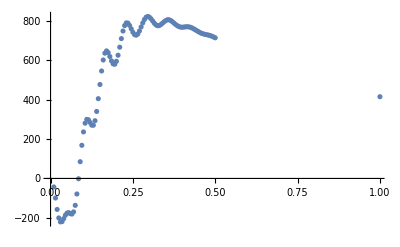

```mathematica
ListPlot[PSPT1loopRealSpTab]
```

## True Universe in redshift space, with Legendre Decomposition

```mathematica
Sqrt[10]//N
```

3.16228

neff[k]

```mathematica
hub=0.6777;omm=0.307;omb=0.048;ns=0.96;
```

```mathematica
ClearAll[EHPS]
αΓ=1-0.328*Log[431*omm*hub^2] omb/omm+0.38Log[22.3*omm*hub^2](omb/omm)^2;
ss=(44.5Log[9.83/(omm*hub^2)])/(√(1+10(omb*hub^2)^(3/4)))hub;
L0[q_]:=Log[2E+1.8q];
C0[q_]:=14.2+731/(1+62.5q);
EHtrans[q_]:=L0[q]/(L0[q]+C0[q] q^2);
q[k_]:=k*(2.726/2.7)^2(omm*hub(αΓ+(1-αΓ)/(1+(0.43*ss*k))))^-1;
EHPS[k_]:=k^ns*EHtrans[q[k]]^2/.paramSubs;
Clear[EHPSslope];
EHPSslope[kk_]=(Evaluate[k/EHPS[k] D[EHPS[k],k]]/.k:>kk);
```

```mathematica
dndlogk[kk_]:=(k*D[EHPSslope[k],k])/.k->kk;
d2ndlogk2[kk_]:=(k*D[k*D[EHPSslope[k],k],k])/.k->kk;
```

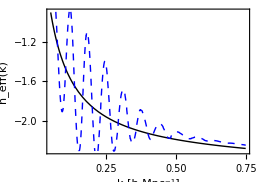

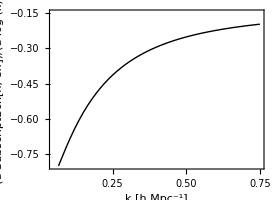

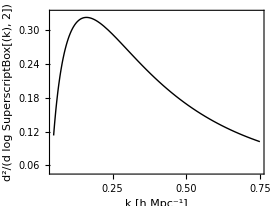

```mathematica
myplot1=Plot[{EHPSslope[kk],k/P11camb[k] D[P11camb[k],k]/.k->kk},{kk,0.05,0.75},Frame->True,Axes->False,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]","n_eff(k)"},PlotStyle->{{Thick,Black},{Thick,Blue,Dashed}},AspectRatio->0.7,PlotRange->{{0.05,0.75},{-2.3,-0.9}},ImageSize->260,ImagePadding->{{Automatic,1},{Automatic,1}}]
myplot2=Plot[{dndlogk[kk]},{kk,0.05,0.75},Frame->True,Axes->False,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]","(d SubscriptBox[n, eff])/(d log (k))"},PlotStyle->{Thick,Black},AspectRatio->0.73,ImageSize->275,PlotRange->{{0.05,0.75},{-0.8,-0.15}},ImagePadding->{{Automatic,1},{Automatic,1}}]
myplot3=Plot[{d2ndlogk2[kk]},{kk,0.05,0.75},Frame->True,Axes->False,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]","d^2/(d log SuperscriptBox[(k), 2])"},PlotStyle->{Thick,Black},AspectRatio->0.75,ImageSize->275,PlotRange->{{0.05,0.75},{0.05,0.33}},ImagePadding->{{Automatic,1},{Automatic,1}}]
Clear[q]
Clear[k]
```

## Redshift space Equations

```mathematica
A00[r_,x_]=1/98(3 r+7 x-10 r x^2)^2;
A11[r_,x_]=4 A00[r,x] ;
A12[r_,x_]=1/28(1-x^2)(7-6 r^2-42 r x + 48 r^2 x^2);
A22[r_,x_]=1/196(-49+637 x^2+42 r x (17-45 x^2)+6 r^2(19-157 x^2+236 x^4));
A23[r_,x_]=1/14(1-x^2)(7-42 r x -6 r^2+48 r^2 x^2);
A24[r_,x_]=3/16 r^2(1-x^2)^2;
A33[r_,x_]=1/14(-7+35 x^2+54 r x-110 r x^3+6 r^2- 66 r^2 x^2+88 r^2 x^4);
A34[r_,x_]=1/8(1-x^2)(2-3 r^2-12 r x+15 r^2 x^2);
A44[r_,x_]=1/16(-4+12 x^2+3 r^2+24 r x-30 r^2 x^2-40 r x^3+35 r^2 x^4);
Amatrix[r_,x_]={{A00[r,x],0,0,0,0},{0,A11[r,x],A12[r,x],0,0},{0,0,A22[r,x],A23[r,x],A24[r,x]},{0,0,0,A33[r,x],A34[r,x]},{0,0,0,0,A44[r,x]}};





B00[r_]=1/252(12/r^2-158+100 r^2-42 r^4+ 3/r^3(r^2-1)^3(7 r^2+2)Log[Abs[(1+r)/(1-r)]]);
B11[r_]=3 B00[r];
B12[r_]=1/168(18/r^2-178-66 r^2+18 r^4-9/r^3(r^2-1)^4 Log[Abs[(1+r)/(1-r)]]);
B22[r_]=1/168(18/r^2-218+126 r^2-54 r^4+9/r^3(r^2-1)^3(3 r^2+1)Log[Abs[(1+r)/(1-r)]]);
B23[r_]=-2/3;
Bmatrix[r_]={{B00[r],0,0,0},{0,B11[r],B12[r],0},{0,0,B22[r],B23[r]},{0,0,0,0}};








Pr11[k_,μ_,a_]=(1+f[zz[a]] μ^2)^2 Dgrowth[zz[a]]^2 P11in[k];


(*Pr22int[k_,μ_,r_,x_]=∑_(m=0)^4 ∑_(n=0)^4 μ^(2 n) f[zz[a]]^m  k^3/(4 π^2)P11[k r] P11[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦n+1,m+1⟧)/((1+r^2-2 r x)^2);
Pr13int[k_,μ_,r_,x_]=(1+ f[zz[a]] μ^2)P11[k] ∑_(m=0)^3 ∑_(n=0)^3 μ^(2 n) f[zz[a]]^m k^3/(4 π^2)P11[ k r] Bmatrix[r,x]⟦n+1,m+1⟧;*)

Pr22intn[k_,r_,x_,a_]=2{∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦0+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦1+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦2+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦3+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦4+1,m+1⟧)/((1+r^2-2 r x)^2)}Boole[k (1+r^2-2 r x)^(1/2)-k r>0];

Pr22n[k_,a_]:=NIntegrate[Pr22intn[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k}];

Pr22[k_,μ_,a_]:=∑_(n=0)^4 μ^(2 n) k^3/(4 π^2)Pr22n[k,a]⟦n+1⟧;
Pr22int[k_,μ_,r_,x_,a_]=∑_(n=0)^4 μ^(2 n) k^3/(4 π^2)Pr22intn[k,r,x,a]⟦n+1⟧;


Pr13intn[k_,r_,a_]=P11in[k]{∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦0+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦1+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦2+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦3+1,m+1⟧};

Pr13n[k_,a_]:=NIntegrate[Pr13intn[k,r,a],{r,0.001/k,Λ/k}];
Pr13[k_,μ_,a_]:=(1+ f[zz[a]] μ^2) ∑_(n=0)^3 μ^(2 n) k^3/(4 π^2)Pr13n[k,a]⟦n+1⟧;
Pr13int[k_,μ_,r_,a_]=(1+ f[zz[a]] μ^2) ∑_(n=0)^3 μ^(2 n) k^3/(4 π^2)Pr13intn[k,r,a]⟦n+1⟧;




Clear[Pr1loopint]
Pr1loopint[k_,μ_,r_,x_,a_]=(Pr22int[k,μ,r,x,a]+1/2 Pr13int[k,μ,r,a]);
Pr1loop[k_,μ_,a_]:=NIntegrate[Pr1loopint[k,μ,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->1,MaxRecursion->1];




kren[a_]=0.3+0.03  zz[a]^2;
NN[a_]=EHPSslope[kren[a]]+β dndlogk[kren[a]]/.{β-> -1.44};
cs1t[a_]=cs1 Dgrowth[zz[a]]^(4/(3+ NN[a]));
dcs1tdloga[a_]= cs1(4/(3+ NN[a])) Dgrowth[zz[a]]^(3/(4+3 NN[a]))f[zz[a]]; 

Pr11counterReal[k_,μ_,a_]=-Dgrowth[zz[a]]^2(2cs1t[a]+ (4 f[zz[a]]cs1t[a]+2 dcs1tdloga[a]) μ^2+2( cs1t[a] f[zz[a]]^2+f[zz[a]] dcs1tdloga[a]) μ^4 )  k^2/knl^2 P11in[k]/.knl-> 1;
Pr11counterRealγ[k_,μ_,a_]=Coefficient[-Dgrowth[zz[a]]^2(2cs1t[a]+ (4 f[zz[a]]cs1t[a]+2 dcs1tdloga[a](1+γ)) μ^2+2( cs1t[a] f[zz[a]]^2+f[zz[a]] dcs1tdloga[a](1+γ)) μ^4 )  k^2/knl^2 P11in[k]/.knl-> 1 , γ];
Prstoch[k_,μ_] = μ^4(k/knl)^4 1/knl^3 /. knl->1;
(*Pr11counterRedshift[k_,μ_,a_]=-Dgrowth[zz[a]]^2(1+ f[zz[a]] μ^2) ((c1 + c2) μ^2+( f[zz[a]] c1 + c3)μ^4) k^2/knl^2 P11in[k]/.knl-> 1;*)
Pr11counterRedshift[k_,μ_,a_]=-Dgrowth[zz[a]]^2(1+ f[zz[a]] μ^2) (c1 μ^2+c2 μ^4 + c3 μ^6) k^2/knl^2 P11in[k]/.knl-> 1;
Pr11counterRedshift2[k_,μ_,a_]=-Dgrowth[zz[a]]^2((1+ f[zz[a]] μ^2) (c1 μ^2+c2 μ^4) k^2/knl^2    +(-1/4 (c12 μ^2+c22 μ^4)^2 + (1+ f[zz[a]] μ^2)(c1p μ^2 + c2p μ^4 + c3p μ^6)  ) k^4/knl^4 )P11in[k]/.knl-> 1;

(* Matt has changed the coefficient in front of μ^4 to ( f c1 + c3) *)
```

The time factors of D are already taken into account for Pr11, Pr11counterReal, and Pr11counterRedshift.  However, the Pr1loopint has to be multiplied by D^4 later when doing the computations.

1-Loop Integrand

```mathematica
(*Amatrix[r_,x_]={{A00leo[r,x],0,0,0,0},{0,A11leo[r,x],A12leo[r,x],0,0},{0,0,A22leo[r,x],A23leo[r,x],A24leo[r,x]},{0,0,0,A33leo[r,x],A34leo[r,x]},{0,0,0,0,A44leo[r,x]}};

Bmatrix[r_]={{B00leo[r],0,0,0},{0,B11leo[r],B12leo[r],0},{0,0,B22leo[r],B23leo[r]},{0,0,0,0}};*)


Amatrix[r_,x_]={{A00[r,x],0,0,0,0},{0,A11[r,x],A12[r,x],0,0},{0,0,A22[r,x],A23[r,x],A24[r,x]},{0,0,0,A33[r,x],A34[r,x]},{0,0,0,0,A44[r,x]}};
Bmatrix[r_]={{B00[r],0,0,0},{0,B11[r],B12[r],0},{0,0,B22[r],B23[r]},{0,0,0,0}};

Pr13intn[k_,r_,a_]=P11in[k]{∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦0+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦1+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦2+1,m+1⟧,∑_(m=0)^3 f[zz[a]]^m P11in[ k r] Bmatrix[r]⟦3+1,m+1⟧};
Pr13int[k_,μ_,r_,a_]=(1+ f[zz[a]] μ^2) ∑_(n=0)^3 μ^(2 n) k^3/(4 π^2)Pr13intn[k,r,a]⟦n+1⟧;

Pr22intn[k_,r_,x_,a_]=2{∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦0+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦1+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦2+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦3+1,m+1⟧)/((1+r^2-2 r x)^2),∑_(m=0)^4 f[zz[a]]^m P11in[k r] P11in[k (1+r^2-2 r x)^(1/2)](Amatrix[r,x]⟦4+1,m+1⟧)/((1+r^2-2 r x)^2)}Boole[k (1+r^2-2 r x)^(1/2)-k r>0];
Pr22int[k_,μ_,r_,x_,a_]=∑_(n=0)^4 μ^(2 n) k^3/(4 π^2)Pr22intn[k,r,x,a]⟦n+1⟧;
Clear[Pr1loopint]
Pr1loopint[k_,μ_,r_,x_,a_]=(Pr22int[k,μ,r,x,a]+1/2 Pr13int[k,μ,r,a]);


LegendreSubs={μ^2->1/3 (1 LegendrePPP0+2LegendrePPP2),μ^4-> 1/35(7 LegendrePPP0+20LegendrePPP2+8LegendrePPP4),μ^6-> 1/231(33LegendrePPP0+110LegendrePPP2+72LegendrePPP4+16LegendrePPP6),μ^8-> (715 LegendrePPP0+8 (325 LegendrePPP2+270 LegendrePPP4+104 LegendrePPP6+16 LegendrePPP8))/6435};



Pr1loopintl0[k_,r_,x_,a_]=Coefficient[((Pr1loopint[k,μ,r,x,a]//Expand)/.LegendreSubs),LegendrePPP0]+((Pr1loopint[k,μ,r,x,a]//Expand)/.{μ->0});
Pr1loopintl2[k_,r_,x_,a_]=Coefficient[((Pr1loopint[k,μ,r,x,a]//Expand)/.LegendreSubs),LegendrePPP2];
Pr1loopintl4[k_,r_,x_,a_]=Coefficient[((Pr1loopint[k,μ,r,x,a]//Expand)/.LegendreSubs),LegendrePPP4];
Pr1loopintl6[k_,r_,x_,a_]=Coefficient[((Pr1loopint[k,μ,r,x,a]//Expand)/.LegendreSubs),LegendrePPP6];
Pr1loopintl8[k_,r_,x_,a_]=Coefficient[((Pr1loopint[k,μ,r,x,a]//Expand)/.LegendreSubs),LegendrePPP8];
```

## Real Space Calculation

### P_(1-loop-SPT-real)

```mathematica
PSPT1loopRealSpTab=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/PSPT1loopRealSpTab_v3.dat"];
PSPT1loopRealSpint=Interpolation[PSPT1loopRealSpTab];
```

### P_(cs-rel)

```mathematica
P11csRealSP[k_,a_]=-Dgrowth[zz[a]]^2 2 cs1t[a]  k^2/knl^2 P11in[k]/.knl-> 1;
```

### P_(1-loop-SPT-total)

```mathematica
Clear[PSPT1loopTotRealSpTab,PSPT1loopTotRealSpint]
PSPT1loopTotRealSpTab[a_]:=Monitor[Table[{k,Dgrowth[zz[a]]^2 P11in[k]+Dgrowth[zz[a]]^4 PSPT1loopRealSpint[k]},{k,0.025,0.5,0.01}],k];
PSPT1loopTotRealSpint[a_]:=Interpolation[PSPT1loopTotRealSpTab[a]];
```

## Legendre Decomposition linear-level

```mathematica
LegendreSubs={μ^2->1/3 (1 LegendrePPP0+2LegendrePPP2),μ^4-> 1/35(7 LegendrePPP0+20LegendrePPP2+8LegendrePPP4),μ^6-> 1/231(33LegendrePPP0+110LegendrePPP2+72LegendrePPP4+16LegendrePPP6),μ^8-> (715 LegendrePPP0+8 (325 LegendrePPP2+270 LegendrePPP4+104 LegendrePPP6+16 LegendrePPP8))/6435};
```

```mathematica
Prlinearl0[k_,a_]=Coefficient[((Pr11[k,μ,a]//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11[k,μ,a]//Expand)/.μ->0);
Prlinearl2[k_,a_]=Coefficient[((Pr11[k,μ,a]//Expand)/.LegendreSubs),LegendrePPP2];
Prlinearl4[k_,a_]=Coefficient[((Pr11[k,μ,a]//Expand)/.LegendreSubs),LegendrePPP4];
```

```mathematica
Clear[Prlinearl0tab,Prlinearl2tab,Prlinearl4tab]
Prlinearl0tab[a_]:=Table[{k,Prlinearl0[k,a]},{k,0.025,0.625,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl0tab.dat",Prlinearl0tab];*)
Prlinearl2tab[a_]:=Table[{k,Prlinearl2[k,a]},{k,0.025,0.625,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl2tab.dat",Prlinearl2tab];*)
Prlinearl4tab[a_]:=Table[{k,Prlinearl4[k,a]},{k,0.025,0.625,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl4tab.dat",Prlinearl4tab]*)
```

```mathematica
Clear[Prlinearl0tab,Prlinearl2tab,Prlinearl4tab]
Prlinearl0tab[a_]:=Table[{k,Prlinearl0[k,a]},{k,0.0001,1000,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl0tab.dat",Prlinearl0tab];*)
Prlinearl2tab[a_]:=Table[{k,Prlinearl2[k,a]},{k,0.0001,1000,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl2tab.dat",Prlinearl2tab];*)
Prlinearl4tab[a_]:=Table[{k,Prlinearl4[k,a]},{k,0.0001,1000,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prlinearl4tab.dat",Prlinearl4tab]*)
```

```mathematica
Clear[Prlinearl0int,Prlinearl2int,Prlinearl4int]
Prlinearl0int[a_]:=Interpolation[Prlinearl0tab[a]];
Prlinearl2int[a_]:=Interpolation[Prlinearl2tab[a]];
Prlinearl4int[a_]:=Interpolation[Prlinearl4tab[a]];
```

```mathematica
Prlinearl0int[1]=Interpolation[Prlinearl0tab[1]];
Prlinearl2int[1]=Interpolation[Prlinearl2tab[1]];
Prlinearl4int[1]=Interpolation[Prlinearl4tab[1]];
```

```mathematica
Prlinearl0int[ap56]=Interpolation[Prlinearl0tab[ap56]];
Prlinearl2int[ap56]=Interpolation[Prlinearl2tab[ap56]];
Prlinearl4int[ap56]=Interpolation[Prlinearl4tab[ap56]];
```

```mathematica
Prlinearl0int[a1]=Interpolation[Prlinearl0tab[a1]];
Prlinearl2int[a1]=Interpolation[Prlinearl2tab[a1]];
Prlinearl4int[a1]=Interpolation[Prlinearl4tab[a1]];
```

## Legendre Decomposition 1-loop

Be careful with factors of D^4 here, the easiest would be to just include them in the Pr1loopl0 expressions below, but I’m adding them at the end because I initially forgot them.

```mathematica
Clear[Pr1loopl0,Pr1loopl2,Pr1loopl4,Pr1loopl6,Pr1loopl8]
Pr1loopl0[a_][k_]:=NIntegrate[Pr1loopintl0[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->2,MaxRecursion->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}];
Pr1loopl2[a_][k_]:=NIntegrate[Pr1loopintl2[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->2,MaxRecursion->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}];
Pr1loopl4[a_][k_]:=NIntegrate[Pr1loopintl4[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->2,MaxRecursion->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
Pr1loopl6[a_][k_]:=NIntegrate[Pr1loopintl6[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->2,MaxRecursion->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
Pr1loopl8[a_][k_]:=NIntegrate[Pr1loopintl8[k,r,x,a],{x,-1,1},{r,0.001/k,Λ/k},AccuracyGoal->2,MaxRecursion->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
```

```mathematica
exttab1 = {1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,.6,.8,.5,.53,.56,.63,.66,.69,.72,.75,.78};
```

```mathematica
Clear[Pr1loopl0tab , Pr1loopl2tab, Pr1loopl4tab , Pr1loopl6tab , Pr1loopl8tab,Pr1loopl0int,Pr1loopl2int,Pr1loopl4int,Pr1loopl6int,Pr1loopl8int]
```

```mathematica
Pr1loopl0tab[ap56]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a0.640287_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a0.640287_apr18ext1.dat"]];
Pr1loopl2tab[ap56]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a0.640287_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a0.640287_apr18ext1.dat"]];
Pr1loopl4tab[ap56]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a0.640287_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a0.640287_apr18ext1.dat"]];
Pr1loopl6tab[ap56]=Join[Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a0.640287_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a0.640287_apr18ext1.dat"]];
Pr1loopl8tab[ap56]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a0.640287_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a0.640287_apr18ext1.dat"]];

tempfn=Interpolation[Pr1loopl0tab[ap56]];
Pr1loopl0int[ap56][k_]=Dgrowth[zz[ap56]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl2tab[ap56]];
Pr1loopl2int[ap56][k_]=Dgrowth[zz[ap56]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl4tab[ap56]];
Pr1loopl4int[ap56][k_]=Dgrowth[zz[ap56]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl6tab[ap56]];
Pr1loopl6int[ap56][k_]=Dgrowth[zz[ap56]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl8tab[ap56]];
Pr1loopl8int[ap56][k_]=Dgrowth[zz[ap56]]^4 tempfn[k];
```

```mathematica
Pr1loopl0tab[1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a1_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a1_apr18ext.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a1_apr18ext2.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a1_apr18ext3.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a1_apr18ext4.dat"]] ;
Pr1loopl2tab[1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a1_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a1_apr18ext.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a1_apr18ext2.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a1_apr18ext3.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a1_apr18ext4.dat"]] ;
Pr1loopl4tab[1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a1_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a1_apr18ext.dat"],Import[NotebookDirectory[]<> "redshift_real_universe/mathematics/Pr1loopl4tab_a1_apr18ext2.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a1_apr18ext3.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a1_apr18ext4.dat"]];
Pr1loopl6tab[1]=Join[Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a1_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a1_apr18ext.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a1_apr18ext2.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a1_apr18ext3.dat"],
Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a1_apr18ext4.dat"]];
Pr1loopl8tab[1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a1_apr18.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a1_apr18ext.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a1_apr18ext2.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a1_apr18ext3.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a1_apr18ext4.dat"]];

Pr1loopl0int[1]=Interpolation[Pr1loopl0tab[1]];
Pr1loopl2int[1]=Interpolation[Pr1loopl2tab[1]];
Pr1loopl4int[1]=Interpolation[Pr1loopl4tab[1]];
Pr1loopl6int[1]=Interpolation[Pr1loopl6tab[1]];
Pr1loopl8int[1]=Interpolation[Pr1loopl8tab[1]];
```

```mathematica
Pr1loopl0tab[a1]=Join[Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a0.5_aug12.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl0tab_a0.5_apr12ext1.dat"]];
Pr1loopl2tab[a1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a0.5_aug12.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl2tab_a0.5_apr12ext1.dat"]];
Pr1loopl4tab[a1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a0.5_aug12.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl4tab_a0.5_apr12ext1.dat"]];
Pr1loopl6tab[a1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a0.5_aug12.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl6tab_a0.5_apr12ext1.dat"]];
Pr1loopl8tab[a1]=Join[ Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a0.5_aug12.dat"],Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/Pr1loopl8tab_a0.5_apr12ext1.dat"]];

tempfn=Interpolation[Pr1loopl0tab[a1]];
Pr1loopl0int[a1][k_]=Dgrowth[zz[a1]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl2tab[a1]];
Pr1loopl2int[a1][k_]=Dgrowth[zz[a1]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl4tab[a1]];
Pr1loopl4int[a1][k_]=Dgrowth[zz[a1]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl6tab[a1]];
Pr1loopl6int[a1][k_]=Dgrowth[zz[a1]]^4 tempfn[k];
tempfn=Interpolation[Pr1loopl8tab[a1]];
Pr1loopl8int[a1][k_]=Dgrowth[zz[a1]]^4 tempfn[k];
```

## Legendre Decomposition SPT 1-loop

```mathematica
Clear[PrSPT1loopl0tab,PrSPT1loopl2tab,PrSPT1loopl4tab,PrSPT1loopl6tab,PrSPT1loopl8tab]
PrSPT1loopl0tab[a_]:= Table[{k,Prlinearl0int[a][k]+Pr1loopl0int[a][k]},{k,0.025,0.65,0.01}]  ;
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PrSPT1loopl0tab.dat",Pr1loopl0tab]*)
PrSPT1loopl2tab[a_]:=Table[{k,Prlinearl2int[a][k]+Pr1loopl2int[a][k]},{k,0.025,0.65,0.01}] ;
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PrSPT1loopl2tab.dat",PrSPT1loopl2tab]*)
PrSPT1loopl4tab[a_]:=Table[{k,Prlinearl4int[a][k]+Pr1loopl4int[a][k]},{k,0.025,0.65,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PrSPT1loopl4tab.dat",PrSPT1loopl4tab]*)
PrSPT1loopl6tab[a_]:=Table[{k,0+Pr1loopl6int[a][k]},{k,0.025,0.625,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PrSPT1loopl6tab.dat",PrSPT1loopl6tab]*)
PrSPT1loopl8tab[a_]:=Table[{k,0+Pr1loopl8int[a][k]},{k,0.025,0.625,0.01}];
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/PrSPT1loopl8tab.dat",PrSPT1loopl8tab]*)
```

```mathematica
Clear[PrSPT1loopl0int,PrSPT1loopl2int,PrSPT1loopl4int,PrSPT1loopl6int,PrSPT1loopl8int]
PrSPT1loopl0int[a_]:=Interpolation[PrSPT1loopl0tab[a]];
PrSPT1loopl2int[a_]:=Interpolation[PrSPT1loopl2tab[a]];
PrSPT1loopl4int[a_]:=Interpolation[PrSPT1loopl4tab[a]];
PrSPT1loopl6int[a_]:=Interpolation[PrSPT1loopl6tab[a]];
PrSPT1loopl8int[a_]:=Interpolation[PrSPT1loopl8tab[a]];
```

## Legendre Decomposition cscounter

```mathematica
Prcsl0[k_,a_]=Coefficient[((Pr11counterReal[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterReal[k,μ,a]/.cs1-> 1//Expand)/.{μ->0});
Prcsl2[k_,a_]=Coefficient[((Pr11counterReal[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP2];
Prcsl4[k_,a_]=Coefficient[((Pr11counterReal[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP4];
```

```mathematica
Clear[Prcsl0tab,Prcsl2tab,Prcsl4tab]
Prcsl0tab[a_]:=Table[{k,Prcsl0[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
Prcsl2tab[a_]:=Table[{k,Prcsl2[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
Prcsl4tab[a_]:=Table[{k,Prcsl4[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
Clear[Prcsl0tabext,Prcsl2tabext,Prcsl4tabext]
Prcsl0tabext[a_]:=Table[{k,Prcsl0[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
Prcsl2tabext[a_]:=Table[{k,Prcsl2[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
Prcsl4tabext[a_]:=Table[{k,Prcsl4[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
Clear[Pcsl0int,Pcsl2int,Pcsl4int]
Pcsl0int[a_]:=Interpolation[Join[ Prcsl0tab[a],Prcsl0tabext[a]]];
Pcsl2int[a_]:=Interpolation[Join[ Prcsl2tab[a],Prcsl2tabext[a]]];
Pcsl4int[a_]:=Interpolation[Join[ Prcsl4tab[a],Prcsl4tabext[a]]];
```

## Legendre Decomposition cscounter: free time dep.

```mathematica
Prcsl0γ[k_,a_]=Coefficient[((Pr11counterRealγ[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRealγ[k,μ,a]/.cs1-> 1//Expand)/.{μ->0});
Prcsl2γ[k_,a_]=Coefficient[((Pr11counterRealγ[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP2];
Prcsl4γ[k_,a_]=Coefficient[((Pr11counterRealγ[k,μ,a]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP4];
```

```mathematica
Clear[Prcsl0tabγ,Prcsl2tabγ,Prcsl4tabγ]
Prcsl0tabγ[a_]:=Table[{k,Prcsl0γ[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
Prcsl2tabγ[a_]:=Table[{k,Prcsl2γ[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
Prcsl4tabγ[a_]:=Table[{k,Prcsl4γ[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
Clear[Prcsl0tabγext,Prcsl2tabγext,Prcsl4tabγext]
Prcsl0tabγext[a_]:=Table[{k,Prcsl0γ[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
Prcsl2tabγext[a_]:=Table[{k,Prcsl2γ[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
Prcsl4tabγext[a_]:=Table[{k,Prcsl4γ[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
Pcsl0intγ[a_]:=Interpolation[Join[ Prcsl0tabγ[a],Prcsl0tabγext[a]]];
Pcsl2intγ[a_]:=Interpolation[Join[ Prcsl2tabγ[a],Prcsl2tabγext[a]]];
Pcsl4intγ[a_]:=Interpolation[Join[ Prcsl4tabγ[a],Prcsl4tabγext[a]]];
```

## Legendre Decomposition c1counter

```mathematica
Prc1l0[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.{μ->0});
Prc1l2[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.LegendreSubs),LegendrePPP2];
Prc1l4[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.LegendreSubs),LegendrePPP4];
Prc1l6[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.LegendreSubs),LegendrePPP6];
Prc1l8[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->0/.c1-> 1//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc1l0tab[a_]:=Table[{k,Prc1l0[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1l2tab[a_]:=Table[{k,Prc1l2[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1l4tab[a_]:=Table[{k,Prc1l4[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1l6tab[a_]:=Table[{k,Prc1l6[k,a]},{k,0.025,0.625,0.01}]
Prc1l8tab[a_]:=Table[{k,Prc1l8[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc1l0tabext[a_]:=Table[{k,Prc1l0[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1l2tabext[a_]:=Table[{k,Prc1l2[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1l4tabext[a_]:=Table[{k,Prc1l4[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1l6tabext[a_]:=Table[{k,Prc1l6[k,a]},{k,.7,10,0.5}]
Prc1l8tabext[a_]:=Table[{k,Prc1l8[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc1l0int[a_]:=Interpolation[Join[ Prc1l0tab[a],Prc1l0tabext[a]]];
Pc1l2int[a_]:=Interpolation[Join[Prc1l2tab[a],Prc1l2tabext[a]]];
Pc1l4int[a_]:=Interpolation[Join[Prc1l4tab[a],Prc1l4tabext[a]]];
Pc1l6int[a_]:=Interpolation[Join[Prc1l6tab[a],Prc1l6tabext[a]]];
Pc1l8int[a_]:=Interpolation[Join[Prc1l8tab[a],Prc1l8tabext[a]]];
```

## Legendre Decomposition c1^2 counter: 2 loop

```mathematica
Prc1l02loop[k_,a_]= Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.{μ->0});
Prc1l22loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.LegendreSubs),LegendrePPP2];
Prc1l42loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.LegendreSubs),LegendrePPP4];
Prc1l62loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.LegendreSubs),LegendrePPP6];
Prc1l82loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->0,c12-> 1}//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc1l0tab2loop[a_]:=Table[{k,Prc1l02loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1l2tab2loop[a_]:=Table[{k,Prc1l22loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1l4tab2loop[a_]:=Table[{k,Prc1l42loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1l6tab2loop[a_]:=Table[{k,Prc1l62loop[k,a]},{k,0.025,0.625,0.01}]
Prc1l8tab2loop[a_]:=Table[{k,Prc1l82loop[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc1l0tabext2loop[a_]:=Table[{k,Prc1l02loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1l2tabext2loop[a_]:=Table[{k,Prc1l22loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1l4tabext2loop[a_]:=Table[{k,Prc1l42loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1l6tabext2loop[a_]:=Table[{k,Prc1l62loop[k,a]},{k,.7,10,0.5}]
Prc1l8tabext2loop[a_]:=Table[{k,Prc1l82loop[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc1l02loopint[a_]:=Interpolation[Join[ Prc1l0tab2loop[a],Prc1l0tabext2loop[a]]];
Pc1l22loopint[a_]:=Interpolation[Join[Prc1l2tab2loop[a],Prc1l2tabext2loop[a]]];
Pc1l42loopint[a_]:=Interpolation[Join[Prc1l4tab2loop[a],Prc1l4tabext2loop[a]]];
Pc1l62loopint[a_]:=Interpolation[Join[Prc1l6tab2loop[a],Prc1l6tabext2loop[a]]];
Pc1l82loopint[a_]:=Interpolation[Join[Prc1l8tab2loop[a],Prc1l8tabext2loop[a]]];
```

## Legendre Decomposition c2counter

```mathematica
Prc2l0[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.{μ->0});
Prc2l2[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP2];
Prc2l4[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP4];
Prc2l6[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP6];
Prc2l8[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 1/.c3->0/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc2l0tab[a_]:=Table[{k,Prc2l0[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2l2tab[a_]:=Table[{k,Prc2l2[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2l4tab[a_]:=Table[{k,Prc2l4[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2l6tab[a_]:=Table[{k,Prc2l6[k,a]},{k,0.025,0.625,0.01}];
Prc2l8tab[a_]:=Table[{k,Prc2l8[k,a]},{k,0.025,0.625,0.01}];
```

```mathematica
Prc2l0tabext[a_]:=Table[{k,Prc2l0[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2l2tabext[a_]:=Table[{k,Prc2l2[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2l4tabext[a_]:=Table[{k,Prc2l4[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2l6tabext[a_]:=Table[{k,Prc2l6[k,a]},{k,.7,10,0.5}]
Prc2l8tabext[a_]:=Table[{k,Prc2l8[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc2l0int[a_]:=Interpolation[Join[ Prc2l0tab[a],Prc2l0tabext[a]]];
Pc2l2int[a_]:=Interpolation[Join[Prc2l2tab[a],Prc2l2tabext[a]]];
Pc2l4int[a_]:=Interpolation[Join[Prc2l4tab[a],Prc2l4tabext[a]]];
Pc2l6int[a_]:=Interpolation[Join[Prc2l6tab[a],Prc2l6tabext[a]]];
Pc2l8int[a_]:=Interpolation[Join[Prc2l8tab[a],Prc2l8tabext[a]]];
```

## Legendre Decomposition c2^2counter: 2 loop

```mathematica
Prc2l02loop[k_,a_]= Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.{μ->0});
Prc2l22loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP2];
Prc2l42loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP4];
Prc2l62loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP6];
Prc2l82loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->0, c1->0,c22->1,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc2l0tab2loop[a_]:=Table[{k,Prc2l02loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2l2tab2loop[a_]:=Table[{k,Prc2l22loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2l4tab2loop[a_]:=Table[{k,Prc2l42loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2l6tab2loop[a_]:=Table[{k,Prc2l62loop[k,a]},{k,0.025,0.625,0.01}]
Prc2l8tab2loop[a_]:=Table[{k,Prc2l82loop[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc2l0tabext2loop[a_]:=Table[{k,Prc2l02loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2l2tabext2loop[a_]:=Table[{k,Prc2l22loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2l4tabext2loop[a_]:=Table[{k,Prc2l42loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2l6tabext2loop[a_]:=Table[{k,Prc2l62loop[k,a]},{k,.7,10,0.5}]
Prc2l8tabext2loop[a_]:=Table[{k,Prc2l82loop[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc2l02loopint[a_]:=Interpolation[Join[ Prc2l0tab2loop[a],Prc2l0tabext2loop[a]]];
Pc2l22loopint[a_]:=Interpolation[Join[Prc2l2tab2loop[a],Prc2l2tabext2loop[a]]];
Pc2l42loopint[a_]:=Interpolation[Join[Prc2l4tab2loop[a],Prc2l4tabext2loop[a]]];
Pc2l62loopint[a_]:=Interpolation[Join[Prc2l6tab2loop[a],Prc2l6tabext2loop[a]]];
Pc2l82loopint[a_]:=Interpolation[Join[Prc2l8tab2loop[a],Prc2l8tabext2loop[a]]];
```

## Legendre Decomposition c1p counter: 2 loop

```mathematica
Prc1pl02loop[k_,a_]= Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.{μ->0});
Prc1pl22loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP2];
Prc1pl42loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP4];
Prc1pl62loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP6];
Prc1pl82loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc1pl0tab2loop[a_]:=Table[{k,Prc1pl02loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1pl2tab2loop[a_]:=Table[{k,Prc1pl22loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1pl4tab2loop[a_]:=Table[{k,Prc1pl42loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1pl6tab2loop[a_]:=Table[{k,Prc1pl62loop[k,a]},{k,0.025,0.625,0.01}]
Prc1pl8tab2loop[a_]:=Table[{k,Prc1pl82loop[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc1pl0tabext2loop[a_]:=Table[{k,Prc1pl02loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc1pl2tabext2loop[a_]:=Table[{k,Prc1pl22loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc1pl4tabext2loop[a_]:=Table[{k,Prc1pl42loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc1pl6tabext2loop[a_]:=Table[{k,Prc1pl62loop[k,a]},{k,.7,10,0.5}]
Prc1pl8tabext2loop[a_]:=Table[{k,Prc1pl82loop[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc1pl02loopint[a_]:=Interpolation[Join[ Prc1pl0tab2loop[a],Prc1pl0tabext2loop[a]]];
Pc1pl22loopint[a_]:=Interpolation[Join[Prc1pl2tab2loop[a],Prc1pl2tabext2loop[a]]];
Pc1pl42loopint[a_]:=Interpolation[Join[Prc1pl4tab2loop[a],Prc1pl4tabext2loop[a]]];
Pc1pl62loopint[a_]:=Interpolation[Join[Prc1pl6tab2loop[a],Prc1pl6tabext2loop[a]]];
Pc1pl82loopint[a_]:=Interpolation[Join[Prc1pl8tab2loop[a],Prc1pl8tabext2loop[a]]];
```

## Legendre Decomposition c2p counter: 2 loop

```mathematica
Prc2pl02loop[k_,a_]= Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->1, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.{c2-> 0,c3->0, c1p->1 , c2p->0, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.{μ->0});
Prc2pl22loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->1, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP2];
Prc2pl42loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->1, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP4];
Prc2pl62loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->1, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP6];
Prc2pl82loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->1, c3p->0, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc2pl0tab2loop[a_]:=Table[{k,Prc2pl02loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2pl2tab2loop[a_]:=Table[{k,Prc2pl22loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2pl4tab2loop[a_]:=Table[{k,Prc2pl42loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2pl6tab2loop[a_]:=Table[{k,Prc2pl62loop[k,a]},{k,0.025,0.625,0.01}]
Prc2pl8tab2loop[a_]:=Table[{k,Prc2pl82loop[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc2pl0tabext2loop[a_]:=Table[{k,Prc2pl02loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc2pl2tabext2loop[a_]:=Table[{k,Prc2pl22loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc2pl4tabext2loop[a_]:=Table[{k,Prc2pl42loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc2pl6tabext2loop[a_]:=Table[{k,Prc2pl62loop[k,a]},{k,.7,10,0.5}]
Prc2pl8tabext2loop[a_]:=Table[{k,Prc2pl82loop[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc2pl02loopint[a_]:=Interpolation[Join[ Prc2pl0tab2loop[a],Prc2pl0tabext2loop[a]]];
Pc2pl22loopint[a_]:=Interpolation[Join[Prc2pl2tab2loop[a],Prc2pl2tabext2loop[a]]];
Pc2pl42loopint[a_]:=Interpolation[Join[Prc2pl4tab2loop[a],Prc2pl4tabext2loop[a]]];
Pc2pl62loopint[a_]:=Interpolation[Join[Prc2pl6tab2loop[a],Prc2pl6tabext2loop[a]]];
Pc2pl82loopint[a_]:=Interpolation[Join[Prc2pl8tab2loop[a],Prc2pl8tabext2loop[a]]];
```

## Legendre Decomposition c3p counter: 2 loop

```mathematica
Prc3pl02loop[k_,a_]= Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.{μ->0});
Prc3pl22loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP2];
Prc3pl42loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP4];
Prc3pl62loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP6];
Prc3pl82loop[k_,a_]=Coefficient[((Pr11counterRedshift2[k,μ,a]/.{c2-> 0,c3->0, c1p->0 , c2p->0, c3p->1, c1->0,c22->0,c12-> 0}//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc3pl0tab2loop[a_]:=Table[{k,Prc3pl02loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc3pl2tab2loop[a_]:=Table[{k,Prc3pl22loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc3pl4tab2loop[a_]:=Table[{k,Prc3pl42loop[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc3pl6tab2loop[a_]:=Table[{k,Prc3pl62loop[k,a]},{k,0.025,0.625,0.01}]
Prc3pl8tab2loop[a_]:=Table[{k,Prc3pl82loop[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Prc3pl0tabext2loop[a_]:=Table[{k,Prc3pl02loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc3pl2tabext2loop[a_]:=Table[{k,Prc3pl22loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc3pl4tabext2loop[a_]:=Table[{k,Prc3pl42loop[k,a]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc3pl6tabext2loop[a_]:=Table[{k,Prc3pl62loop[k,a]},{k,.7,10,0.5}]
Prc3pl8tabext2loop[a_]:=Table[{k,Prc3pl82loop[k,a]},{k,.7,10,0.5}]
```

```mathematica
Pc3pl02loopint[a_]:=Interpolation[Join[ Prc3pl0tab2loop[a],Prc3pl0tabext2loop[a]]];
Pc3pl22loopint[a_]:=Interpolation[Join[Prc3pl2tab2loop[a],Prc3pl2tabext2loop[a]]];
Pc3pl42loopint[a_]:=Interpolation[Join[Prc3pl4tab2loop[a],Prc3pl4tabext2loop[a]]];
Pc3pl62loopint[a_]:=Interpolation[Join[Prc3pl6tab2loop[a],Prc3pl6tabext2loop[a]]];
Pc3pl82loopint[a_]:=Interpolation[Join[Prc3pl8tab2loop[a],Prc3pl8tabext2loop[a]]];
```

## Legendre Decomposition c3counter

```mathematica
Prc3l0[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.{μ->0});
Prc3l2[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP2];
Prc3l4[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP4];
Prc3l6[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP6];
Prc3l8[k_,a_]=Coefficient[((Pr11counterRedshift[k,μ,a]/.c2-> 0/.c3->1/.c1-> 0//Expand)/.LegendreSubs),LegendrePPP8];
```

```mathematica
Prc3l0tab[a_]:=Table[{k,Prc3l0[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal0.dat",Prcal0tab]*)
Prc3l2tab[a_]:=Table[{k,Prc3l2[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal2tab.dat",Prcal2tab]*)
Prc3l4tab[a_]:=Table[{k,Prc3l4[k,a]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcal4tab.dat",Prcal4tab]*)
Prc3l6tab[a_]:=Table[{k,Prc3l6[k,a]},{k,0.025,0.625,0.01}]
Prc3l8tab[a_]:=Table[{k,Prc3l8[k,a]},{k,0.025,0.625,0.01}]
```

```mathematica
Pc3l0int[a_]:=Interpolation[Prc3l0tab[a]];
Pc3l2int[a_]:=Interpolation[Prc3l2tab[a]];
Pc3l4int[a_]:=Interpolation[Prc3l4tab[a]];
Pc3l6int[a_]:=Interpolation[Prc3l6tab[a]];
Pc3l8int[a_]:=Interpolation[Prc3l8tab[a]];
```

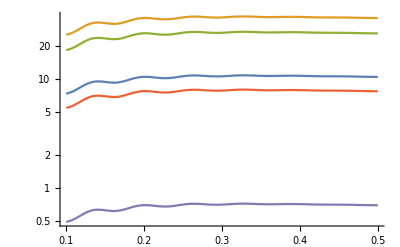

```mathematica
LogPlot[{Abs[Pc3l0int[ap56][k]],Abs[Prc3l2[k,ap56]],Abs[Prc3l4[k,ap56]],Abs[Prc3l6[k,ap56]],Abs[Prc3l8[k,ap56]]},{k,0.1,0.5}]
```

## Legendre Decomposition STOCHASTIC

```mathematica
PrStoch[0][k_]=Coefficient[((Prstoch[k,μ] //Expand)/.LegendreSubs),LegendrePPP0]+((Prstoch[k,μ]//Expand)/.{μ->0});
PrStoch[2][k_]=Coefficient[((Prstoch[k,μ]//Expand)/.LegendreSubs),LegendrePPP2];
PrStoch[4][k_]=Coefficient[((Prstoch[k,μ]//Expand)/.LegendreSubs),LegendrePPP4];
```

## Sims Data a=1, z=0

```mathematica
PNLdatatabimpCoyote0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/data_redshift/pknl_redshift_0.dat"];
PNLdatatabCoyote0=Table[{PNLdatatabimpCoyote0⟦i,1⟧,PNLdatatabimpCoyote0⟦i,2⟧},{i,1,Length[PNLdatatabimpCoyote0]}];
PNLdataintCoyote0=Interpolation[PNLdatatabCoyote0];
```

```mathematica
PNLdatatabimpz0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/data_redshift/pknl_redshift_0_data.dat"];
PNLdatatabz0=Table[{PNLdatatabimpz0⟦i,1⟧,PNLdatatabimpz0⟦i,2⟧},{i,1,Length[PNLdatatabimpz0]}];
NmodesdataNLtabz0=Table[{PNLdatatabimpz0⟦i,1⟧,PNLdatatabimpz0⟦i,3⟧},{i,1,Length[PNLdatatabimpz0]}];
PNLdataintz0=Interpolation[PNLdatatabz0];

ErrordataNLtabz0=Table[{PNLdatatabz0⟦i,1⟧,Abs[PNLdatatabz0⟦i,2⟧](((2/NmodesdataNLtabz0⟦i,2⟧)^(1/2)(1+1/(PNLdatatabz0⟦i,2⟧ 283105845/2500^3)))^2+0.01^2)^(1/2)},{i,1,Length[PNLdatatabimpz0]}];

ErrordataNLintz0=Interpolation[ErrordataNLtabz0];
```

```mathematica
(*PNLdatatabimpDATA0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/data_redshift/PNL.Particles.0029.0050.CICassign.NGPbin.pk.dat"];
PNLdatatabDATA0=Table[{PNLdatatabimpDATA0⟦i,1⟧,PNLdatatabimpDATA0⟦i,2⟧},{i,1,Length[PNLdatatabimpDATA0]}];
PNLdataintDAA0=Interpolation[PNLdatatabDATA0];*)
```

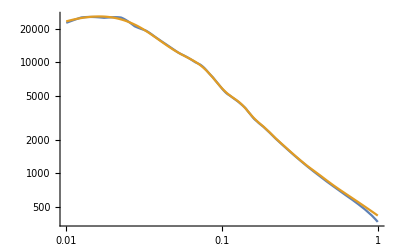

```mathematica
LogLogPlot[{PNLdataintz0[k],PNLdataintCoyote0[k],0PNLdataintDAA0[k]},{k,0.01,1}]
```

```mathematica
LogLogPlot[{PNLdataintz0[k],PNLdataintCoyote0[k]},{k,0.01,1}]
```

-Graphics-

```mathematica
Pr1datatotl0tab1z0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_128.dat.CICassign.mono.dat"];
Pr1datatotl2tab1z0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_128.dat.CICassign.quad.dat"];
Pr1datatotl4tab1z0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_128.dat.CICassign.four.dat"];
Pr1datatotl6tab1z0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_128.dat.CICassign.six.dat"];
Pr1datatotl8tab1z0=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_128.dat.CICassign.oct.dat"];
```

```mathematica
Pr1datal0tabz0=Table[{Pr1datatotl0tab1z0⟦i,1⟧,Pr1datatotl0tab1z0⟦i,2⟧},{i,1,Length[Pr1datatotl0tab1z0]}];
Pr1datal2tabz0=Table[{Pr1datatotl2tab1z0⟦i,1⟧,Pr1datatotl2tab1z0⟦i,2⟧},{i,1,Length[Pr1datatotl2tab1z0]}];
Pr1datal4tabz0=Table[{Pr1datatotl4tab1z0⟦i,1⟧,Pr1datatotl4tab1z0⟦i,2⟧},{i,1,Length[Pr1datatotl4tab1z0]}];
Pr1datal6tabz0=Table[{Pr1datatotl6tab1z0⟦i,1⟧,Pr1datatotl6tab1z0⟦i,2⟧},{i,1,Length[Pr1datatotl6tab1z0]}];
Pr1datal8tabz0=Table[{Pr1datatotl8tab1z0⟦i,1⟧,Pr1datatotl8tab1z0⟦i,2⟧},{i,1,Length[Pr1datatotl8tab1z0]}];

Nmodesdatal0tabz0=Table[{Pr1datatotl0tab1z0⟦i,1⟧,Pr1datatotl0tab1z0⟦i,3⟧},{i,1,Length[Pr1datatotl0tab1z0]}];Nmodesdatal2tabz0=Table[{Pr1datatotl2tab1z0⟦i,1⟧,Pr1datatotl2tab1z0⟦i,3⟧},{i,1,Length[Pr1datatotl2tab1z0]}];
Nmodesdatal4tabz0=Table[{Pr1datatotl4tab1z0⟦i,1⟧,Pr1datatotl4tab1z0⟦i,3⟧},{i,1,Length[Pr1datatotl4tab1z0]}];
Nmodesdatal6tabz0=Table[{Pr1datatotl6tab1z0⟦i,1⟧,Pr1datatotl6tab1z0⟦i,3⟧},{i,1,Length[Pr1datatotl6tab1z0]}];
Nmodesdatal8tabz0=Table[{Pr1datatotl8tab1z0⟦i,1⟧,Pr1datatotl8tab1z0⟦i,3⟧},{i,1,Length[Pr1datatotl8tab1z0]}];

Errordatal0tabz0=Table[{Pr1datatotl0tab1z0⟦i,1⟧,Abs[Pr1datatotl0tab1z0⟦i,2⟧](Pr1datatotl0tab1z0⟦i,4⟧^2/Pr1datatotl0tab1z0⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl0tab1z0]}];
Errordatal2tabz0=Table[{Pr1datatotl2tab1z0⟦i,1⟧,Abs[Pr1datatotl2tab1z0⟦i,2⟧](Pr1datatotl2tab1z0⟦i,4⟧^2/Pr1datatotl2tab1z0⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl2tab1z0]}];
Errordatal4tabz0=Table[{Pr1datatotl4tab1z0⟦i,1⟧,Abs[Pr1datatotl4tab1z0⟦i,2⟧](Pr1datatotl4tab1z0⟦i,4⟧^2/Pr1datatotl4tab1z0⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl4tab1z0]}];
Errordatal6tabz0=Table[{Pr1datatotl6tab1z0⟦i,1⟧,Abs[Pr1datatotl6tab1z0⟦i,2⟧](Pr1datatotl6tab1z0⟦i,4⟧^2/Pr1datatotl6tab1z0⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl6tab1z0]}];
Errordatal8tabz0=Table[{Pr1datatotl8tab1z0⟦i,1⟧,Abs[Pr1datatotl8tab1z0⟦i,2⟧](Pr1datatotl8tab1z0⟦i,4⟧^2/Pr1datatotl8tab1z0⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl8tab1z0]}];
```

```mathematica
Pr1datal0intz0=Interpolation[Pr1datal0tabz0];
Pr1datal2intz0=Interpolation[Pr1datal2tabz0];
Pr1datal4intz0=Interpolation[Pr1datal4tabz0];
Pr1datal6intz0=Interpolation[Pr1datal6tabz0];
Pr1datal8intz0=Interpolation[Pr1datal8tabz0];

Nmodesdatal0intz0=Interpolation[Nmodesdatal0tabz0];
Nmodesdatal2intz0=Interpolation[Nmodesdatal2tabz0];
Nmodesdatal4intz0=Interpolation[Nmodesdatal4tabz0];
Nmodesdatal6intz0=Interpolation[Nmodesdatal6tabz0];
Nmodesdatal8intz0=Interpolation[Nmodesdatal8tabz0];

Errordatal0intz0=Interpolation[Errordatal0tabz0];
Errordatal2intz0=Interpolation[Errordatal2tabz0];
Errordatal4intz0=Interpolation[Errordatal4tabz0];
Errordatal6intz0=Interpolation[Errordatal6tabz0];
Errordatal8intz0=Interpolation[Errordatal8tabz0];
```

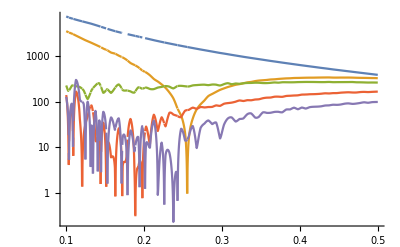

```mathematica
LogPlot[{Abs[Pr1datal0intz0[k]],Abs[Pr1datal2intz0[k]],Abs[Pr1datal4intz0[k]],Abs[Pr1datal6intz0[k]],Abs[Pr1datal8intz0[k]]},{k,0.1,0.5}]
```

## Sims Data z=0.56

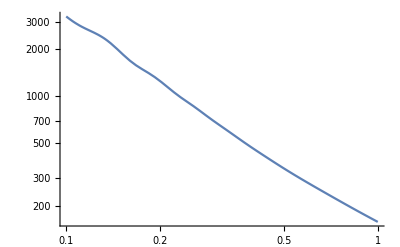

-Graphics-

```mathematica
PNLdatatabimpCoyote3=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/data_redshift/pknl_leonardo3.dat"];
PNLdatatabCoyote3=Table[{PNLdatatabimpCoyote3⟦i,1⟧,PNLdatatabimpCoyote3⟦i,2⟧},{i,1,Length[PNLdatatabimpCoyote3]}];
PNLdataintCoyote3=Interpolation[PNLdatatabCoyote3];
LogLogPlot[{PNLdataintCoyote3[k],PNLdataint[k]},{k,0.1,1}]
LogLogPlot[{PNLdataintCoyote3[k]/PNLdataint[k]},{k,0.1,1}]
```

```mathematica
PNLdatatabimp=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/data_redshift/PNL.Particles.0029.0050.CICassign.NGPbin.pk.dat"];
PNLdatatab=Table[{PNLdatatabimp⟦i,1⟧,PNLdatatabimp⟦i,2⟧},{i,1,Length[PNLdatatabimp]}];
NmodesdataNLtab=Table[{PNLdatatabimp⟦i,1⟧,PNLdatatabimp⟦i,3⟧},{i,1,Length[PNLdatatabimp]}];
PNLdataint=Interpolation[PNLdatatab];

ErrordataNLtab=Table[{PNLdatatab⟦i,1⟧,PNLdatatab⟦i,2⟧(((2/NmodesdataNLtab⟦i,2⟧)^(1/2)(1+1/(PNLdatatab⟦i,2⟧ 283105845/2500^3)))^2+0.01^2)^(1/2)},{i,1,Length[PNLdatatabimp]}];
CVdataNLtab=Table[{PNLdatatab⟦i,1⟧,PNLdatatab⟦i,2⟧(((2/NmodesdataNLtab⟦i,2⟧)^(1/2)(1+1/(PNLdatatab⟦i,2⟧ 283105845/2500^3)))^2)^(1/2)},{i,1,Length[PNLdatatabimp]}];

ErrordataNLint=Interpolation[ErrordataNLtab];
CVdataNLint=Interpolation[CVdataNLtab];
```

```mathematica
Pr1datatotl0tab1=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_108.dat.CICassign.mono.dat"];
Pr1datatotl2tab1=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_108.dat.CICassign.quad.dat"];
Pr1datatotl4tab1=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_108.dat.CICassign.four.dat"];
Pr1datatotl6tab1=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_108.dat.CICassign.six.dat"];
Pr1datatotl8tab1=Import[NotebookDirectory[]<>"redshift_real_universe/mathematics/sim_data_8_11_15/HMD_pk_z0_and_z5618/dm_particles_snap_108.dat.CICassign.oct.dat"];
```

```mathematica
Pr1datal0tab=Table[{Pr1datatotl0tab1⟦i,1⟧,Pr1datatotl0tab1⟦i,2⟧},{i,1,Length[Pr1datatotl0tab1]}];
Pr1datal2tab=Table[{Pr1datatotl2tab1⟦i,1⟧,Pr1datatotl2tab1⟦i,2⟧},{i,1,Length[Pr1datatotl2tab1]}];
Pr1datal4tab=Table[{Pr1datatotl4tab1⟦i,1⟧,Pr1datatotl4tab1⟦i,2⟧},{i,1,Length[Pr1datatotl4tab1]}];
Pr1datal6tab=Table[{Pr1datatotl6tab1⟦i,1⟧,Pr1datatotl6tab1⟦i,2⟧},{i,1,Length[Pr1datatotl6tab1]}];
Pr1datal8tab=Table[{Pr1datatotl8tab1⟦i,1⟧,Pr1datatotl8tab1⟦i,2⟧},{i,1,Length[Pr1datatotl8tab1]}];

Nmodesdatal0tab=Table[{Pr1datatotl0tab1⟦i,1⟧,Pr1datatotl0tab1⟦i,3⟧},{i,1,Length[Pr1datatotl0tab1]}];Nmodesdatal2tab=Table[{Pr1datatotl2tab1⟦i,1⟧,Pr1datatotl2tab1⟦i,3⟧},{i,1,Length[Pr1datatotl2tab1]}];
Nmodesdatal4tab=Table[{Pr1datatotl4tab1⟦i,1⟧,Pr1datatotl4tab1⟦i,3⟧},{i,1,Length[Pr1datatotl4tab1]}];
Nmodesdatal6tab=Table[{Pr1datatotl6tab1⟦i,1⟧,Pr1datatotl6tab1⟦i,3⟧},{i,1,Length[Pr1datatotl6tab1]}];
Nmodesdatal8tab=Table[{Pr1datatotl8tab1⟦i,1⟧,Pr1datatotl8tab1⟦i,3⟧},{i,1,Length[Pr1datatotl8tab1]}];

Errordatal0tab=Table[{Pr1datatotl0tab1⟦i,1⟧,Abs[Pr1datatotl0tab1⟦i,2⟧](Pr1datatotl0tab1⟦i,4⟧^2/Pr1datatotl0tab1⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl0tab1]}];
Errordatal2tab=Table[{Pr1datatotl2tab1⟦i,1⟧,Abs[Pr1datatotl2tab1⟦i,2⟧](Pr1datatotl2tab1⟦i,4⟧^2/Pr1datatotl2tab1⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl2tab1]}];
Errordatal4tab=Table[{Pr1datatotl4tab1⟦i,1⟧,Abs[Pr1datatotl4tab1⟦i,2⟧](Pr1datatotl4tab1⟦i,4⟧^2/Pr1datatotl4tab1⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl4tab1]}];
Errordatal6tab=Table[{Pr1datatotl6tab1⟦i,1⟧,Abs[Pr1datatotl6tab1⟦i,2⟧](Pr1datatotl6tab1⟦i,4⟧^2/Pr1datatotl6tab1⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl6tab1]}];
Errordatal8tab=Table[{Pr1datatotl8tab1⟦i,1⟧,Abs[Pr1datatotl8tab1⟦i,2⟧](Pr1datatotl8tab1⟦i,4⟧^2/Pr1datatotl8tab1⟦i,2⟧^2+0.02^2)^(1/2)},{i,1,Length[Pr1datatotl8tab1]}];

CVdatal0tab=Table[{Pr1datatotl0tab1⟦i,1⟧,Abs[Pr1datatotl0tab1⟦i,2⟧](Pr1datatotl0tab1⟦i,4⟧^2/Pr1datatotl0tab1⟦i,2⟧^2)^(1/2)},{i,1,Length[Pr1datatotl0tab1]}];
CVdatal2tab=Table[{Pr1datatotl2tab1⟦i,1⟧,Abs[Pr1datatotl2tab1⟦i,2⟧](Pr1datatotl2tab1⟦i,4⟧^2/Pr1datatotl2tab1⟦i,2⟧^2)^(1/2)},{i,1,Length[Pr1datatotl2tab1]}];
CVdatal4tab=Table[{Pr1datatotl4tab1⟦i,1⟧,Abs[Pr1datatotl4tab1⟦i,2⟧](Pr1datatotl4tab1⟦i,4⟧^2/Pr1datatotl4tab1⟦i,2⟧^2)^(1/2)},{i,1,Length[Pr1datatotl4tab1]}];
CVdatal6tab=Table[{Pr1datatotl6tab1⟦i,1⟧,Abs[Pr1datatotl6tab1⟦i,2⟧](Pr1datatotl6tab1⟦i,4⟧^2/Pr1datatotl6tab1⟦i,2⟧^2)^(1/2)},{i,1,Length[Pr1datatotl6tab1]}];
CVdatal8tab=Table[{Pr1datatotl8tab1⟦i,1⟧,Abs[Pr1datatotl8tab1⟦i,2⟧](Pr1datatotl8tab1⟦i,4⟧^2/Pr1datatotl8tab1⟦i,2⟧^2)^(1/2)},{i,1,Length[Pr1datatotl8tab1]}];
```

```mathematica
Pr1datal0int=Interpolation[Pr1datal0tab];
Pr1datal2int=Interpolation[Pr1datal2tab];
Pr1datal4int=Interpolation[Pr1datal4tab];
Pr1datal6int=Interpolation[Pr1datal6tab];
Pr1datal8int=Interpolation[Pr1datal8tab];

Nmodesdatal0int=Interpolation[Nmodesdatal0tab];
Nmodesdatal2int=Interpolation[Nmodesdatal2tab];
Nmodesdatal4int=Interpolation[Nmodesdatal4tab];
Nmodesdatal6int=Interpolation[Nmodesdatal6tab];
Nmodesdatal8int=Interpolation[Nmodesdatal8tab];

Errordatal0int=Interpolation[Errordatal0tab];
Errordatal2int=Interpolation[Errordatal2tab];
Errordatal4int=Interpolation[Errordatal4tab];
Errordatal6int=Interpolation[Errordatal6tab];
Errordatal8int=Interpolation[Errordatal8tab];

CVdatal0int=Interpolation[CVdatal0tab];
CVdatal2int=Interpolation[CVdatal2tab];
CVdatal4int=Interpolation[CVdatal4tab];
CVdatal6int=Interpolation[CVdatal6tab];
CVdatal8int=Interpolation[CVdatal8tab];
```

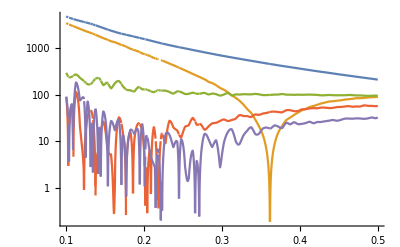

```mathematica
LogPlot[{Abs[Pr1datal0int[k]],Abs[Pr1datal2int[k]],Abs[Pr1datal4int[k]],Abs[Pr1datal6int[k]],Abs[Pr1datal8int[k]]},{k,0.1,0.5}]
```

```mathematica
Abs[Pr1datal2int[k]]/Abs[Pr1datal4int[k]]/.{k-> 0.2}
```

5.75897

## Fits a=1, z=0; and EFT functions defined

```mathematica
Clear[cs1,ca,cb]
PrEFT1loopRealSpinta0[k_,cs1_,c1_,c2_,c3_]=PSPT1loopTotRealSpint[1][k]+cs1 (P11csRealSP[k,1]/.{cs1->1});
PrEFT1loopl0inta0[k_,cs1_,c1_,c2_,c3_]=PrSPT1loopl0int[1][k]+cs1 Pcsl0int[1][k]+c1 Pc1l0int[1][k]+c2 Pc2l0int[1][k]+c3 Pc3l0int[1][k];
PrEFT1loopl2inta0[k_,cs1_,c1_,c2_,c3_]=PrSPT1loopl2int[1][k]+cs1 Pcsl2int[1][k]+c1 Pc1l2int[1][k]+c2 Pc2l2int[1][k]+c3 Pc3l2int[1][k];
PrEFT1loopl4inta0[k_,cs1_,c1_,c2_,c3_]=PrSPT1loopl4int[1][k]+cs1 Pcsl4int[1][k]+c1 Pc1l4int[1][k]+c2 Pc2l4int[1][k]+c3 Pc3l4int[1][k];
PrEFT1loopl6inta0[k_,cs1_,c1_,c2_,c3_]=PrSPT1loopl6int[1][k]+c1 Pc1l6int[1][k]+c2 Pc2l6int[1][k]+c3 Pc3l6int[1][k];
PrEFT1loopl8inta0[k_,cs1_,c1_,c2_,c3_]=PrSPT1loopl8int[1][k]+c1 Pc1l8int[1][k]+c2 Pc2l8int[1][k]+c3 Pc3l8int[1][k];
```

```mathematica
(*Manipulate[Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,c3])^-1,(PNLdataintCoyote0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,c3])^-1,1.02,0.98},{k,0.025,0.5},PlotRange->All,PlotLabel->"P_NL/real, z=0"],{{cs1,1.92},-2,4.5}]*)
```

```mathematica
Clear[ PrEFT1loopl0inta0, PrEFT1loopl2inta0, PrEFT1loopl4inta0 , PrEFT1loopl6inta0 ,PrEFT1loopl8inta0]
PrEFT1loopRealSpinta0[k_,cs1_,c1_,c2_, c3_]=PSPT1loopTotRealSpint[1][k]+ cs1 (P11csRealSP[k,1]/.{cs1->1});

PrEFT1loopl0inta0[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl0int[1][k]+cs1 Pcsl0int[1][k]+c1 Pc1l0int[1][k]+c2 Pc2l0int[1][k] + c12 Pc1l02loopint[1][k] + c22 Pc2l02loopint[1][k] + c1p Pc1pl02loopint[1][k] + c2p Pc2pl02loopint[1][k] + c3p Pc3pl02loopint[1][k] +cst  PrStoch[0][k] ;

PrEFT1loopl2inta0[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl2int[1][k]+ cs1 Pcsl2int[1][k]+c1 Pc1l2int[1][k]+c2 Pc2l2int[1][k] +  c12 Pc1l22loopint[1][k] + c22 Pc2l22loopint[1][k] + c1p Pc1pl22loopint[1][k] + c2p Pc2pl22loopint[1][k] + c3p Pc3pl22loopint[1][k]+cst  PrStoch[2][k];

PrEFT1loopl4inta0[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl4int[1][k]+cs1 Pcsl4int[1][k]+c1 Pc1l4int[1][k]+c2 Pc2l4int[1][k] + c12 Pc1l42loopint[1][k] + c22 Pc2l42loopint[1][k] + c1p Pc1pl42loopint[1][k] + c2p Pc2pl42loopint[1][k] + c3p Pc3pl42loopint[1][k]+cst  PrStoch[4][k];

PrEFT1loopl6inta0[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl6int[1][k]+c1 Pc1l6int[1][k]+c2 Pc2l6int[1][k] + c12 Pc1l62loopint[1][k] + c22 Pc2l62loopint[1][k] + c1p Pc1pl62loopint[1][k] + c2p Pc2pl62loopint[1][k] + c3p Pc3pl62loopint[1][k];

PrEFT1loopl8inta0[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl8int[1][k]+c1 Pc1l8int[1][k]+c2 Pc2l8int[1][k]+ c12 Pc1l82loopint[1][k] + c22 Pc2l82loopint[1][k] + c1p Pc1pl82loopint[1][k] + c2p Pc2pl82loopint[1][k] + c3p Pc3pl82loopint[1][k];
```

## Fits z=0.56; and EFT functions defined

```mathematica
Clear[ PrEFT1loopl0intap56, PrEFT1loopl2intap56, PrEFT1loopl4intap56 , PrEFT1loopl6intap56 ,PrEFT1loopl8intap56]
PrEFT1loopRealSpintap56[k_,cs1_,c1_,c2_, c3_]=PSPT1loopTotRealSpint[ap56][k]+ cs1 (P11csRealSP[k,ap56]/.{cs1->1});

PrEFT1loopl0intap56[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl0int[ap56][k]+cs1 Pcsl0int[ap56][k]+c1 Pc1l0int[ap56][k]+c2 Pc2l0int[ap56][k] + c12 Pc1l02loopint[ap56][k] + c22 Pc2l02loopint[ap56][k] + c1p Pc1pl02loopint[ap56][k] + c2p Pc2pl02loopint[ap56][k] + c3p Pc3pl02loopint[ap56][k] +cst  PrStoch[0][k] ;

PrEFT1loopl2intap56[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl2int[ap56][k]+ cs1 Pcsl2int[ap56][k]+c1 Pc1l2int[ap56][k]+c2 Pc2l2int[ap56][k] +  c12 Pc1l22loopint[ap56][k] + c22 Pc2l22loopint[ap56][k] + c1p Pc1pl22loopint[ap56][k] + c2p Pc2pl22loopint[ap56][k] + c3p Pc3pl22loopint[ap56][k]+cst  PrStoch[2][k];

PrEFT1loopl4intap56[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl4int[ap56][k]+cs1 Pcsl4int[ap56][k]+c1 Pc1l4int[ap56][k]+c2 Pc2l4int[ap56][k] + c12 Pc1l42loopint[ap56][k] + c22 Pc2l42loopint[ap56][k] + c1p Pc1pl42loopint[ap56][k] + c2p Pc2pl42loopint[ap56][k] + c3p Pc3pl42loopint[ap56][k]+cst  PrStoch[4][k];

PrEFT1loopl6intap56[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl6int[ap56][k]+c1 Pc1l6int[ap56][k]+c2 Pc2l6int[ap56][k] + c12 Pc1l62loopint[ap56][k] + c22 Pc2l62loopint[ap56][k] + c1p Pc1pl62loopint[ap56][k] + c2p Pc2pl62loopint[ap56][k] + c3p Pc3pl62loopint[ap56][k];

PrEFT1loopl8intap56[k_,cs1_,c1_,c2_,c12_,c22_ ,c1p_,c2p_,c3p_,cst_]=PrSPT1loopl8int[ap56][k]+c1 Pc1l8int[ap56][k]+c2 Pc2l8int[ap56][k]+ c12 Pc1l82loopint[ap56][k] + c22 Pc2l82loopint[ap56][k] + c1p Pc1pl82loopint[ap56][k] + c2p Pc2pl82loopint[ap56][k] + c3p Pc3pl82loopint[ap56][k];
```

```mathematica
(*Manipulate[Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,c1,c2, c3])^-1,((PNLdataint[k]+ErrordataNLint[k])/PrEFT1loopRealSpintap56[k,cs1,c1,c2, c3])^-1,((PNLdataint[k]-ErrordataNLint[k])/PrEFT1loopRealSpintap56[k,cs1,c1,c2, c3])^-1,1.02,0.98},{k,0.025,0.5},PlotRange->All,PlotLabel->"P_NL/real, z=0.56"],{{cs1,1.92},-2,4.5}]*)
```

```mathematica
credsoln = {c1-> -7.5 , c2 -> -12.9, c3->12};
```

# IR resummation

## setup for resummation

```mathematica
SetDirectory[NotebookDirectory[]<>"output"]
```

/Users/mattl/Documents/academics/research/COMPLETED_PROJECTS/redshift_ir_resum_MAIN/EFT_RSS_resum_pub/output

### Formulas and computations: X_1, Y_1

Formulas taken from Eqs. (96-97) from IR-resummation paper. Integrating kk from 0.0001 to 10 is fine (increasing the range doesn’t affect the results of the integrals). To construct interpolating functions for X and Y, I take linearly spaced points between 0.0001 and 10, and then logarithmically-spaced points from 10 to 10000. The computed points are exported to text files, or imported from text files if they’ve already been computed.

At different redshifts, assuming that Λ_resum is the same at each redshift, X and Y just get scaled by [D_1(z)]^2.

```mathematica
Clear[Λresum];Λresum=0.066;
```

```mathematica
Clear[X1Igr,Y1Igr]
X1Igr[qq_,kk_]=1/(2 π^2)Exp[-kk^2/Λresum^2]P11camb[kk](2/3-2 SphericalBesselJ[1,kk*qq]/(kk*qq));
Y1Igr[qq_,kk_]=1/(2 π^2)Exp[-kk^2/Λresum^2]P11camb[kk](-2SphericalBesselJ[0,kk*qq]+6 SphericalBesselJ[1,kk*qq]/(kk*qq));
```

```mathematica
Clear[X1IntTable1Z0,Y1IntTable1Z0,X1IntTable2Z0,Y1IntTable2Z0]
```

Computations and export commands (comment out these lines, and uncomment the import commands, after running this for the first time - this will produce 4 output files in the mma_output folder that can then be imported when the notebook is run again):

```mathematica
(*SetDirectory[NotebookDirectory[]<>"output"];
X1IntTable1Z0=Monitor[AbortableTable[{q,NIntegrate[X1Igr[q,k],{k,0.0001,1},PrecisionGoal-> 6,MaxRecursion->25]},{q,0.0001,10.2,0.5}],"X1 table 1, computing q = "<>ToString[q]];
Export["mma_output/X1IntTable1Z0_L0p066.dat",X1IntTable1Z0];
X1IntTable2Z0=Monitor[AbortableTable[{Exp[logq],NIntegrate[X1Igr[Exp[logq],k],{k,0.0001,1},PrecisionGoal-> 6,MaxRecursion->25]},{logq,2.33,9.4,0.03}],"X1 table 2, computing logq = "<>ToString[logq]];
Export["mma_output/X1IntTable2Z0_L0p066.dat",X1IntTable2Z0];
Y1IntTable1Z0=Monitor[AbortableTable[{q,NIntegrate[Y1Igr[q,k],{k,0.0001,1},PrecisionGoal-> 6,MaxRecursion->25]},{q,0.0001,10,0.5}],"Y1 table 1, computing q = "<>ToString[q]];
Export["mma_output/Y1IntTable1Z0_L0p066.dat",Y1IntTable1Z0];
Y1IntTable2Z0=Monitor[AbortableTable[{Exp[logq],NIntegrate[Y1Igr[Exp[logq],k],{k,0.0001,1},PrecisionGoal-> 6,MaxRecursion->25]},{logq,2.23,9.4,0.03}],"Y1 table 2, computing logq = "<>ToString[logq]];
Export["mma_output/Y1IntTable2Z0_L0p066.dat",Y1IntTable2Z0];*)
```

Import commands (see previous comment):

```mathematica
X1IntTable1Z0=Import["mma_output/X1IntTable1Z0_L0p066.dat"];
X1IntTable2Z0=Import["mma_output/X1IntTable2Z0_L0p066.dat"];
Y1IntTable1Z0=Import["mma_output/Y1IntTable1Z0_L0p066.dat"];
Y1IntTable2Z0=Import["mma_output/Y1IntTable2Z0_L0p066.dat"];
```

Some plots:

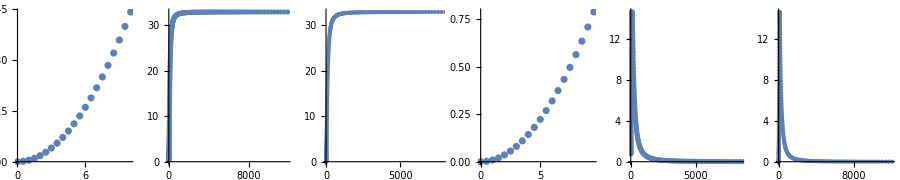

```mathematica
GraphicsRow[{ListPlot[X1IntTable1Z0],ListPlot[X1IntTable2Z0],ListPlot[Join[X1IntTable1Z0,X1IntTable2Z0]],ListPlot[Y1IntTable1Z0],ListPlot[Y1IntTable2Z0],ListPlot[Join[Y1IntTable1Z0,Y1IntTable2Z0],PlotRange->All]},ImageSize->900]
```

```mathematica
(*LogLogPlot[{X1[0][k],Y1[0][k]},{k,0.0001,10000}]*)
```

I precompute the time-dependent prefactors (“fac[z]”) because otherwise, evaluation of X1 and Y1 is way slower:

```mathematica
Clear[X1,Y1];
(*Table[{X1[z]=Interpolation[Map[{#[[1]],#[[2]]*fac[z]}&,Join[X1IntTable1Z0,X1IntTable2Z0]]],Y1[z]=Interpolation[Map[{#[[1]],#[[2]]*fac[z]}&,Join[Y1IntTable1Z0,Y1IntTable2Z0]]]},{z,Union[zsCoy,zs]}];*)
X1=Interpolation[Map[{#[[1]],#[[2]]}&,Join[X1IntTable1Z0,X1IntTable2Z0]]];
Y1=Interpolation[Map[{#[[1]],#[[2]]}&,Join[Y1IntTable1Z0,Y1IntTable2Z0]]];

X1ap56=Interpolation[Map[{#[[1]],Dgrowth[zz[ap56]]^2#[[2]]}&,Join[X1IntTable1Z0,X1IntTable2Z0]]];Y1ap56=Interpolation[Map[{#[[1]],Dgrowth[zz[ap56]]^2 #[[2]]}&,Join[Y1IntTable1Z0,Y1IntTable2Z0]]];

X1a1=Interpolation[Map[{#[[1]],Dgrowth[zz[a1]]^2#[[2]]}&,Join[X1IntTable1Z0,X1IntTable2Z0]]];Y1a1=Interpolation[Map[{#[[1]],Dgrowth[zz[a1]]^2 #[[2]]}&,Join[Y1IntTable1Z0,Y1IntTable2Z0]]];
```

### useful routines

```mathematica
Clear[MidpointIntegrate];MidpointIntegrate[table_]:=Module[{n},
Table[(table[[n]][[2]]+table[[n-1]][[2]])/2*(table[[n]][[1]]-table[[n-1]][[1]]),{n,2,Length[table]}]//Total
]
```

```mathematica
(* the routine below is used later to create a matrix of q's that will be used in the FFTLog*)
```

```mathematica
Clear[createqmatrix]
createqmatrix[dl_,qmin_,qmax_,tablename_]:= Module[{q0,nd,qmatrix,nt},
q0=qmin Exp[Log[qmax/qmin]/2];
nd=2 IntegerPart[Log[qmax/q0]/2 /dl];
qmatrix=Table[ q0 Exp[i dl],{i,-nd,nd-1}];
tablename = qmatrix;
nt=Dimensions[qmatrix][[1]];
]
```

### FFTLog and SBTLog Routine

```mathematica
U[μ_,x_]:=  2^x Gamma[(μ+1+x)/2]/Gamma[(μ+1-x)/2];
```

```mathematica
um[m_,μ_,q_,k0r0_,L_]:= Module[{z},z=2 π I m/L; k0r0^-z U[μ,q+z]]
```

```mathematica
FFTLog0[listin_,μ_,k0r0_,dl_,listout_,k0r0out_]:=Module[{fft1,umvec,Ndim,L,n,k0r0N},Ndim=Dimensions[listin][[1]];If[OddQ[Ndim],Print["Error, dimension of array should be Even"]; Abort[]];L=dl Ndim;n=Round[Log[k0r0]/dl-1/π Arg[U[1/2,π I/ dl]]];k0r0N=Exp[dl (1/π Arg[U[1/2,π I/dl ]]+ n)];umvec=Table[um[k,μ,0,k0r0N,L],{k,-Ndim/2,Ndim/2-1}];umvec[[1]]=Re[umvec[[1]]];fft1= RotateRight[ Fourier[RotateLeft[listin,Ndim/2], FourierParameters-> {-1,-1}],Ndim/2];listout=RotateRight[Fourier[RotateLeft[fft1 umvec,Ndim/2] , FourierParameters-> {1,-1}],Ndim/2];k0r0out=k0r0N]
```

[THIS IS THE FFT USED IN THIS NOTEBOOK]  the note below is for the SBT 
We want to be able to calculate ã(q)=∫_0^∞ a(k) j_l(q k)dk for some function a(k) at various q values. To do so, we feed the function a(k) to doSBTl ( which feeds a table of values of a(k)√(π /(2 k)) to FFTLog0 , and then multiplies the output table (which has been evaluated different q values) by q^(-1/2)q^-1 to obtain a table of ã(q).)  The output of doSBTl is ã(q).  For example, to compute ζ(q), you should input, a(k)=(k^2 P(k))/(2 π^2), then the output of doSBTl with l = 0 will be ã(q) = ζ(q).

```mathematica
Clear[CalcCorrFnEFT1AtQ,doSBTl]
doSBTl[l_,dl_,kmin_,kmax_,functionname_, tabout_, interpout_]:=Module[{k0,qvecForCorrFnAtQ,temptab, temptabout,nd,kmatrix,nt,tempcorrfnarr,tempk0r0out},
k0=kmin Exp[Log[kmax/kmin]/2];
nd=2 IntegerPart[Log[kmax/k0]/2 /dl];
kmatrix=Table[ k0 Exp[i dl],{i,-nd,nd-1}];
orange = kmatrix;
nt=Dimensions[kmatrix][[1]];
temptab[kmatrix_]:=ParallelMap[Re[functionname[#]*(#^-1*π/2)^(1/2)]&,kmatrix];
FFTLog0[temptab[kmatrix],l +1/2,1,dl,tempcorrfnarr,tempk0r0out];
qvecForCorrFnAtQ=Table[ tempk0r0out/k0 Exp[i dl],{i,-nd,nd-1}];
tabout = Table[ {qvecForCorrFnAtQ[[i]] ,(qvecForCorrFnAtQ[[i]])^(-1/2) (qvecForCorrFnAtQ[[i]])^-1  tempcorrfnarr[[i]]} , { i , 1 , Length[tempcorrfnarr]}];
interpout = Interpolation[tabout];
]
```

[this is the OLD FFT] the module below sets up the calc to use the FFT.  you should run doFFTl[l, dl_,kmin_,kmax_, inputtable_]  to generate the tables of the Fourier Transforms.  kmin and kmax are the minimum and maximum values of k included in the FFT, and dl is the spacing of k’s in log space. qvecForCorrFnAtQ is a table with the output values of q, and CorrFnAtQ is a table with the corresponding output values of ζ_l(q) q q^(1/2)

```mathematica
Clear[CalcCorrFnEFT1AtQ]
doFFT[dl_,kmin_,kmax_,tablename_]:=Module[{k0,nd,kmatrix,nt,tempcorrfnarr,tempk0r0out},
k0=kmin Exp[Log[kmax/kmin]/2];
nd=2 IntegerPart[Log[kmax/k0]/2 /dl];
kmatrix=Table[ k0 Exp[i dl],{i,-nd,nd-1}];
orange = kmatrix;
nt=Dimensions[kmatrix][[1]];
FFTLog0[tablename[kmatrix],1/2,1,dl,tempcorrfnarr,tempk0r0out];
CorrFnAtQ=tempcorrfnarr;
q0k0ForCorrFnAtQ=tempk0r0out;
qvecForCorrFnAtQ=Table[ q0k0ForCorrFnAtQ/k0 Exp[i dl],{i,-nd,nd-1}];
]

Clear[CalcCorrFnEFT1AtQ]
doFFTl[l_,dl_,kmin_,kmax_,tablename_]:=Module[{k0,nd,kmatrix,nt,tempcorrfnarr,tempk0r0out},
k0=kmin Exp[Log[kmax/kmin]/2];
nd=2 IntegerPart[Log[kmax/k0]/2 /dl];
kmatrix=Table[ k0 Exp[i dl],{i,-nd,nd-1}];
orange = kmatrix;
nt=Dimensions[kmatrix][[1]];
FFTLog0[tablename[kmatrix],l +1/2,1,dl,tempcorrfnarr,tempk0r0out];
CorrFnAtQ=tempcorrfnarr;
q0k0ForCorrFnAtQ=tempk0r0out;
qvecForCorrFnAtQ=Table[ q0k0ForCorrFnAtQ/k0 Exp[i dl],{i,-nd,nd-1}];
]
```

the note below is for the standard FFTLog

We want to be able to calculate ã(q)=∫_0^∞ a(k) sin(q k)dk for some function a(k) at various q values. To do so, we feed a table of values of a(k)√(π k/2) to FFTLog0, and then multiply the output table (which has been evaluated different q values) by q^(-1/2) to obtain a table of ã(q).

For us, a(k)=(k P(k))/(q 2 π^2) . So, we feed a table of (k P(k))/(2 π^2) √(πk/2) (we’ll restore the 1/qlater, don’t want it in the numerical integrals now) to the FFT routine, and then multiply the results by q^-1 (to restore the q we multiplied by) and q^(-1/2) (to account for the normalization of the FFT routine's output).

the note below is for the SBT

We want to be able to calculate ã(q)=∫_0^∞ a(k) j_l(q k)dk for some function a(k) at various q values. To do so, we feed a table of values of a(k)√(π /(2 k)) to FFTLog0, and then multiply the output table (which has been evaluated different q values) by q^(-1/2)q^-1 to obtain a table of ã(q).

For us, a(k)=(k^2 P(k))/(2 π^2) . So, we feed a table of (k^2 P(k))/(2 π^2) √(π/(2 k))  to the FFT routine,  and multiply the result by q^(-1/2)q^-1 (to account for the normalization of the FFT routine's output).

the note below is for the SBT test
We want to be able to calculate ã(q)=∫_0^∞ a(k) j_l(q k)dk for some function a(k) at various q values. To do so, we feed the function a(k) to doSBTl ( which feeds a table of values of a(k)√(π /(2 k)) to FFTLog0 , and then multiplies the output table (which has been evaluated different q values) by q^(-1/2)q^-1 to obtain a table of ã(q).)  The output of doSBTl is already ã(q)
For us, a(k)=(k^2 P(k))/(2 π^2)

### saved Iint - orderTaylor = 3, a = 0,...,8 for Y^4

```mathematica
(*Table[ { a  , l , lpr , Iint[a][l][lpr][k,q] } , { a , 0,8}, {l,{0,2}} , {lpr,-4,12}]*)
```

```mathematica
(*savedtab6 = {{{{0,0,-4,0},{0,0,-3,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,0,-2,0},{0,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2+1/3 ff (2+ff) k^2 X1temp (-1+3 β)+1/60 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+1/840 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+21 β-35 β^2+35 β^3)+(ff^4 (2+ff)^4 k^8 X1temp^4 (35+3 β (-60+7 β (18+5 β (-4+3 β)))))/60480+(ff^5 (2+ff)^5 k^10 X1temp^5 (-63+11 β (35+3 β (-30+7 β (6+β (-5+3 β))))))/1330560)},{0,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2+1/3 ff (2+ff) k^2 X1temp (-1+3 β)+1/60 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+1/840 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+21 β-35 β^2+35 β^3)+(ff^4 (2+ff)^4 k^8 X1temp^4 (35+3 β (-60+7 β (18+5 β (-4+3 β)))))/60480+(ff^5 (2+ff)^5 k^10 X1temp^5 (-63+11 β (35+3 β (-30+7 β (6+β (-5+3 β))))))/1330560)},{0,0,1,0},{0,0,2,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,0,3,0},{0,0,4,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (6864+ff (2+ff) k^2 X1temp (312 (-5+11 β)+ff (2+ff) k^2 X1temp (210-21 ff (2+ff) k^2 X1temp+15 (-52+7 ff (2+ff) k^2 X1temp) β-39 (-22+5 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{0,0,5,0},{0,0,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2040+ff (2+ff) k^2 X1temp (68 (7-15 β)+ff (2+ff) k^2 X1temp (-63+17 (14-15 β) β))))/9189180},{0,0,7,0},{0,0,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (38+ff (2+ff) k^2 X1temp (-9+19 β)))/6235515},{0,0,9,0},{0,0,10,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/14549535},{0,0,11,0},{0,0,12,0}},{{0,2,-4,0},{0,2,-3,1/86486400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34594560+1647360 ff k^2 X1temp (-11+21 β)+10 ff^9 k^10 X1temp^5 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)+ff^10 k^10 X1temp^5 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)+823680 ff^2 k^2 X1temp (-11+21 β+k^2 X1temp (9-22 β+21 β^2))+24960 ff^3 k^4 X1temp^2 (33 (9-22 β+21 β^2)+k^2 X1temp (-85+297 β-363 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (9-22 β+21 β^2)+234 k^2 X1temp (-85+297 β-363 β^2+231 β^3)+k^4 X1temp^2 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4))+80 ff^7 k^8 X1temp^4 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4+k^2 X1temp (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+10 ff^8 k^8 X1temp^4 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4+4 k^2 X1temp (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+80 ff^6 k^6 X1temp^3 (39 (-85+297 β-363 β^2+231 β^3)+3 k^2 X1temp (2905-13260 β+23166 β^2-18876 β^3+9009 β^4)+k^4 X1temp^2 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+32 ff^5 k^6 X1temp^3 (585 (-85+297 β-363 β^2+231 β^3)+10 k^2 X1temp (2905-13260 β+23166 β^2-18876 β^3+9009 β^4)+k^4 X1temp^2 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)))},{0,2,-2,0},{0,2,-1,-1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (1153152+164736 ff k^2 X1temp (-3+7 β)+8 ff^7 k^8 X1temp^4 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)+ff^8 k^8 X1temp^4 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)+27456 ff^2 k^2 X1temp (-9+21 β+k^2 X1temp (5-18 β+21 β^2))+832 ff^3 k^4 X1temp^2 (33 (5-18 β+21 β^2)+k^2 X1temp (-35+165 β-297 β^2+231 β^3))+16 ff^5 k^6 X1temp^3 (39 (-35+165 β-297 β^2+231 β^3)+2 k^2 X1temp (315-1820 β+4290 β^2-5148 β^3+3003 β^4))+8 ff^6 k^6 X1temp^3 (13 (-35+165 β-297 β^2+231 β^3)+3 k^2 X1temp (315-1820 β+4290 β^2-5148 β^3+3003 β^4))+16 ff^4 k^4 X1temp^2 (429 (5-18 β+21 β^2)+78 k^2 X1temp (-35+165 β-297 β^2+231 β^3)+k^4 X1temp^2 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)))},{0,2,0,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,2,1,0},{0,2,2,1/86486400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34594560+ff k^2 X1temp (1647360 (-11+21 β)+ff (823680 (-11+21 β)+205920 (2+ff)^2 k^2 X1temp (9+β (-22+21 β))+3120 ff (2+ff)^3 k^4 X1temp^2 (-85+33 β (9+β (-11+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (2905+39 β (-340+11 β (54+β (-44+21 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-2583+β (14525+39 β (-850+11 β (90+β (-55+21 β))))))))},{0,2,3,0},{0,2,4,1/73513440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2800512+ff (2+ff) k^2 X1temp (-42432 (-17+33 β)+ff (2+ff) k^2 X1temp (15 (-7888+7 ff (2+ff) k^2 X1temp (136-13 ff (2+ff) k^2 X1temp))+204 (1768+5 ff (2+ff) k^2 X1temp (-58+7 ff (2+ff) k^2 X1temp)) β-102 (3432+ff (2+ff) k^2 X1temp (-884+145 ff (2+ff) k^2 X1temp)) β^2+884 ff (2+ff) k^2 X1temp (-66+17 ff (2+ff) k^2 X1temp) β^3-7293 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{0,2,5,0},{0,2,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (697680+ff (2+ff) k^2 X1temp (7752 (-23+45 β)+ff (2+ff) k^2 X1temp (26866-2961 ff (2+ff) k^2 X1temp+19 (-4692+707 ff (2+ff) k^2 X1temp) β-969 (-90+23 ff (2+ff) k^2 X1temp) β^2+14535 ff (2+ff) k^2 X1temp β^3)))},{0,2,7,0},{0,2,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-3192+ff (2+ff) k^2 X1temp (812-1596 β+ff (2+ff) k^2 X1temp (-117+7 (58-57 β) β))))/43648605},{0,2,9,0},{0,2,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (138+ff (2+ff) k^2 X1temp (-35+69 β)))/66927861},{0,2,11,0},{0,2,12,-(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/84504875}}},{{{1,0,-4,-1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (494208+54912 ff k^2 X1temp (-5+9 β)+8 ff^7 k^8 X1temp^4 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)+ff^8 k^8 X1temp^4 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)+2496 ff^2 k^2 X1temp (-55+99 β+k^2 X1temp (35-110 β+99 β^2))+192 ff^3 k^4 X1temp^2 (13 (35-110 β+99 β^2)+k^2 X1temp (-105+455 β-715 β^2+429 β^3))+24 ff^6 k^6 X1temp^3 (-105+455 β-715 β^2+429 β^3+k^2 X1temp (231-1260 β+2730 β^2-2860 β^3+1287 β^4))+16 ff^5 k^6 X1temp^3 (9 (-105+455 β-715 β^2+429 β^3)+2 k^2 X1temp (231-1260 β+2730 β^2-2860 β^3+1287 β^4))+16 ff^4 k^4 X1temp^2 (39 (35-110 β+99 β^2)+18 k^2 X1temp (-105+455 β-715 β^2+429 β^3)+k^4 X1temp^2 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)))},{1,0,-3,0},{1,0,-2,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+2306304 ff k^2 X1temp (-3+5 β)+10 ff^9 k^10 X1temp^5 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)+164736 ff^2 k^2 X1temp (7 (-3+5 β)+k^2 X1temp (15-42 β+35 β^2))+18304 ff^3 k^4 X1temp^2 (9 (15-42 β+35 β^2)+k^2 X1temp (-35+135 β-189 β^2+105 β^3))+416 ff^4 k^4 X1temp^2 (99 (15-42 β+35 β^2)+66 k^2 X1temp (-35+135 β-189 β^2+105 β^3)+k^4 X1temp^2 (315-1540 β+2970 β^2-2772 β^3+1155 β^4))+16 ff^7 k^8 X1temp^4 (13 (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+5 k^2 X1temp (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+2 ff^8 k^8 X1temp^4 (13 (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+20 k^2 X1temp (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (429 (-35+135 β-189 β^2+105 β^3)+26 k^2 X1temp (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+k^4 X1temp^2 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+16 ff^6 k^6 X1temp^3 (143 (-35+135 β-189 β^2+105 β^3)+39 k^2 X1temp (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+5 k^4 X1temp^2 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)))},{1,0,-1,0},{1,0,0,0},{1,0,1,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (2306304 (-3+5 β)+ff (1153152 (-3+5 β)+41184 (2+ff)^2 k^2 X1temp (15+7 β (-6+5 β))+2288 ff (2+ff)^3 k^4 X1temp^2 (-35+3 β (45+7 β (-9+5 β)))+26 ff^2 (2+ff)^4 k^6 X1temp^3 (315+11 β (-140+3 β (90+7 β (-12+5 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-693+13 β (315+11 β (-70+3 β (30+7 (-3+β) β)))))))},{1,0,2,0},{1,0,3,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-494208+ff (2+ff) k^2 X1temp (-27456 (-5+9 β)+ff (2+ff) k^2 X1temp (-21840+21 ff (2+ff) k^2 X1temp (120-11 ff (2+ff) k^2 X1temp)+60 (1144+7 ff (2+ff) k^2 X1temp (-26+3 ff (2+ff) k^2 X1temp)) β-78 (792+5 ff (2+ff) k^2 X1temp (-44+7 ff (2+ff) k^2 X1temp)) β^2+572 ff (2+ff) k^2 X1temp (-18+5 ff (2+ff) k^2 X1temp) β^3-1287 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{1,0,4,0},{1,0,5,1/18378360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (53040+ff (2+ff) k^2 X1temp (2040 (-7+13 β)+ff (2+ff) k^2 X1temp (2142-231 ff (2+ff) k^2 X1temp+357 (-20+3 ff (2+ff) k^2 X1temp) β-255 (-26+7 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{1,0,6,0},{1,0,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2584+ff (2+ff) k^2 X1temp (76 (9-17 β)+ff (2+ff) k^2 X1temp (-99+19 (18-17 β) β))))/24942060},{1,0,8,0},{1,0,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (42+ff (2+ff) k^2 X1temp (-11+21 β)))/14549535},{1,0,10,0},{1,0,11,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/30421755},{1,0,12,0}},{{1,2,-4,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (252046080+28005120 ff k^2 X1temp (-7+9 β)+10 ff^9 k^10 X1temp^5 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)+ff^10 k^10 X1temp^5 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)+424320 ff^2 k^2 X1temp (33 (-7+9 β)+k^2 X1temp (205-462 β+297 β^2))+32640 ff^3 k^4 X1temp^2 (13 (205-462 β+297 β^2)+k^2 X1temp (-805+2665 β-3003 β^2+1287 β^3))+8160 ff^4 k^4 X1temp^2 (13 (205-462 β+297 β^2)+6 k^2 X1temp (-805+2665 β-3003 β^2+1287 β^3)+k^4 X1temp^2 (735-3220 β+5330 β^2-4004 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (51 (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^2 X1temp (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+10 ff^8 k^8 X1temp^4 (51 (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+4 k^2 X1temp (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+80 ff^6 k^6 X1temp^3 (51 (-805+2665 β-3003 β^2+1287 β^3)+153 k^2 X1temp (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^4 X1temp^2 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+32 ff^5 k^6 X1temp^3 (765 (-805+2665 β-3003 β^2+1287 β^3)+510 k^2 X1temp (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^4 X1temp^2 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)))},{1,2,-3,0},{1,2,-2,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{1,2,-1,0},{1,2,0,0},{1,2,1,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{1,2,2,0},{1,2,3,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (252046080+ff k^2 X1temp (28005120 (-7+9 β)+ff (14002560 (-7+9 β)+106080 (2+ff)^2 k^2 X1temp (205+33 β (-14+9 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-805+13 β (205+33 β (-7+3 β)))+510 ff^2 (2+ff)^4 k^6 X1temp^3 (735+β (-3220+13 β (410+11 β (-28+9 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-34419+17 β (11025+β (-24150+13 β (2050+33 β (-35+9 β))))))))},{1,2,4,0},{1,2,5,-1/1396755360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (24186240+620160 ff k^2 X1temp (-25+39 β)+8 ff^7 k^8 X1temp^4 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)+ff^8 k^8 X1temp^4 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)+62016 ff^2 k^2 X1temp (5 (-25+39 β)+k^2 X1temp (91-250 β+195 β^2))+3648 ff^3 k^4 X1temp^2 (17 (91-250 β+195 β^2)+k^2 X1temp (-399+1547 β-2125 β^2+1105 β^3))+24 ff^6 k^6 X1temp^3 (19 (-399+1547 β-2125 β^2+1105 β^3)+k^2 X1temp (18249-90972 β+176358 β^2-161500 β^3+62985 β^4))+16 ff^5 k^6 X1temp^3 (171 (-399+1547 β-2125 β^2+1105 β^3)+2 k^2 X1temp (18249-90972 β+176358 β^2-161500 β^3+62985 β^4))+16 ff^4 k^4 X1temp^2 (969 (91-250 β+195 β^2)+342 k^2 X1temp (-399+1547 β-2125 β^2+1105 β^3)+k^4 X1temp^2 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)))},{1,2,6,0},{1,2,7,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (325584+ff (2+ff) k^2 X1temp (1064 (-91+153 β)+ff (2+ff) k^2 X1temp (16002-1881 ff (2+ff) k^2 X1temp+7 (-6916+1143 ff (2+ff) k^2 X1temp) β-133 (-306+91 ff (2+ff) k^2 X1temp) β^2+6783 ff (2+ff) k^2 X1temp β^3)))},{1,2,8,0},{1,2,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-11592+ff (2+ff) k^2 X1temp (-828 (-4+7 β)+ff (2+ff) k^2 X1temp (-517-207 β (-8+7 β)))))/334639305},{1,2,10,0},{1,2,11,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (750+ff (2+ff) k^2 X1temp (-209+375 β)))/760543875},{1,2,12,0}}},{{{2,0,-4,0},{2,0,-3,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{2,0,-2,0},{2,0,-1,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-693 ff^5 (2+ff)^5 k^10 X1temp^5+4095 ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β)-10010 ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β))+12870 ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β)))-9009 ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β))))+3003 (3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β))))))},{2,0,0,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (2306304 (-3+5 β)+ff (1153152 (-3+5 β)+41184 (2+ff)^2 k^2 X1temp (15+7 β (-6+5 β))+2288 ff (2+ff)^3 k^4 X1temp^2 (-35+3 β (45+7 β (-9+5 β)))+26 ff^2 (2+ff)^4 k^6 X1temp^3 (315+11 β (-140+3 β (90+7 β (-12+5 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-693+13 β (315+11 β (-70+3 β (30+7 (-3+β) β)))))))},{2,0,1,0},{2,0,2,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{2,0,3,0},{2,0,4,1/36756720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-933504+ff (2+ff) k^2 X1temp (-21216 (-15+22 β)+ff (2+ff) k^2 X1temp (-57120+21 ff (2+ff) k^2 X1temp (340-33 ff (2+ff) k^2 X1temp)+510 (312+7 ff (2+ff) k^2 X1temp (-8+ff (2+ff) k^2 X1temp)) β-204 (572+5 ff (2+ff) k^2 X1temp (-39+7 ff (2+ff) k^2 X1temp)) β^2+442 ff (2+ff) k^2 X1temp (-44+15 ff (2+ff) k^2 X1temp) β^3-2431 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{2,0,5,0},{2,0,6,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (232560+ff (2+ff) k^2 X1temp (2584 (-28+45 β)+ff (2+ff) k^2 X1temp (126 (95-11 ff (2+ff) k^2 X1temp)+133 (-272+45 ff (2+ff) k^2 X1temp) β-646 (-45+14 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{2,0,7,0},{2,0,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2128+ff (2+ff) k^2 X1temp (630-1064 β+ff (2+ff) k^2 X1temp (-99+7 (45-38 β) β))))/43648605},{2,0,9,0},{2,0,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (230+ff (2+ff) k^2 X1temp (-66+115 β)))/334639305},{2,0,11,0},{2,0,12,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/253514625}},{{2,2,-4,0},{2,2,-3,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (308056320+28005120 ff k^2 X1temp (-9+11 β)+10 ff^9 k^10 X1temp^5 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)+ff^10 k^10 X1temp^5 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)+1272960 ff^2 k^2 X1temp (-99+121 β+k^2 X1temp (85-198 β+121 β^2))+10880 ff^3 k^4 X1temp^2 (117 (85-198 β+121 β^2)+k^2 X1temp (-2905+9945 β-11583 β^2+4719 β^3))+2720 ff^4 k^4 X1temp^2 (117 (85-198 β+121 β^2)+6 k^2 X1temp (-2905+9945 β-11583 β^2+4719 β^3)+k^4 X1temp^2 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4))+80 ff^7 k^8 X1temp^4 (17 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^2 X1temp (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+10 ff^8 k^8 X1temp^4 (17 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+4 k^2 X1temp (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+80 ff^6 k^6 X1temp^3 (17 (-2905+9945 β-11583 β^2+4719 β^3)+51 k^2 X1temp (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^4 X1temp^2 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+32 ff^5 k^6 X1temp^3 (255 (-2905+9945 β-11583 β^2+4719 β^3)+170 k^2 X1temp (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^4 X1temp^2 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)))},{2,2,-2,0},{2,2,-1,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{2,2,0,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{2,2,1,0},{2,2,2,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (308056320+ff k^2 X1temp (28005120 (-9+11 β)+ff (14002560 (-9+11 β)+318240 (2+ff)^2 k^2 X1temp (85+11 β (-18+11 β))+1360 ff (2+ff)^3 k^4 X1temp^2 (-2905+39 β (255+11 β (-27+11 β)))+170 ff^2 (2+ff)^4 k^6 X1temp^3 (2583+β (-11620+39 β (510+11 β (-36+11 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-39501+17 β (12915+β (-29050+39 β (850+11 β (-45+11 β))))))))},{2,2,3,0},{2,2,4,1/6983776800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-34+33 β)+10 ff^9 k^10 X1temp^5 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-442+429 β+k^2 X1temp (435-884 β+429 β^2))+620160 ff^3 k^4 X1temp^2 (435-884 β+429 β^2+k^2 X1temp (-140+435 β-442 β^2+143 β^3))+3040 ff^4 k^4 X1temp^2 (51 (435-884 β+429 β^2)+306 k^2 X1temp (-140+435 β-442 β^2+143 β^3)+k^4 X1temp^2 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4))+80 ff^7 k^8 X1temp^4 (19 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^2 X1temp (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+10 ff^8 k^8 X1temp^4 (19 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+4 k^2 X1temp (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+80 ff^6 k^6 X1temp^3 (969 (-140+435 β-442 β^2+143 β^3)+57 k^2 X1temp (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^4 X1temp^2 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-140+435 β-442 β^2+143 β^3)+190 k^2 X1temp (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^4 X1temp^2 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)))},{2,2,5,0},{2,2,6,1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5581440+ff (2+ff) k^2 X1temp (-93024 (-23+30 β)+ff (2+ff) k^2 X1temp (7 (-61408+9 ff (2+ff) k^2 X1temp (940-99 ff (2+ff) k^2 X1temp))+2 (534888+7 ff (2+ff) k^2 X1temp (-15352+2115 ff (2+ff) k^2 X1temp)) β-76 (9180+ff (2+ff) k^2 X1temp (-3519+707 ff (2+ff) k^2 X1temp)) β^2+1938 ff (2+ff) k^2 X1temp (-60+23 ff (2+ff) k^2 X1temp) β^3-14535 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{2,2,7,0},{2,2,8,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (440496+ff (2+ff) k^2 X1temp (1288 (-116+171 β)+ff (2+ff) k^2 X1temp (26910-3366 ff (2+ff) k^2 X1temp+23 (-3248+585 ff (2+ff) k^2 X1temp) β-322 (-171+58 ff (2+ff) k^2 X1temp) β^2+9177 ff (2+ff) k^2 X1temp β^3)))},{2,2,9,0},{2,2,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-138000+ff (2+ff) k^2 X1temp (43750-69000 β+ff (2+ff) k^2 X1temp (-7359+125 (175-138 β) β))))/8365982625},{2,2,11,0},{2,2,12,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (270+ff (2+ff) k^2 X1temp (-82+135 β)))/2281631625}}},{{{3,0,-4,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (84015360+9335040 ff k^2 X1temp (-10+9 β)+10 ff^9 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+ff^10 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+424320 ff^2 k^2 X1temp (-110+99 β+k^2 X1temp (105-220 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (13 (105-220 β+99 β^2)+k^2 X1temp (-420+1365 β-1430 β^2+429 β^3))+2720 ff^4 k^4 X1temp^2 (39 (105-220 β+99 β^2)+18 k^2 X1temp (-420+1365 β-1430 β^2+429 β^3)+k^4 X1temp^2 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+10 ff^8 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+4 k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+80 ff^6 k^6 X1temp^3 (51 (-420+1365 β-1430 β^2+429 β^3)+51 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+32 ff^5 k^6 X1temp^3 (765 (-420+1365 β-1430 β^2+429 β^3)+170 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)))},{3,0,-3,0},{3,0,-2,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/28800+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/4992-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2112+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/1728-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/2688+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/9600)},{3,0,-1,0},{3,0,0,0},{3,0,1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2/5+1/86486400 ff (2+ff) k^2 X1temp (2471040 (-5+7 β)+ff (2+ff) k^2 X1temp (21 ff (2+ff) k^2 X1temp (-15600+11 ff (2+ff) k^2 X1temp (150-13 ff (2+ff) k^2 X1temp))+525 ff (2+ff) k^2 X1temp (2288+3 ff (2+ff) k^2 X1temp (-104+11 ff (2+ff) k^2 X1temp)) β-390 (-11088+5 ff (2+ff) k^2 X1temp (792+7 ff (2+ff) k^2 X1temp (-22+3 ff (2+ff) k^2 X1temp))) β^2+1430 ff (2+ff) k^2 X1temp (504+5 ff (2+ff) k^2 X1temp (-36+7 ff (2+ff) k^2 X1temp)) β^3-6435 ff^2 (2+ff)^2 k^4 X1temp^2 (-14+5 ff (2+ff) k^2 X1temp) β^4+9009 ff^3 (2+ff)^3 k^6 X1temp^3 β^5-343200 (-7+18 β))))},{3,0,2,0},{3,0,3,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (84015360+9335040 ff k^2 X1temp (-10+9 β)+10 ff^9 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+ff^10 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+424320 ff^2 k^2 X1temp (-110+99 β+k^2 X1temp (105-220 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (13 (105-220 β+99 β^2)+k^2 X1temp (-420+1365 β-1430 β^2+429 β^3))+2720 ff^4 k^4 X1temp^2 (39 (105-220 β+99 β^2)+18 k^2 X1temp (-420+1365 β-1430 β^2+429 β^3)+k^4 X1temp^2 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+10 ff^8 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+4 k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+80 ff^6 k^6 X1temp^3 (51 (-420+1365 β-1430 β^2+429 β^3)+51 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+32 ff^5 k^6 X1temp^3 (765 (-420+1365 β-1430 β^2+429 β^3)+170 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)))},{3,0,4,0},{3,0,5,-1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (8062080+310080 ff k^2 X1temp (-21+26 β)+8 ff^7 k^8 X1temp^4 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)+ff^8 k^8 X1temp^4 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)+31008 ff^2 k^2 X1temp (5 (-21+26 β)+2 k^2 X1temp (42-105 β+65 β^2))+608 ff^3 k^4 X1temp^2 (102 (42-105 β+65 β^2)+k^2 X1temp (-1155+4284 β-5355 β^2+2210 β^3))+8 ff^5 k^6 X1temp^3 (57 (-1155+4284 β-5355 β^2+2210 β^3)+4 k^2 X1temp (9009-43890 β+81396 β^2-67830 β^3+20995 β^4))+4 ff^6 k^6 X1temp^3 (19 (-1155+4284 β-5355 β^2+2210 β^3)+6 k^2 X1temp (9009-43890 β+81396 β^2-67830 β^3+20995 β^4))+16 ff^4 k^4 X1temp^2 (969 (42-105 β+65 β^2)+57 k^2 X1temp (-1155+4284 β-5355 β^2+2210 β^3)+k^4 X1temp^2 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)))},{3,0,6,0},{3,0,7,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (108528+ff (2+ff) k^2 X1temp (3192 (-12+17 β)+ff (2+ff) k^2 X1temp (6930-858 ff (2+ff) k^2 X1temp+63 (-304+55 ff (2+ff) k^2 X1temp) β-798 (-17+6 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{3,0,8,0},{3,0,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-7728+ff (2+ff) k^2 X1temp (46 (55-84 β)+ff (2+ff) k^2 X1temp (-429+23 (55-42 β) β))))/334639305},{3,0,10,0},{3,0,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (250+ff (2+ff) k^2 X1temp (-78+125 β)))/760543875},{3,0,12,0}},{{3,2,-4,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3724680960+16124160 ff k^2 X1temp (-205+231 β)+10 ff^9 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+ff^10 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+620160 ff^2 k^2 X1temp (-2665+3003 β+k^2 X1temp (2415-5330 β+3003 β^2))+620160 ff^3 k^4 X1temp^2 (2415-5330 β+3003 β^2+k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3))+3040 ff^4 k^4 X1temp^2 (51 (2415-5330 β+3003 β^2)+306 k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3)+k^4 X1temp^2 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4))+80 ff^7 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+10 ff^8 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+4 k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+80 ff^6 k^6 X1temp^3 (969 (-735+2415 β-2665 β^2+1001 β^3)+57 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-735+2415 β-2665 β^2+1001 β^3)+190 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)))},{3,2,-3,0},{3,2,-2,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{3,2,-1,0},{3,2,0,0},{3,2,1,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{3,2,2,0},{3,2,3,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3724680960+16124160 ff k^2 X1temp (-205+231 β)+10 ff^9 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+ff^10 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+620160 ff^2 k^2 X1temp (-2665+3003 β+k^2 X1temp (2415-5330 β+3003 β^2))+620160 ff^3 k^4 X1temp^2 (2415-5330 β+3003 β^2+k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3))+3040 ff^4 k^4 X1temp^2 (51 (2415-5330 β+3003 β^2)+306 k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3)+k^4 X1temp^2 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4))+80 ff^7 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+10 ff^8 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+4 k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+80 ff^6 k^6 X1temp^3 (969 (-735+2415 β-2665 β^2+1001 β^3)+57 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-735+2415 β-2665 β^2+1001 β^3)+190 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)))},{3,2,4,0},{3,2,5,1/1396755360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48372480+1240320 ff k^2 X1temp (-50+39 β)+10 ff^9 k^10 X1temp^5 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)+ff^10 k^10 X1temp^5 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)+124032 ff^2 k^2 X1temp (5 (-50+39 β)+k^2 X1temp (273-500 β+195 β^2))+7296 ff^3 k^4 X1temp^2 (17 (273-500 β+195 β^2)+k^2 X1temp (-1596+4641 β-4250 β^2+1105 β^3))+32 ff^4 k^4 X1temp^2 (969 (273-500 β+195 β^2)+342 k^2 X1temp (-1596+4641 β-4250 β^2+1105 β^3)+k^4 X1temp^2 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4))+16 ff^7 k^8 X1temp^4 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4+5 k^2 X1temp (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+2 ff^8 k^8 X1temp^4 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4+20 k^2 X1temp (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+32 ff^5 k^6 X1temp^3 (171 (-1596+4641 β-4250 β^2+1105 β^3)+2 k^2 X1temp (91245-363888 β+529074 β^2-323000 β^3+62985 β^4)+k^4 X1temp^2 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+16 ff^6 k^6 X1temp^3 (57 (-1596+4641 β-4250 β^2+1105 β^3)+3 k^2 X1temp (91245-363888 β+529074 β^2-323000 β^3+62985 β^4)+5 k^4 X1temp^2 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)))},{3,2,6,0},{3,2,7,-1/16062686640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (59907456+587328 ff k^2 X1temp (-91+102 β)+8 ff^7 k^8 X1temp^4 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)+ff^8 k^8 X1temp^4 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)+15456 ff^2 k^2 X1temp (19 (-91+102 β)+2 k^2 X1temp (762-1729 β+969 β^2))+2208 ff^3 k^4 X1temp^2 (14 (762-1729 β+969 β^2)+k^2 X1temp (-3135+10668 β-12103 β^2+4522 β^3))+12 ff^6 k^6 X1temp^3 (23 (-3135+10668 β-12103 β^2+4522 β^3)+2 k^2 X1temp (95667-432630 β+736092 β^2-556738 β^3+156009 β^4))+8 ff^5 k^6 X1temp^3 (207 (-3135+10668 β-12103 β^2+4522 β^3)+4 k^2 X1temp (95667-432630 β+736092 β^2-556738 β^3+156009 β^4))+16 ff^4 k^4 X1temp^2 (483 (762-1729 β+969 β^2)+207 k^2 X1temp (-3135+10668 β-12103 β^2+4522 β^3)+k^4 X1temp^2 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)))},{3,2,8,0},{3,2,9,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (347760+ff (2+ff) k^2 X1temp (8280 (-16+21 β)+ff (2+ff) k^2 X1temp (25850-3432 ff (2+ff) k^2 X1temp+5 (-13248+2585 ff (2+ff) k^2 X1temp) β-2070 (-21+8 ff (2+ff) k^2 X1temp) β^2+7245 ff (2+ff) k^2 X1temp β^3)))},{3,2,10,0},{3,2,11,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-6000+ff (2+ff) k^2 X1temp (2090-3000 β+ff (2+ff) k^2 X1temp (-377+5 (209-150 β) β))))/760543875},{3,2,12,0}}},{{{4,0,-4,0},{4,0,-3,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{4,0,-2,0},{4,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/28800+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/4992-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2112+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/1728-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/2688+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/9600)},{4,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2/5+1/86486400 ff (2+ff) k^2 X1temp (2471040 (-5+7 β)+ff (2+ff) k^2 X1temp (21 ff (2+ff) k^2 X1temp (-15600+11 ff (2+ff) k^2 X1temp (150-13 ff (2+ff) k^2 X1temp))+525 ff (2+ff) k^2 X1temp (2288+3 ff (2+ff) k^2 X1temp (-104+11 ff (2+ff) k^2 X1temp)) β-390 (-11088+5 ff (2+ff) k^2 X1temp (792+7 ff (2+ff) k^2 X1temp (-22+3 ff (2+ff) k^2 X1temp))) β^2+1430 ff (2+ff) k^2 X1temp (504+5 ff (2+ff) k^2 X1temp (-36+7 ff (2+ff) k^2 X1temp)) β^3-6435 ff^2 (2+ff)^2 k^4 X1temp^2 (-14+5 ff (2+ff) k^2 X1temp) β^4+9009 ff^3 (2+ff)^3 k^6 X1temp^3 β^5-343200 (-7+18 β))))},{4,0,1,0},{4,0,2,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{4,0,3,0},{4,0,4,1/3491888400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (177365760+16124160 ff k^2 X1temp (-15+11 β)+10 ff^9 k^10 X1temp^5 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)+ff^10 k^10 X1temp^5 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)+620160 ff^2 k^2 X1temp (-195+143 β+k^2 X1temp (210-390 β+143 β^2))+206720 ff^3 k^4 X1temp^2 (630-1170 β+429 β^2+k^2 X1temp (-210+630 β-585 β^2+143 β^3))+3040 ff^4 k^4 X1temp^2 (51 (210-390 β+143 β^2)+102 k^2 X1temp (-210+630 β-585 β^2+143 β^3)+k^4 X1temp^2 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4))+80 ff^7 k^8 X1temp^4 (19 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^2 X1temp (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+10 ff^8 k^8 X1temp^4 (19 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+4 k^2 X1temp (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+80 ff^6 k^6 X1temp^3 (323 (-210+630 β-585 β^2+143 β^3)+57 k^2 X1temp (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^4 X1temp^2 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+32 ff^5 k^6 X1temp^3 (4845 (-210+630 β-585 β^2+143 β^3)+190 k^2 X1temp (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^4 X1temp^2 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)))},{4,0,5,0},{4,0,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1860480+ff (2+ff) k^2 X1temp (-62016 (-14+15 β)+ff (2+ff) k^2 X1temp (21 (-9120+11 ff (2+ff) k^2 X1temp (120-13 ff (2+ff) k^2 X1temp))+84 (5168+15 ff (2+ff) k^2 X1temp (-76+11 ff (2+ff) k^2 X1temp)) β-228 (1020+7 ff (2+ff) k^2 X1temp (-68+15 ff (2+ff) k^2 X1temp)) β^2+2584 ff (2+ff) k^2 X1temp (-15+7 ff (2+ff) k^2 X1temp) β^3-4845 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{4,0,7,0},{4,0,8,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (293664+ff (2+ff) k^2 X1temp (7728 (-15+19 β)+ff (2+ff) k^2 X1temp (33 (690-91 ff (2+ff) k^2 X1temp)+1035 (-56+11 ff (2+ff) k^2 X1temp) β-966 (-38+15 ff (2+ff) k^2 X1temp) β^2+6118 ff (2+ff) k^2 X1temp β^3)))},{4,0,9,0},{4,0,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-46000+ff (2+ff) k^2 X1temp (-500 (-33+46 β)+ff (2+ff) k^2 X1temp (-3003+250 (33-23 β) β))))/8365982625},{4,0,11,0},{4,0,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (270+ff (2+ff) k^2 X1temp (-91+135 β)))/6844894875}},{{4,2,-4,0},{4,2,-3,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4788875520+48372480 ff k^2 X1temp (-85+99 β)+10 ff^9 k^10 X1temp^5 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)+ff^10 k^10 X1temp^5 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)+620160 ff^2 k^2 X1temp (39 (-85+99 β)+k^2 X1temp (2905-6630 β+3861 β^2))+620160 ff^3 k^4 X1temp^2 (2905-6630 β+3861 β^2+k^2 X1temp (-861+2905 β-3315 β^2+1287 β^3))+9120 ff^4 k^4 X1temp^2 (17 (2905-6630 β+3861 β^2)+102 k^2 X1temp (-861+2905 β-3315 β^2+1287 β^3)+k^4 X1temp^2 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4))+80 ff^7 k^8 X1temp^4 (57 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^2 X1temp (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+10 ff^8 k^8 X1temp^4 (57 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+4 k^2 X1temp (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+80 ff^6 k^6 X1temp^3 (969 (-861+2905 β-3315 β^2+1287 β^3)+171 k^2 X1temp (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^4 X1temp^2 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-861+2905 β-3315 β^2+1287 β^3)+570 k^2 X1temp (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^4 X1temp^2 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)))},{4,2,-2,0},{4,2,-1,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{4,2,0,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{4,2,1,0},{4,2,2,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4788875520+ff k^2 X1temp (48372480 (-85+99 β)+ff (24186240 (-85+99 β)+155040 (2+ff)^2 k^2 X1temp (2905+39 β (-170+99 β))+77520 ff (2+ff)^3 k^4 X1temp^2 (-861+β (2905+39 β (-85+33 β)))+570 ff^2 (2+ff)^4 k^6 X1temp^3 (13167+17 β (-3444+β (5810+13 β (-340+99 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-681681+19 β (197505+17 β (-25830+β (29050+39 β (-425+99 β))))))))},{4,2,3,0},{4,2,4,1/6983776800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (548221440+1240320 ff k^2 X1temp (-435+442 β)+10 ff^9 k^10 X1temp^5 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)+ff^10 k^10 X1temp^5 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)+620160 ff^2 k^2 X1temp (-435+442 β+2 k^2 X1temp (210-435 β+221 β^2))+12160 ff^3 k^4 X1temp^2 (102 (210-435 β+221 β^2)+k^2 X1temp (-6825+21420 β-22185 β^2+7514 β^3))+320 ff^4 k^4 X1temp^2 (969 (210-435 β+221 β^2)+57 k^2 X1temp (-6825+21420 β-22185 β^2+7514 β^3)+k^4 X1temp^2 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4))+80 ff^7 k^8 X1temp^4 (2 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^2 X1temp (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+20 ff^8 k^8 X1temp^4 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4+2 k^2 X1temp (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+80 ff^6 k^6 X1temp^3 (19 (-6825+21420 β-22185 β^2+7514 β^3)+6 k^2 X1temp (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^4 X1temp^2 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+32 ff^5 k^6 X1temp^3 (285 (-6825+21420 β-22185 β^2+7514 β^3)+20 k^2 X1temp (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^4 X1temp^2 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)))},{4,2,5,0},{4,2,6,1/16062686640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (256746240+17116416 ff k^2 X1temp (-23+15 β)+10 ff^9 k^10 X1temp^5 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)+ff^10 k^10 X1temp^5 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)+167808 ff^2 k^2 X1temp (51 (-23+15 β)+k^2 X1temp (1414-2346 β+765 β^2))+8832 ff^3 k^4 X1temp^2 (19 (1414-2346 β+765 β^2)+k^2 X1temp (-9870+26866 β-22287 β^2+4845 β^3))+2208 ff^4 k^4 X1temp^2 (19 (1414-2346 β+765 β^2)+6 k^2 X1temp (-9870+26866 β-22287 β^2+4845 β^3)+k^4 X1temp^2 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4))+16 ff^7 k^8 X1temp^4 (69 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+5 k^2 X1temp (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+2 ff^8 k^8 X1temp^4 (69 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+20 k^2 X1temp (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+32 ff^5 k^6 X1temp^3 (207 (-9870+26866 β-22287 β^2+4845 β^3)+138 k^2 X1temp (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+k^4 X1temp^2 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+16 ff^6 k^6 X1temp^3 (69 (-9870+26866 β-22287 β^2+4845 β^3)+207 k^2 X1temp (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+5 k^4 X1temp^2 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)))},{4,2,7,0},{4,2,8,1/10039179150 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-17619840+ff (2+ff) k^2 X1temp (-154560 (-58+57 β)+ff (2+ff) k^2 X1temp (-2152800+33 ff (2+ff) k^2 X1temp (10200-1183 ff (2+ff) k^2 X1temp)+60 (74704+15 ff (2+ff) k^2 X1temp (-1196+187 ff (2+ff) k^2 X1temp)) β-1380 (1596+ff (2+ff) k^2 X1temp (-812+195 ff (2+ff) k^2 X1temp)) β^2+6440 ff (2+ff) k^2 X1temp (-57+29 ff (2+ff) k^2 X1temp) β^3-45885 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{4,2,9,0},{4,2,10,1/25097947875 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (2484000+ff (2+ff) k^2 X1temp (6000 (-175+207 β)+ff (2+ff) k^2 X1temp (220770-31031 ff (2+ff) k^2 X1temp+15 (-35000+7359 ff (2+ff) k^2 X1temp) β-750 (-414+175 ff (2+ff) k^2 X1temp) β^2+51750 ff (2+ff) k^2 X1temp β^3)))},{4,2,11,0},{4,2,12,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-187920+ff (2+ff) k^2 X1temp (1740 (41-54 β)+ff (2+ff) k^2 X1temp (-13741-870 β (-41+27 β)))))/198501951375}}},{{{5,0,-4,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (354731520+16124160 ff k^2 X1temp (-21+22 β)+10 ff^9 k^10 X1temp^5 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)+ff^10 k^10 X1temp^5 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)+620160 ff^2 k^2 X1temp (-273+286 β+2 k^2 X1temp (126-273 β+143 β^2))+206720 ff^3 k^4 X1temp^2 (756-1638 β+858 β^2+k^2 X1temp (-231+756 β-819 β^2+286 β^3))+1216 ff^4 k^4 X1temp^2 (255 (126-273 β+143 β^2)+255 k^2 X1temp (-231+756 β-819 β^2+286 β^3)+k^4 X1temp^2 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4))+16 ff^7 k^8 X1temp^4 (38 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+5 k^2 X1temp (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+4 ff^8 k^8 X1temp^4 (19 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+10 k^2 X1temp (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+32 ff^5 k^6 X1temp^3 (4845 (-231+756 β-819 β^2+286 β^3)+76 k^2 X1temp (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+k^4 X1temp^2 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+16 ff^6 k^6 X1temp^3 (1615 (-231+756 β-819 β^2+286 β^3)+114 k^2 X1temp (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+5 k^4 X1temp^2 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)))},{5,0,-3,0},{5,0,-2,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{5,0,-1,0},{5,0,0,0},{5,0,1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{5,0,2,0},{5,0,3,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (354731520+ff k^2 X1temp (16124160 (-21+22 β)+ff (8062080 (-21+22 β)+310080 (2+ff)^2 k^2 X1temp (126+13 β (-21+11 β))+25840 ff (2+ff)^3 k^4 X1temp^2 (-231+β (756+13 β (-63+22 β)))+76 ff^2 (2+ff)^4 k^6 X1temp^3 (9009+85 β (-462+β (756+13 β (-42+11 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-63063+19 β (18018+17 β (-2310+β (2520+13 β (-105+22 β))))))))},{5,0,4,0},{5,0,5,1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16124160+1240320 ff k^2 X1temp (-21+13 β)+10 ff^9 k^10 X1temp^5 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)+ff^10 k^10 X1temp^5 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)+124032 ff^2 k^2 X1temp (-105+65 β+k^2 X1temp (126-210 β+65 β^2))+2432 ff^3 k^4 X1temp^2 (51 (126-210 β+65 β^2)+k^2 X1temp (-2310+6426 β-5355 β^2+1105 β^3))+32 ff^4 k^4 X1temp^2 (969 (126-210 β+65 β^2)+114 k^2 X1temp (-2310+6426 β-5355 β^2+1105 β^3)+k^4 X1temp^2 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4))+16 ff^7 k^8 X1temp^4 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4+5 k^2 X1temp (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+2 ff^8 k^8 X1temp^4 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4+20 k^2 X1temp (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+32 ff^5 k^6 X1temp^3 (57 (-2310+6426 β-5355 β^2+1105 β^3)+2 k^2 X1temp (45045-175560 β+244188 β^2-135660 β^3+20995 β^4)+k^4 X1temp^2 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+16 ff^6 k^6 X1temp^3 (19 (-2310+6426 β-5355 β^2+1105 β^3)+3 k^2 X1temp (45045-175560 β+244188 β^2-135660 β^3+20995 β^4)+5 k^4 X1temp^2 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)))},{5,0,6,0},{5,0,7,-1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (19969152+1174656 ff k^2 X1temp (-18+17 β)+8 ff^7 k^8 X1temp^4 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)+ff^8 k^8 X1temp^4 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)+30912 ff^2 k^2 X1temp (-342+323 β+k^2 X1temp (330-684 β+323 β^2))+1472 ff^3 k^4 X1temp^2 (21 (330-684 β+323 β^2)+k^2 X1temp (-2145+6930 β-7182 β^2+2261 β^3))+16 ff^5 k^6 X1temp^3 (69 (-2145+6930 β-7182 β^2+2261 β^3)+2 k^2 X1temp (45045-197340 β+318780 β^2-220248 β^3+52003 β^4))+8 ff^6 k^6 X1temp^3 (23 (-2145+6930 β-7182 β^2+2261 β^3)+3 k^2 X1temp (45045-197340 β+318780 β^2-220248 β^3+52003 β^4))+16 ff^4 k^4 X1temp^2 (483 (330-684 β+323 β^2)+138 k^2 X1temp (-2145+6930 β-7182 β^2+2261 β^3)+k^4 X1temp^2 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)))},{5,0,8,0},{5,0,9,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (231840+ff (2+ff) k^2 X1temp (1840 (-55+63 β)+ff (2+ff) k^2 X1temp (429 (50-7 ff (2+ff) k^2 X1temp)+275 (-184+39 ff (2+ff) k^2 X1temp) β-230 (-126+55 ff (2+ff) k^2 X1temp) β^2+4830 ff (2+ff) k^2 X1temp β^3)))},{5,0,10,0},{5,0,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-1200+ff (2+ff) k^2 X1temp (468-600 β+ff (2+ff) k^2 X1temp (-91+6 (39-25 β) β))))/456326325},{5,0,12,0}},{{5,2,-4,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (661090560+1240320 ff k^2 X1temp (-483+533 β)+10 ff^9 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+ff^10 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+620160 ff^2 k^2 X1temp (-483+533 β+k^2 X1temp (441-966 β+533 β^2))+2432 ff^3 k^4 X1temp^2 (255 (441-966 β+533 β^2)+k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3))+32 ff^4 k^4 X1temp^2 (4845 (441-966 β+533 β^2)+114 k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3)+k^4 X1temp^2 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4))+16 ff^7 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+5 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+2 ff^8 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+20 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+32 ff^5 k^6 X1temp^3 (57 (-34419+112455 β-123165 β^2+45305 β^3)+2 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+16 ff^6 k^6 X1temp^3 (19 (-34419+112455 β-123165 β^2+45305 β^3)+3 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+5 k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)))},{5,2,-3,0},{5,2,-2,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{5,2,-1,0},{5,2,0,0},{5,2,1,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{5,2,2,0},{5,2,3,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (661090560+1240320 ff k^2 X1temp (-483+533 β)+10 ff^9 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+ff^10 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+620160 ff^2 k^2 X1temp (-483+533 β+k^2 X1temp (441-966 β+533 β^2))+2432 ff^3 k^4 X1temp^2 (255 (441-966 β+533 β^2)+k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3))+32 ff^4 k^4 X1temp^2 (4845 (441-966 β+533 β^2)+114 k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3)+k^4 X1temp^2 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4))+16 ff^7 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+5 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+2 ff^8 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+20 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+32 ff^5 k^6 X1temp^3 (57 (-34419+112455 β-123165 β^2+45305 β^3)+2 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+16 ff^6 k^6 X1temp^3 (19 (-34419+112455 β-123165 β^2+45305 β^3)+3 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+5 k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)))},{5,2,4,0},{5,2,5,1/32125373280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1426368000+5705472 ff k^2 X1temp (-273+250 β)+10 ff^9 k^10 X1temp^5 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)+ff^10 k^10 X1temp^5 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)+167808 ff^2 k^2 X1temp (-4641+4250 β+2 k^2 X1temp (2394-4641 β+2125 β^2))+2944 ff^3 k^4 X1temp^2 (114 (2394-4641 β+2125 β^2)+k^2 X1temp (-91245+272916 β-264537 β^2+80750 β^3))+1472 ff^4 k^4 X1temp^2 (57 (2394-4641 β+2125 β^2)+3 k^2 X1temp (-91245+272916 β-264537 β^2+80750 β^3)+k^4 X1temp^2 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4))+16 ff^7 k^8 X1temp^4 (46 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+5 k^2 X1temp (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+4 ff^8 k^8 X1temp^4 (23 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+10 k^2 X1temp (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+32 ff^5 k^6 X1temp^3 (69 (-91245+272916 β-264537 β^2+80750 β^3)+92 k^2 X1temp (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+k^4 X1temp^2 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+16 ff^6 k^6 X1temp^3 (23 (-91245+272916 β-264537 β^2+80750 β^3)+138 k^2 X1temp (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+5 k^4 X1temp^2 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)))},{5,2,6,0},{5,2,7,1/401567166000 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2995372800+58732800 ff k^2 X1temp (-91+51 β)+10 ff^9 k^10 X1temp^5 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)+ff^10 k^10 X1temp^5 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)+1545600 ff^2 k^2 X1temp (19 (-91+51 β)+k^2 X1temp (2286-3458 β+969 β^2))+220800 ff^3 k^4 X1temp^2 (7 (2286-3458 β+969 β^2)+k^2 X1temp (-6270+16002 β-12103 β^2+2261 β^3))+800 ff^4 k^4 X1temp^2 (483 (2286-3458 β+969 β^2)+414 k^2 X1temp (-6270+16002 β-12103 β^2+2261 β^3)+k^4 X1temp^2 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4))+80 ff^7 k^8 X1temp^4 (5 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^2 X1temp (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+10 ff^8 k^8 X1temp^4 (5 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+4 k^2 X1temp (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+80 ff^6 k^6 X1temp^3 (345 (-6270+16002 β-12103 β^2+2261 β^3)+15 k^2 X1temp (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^4 X1temp^2 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+32 ff^5 k^6 X1temp^3 (5175 (-6270+16002 β-12103 β^2+2261 β^3)+50 k^2 X1temp (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^4 X1temp^2 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)))},{5,2,8,0},{5,2,9,1/2007835830 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1669248+ff (2+ff) k^2 X1temp (-119232 (-8+7 β)+ff (2+ff) k^2 X1temp (-248160+143 ff (2+ff) k^2 X1temp (288-35 ff (2+ff) k^2 X1temp)+48 (9936+11 ff (2+ff) k^2 X1temp (-235+39 ff (2+ff) k^2 X1temp)) β-12 (17388+ff (2+ff) k^2 X1temp (-9936+2585 ff (2+ff) k^2 X1temp)) β^2+4968 ff (2+ff) k^2 X1temp (-7+4 ff (2+ff) k^2 X1temp) β^3-4347 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{5,2,10,0},{5,2,11,1/13233463425 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (626400+ff (2+ff) k^2 X1temp (1392 (-209+225 β)+ff (2+ff) k^2 X1temp (65598-9737 ff (2+ff) k^2 X1temp+87 (-1672+377 ff (2+ff) k^2 X1temp) β-174 (-450+209 ff (2+ff) k^2 X1temp) β^2+13050 ff (2+ff) k^2 X1temp β^3)))},{5,2,12,0}}},{{{6,0,-4,0},{6,0,-3,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{6,0,-2,0},{6,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{6,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{6,0,1,0},{6,0,2,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{6,0,3,0},{6,0,4,1/232792560 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16124160+1240320 ff k^2 X1temp (-14+13 β)+10 ff^9 k^10 X1temp^5 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)+ff^10 k^10 X1temp^5 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)+620160 ff^2 k^2 X1temp (-14+13 β+k^2 X1temp (14-28 β+13 β^2))+12160 ff^3 k^4 X1temp^2 (51 (14-28 β+13 β^2)+k^2 X1temp (-231+714 β-714 β^2+221 β^3))+32 ff^4 k^4 X1temp^2 (4845 (14-28 β+13 β^2)+570 k^2 X1temp (-231+714 β-714 β^2+221 β^3)+k^4 X1temp^2 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4))+16 ff^7 k^8 X1temp^4 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4+5 k^2 X1temp (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+2 ff^8 k^8 X1temp^4 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4+20 k^2 X1temp (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+32 ff^5 k^6 X1temp^3 (285 (-231+714 β-714 β^2+221 β^3)+2 k^2 X1temp (21021-87780 β+135660 β^2-90440 β^3+20995 β^4)+k^4 X1temp^2 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+16 ff^6 k^6 X1temp^3 (95 (-231+714 β-714 β^2+221 β^3)+3 k^2 X1temp (21021-87780 β+135660 β^2-90440 β^3+20995 β^4)+5 k^4 X1temp^2 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)))},{6,0,5,0},{6,0,6,1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (85582080+5705472 ff k^2 X1temp (-28+15 β)+10 ff^9 k^10 X1temp^5 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)+ff^10 k^10 X1temp^5 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)+167808 ff^2 k^2 X1temp (-476+255 β+k^2 X1temp (630-952 β+255 β^2))+8832 ff^3 k^4 X1temp^2 (19 (630-952 β+255 β^2)+k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3))+736 ff^4 k^4 X1temp^2 (57 (630-952 β+255 β^2)+18 k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3)+k^4 X1temp^2 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4))+16 ff^7 k^8 X1temp^4 (23 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+5 k^2 X1temp (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+2 ff^8 k^8 X1temp^4 (23 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+20 k^2 X1temp (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+32 ff^5 k^6 X1temp^3 (207 (-4620+11970 β-9044 β^2+1615 β^3)+46 k^2 X1temp (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+k^4 X1temp^2 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+16 ff^6 k^6 X1temp^3 (69 (-4620+11970 β-9044 β^2+1615 β^3)+69 k^2 X1temp (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+5 k^4 X1temp^2 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)))},{6,0,7,0},{6,0,8,-1/5019589575 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (5873280+154560 ff k^2 X1temp (-45+38 β)+8 ff^7 k^8 X1temp^4 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)+ff^8 k^8 X1temp^4 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)+11040 ff^2 k^2 X1temp (7 (-45+38 β)+2 k^2 X1temp (165-315 β+133 β^2))+80 ff^3 k^4 X1temp^2 (276 (165-315 β+133 β^2)+k^2 X1temp (-15015+45540 β-43470 β^2+12236 β^3))+4 ff^5 k^6 X1temp^3 (15 (-15015+45540 β-43470 β^2+12236 β^3)+8 k^2 X1temp (18018-75075 β+113850 β^2-72450 β^3+15295 β^4))+2 ff^6 k^6 X1temp^3 (5 (-15015+45540 β-43470 β^2+12236 β^3)+12 k^2 X1temp (18018-75075 β+113850 β^2-72450 β^3+15295 β^4))+8 ff^4 k^4 X1temp^2 (690 (165-315 β+133 β^2)+15 k^2 X1temp (-15015+45540 β-43470 β^2+12236 β^3)+2 k^4 X1temp^2 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)))},{6,0,9,0},{6,0,10,1/15058768725 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (496800+ff (2+ff) k^2 X1temp (10800 (-22+23 β)+ff (2+ff) k^2 X1temp (2002 (27-4 ff (2+ff) k^2 X1temp)+297 (-400+91 ff (2+ff) k^2 X1temp) β-2700 (-23+11 ff (2+ff) k^2 X1temp) β^2+10350 ff (2+ff) k^2 X1temp β^3)))},{6,0,11,0},{6,0,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-12528+ff (2+ff) k^2 X1temp (5278-6264 β+ff (2+ff) k^2 X1temp (-1092+29 (91-54 β) β))))/39700390275}},{{6,2,-4,0},{6,2,-3,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (822332160+1240320 ff k^2 X1temp (-581+663 β)+10 ff^9 k^10 X1temp^5 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)+ff^10 k^10 X1temp^5 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)+124032 ff^2 k^2 X1temp (5 (-581+663 β)+k^2 X1temp (2583-5810 β+3315 β^2))+7296 ff^3 k^4 X1temp^2 (17 (2583-5810 β+3315 β^2)+k^2 X1temp (-13167+43911 β-49385 β^2+18785 β^3))+32 ff^4 k^4 X1temp^2 (969 (2583-5810 β+3315 β^2)+342 k^2 X1temp (-13167+43911 β-49385 β^2+18785 β^3)+k^4 X1temp^2 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4))+16 ff^7 k^8 X1temp^4 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4+5 k^2 X1temp (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+2 ff^8 k^8 X1temp^4 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4+20 k^2 X1temp (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+32 ff^5 k^6 X1temp^3 (171 (-13167+43911 β-49385 β^2+18785 β^3)+2 k^2 X1temp (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4)+k^4 X1temp^2 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+16 ff^6 k^6 X1temp^3 (57 (-13167+43911 β-49385 β^2+18785 β^3)+3 k^2 X1temp (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4)+5 k^4 X1temp^2 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)))},{6,2,-2,0},{6,2,-1,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{6,2,0,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{6,2,1,0},{6,2,2,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (822332160+ff k^2 X1temp (1240320 (-581+663 β)+ff (620160 (-581+663 β)+31008 (2+ff)^2 k^2 X1temp (2583+5 β (-1162+663 β))+912 ff (2+ff)^3 k^4 X1temp^2 (-13167+17 β (2583+5 β (-581+221 β)))+2 ff^2 (2+ff)^4 k^6 X1temp^3 (681681+19 β (-158004+17 β (15498+5 β (-2324+663 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-124839+β (681681+19 β (-79002+17 β (5166+β (-2905+663 β))))))))},{6,2,3,0},{6,2,4,1/10708457760 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (827293440+28527360 ff k^2 X1temp (-28+29 β)+10 ff^9 k^10 X1temp^5 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)+ff^10 k^10 X1temp^5 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)+839040 ff^2 k^2 X1temp (-476+493 β+k^2 X1temp (455-952 β+493 β^2))+2944 ff^3 k^4 X1temp^2 (285 (455-952 β+493 β^2)+k^2 X1temp (-41118+129675 β-135660 β^2+46835 β^3))+736 ff^4 k^4 X1temp^2 (285 (455-952 β+493 β^2)+6 k^2 X1temp (-41118+129675 β-135660 β^2+46835 β^3)+k^4 X1temp^2 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4))+16 ff^7 k^8 X1temp^4 (23 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+5 k^2 X1temp (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+2 ff^8 k^8 X1temp^4 (23 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+20 k^2 X1temp (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+32 ff^5 k^6 X1temp^3 (69 (-41118+129675 β-135660 β^2+46835 β^3)+46 k^2 X1temp (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+k^4 X1temp^2 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+16 ff^6 k^6 X1temp^3 (23 (-41118+129675 β-135660 β^2+46835 β^3)+69 k^2 X1temp (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+5 k^4 X1temp^2 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)))},{6,2,5,0},{6,2,6,1/401567166000 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9841939200+8390400 ff k^2 X1temp (-1414+1173 β)+10 ff^9 k^10 X1temp^5 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)+ff^10 k^10 X1temp^5 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)+220800 ff^2 k^2 X1temp (-26866+22287 β+k^2 X1temp (29610-53732 β+22287 β^2))+220800 ff^3 k^4 X1temp^2 (29610-53732 β+22287 β^2+k^2 X1temp (-10395+29610 β-26866 β^2+7429 β^3))+800 ff^4 k^4 X1temp^2 (69 (29610-53732 β+22287 β^2)+414 k^2 X1temp (-10395+29610 β-26866 β^2+7429 β^3)+k^4 X1temp^2 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4))+80 ff^7 k^8 X1temp^4 (5 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^2 X1temp (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+10 ff^8 k^8 X1temp^4 (5 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+4 k^2 X1temp (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+80 ff^6 k^6 X1temp^3 (345 (-10395+29610 β-26866 β^2+7429 β^3)+15 k^2 X1temp (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^4 X1temp^2 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+32 ff^5 k^6 X1temp^3 (5175 (-10395+29610 β-26866 β^2+7429 β^3)+50 k^2 X1temp (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^4 X1temp^2 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)))},{6,2,7,0},{6,2,8,1/50195895750 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (176198400+3091200 ff k^2 X1temp (-116+57 β)+10 ff^9 k^10 X1temp^5 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)+ff^10 k^10 X1temp^5 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)+220800 ff^2 k^2 X1temp (-812+399 β+k^2 X1temp (1170-1624 β+399 β^2))+9600 ff^3 k^4 X1temp^2 (23 (1170-1624 β+399 β^2)+k^2 X1temp (-11220+26910 β-18676 β^2+3059 β^3))+800 ff^4 k^4 X1temp^2 (69 (1170-1624 β+399 β^2)+18 k^2 X1temp (-11220+26910 β-18676 β^2+3059 β^3)+k^4 X1temp^2 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4))+80 ff^7 k^8 X1temp^4 (5 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^2 X1temp (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+10 ff^8 k^8 X1temp^4 (5 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+4 k^2 X1temp (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+80 ff^6 k^6 X1temp^3 (15 (-11220+26910 β-18676 β^2+3059 β^3)+15 k^2 X1temp (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^4 X1temp^2 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+32 ff^5 k^6 X1temp^3 (225 (-11220+26910 β-18676 β^2+3059 β^3)+50 k^2 X1temp (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^4 X1temp^2 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)))},{6,2,9,0},{6,2,10,1/436704293025 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-172886400+ff (2+ff) k^2 X1temp (-626400 (-175+138 β)+ff (2+ff) k^2 X1temp (-30731184+2002 ff (2+ff) k^2 X1temp (2697-343 ff (2+ff) k^2 X1temp)+87 (630000+11 ff (2+ff) k^2 X1temp (-16056+2821 ff (2+ff) k^2 X1temp)) β-1566 (13800+ff (2+ff) k^2 X1temp (-8750+2453 ff (2+ff) k^2 X1temp)) β^2+13050 ff (2+ff) k^2 X1temp (-276+175 ff (2+ff) k^2 X1temp) β^3-450225 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{6,2,11,0},{6,2,12,1/1230712098525 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (6990624+ff (2+ff) k^2 X1temp (43152 (-82+81 β)+ff (2+ff) k^2 X1temp (182 (4681-732 ff (2+ff) k^2 X1temp)+31 (-57072+13741 ff (2+ff) k^2 X1temp) β-10788 (-81+41 ff (2+ff) k^2 X1temp) β^2+145638 ff (2+ff) k^2 X1temp β^3)))}}},{{{7,0,-4,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/11+1/36465 8 ff (2+ff) k^2 X1temp (2040 (-12+13 β)+ff (2+ff) k^2 X1temp (510 (-1+β) (-11+13 β)+2 ff k^2 X1temp (-858+85 β (33+β (-36+13 β)))+ff^2 k^2 X1temp (-858+85 β (33+β (-36+13 β))))))},{7,0,-3,0},{7,0,-2,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{7,0,-1,0},{7,0,0,0},{7,0,1,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{7,0,2,0},{7,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/11+1/36465 8 ff (2+ff) k^2 X1temp (2040 (-12+13 β)+ff (2+ff) k^2 X1temp (510 (-1+β) (-11+13 β)+2 ff k^2 X1temp (-858+85 β (33+β (-36+13 β)))+ff^2 k^2 X1temp (-858+85 β (33+β (-36+13 β))))))},{7,0,4,0},{7,0,5,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (77520+ff (2+ff) k^2 X1temp (7752 (-6+5 β)+ff (2+ff) k^2 X1temp (165 (76-13 ff (2+ff) k^2 X1temp)+114 (-204+55 ff (2+ff) k^2 X1temp) β-1938 (-5+3 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{7,0,6,0},{7,0,7,1/43648605 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (217056+2 ff (2+ff) k^2 X1temp (3192 (-36+17 β)+ff (2+ff) k^2 X1temp (660 (63-13 ff (2+ff) k^2 X1temp)+378 (-152+55 ff (2+ff) k^2 X1temp) β-798 (-17+18 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{7,0,8,0},{7,0,9,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3864+ff (2+ff) k^2 X1temp (46 (55-42 β)+ff (2+ff) k^2 X1temp (-715+23 (55-21 β) β))))/111546435},{7,0,10,0},{7,0,11,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (50+ff (2+ff) k^2 X1temp (-26+25 β)))/50702925},{7,0,12,0}},{{7,2,-4,1/16628040 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1782960+ff (2+ff) k^2 X1temp (38760 (-21+23 β)+ff (2+ff) k^2 X1temp (33 (5662-871 ff (2+ff) k^2 X1temp)+57 (-7140+1639 ff (2+ff) k^2 X1temp) β-4845 (-46+21 ff (2+ff) k^2 X1temp) β^2+37145 ff (2+ff) k^2 X1temp β^3)))},{7,2,-3,0},{7,2,-2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{7,2,-1,0},{7,2,0,0},{7,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{7,2,2,0},{7,2,3,1/16628040 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1782960+ff (2+ff) k^2 X1temp (38760 (-21+23 β)+ff (2+ff) k^2 X1temp (33 (5662-871 ff (2+ff) k^2 X1temp)+57 (-7140+1639 ff (2+ff) k^2 X1temp) β-4845 (-46+21 ff (2+ff) k^2 X1temp) β^2+37145 ff (2+ff) k^2 X1temp β^3)))},{7,2,4,0},{7,2,5,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (201552+ff (2+ff) k^2 X1temp (456 (-228+221 β)+ff (2+ff) k^2 X1temp (330 (79-13 ff (2+ff) k^2 X1temp)+3 (-17328+4345 ff (2+ff) k^2 X1temp) β-114 (-221+114 ff (2+ff) k^2 X1temp) β^2+4199 ff (2+ff) k^2 X1temp β^3)))},{7,2,6,0},{7,2,7,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (13361712+ff (2+ff) k^2 X1temp (3864 (-2286+1729 β)+ff (2+ff) k^2 X1temp (2595780-478335 ff (2+ff) k^2 X1temp+1242 (-3556+1045 ff (2+ff) k^2 X1temp) β-966 (-1729+1143 ff (2+ff) k^2 X1temp) β^2+278369 ff (2+ff) k^2 X1temp β^3)))},{7,2,8,0},{7,2,9,1/111546435 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (23184+ff (2+ff) k^2 X1temp (1656 (-16+7 β)+ff (2+ff) k^2 X1temp (44 (235-52 ff (2+ff) k^2 X1temp)+2 (-6624+2585 ff (2+ff) k^2 X1temp) β-414 (-7+8 ff (2+ff) k^2 X1temp) β^2+483 ff (2+ff) k^2 X1temp β^3)))},{7,2,10,0},{7,2,11,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1800+ff (2+ff) k^2 X1temp (1254-900 β+ff (2+ff) k^2 X1temp (-377+3 (209-75 β) β))))/152108775},{7,2,12,0}}},{{{8,0,-4,0},{8,0,-3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,0,-2,0},{8,0,-1,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{8,0,0,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{8,0,1,0},{8,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,0,3,0},{8,0,4,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+ff (2+ff) k^2 X1temp (77520 (-1+β)+ff (2+ff) k^2 X1temp (570 (33+34 (-2+β) β)+2 ff k^2 X1temp (-3003+95 β (99+34 (-3+β) β))+ff^2 k^2 X1temp (-3003+95 β (99+34 (-3+β) β)))))},{8,0,5,0},{8,0,6,1/6235515 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (124032+2 ff (2+ff) k^2 X1temp (912 (-45+34 β)+ff (2+ff) k^2 X1temp (165 (72-13 ff (2+ff) k^2 X1temp)+540 (-38+11 ff (2+ff) k^2 X1temp) β-114 (-68+45 ff (2+ff) k^2 X1temp) β^2+1292 ff (2+ff) k^2 X1temp β^3)))},{8,0,7,0},{8,0,8,1/1003917915 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (3864 (-45+19 β)+ff (2+ff) k^2 X1temp (165 (414-91 ff (2+ff) k^2 X1temp)+3105 (-28+11 ff (2+ff) k^2 X1temp) β-483 (-38+45 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{8,0,9,0},{8,0,10,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-4600+ff (2+ff) k^2 X1temp (3300-2300 β+ff (2+ff) k^2 X1temp (-1001+25 (66-23 β) β))))/557732175},{8,0,11,0},{8,0,12,(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (162+ff (2+ff) k^2 X1temp (-91+81 β)))/1368978975}},{{8,2,-4,0},{8,2,-3,1/49884120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6434160+ff (2+ff) k^2 X1temp (7752 (-369+415 β)+ff (2+ff) k^2 X1temp (643302-97383 ff (2+ff) k^2 X1temp+513 (-2788+627 ff (2+ff) k^2 X1temp) β-969 (-830+369 ff (2+ff) k^2 X1temp) β^2+134045 ff (2+ff) k^2 X1temp β^3)))},{8,2,-2,0},{8,2,-1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,2,1,0},{8,2,2,1/49884120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6434160+ff (2+ff) k^2 X1temp (7752 (-369+415 β)+ff (2+ff) k^2 X1temp (643302-97383 ff (2+ff) k^2 X1temp+513 (-2788+627 ff (2+ff) k^2 X1temp) β-969 (-830+369 ff (2+ff) k^2 X1temp) β^2+134045 ff (2+ff) k^2 X1temp β^3)))},{8,2,3,0},{8,2,4,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (310080+ff (2+ff) k^2 X1temp (2280 (-65+68 β)+ff (2+ff) k^2 X1temp (35244-5577 ff (2+ff) k^2 X1temp+6 (-12350+2937 ff (2+ff) k^2 X1temp) β-285 (-136+65 ff (2+ff) k^2 X1temp) β^2+6460 ff (2+ff) k^2 X1temp β^3)))},{8,2,5,0},{8,2,6,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4237152+ff (2+ff) k^2 X1temp (1104 (-2115+1919 β)+ff (2+ff) k^2 X1temp (165 (3726-637 ff (2+ff) k^2 X1temp)+3105 (-376+99 ff (2+ff) k^2 X1temp) β-138 (-3838+2115 ff (2+ff) k^2 X1temp) β^2+88274 ff (2+ff) k^2 X1temp β^3)))},{8,2,7,0},{8,2,8,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (896448+ff (2+ff) k^2 X1temp (1104 (-585+406 β)+ff (2+ff) k^2 X1temp (201960-39039 ff (2+ff) k^2 X1temp+540 (-598+187 ff (2+ff) k^2 X1temp) β-138 (-812+585 ff (2+ff) k^2 X1temp) β^2+18676 ff (2+ff) k^2 X1temp β^3)))},{8,2,9,0},{8,2,10,1/5019589575 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (248400+ff (2+ff) k^2 X1temp (1800 (-175+69 β)+ff (2+ff) k^2 X1temp (132462-31031 ff (2+ff) k^2 X1temp+9 (-17500+7359 ff (2+ff) k^2 X1temp) β-225 (-138+175 ff (2+ff) k^2 X1temp) β^2+5175 ff (2+ff) k^2 X1temp β^3)))},{8,2,11,0},{8,2,12,(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-56376+ff (2+ff) k^2 X1temp (1044 (41-27 β)+ff (2+ff) k^2 X1temp (-13741+261 (82-27 β) β))))/39700390275}}}}*);
```

```mathematica
(*Do[ Iint[a][l][lpr][k_,q_] =savedtab6⟦a +1 , l/2+1   , lpr+5 ⟧⟦4⟧,{ a , 0,6}, {l,{0,2}} , {lpr,-4,12}] ; *)
```

### saved Iint - orderTaylor = 5

```mathematica
(*Table[ { a  , l , lpr , Iint[a][l][lpr][k,q] } , { a , 0,6}, {l,{0,2}} , {lpr,-4,12}]*)
```

```mathematica
(*savedTab5 = {{{{0,0,-4,0},{0,0,-3,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,0,-2,0},{0,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2+1/3 ff (2+ff) k^2 X1temp (-1+3 β)+1/60 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+1/840 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+21 β-35 β^2+35 β^3)+(ff^4 (2+ff)^4 k^8 X1temp^4 (35+3 β (-60+7 β (18+5 β (-4+3 β)))))/60480+(ff^5 (2+ff)^5 k^10 X1temp^5 (-63+11 β (35+3 β (-30+7 β (6+β (-5+3 β))))))/1330560)},{0,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2+1/3 ff (2+ff) k^2 X1temp (-1+3 β)+1/60 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+1/840 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+21 β-35 β^2+35 β^3)+(ff^4 (2+ff)^4 k^8 X1temp^4 (35+3 β (-60+7 β (18+5 β (-4+3 β)))))/60480+(ff^5 (2+ff)^5 k^10 X1temp^5 (-63+11 β (35+3 β (-30+7 β (6+β (-5+3 β))))))/1330560)},{0,0,1,0},{0,0,2,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,0,3,0},{0,0,4,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (6864+ff (2+ff) k^2 X1temp (312 (-5+11 β)+ff (2+ff) k^2 X1temp (210-21 ff (2+ff) k^2 X1temp+15 (-52+7 ff (2+ff) k^2 X1temp) β-39 (-22+5 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{0,0,5,0},{0,0,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2040+ff (2+ff) k^2 X1temp (68 (7-15 β)+ff (2+ff) k^2 X1temp (-63+17 (14-15 β) β))))/9189180},{0,0,7,0},{0,0,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (38+ff (2+ff) k^2 X1temp (-9+19 β)))/6235515},{0,0,9,0},{0,0,10,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/14549535},{0,0,11,0},{0,0,12,0}},{{0,2,-4,0},{0,2,-3,1/86486400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34594560+1647360 ff k^2 X1temp (-11+21 β)+10 ff^9 k^10 X1temp^5 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)+ff^10 k^10 X1temp^5 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)+823680 ff^2 k^2 X1temp (-11+21 β+k^2 X1temp (9-22 β+21 β^2))+24960 ff^3 k^4 X1temp^2 (33 (9-22 β+21 β^2)+k^2 X1temp (-85+297 β-363 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (9-22 β+21 β^2)+234 k^2 X1temp (-85+297 β-363 β^2+231 β^3)+k^4 X1temp^2 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4))+80 ff^7 k^8 X1temp^4 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4+k^2 X1temp (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+10 ff^8 k^8 X1temp^4 (2905-13260 β+23166 β^2-18876 β^3+9009 β^4+4 k^2 X1temp (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+80 ff^6 k^6 X1temp^3 (39 (-85+297 β-363 β^2+231 β^3)+3 k^2 X1temp (2905-13260 β+23166 β^2-18876 β^3+9009 β^4)+k^4 X1temp^2 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5))+32 ff^5 k^6 X1temp^3 (585 (-85+297 β-363 β^2+231 β^3)+10 k^2 X1temp (2905-13260 β+23166 β^2-18876 β^3+9009 β^4)+k^4 X1temp^2 (-2583+14525 β-33150 β^2+38610 β^3-23595 β^4+9009 β^5)))},{0,2,-2,0},{0,2,-1,-1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (1153152+164736 ff k^2 X1temp (-3+7 β)+8 ff^7 k^8 X1temp^4 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)+ff^8 k^8 X1temp^4 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)+27456 ff^2 k^2 X1temp (-9+21 β+k^2 X1temp (5-18 β+21 β^2))+832 ff^3 k^4 X1temp^2 (33 (5-18 β+21 β^2)+k^2 X1temp (-35+165 β-297 β^2+231 β^3))+16 ff^5 k^6 X1temp^3 (39 (-35+165 β-297 β^2+231 β^3)+2 k^2 X1temp (315-1820 β+4290 β^2-5148 β^3+3003 β^4))+8 ff^6 k^6 X1temp^3 (13 (-35+165 β-297 β^2+231 β^3)+3 k^2 X1temp (315-1820 β+4290 β^2-5148 β^3+3003 β^4))+16 ff^4 k^4 X1temp^2 (429 (5-18 β+21 β^2)+78 k^2 X1temp (-35+165 β-297 β^2+231 β^3)+k^4 X1temp^2 (315-1820 β+4290 β^2-5148 β^3+3003 β^4)))},{0,2,0,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1153152+ff (2+ff) k^2 X1temp (-82368 (-3+7 β)+ff (2+ff) k^2 X1temp (35 ff (2+ff) k^2 X1temp (104-9 ff (2+ff) k^2 X1temp)+260 ff (2+ff) k^2 X1temp (-66+7 ff (2+ff) k^2 X1temp) β-858 (168+ff (2+ff) k^2 X1temp (-36+5 ff (2+ff) k^2 X1temp)) β^2+1716 ff (2+ff) k^2 X1temp (-14+3 ff (2+ff) k^2 X1temp) β^3-3003 ff^2 (2+ff)^2 k^4 X1temp^2 β^4+6864 (-5+18 β))))},{0,2,1,0},{0,2,2,1/86486400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34594560+ff k^2 X1temp (1647360 (-11+21 β)+ff (823680 (-11+21 β)+205920 (2+ff)^2 k^2 X1temp (9+β (-22+21 β))+3120 ff (2+ff)^3 k^4 X1temp^2 (-85+33 β (9+β (-11+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (2905+39 β (-340+11 β (54+β (-44+21 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-2583+β (14525+39 β (-850+11 β (90+β (-55+21 β))))))))},{0,2,3,0},{0,2,4,1/73513440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2800512+ff (2+ff) k^2 X1temp (-42432 (-17+33 β)+ff (2+ff) k^2 X1temp (15 (-7888+7 ff (2+ff) k^2 X1temp (136-13 ff (2+ff) k^2 X1temp))+204 (1768+5 ff (2+ff) k^2 X1temp (-58+7 ff (2+ff) k^2 X1temp)) β-102 (3432+ff (2+ff) k^2 X1temp (-884+145 ff (2+ff) k^2 X1temp)) β^2+884 ff (2+ff) k^2 X1temp (-66+17 ff (2+ff) k^2 X1temp) β^3-7293 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{0,2,5,0},{0,2,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (697680+ff (2+ff) k^2 X1temp (7752 (-23+45 β)+ff (2+ff) k^2 X1temp (26866-2961 ff (2+ff) k^2 X1temp+19 (-4692+707 ff (2+ff) k^2 X1temp) β-969 (-90+23 ff (2+ff) k^2 X1temp) β^2+14535 ff (2+ff) k^2 X1temp β^3)))},{0,2,7,0},{0,2,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-3192+ff (2+ff) k^2 X1temp (812-1596 β+ff (2+ff) k^2 X1temp (-117+7 (58-57 β) β))))/43648605},{0,2,9,0},{0,2,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (138+ff (2+ff) k^2 X1temp (-35+69 β)))/66927861},{0,2,11,0},{0,2,12,-(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/84504875}}},{{{1,0,-4,-1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (494208+54912 ff k^2 X1temp (-5+9 β)+8 ff^7 k^8 X1temp^4 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)+ff^8 k^8 X1temp^4 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)+2496 ff^2 k^2 X1temp (-55+99 β+k^2 X1temp (35-110 β+99 β^2))+192 ff^3 k^4 X1temp^2 (13 (35-110 β+99 β^2)+k^2 X1temp (-105+455 β-715 β^2+429 β^3))+24 ff^6 k^6 X1temp^3 (-105+455 β-715 β^2+429 β^3+k^2 X1temp (231-1260 β+2730 β^2-2860 β^3+1287 β^4))+16 ff^5 k^6 X1temp^3 (9 (-105+455 β-715 β^2+429 β^3)+2 k^2 X1temp (231-1260 β+2730 β^2-2860 β^3+1287 β^4))+16 ff^4 k^4 X1temp^2 (39 (35-110 β+99 β^2)+18 k^2 X1temp (-105+455 β-715 β^2+429 β^3)+k^4 X1temp^2 (231-1260 β+2730 β^2-2860 β^3+1287 β^4)))},{1,0,-3,0},{1,0,-2,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+2306304 ff k^2 X1temp (-3+5 β)+10 ff^9 k^10 X1temp^5 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)+164736 ff^2 k^2 X1temp (7 (-3+5 β)+k^2 X1temp (15-42 β+35 β^2))+18304 ff^3 k^4 X1temp^2 (9 (15-42 β+35 β^2)+k^2 X1temp (-35+135 β-189 β^2+105 β^3))+416 ff^4 k^4 X1temp^2 (99 (15-42 β+35 β^2)+66 k^2 X1temp (-35+135 β-189 β^2+105 β^3)+k^4 X1temp^2 (315-1540 β+2970 β^2-2772 β^3+1155 β^4))+16 ff^7 k^8 X1temp^4 (13 (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+5 k^2 X1temp (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+2 ff^8 k^8 X1temp^4 (13 (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+20 k^2 X1temp (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (429 (-35+135 β-189 β^2+105 β^3)+26 k^2 X1temp (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+k^4 X1temp^2 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5))+16 ff^6 k^6 X1temp^3 (143 (-35+135 β-189 β^2+105 β^3)+39 k^2 X1temp (315-1540 β+2970 β^2-2772 β^3+1155 β^4)+5 k^4 X1temp^2 (-693+4095 β-10010 β^2+12870 β^3-9009 β^4+3003 β^5)))},{1,0,-1,0},{1,0,0,0},{1,0,1,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (2306304 (-3+5 β)+ff (1153152 (-3+5 β)+41184 (2+ff)^2 k^2 X1temp (15+7 β (-6+5 β))+2288 ff (2+ff)^3 k^4 X1temp^2 (-35+3 β (45+7 β (-9+5 β)))+26 ff^2 (2+ff)^4 k^6 X1temp^3 (315+11 β (-140+3 β (90+7 β (-12+5 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-693+13 β (315+11 β (-70+3 β (30+7 (-3+β) β)))))))},{1,0,2,0},{1,0,3,1/8648640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-494208+ff (2+ff) k^2 X1temp (-27456 (-5+9 β)+ff (2+ff) k^2 X1temp (-21840+21 ff (2+ff) k^2 X1temp (120-11 ff (2+ff) k^2 X1temp)+60 (1144+7 ff (2+ff) k^2 X1temp (-26+3 ff (2+ff) k^2 X1temp)) β-78 (792+5 ff (2+ff) k^2 X1temp (-44+7 ff (2+ff) k^2 X1temp)) β^2+572 ff (2+ff) k^2 X1temp (-18+5 ff (2+ff) k^2 X1temp) β^3-1287 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{1,0,4,0},{1,0,5,1/18378360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (53040+ff (2+ff) k^2 X1temp (2040 (-7+13 β)+ff (2+ff) k^2 X1temp (2142-231 ff (2+ff) k^2 X1temp+357 (-20+3 ff (2+ff) k^2 X1temp) β-255 (-26+7 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{1,0,6,0},{1,0,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2584+ff (2+ff) k^2 X1temp (76 (9-17 β)+ff (2+ff) k^2 X1temp (-99+19 (18-17 β) β))))/24942060},{1,0,8,0},{1,0,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (42+ff (2+ff) k^2 X1temp (-11+21 β)))/14549535},{1,0,10,0},{1,0,11,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/30421755},{1,0,12,0}},{{1,2,-4,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (252046080+28005120 ff k^2 X1temp (-7+9 β)+10 ff^9 k^10 X1temp^5 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)+ff^10 k^10 X1temp^5 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)+424320 ff^2 k^2 X1temp (33 (-7+9 β)+k^2 X1temp (205-462 β+297 β^2))+32640 ff^3 k^4 X1temp^2 (13 (205-462 β+297 β^2)+k^2 X1temp (-805+2665 β-3003 β^2+1287 β^3))+8160 ff^4 k^4 X1temp^2 (13 (205-462 β+297 β^2)+6 k^2 X1temp (-805+2665 β-3003 β^2+1287 β^3)+k^4 X1temp^2 (735-3220 β+5330 β^2-4004 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (51 (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^2 X1temp (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+10 ff^8 k^8 X1temp^4 (51 (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+4 k^2 X1temp (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+80 ff^6 k^6 X1temp^3 (51 (-805+2665 β-3003 β^2+1287 β^3)+153 k^2 X1temp (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^4 X1temp^2 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5))+32 ff^5 k^6 X1temp^3 (765 (-805+2665 β-3003 β^2+1287 β^3)+510 k^2 X1temp (735-3220 β+5330 β^2-4004 β^3+1287 β^4)+k^4 X1temp^2 (-34419+187425 β-410550 β^2+453050 β^3-255255 β^4+65637 β^5)))},{1,2,-3,0},{1,2,-2,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{1,2,-1,0},{1,2,0,0},{1,2,1,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{1,2,2,0},{1,2,3,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (252046080+ff k^2 X1temp (28005120 (-7+9 β)+ff (14002560 (-7+9 β)+106080 (2+ff)^2 k^2 X1temp (205+33 β (-14+9 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-805+13 β (205+33 β (-7+3 β)))+510 ff^2 (2+ff)^4 k^6 X1temp^3 (735+β (-3220+13 β (410+11 β (-28+9 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-34419+17 β (11025+β (-24150+13 β (2050+33 β (-35+9 β))))))))},{1,2,4,0},{1,2,5,-1/1396755360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (24186240+620160 ff k^2 X1temp (-25+39 β)+8 ff^7 k^8 X1temp^4 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)+ff^8 k^8 X1temp^4 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)+62016 ff^2 k^2 X1temp (5 (-25+39 β)+k^2 X1temp (91-250 β+195 β^2))+3648 ff^3 k^4 X1temp^2 (17 (91-250 β+195 β^2)+k^2 X1temp (-399+1547 β-2125 β^2+1105 β^3))+24 ff^6 k^6 X1temp^3 (19 (-399+1547 β-2125 β^2+1105 β^3)+k^2 X1temp (18249-90972 β+176358 β^2-161500 β^3+62985 β^4))+16 ff^5 k^6 X1temp^3 (171 (-399+1547 β-2125 β^2+1105 β^3)+2 k^2 X1temp (18249-90972 β+176358 β^2-161500 β^3+62985 β^4))+16 ff^4 k^4 X1temp^2 (969 (91-250 β+195 β^2)+342 k^2 X1temp (-399+1547 β-2125 β^2+1105 β^3)+k^4 X1temp^2 (18249-90972 β+176358 β^2-161500 β^3+62985 β^4)))},{1,2,6,0},{1,2,7,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (325584+ff (2+ff) k^2 X1temp (1064 (-91+153 β)+ff (2+ff) k^2 X1temp (16002-1881 ff (2+ff) k^2 X1temp+7 (-6916+1143 ff (2+ff) k^2 X1temp) β-133 (-306+91 ff (2+ff) k^2 X1temp) β^2+6783 ff (2+ff) k^2 X1temp β^3)))},{1,2,8,0},{1,2,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-11592+ff (2+ff) k^2 X1temp (-828 (-4+7 β)+ff (2+ff) k^2 X1temp (-517-207 β (-8+7 β)))))/334639305},{1,2,10,0},{1,2,11,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (750+ff (2+ff) k^2 X1temp (-209+375 β)))/760543875},{1,2,12,0}}},{{{2,0,-4,0},{2,0,-3,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{2,0,-2,0},{2,0,-1,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-693 ff^5 (2+ff)^5 k^10 X1temp^5+4095 ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β)-10010 ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β))+12870 ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β)))-9009 ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β))))+3003 (3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β))))))},{2,0,0,1/17297280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (2306304 (-3+5 β)+ff (1153152 (-3+5 β)+41184 (2+ff)^2 k^2 X1temp (15+7 β (-6+5 β))+2288 ff (2+ff)^3 k^4 X1temp^2 (-35+3 β (45+7 β (-9+5 β)))+26 ff^2 (2+ff)^4 k^6 X1temp^3 (315+11 β (-140+3 β (90+7 β (-12+5 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-693+13 β (315+11 β (-70+3 β (30+7 (-3+β) β)))))))},{2,0,1,0},{2,0,2,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{2,0,3,0},{2,0,4,1/36756720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-933504+ff (2+ff) k^2 X1temp (-21216 (-15+22 β)+ff (2+ff) k^2 X1temp (-57120+21 ff (2+ff) k^2 X1temp (340-33 ff (2+ff) k^2 X1temp)+510 (312+7 ff (2+ff) k^2 X1temp (-8+ff (2+ff) k^2 X1temp)) β-204 (572+5 ff (2+ff) k^2 X1temp (-39+7 ff (2+ff) k^2 X1temp)) β^2+442 ff (2+ff) k^2 X1temp (-44+15 ff (2+ff) k^2 X1temp) β^3-2431 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{2,0,5,0},{2,0,6,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (232560+ff (2+ff) k^2 X1temp (2584 (-28+45 β)+ff (2+ff) k^2 X1temp (126 (95-11 ff (2+ff) k^2 X1temp)+133 (-272+45 ff (2+ff) k^2 X1temp) β-646 (-45+14 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{2,0,7,0},{2,0,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-2128+ff (2+ff) k^2 X1temp (630-1064 β+ff (2+ff) k^2 X1temp (-99+7 (45-38 β) β))))/43648605},{2,0,9,0},{2,0,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (230+ff (2+ff) k^2 X1temp (-66+115 β)))/334639305},{2,0,11,0},{2,0,12,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^5 (2+ff)^5 k^10 X1temp^5)/253514625}},{{2,2,-4,0},{2,2,-3,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (308056320+28005120 ff k^2 X1temp (-9+11 β)+10 ff^9 k^10 X1temp^5 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)+ff^10 k^10 X1temp^5 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)+1272960 ff^2 k^2 X1temp (-99+121 β+k^2 X1temp (85-198 β+121 β^2))+10880 ff^3 k^4 X1temp^2 (117 (85-198 β+121 β^2)+k^2 X1temp (-2905+9945 β-11583 β^2+4719 β^3))+2720 ff^4 k^4 X1temp^2 (117 (85-198 β+121 β^2)+6 k^2 X1temp (-2905+9945 β-11583 β^2+4719 β^3)+k^4 X1temp^2 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4))+80 ff^7 k^8 X1temp^4 (17 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^2 X1temp (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+10 ff^8 k^8 X1temp^4 (17 (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+4 k^2 X1temp (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+80 ff^6 k^6 X1temp^3 (17 (-2905+9945 β-11583 β^2+4719 β^3)+51 k^2 X1temp (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^4 X1temp^2 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5))+32 ff^5 k^6 X1temp^3 (255 (-2905+9945 β-11583 β^2+4719 β^3)+170 k^2 X1temp (2583-11620 β+19890 β^2-15444 β^3+4719 β^4)+k^4 X1temp^2 (-39501+219555 β-493850 β^2+563550 β^3-328185 β^4+80223 β^5)))},{2,2,-2,0},{2,2,-1,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+1647360 ff k^2 X1temp (-6+7 β)+10 ff^9 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+ff^10 k^10 X1temp^5 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)+823680 ff^2 k^2 X1temp (-6+7 β+k^2 X1temp (5-12 β+7 β^2))+8320 ff^3 k^4 X1temp^2 (99 (5-12 β+7 β^2)+k^2 X1temp (-140+495 β-594 β^2+231 β^3))+160 ff^4 k^4 X1temp^2 (1287 (5-12 β+7 β^2)+78 k^2 X1temp (-140+495 β-594 β^2+231 β^3)+k^4 X1temp^2 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4))+80 ff^7 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+10 ff^8 k^8 X1temp^4 (1575-7280 β+12870 β^2-10296 β^3+3003 β^4+4 k^2 X1temp (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+80 ff^6 k^6 X1temp^3 (13 (-140+495 β-594 β^2+231 β^3)+3 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5))+32 ff^5 k^6 X1temp^3 (195 (-140+495 β-594 β^2+231 β^3)+10 k^2 X1temp (1575-7280 β+12870 β^2-10296 β^3+3003 β^4)+k^4 X1temp^2 (-1386+7875 β-18200 β^2+21450 β^3-12870 β^4+3003 β^5)))},{2,2,0,1/43243200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11531520+ff k^2 X1temp (1647360 (-6+7 β)+ff (823680 (-6+7 β)+205920 (2+ff)^2 k^2 X1temp (-1+β) (-5+7 β)+1040 ff (2+ff)^3 k^4 X1temp^2 (-140+33 β (15+β (-18+7 β)))+10 ff^2 (2+ff)^4 k^6 X1temp^3 (1575+13 β (-560+33 β (30+β (-24+7 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-1386+β (7875+13 β (-1400+33 β (50+β (-30+7 β))))))))},{2,2,1,0},{2,2,2,1/1470268800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (308056320+ff k^2 X1temp (28005120 (-9+11 β)+ff (14002560 (-9+11 β)+318240 (2+ff)^2 k^2 X1temp (85+11 β (-18+11 β))+1360 ff (2+ff)^3 k^4 X1temp^2 (-2905+39 β (255+11 β (-27+11 β)))+170 ff^2 (2+ff)^4 k^6 X1temp^3 (2583+β (-11620+39 β (510+11 β (-36+11 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-39501+17 β (12915+β (-29050+39 β (850+11 β (-45+11 β))))))))},{2,2,3,0},{2,2,4,1/6983776800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-34+33 β)+10 ff^9 k^10 X1temp^5 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-442+429 β+k^2 X1temp (435-884 β+429 β^2))+620160 ff^3 k^4 X1temp^2 (435-884 β+429 β^2+k^2 X1temp (-140+435 β-442 β^2+143 β^3))+3040 ff^4 k^4 X1temp^2 (51 (435-884 β+429 β^2)+306 k^2 X1temp (-140+435 β-442 β^2+143 β^3)+k^4 X1temp^2 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4))+80 ff^7 k^8 X1temp^4 (19 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^2 X1temp (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+10 ff^8 k^8 X1temp^4 (19 (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+4 k^2 X1temp (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+80 ff^6 k^6 X1temp^3 (969 (-140+435 β-442 β^2+143 β^3)+57 k^2 X1temp (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^4 X1temp^2 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-140+435 β-442 β^2+143 β^3)+190 k^2 X1temp (6825-28560 β+44370 β^2-30056 β^3+7293 β^4)+k^4 X1temp^2 (-123354+648375 β-1356600 β^2+1405050 β^3-713830 β^4+138567 β^5)))},{2,2,5,0},{2,2,6,1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5581440+ff (2+ff) k^2 X1temp (-93024 (-23+30 β)+ff (2+ff) k^2 X1temp (7 (-61408+9 ff (2+ff) k^2 X1temp (940-99 ff (2+ff) k^2 X1temp))+2 (534888+7 ff (2+ff) k^2 X1temp (-15352+2115 ff (2+ff) k^2 X1temp)) β-76 (9180+ff (2+ff) k^2 X1temp (-3519+707 ff (2+ff) k^2 X1temp)) β^2+1938 ff (2+ff) k^2 X1temp (-60+23 ff (2+ff) k^2 X1temp) β^3-14535 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{2,2,7,0},{2,2,8,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (440496+ff (2+ff) k^2 X1temp (1288 (-116+171 β)+ff (2+ff) k^2 X1temp (26910-3366 ff (2+ff) k^2 X1temp+23 (-3248+585 ff (2+ff) k^2 X1temp) β-322 (-171+58 ff (2+ff) k^2 X1temp) β^2+9177 ff (2+ff) k^2 X1temp β^3)))},{2,2,9,0},{2,2,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-138000+ff (2+ff) k^2 X1temp (43750-69000 β+ff (2+ff) k^2 X1temp (-7359+125 (175-138 β) β))))/8365982625},{2,2,11,0},{2,2,12,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (270+ff (2+ff) k^2 X1temp (-82+135 β)))/2281631625}}},{{{3,0,-4,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (84015360+9335040 ff k^2 X1temp (-10+9 β)+10 ff^9 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+ff^10 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+424320 ff^2 k^2 X1temp (-110+99 β+k^2 X1temp (105-220 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (13 (105-220 β+99 β^2)+k^2 X1temp (-420+1365 β-1430 β^2+429 β^3))+2720 ff^4 k^4 X1temp^2 (39 (105-220 β+99 β^2)+18 k^2 X1temp (-420+1365 β-1430 β^2+429 β^3)+k^4 X1temp^2 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+10 ff^8 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+4 k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+80 ff^6 k^6 X1temp^3 (51 (-420+1365 β-1430 β^2+429 β^3)+51 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+32 ff^5 k^6 X1temp^3 (765 (-420+1365 β-1430 β^2+429 β^3)+170 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)))},{3,0,-3,0},{3,0,-2,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/28800+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/4992-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2112+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/1728-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/2688+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/9600)},{3,0,-1,0},{3,0,0,0},{3,0,1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2/5+1/86486400 ff (2+ff) k^2 X1temp (2471040 (-5+7 β)+ff (2+ff) k^2 X1temp (21 ff (2+ff) k^2 X1temp (-15600+11 ff (2+ff) k^2 X1temp (150-13 ff (2+ff) k^2 X1temp))+525 ff (2+ff) k^2 X1temp (2288+3 ff (2+ff) k^2 X1temp (-104+11 ff (2+ff) k^2 X1temp)) β-390 (-11088+5 ff (2+ff) k^2 X1temp (792+7 ff (2+ff) k^2 X1temp (-22+3 ff (2+ff) k^2 X1temp))) β^2+1430 ff (2+ff) k^2 X1temp (504+5 ff (2+ff) k^2 X1temp (-36+7 ff (2+ff) k^2 X1temp)) β^3-6435 ff^2 (2+ff)^2 k^4 X1temp^2 (-14+5 ff (2+ff) k^2 X1temp) β^4+9009 ff^3 (2+ff)^3 k^6 X1temp^3 β^5-343200 (-7+18 β))))},{3,0,2,0},{3,0,3,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (84015360+9335040 ff k^2 X1temp (-10+9 β)+10 ff^9 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+ff^10 k^10 X1temp^5 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)+424320 ff^2 k^2 X1temp (-110+99 β+k^2 X1temp (105-220 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (13 (105-220 β+99 β^2)+k^2 X1temp (-420+1365 β-1430 β^2+429 β^3))+2720 ff^4 k^4 X1temp^2 (39 (105-220 β+99 β^2)+18 k^2 X1temp (-420+1365 β-1430 β^2+429 β^3)+k^4 X1temp^2 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4))+80 ff^7 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+10 ff^8 k^8 X1temp^4 (17 (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+4 k^2 X1temp (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+80 ff^6 k^6 X1temp^3 (51 (-420+1365 β-1430 β^2+429 β^3)+51 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5))+32 ff^5 k^6 X1temp^3 (765 (-420+1365 β-1430 β^2+429 β^3)+170 k^2 X1temp (1155-5040 β+8190 β^2-5720 β^3+1287 β^4)+k^4 X1temp^2 (-18018+98175 β-214200 β^2+232050 β^3-121550 β^4+21879 β^5)))},{3,0,4,0},{3,0,5,-1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (8062080+310080 ff k^2 X1temp (-21+26 β)+8 ff^7 k^8 X1temp^4 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)+ff^8 k^8 X1temp^4 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)+31008 ff^2 k^2 X1temp (5 (-21+26 β)+2 k^2 X1temp (42-105 β+65 β^2))+608 ff^3 k^4 X1temp^2 (102 (42-105 β+65 β^2)+k^2 X1temp (-1155+4284 β-5355 β^2+2210 β^3))+8 ff^5 k^6 X1temp^3 (57 (-1155+4284 β-5355 β^2+2210 β^3)+4 k^2 X1temp (9009-43890 β+81396 β^2-67830 β^3+20995 β^4))+4 ff^6 k^6 X1temp^3 (19 (-1155+4284 β-5355 β^2+2210 β^3)+6 k^2 X1temp (9009-43890 β+81396 β^2-67830 β^3+20995 β^4))+16 ff^4 k^4 X1temp^2 (969 (42-105 β+65 β^2)+57 k^2 X1temp (-1155+4284 β-5355 β^2+2210 β^3)+k^4 X1temp^2 (9009-43890 β+81396 β^2-67830 β^3+20995 β^4)))},{3,0,6,0},{3,0,7,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (108528+ff (2+ff) k^2 X1temp (3192 (-12+17 β)+ff (2+ff) k^2 X1temp (6930-858 ff (2+ff) k^2 X1temp+63 (-304+55 ff (2+ff) k^2 X1temp) β-798 (-17+6 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{3,0,8,0},{3,0,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-7728+ff (2+ff) k^2 X1temp (46 (55-84 β)+ff (2+ff) k^2 X1temp (-429+23 (55-42 β) β))))/334639305},{3,0,10,0},{3,0,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (250+ff (2+ff) k^2 X1temp (-78+125 β)))/760543875},{3,0,12,0}},{{3,2,-4,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3724680960+16124160 ff k^2 X1temp (-205+231 β)+10 ff^9 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+ff^10 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+620160 ff^2 k^2 X1temp (-2665+3003 β+k^2 X1temp (2415-5330 β+3003 β^2))+620160 ff^3 k^4 X1temp^2 (2415-5330 β+3003 β^2+k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3))+3040 ff^4 k^4 X1temp^2 (51 (2415-5330 β+3003 β^2)+306 k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3)+k^4 X1temp^2 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4))+80 ff^7 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+10 ff^8 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+4 k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+80 ff^6 k^6 X1temp^3 (969 (-735+2415 β-2665 β^2+1001 β^3)+57 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-735+2415 β-2665 β^2+1001 β^3)+190 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)))},{3,2,-3,0},{3,2,-2,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{3,2,-1,0},{3,2,0,0},{3,2,1,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{3,2,2,0},{3,2,3,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3724680960+16124160 ff k^2 X1temp (-205+231 β)+10 ff^9 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+ff^10 k^10 X1temp^5 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)+620160 ff^2 k^2 X1temp (-2665+3003 β+k^2 X1temp (2415-5330 β+3003 β^2))+620160 ff^3 k^4 X1temp^2 (2415-5330 β+3003 β^2+k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3))+3040 ff^4 k^4 X1temp^2 (51 (2415-5330 β+3003 β^2)+306 k^2 X1temp (-735+2415 β-2665 β^2+1001 β^3)+k^4 X1temp^2 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4))+80 ff^7 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+10 ff^8 k^8 X1temp^4 (19 (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+4 k^2 X1temp (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+80 ff^6 k^6 X1temp^3 (969 (-735+2415 β-2665 β^2+1001 β^3)+57 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-735+2415 β-2665 β^2+1001 β^3)+190 k^2 X1temp (34419-149940 β+246330 β^2-181220 β^3+51051 β^4)+k^4 X1temp^2 (-603603+3269805 β-7122150 β^2+7800450 β^3-4303975 β^4+969969 β^5)))},{3,2,4,0},{3,2,5,1/1396755360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48372480+1240320 ff k^2 X1temp (-50+39 β)+10 ff^9 k^10 X1temp^5 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)+ff^10 k^10 X1temp^5 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)+124032 ff^2 k^2 X1temp (5 (-50+39 β)+k^2 X1temp (273-500 β+195 β^2))+7296 ff^3 k^4 X1temp^2 (17 (273-500 β+195 β^2)+k^2 X1temp (-1596+4641 β-4250 β^2+1105 β^3))+32 ff^4 k^4 X1temp^2 (969 (273-500 β+195 β^2)+342 k^2 X1temp (-1596+4641 β-4250 β^2+1105 β^3)+k^4 X1temp^2 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4))+16 ff^7 k^8 X1temp^4 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4+5 k^2 X1temp (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+2 ff^8 k^8 X1temp^4 (91245-363888 β+529074 β^2-323000 β^3+62985 β^4+20 k^2 X1temp (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+32 ff^5 k^6 X1temp^3 (171 (-1596+4641 β-4250 β^2+1105 β^3)+2 k^2 X1temp (91245-363888 β+529074 β^2-323000 β^3+62985 β^4)+k^4 X1temp^2 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5))+16 ff^6 k^6 X1temp^3 (57 (-1596+4641 β-4250 β^2+1105 β^3)+3 k^2 X1temp (91245-363888 β+529074 β^2-323000 β^3+62985 β^4)+5 k^4 X1temp^2 (-18018+91245 β-181944 β^2+176358 β^3-80750 β^4+12597 β^5)))},{3,2,6,0},{3,2,7,-1/16062686640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (59907456+587328 ff k^2 X1temp (-91+102 β)+8 ff^7 k^8 X1temp^4 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)+ff^8 k^8 X1temp^4 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)+15456 ff^2 k^2 X1temp (19 (-91+102 β)+2 k^2 X1temp (762-1729 β+969 β^2))+2208 ff^3 k^4 X1temp^2 (14 (762-1729 β+969 β^2)+k^2 X1temp (-3135+10668 β-12103 β^2+4522 β^3))+12 ff^6 k^6 X1temp^3 (23 (-3135+10668 β-12103 β^2+4522 β^3)+2 k^2 X1temp (95667-432630 β+736092 β^2-556738 β^3+156009 β^4))+8 ff^5 k^6 X1temp^3 (207 (-3135+10668 β-12103 β^2+4522 β^3)+4 k^2 X1temp (95667-432630 β+736092 β^2-556738 β^3+156009 β^4))+16 ff^4 k^4 X1temp^2 (483 (762-1729 β+969 β^2)+207 k^2 X1temp (-3135+10668 β-12103 β^2+4522 β^3)+k^4 X1temp^2 (95667-432630 β+736092 β^2-556738 β^3+156009 β^4)))},{3,2,8,0},{3,2,9,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (347760+ff (2+ff) k^2 X1temp (8280 (-16+21 β)+ff (2+ff) k^2 X1temp (25850-3432 ff (2+ff) k^2 X1temp+5 (-13248+2585 ff (2+ff) k^2 X1temp) β-2070 (-21+8 ff (2+ff) k^2 X1temp) β^2+7245 ff (2+ff) k^2 X1temp β^3)))},{3,2,10,0},{3,2,11,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-6000+ff (2+ff) k^2 X1temp (2090-3000 β+ff (2+ff) k^2 X1temp (-377+5 (209-150 β) β))))/760543875},{3,2,12,0}}},{{{4,0,-4,0},{4,0,-3,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{4,0,-2,0},{4,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/28800+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/4992-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2112+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/1728-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/2688+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/9600)},{4,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2/5+1/86486400 ff (2+ff) k^2 X1temp (2471040 (-5+7 β)+ff (2+ff) k^2 X1temp (21 ff (2+ff) k^2 X1temp (-15600+11 ff (2+ff) k^2 X1temp (150-13 ff (2+ff) k^2 X1temp))+525 ff (2+ff) k^2 X1temp (2288+3 ff (2+ff) k^2 X1temp (-104+11 ff (2+ff) k^2 X1temp)) β-390 (-11088+5 ff (2+ff) k^2 X1temp (792+7 ff (2+ff) k^2 X1temp (-22+3 ff (2+ff) k^2 X1temp))) β^2+1430 ff (2+ff) k^2 X1temp (504+5 ff (2+ff) k^2 X1temp (-36+7 ff (2+ff) k^2 X1temp)) β^3-6435 ff^2 (2+ff)^2 k^4 X1temp^2 (-14+5 ff (2+ff) k^2 X1temp) β^4+9009 ff^3 (2+ff)^3 k^6 X1temp^3 β^5-343200 (-7+18 β))))},{4,0,1,0},{4,0,2,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{4,0,3,0},{4,0,4,1/3491888400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (177365760+16124160 ff k^2 X1temp (-15+11 β)+10 ff^9 k^10 X1temp^5 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)+ff^10 k^10 X1temp^5 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)+620160 ff^2 k^2 X1temp (-195+143 β+k^2 X1temp (210-390 β+143 β^2))+206720 ff^3 k^4 X1temp^2 (630-1170 β+429 β^2+k^2 X1temp (-210+630 β-585 β^2+143 β^3))+3040 ff^4 k^4 X1temp^2 (51 (210-390 β+143 β^2)+102 k^2 X1temp (-210+630 β-585 β^2+143 β^3)+k^4 X1temp^2 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4))+80 ff^7 k^8 X1temp^4 (19 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^2 X1temp (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+10 ff^8 k^8 X1temp^4 (19 (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+4 k^2 X1temp (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+80 ff^6 k^6 X1temp^3 (323 (-210+630 β-585 β^2+143 β^3)+57 k^2 X1temp (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^4 X1temp^2 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5))+32 ff^5 k^6 X1temp^3 (4845 (-210+630 β-585 β^2+143 β^3)+190 k^2 X1temp (3465-14280 β+21420 β^2-13260 β^3+2431 β^4)+k^4 X1temp^2 (-63063+329175 β-678300 β^2+678300 β^3-314925 β^4+46189 β^5)))},{4,0,5,0},{4,0,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1860480+ff (2+ff) k^2 X1temp (-62016 (-14+15 β)+ff (2+ff) k^2 X1temp (21 (-9120+11 ff (2+ff) k^2 X1temp (120-13 ff (2+ff) k^2 X1temp))+84 (5168+15 ff (2+ff) k^2 X1temp (-76+11 ff (2+ff) k^2 X1temp)) β-228 (1020+7 ff (2+ff) k^2 X1temp (-68+15 ff (2+ff) k^2 X1temp)) β^2+2584 ff (2+ff) k^2 X1temp (-15+7 ff (2+ff) k^2 X1temp) β^3-4845 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{4,0,7,0},{4,0,8,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (293664+ff (2+ff) k^2 X1temp (7728 (-15+19 β)+ff (2+ff) k^2 X1temp (33 (690-91 ff (2+ff) k^2 X1temp)+1035 (-56+11 ff (2+ff) k^2 X1temp) β-966 (-38+15 ff (2+ff) k^2 X1temp) β^2+6118 ff (2+ff) k^2 X1temp β^3)))},{4,0,9,0},{4,0,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-46000+ff (2+ff) k^2 X1temp (-500 (-33+46 β)+ff (2+ff) k^2 X1temp (-3003+250 (33-23 β) β))))/8365982625},{4,0,11,0},{4,0,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^4 (2+ff)^4 k^8 X1temp^4 (270+ff (2+ff) k^2 X1temp (-91+135 β)))/6844894875}},{{4,2,-4,0},{4,2,-3,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4788875520+48372480 ff k^2 X1temp (-85+99 β)+10 ff^9 k^10 X1temp^5 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)+ff^10 k^10 X1temp^5 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)+620160 ff^2 k^2 X1temp (39 (-85+99 β)+k^2 X1temp (2905-6630 β+3861 β^2))+620160 ff^3 k^4 X1temp^2 (2905-6630 β+3861 β^2+k^2 X1temp (-861+2905 β-3315 β^2+1287 β^3))+9120 ff^4 k^4 X1temp^2 (17 (2905-6630 β+3861 β^2)+102 k^2 X1temp (-861+2905 β-3315 β^2+1287 β^3)+k^4 X1temp^2 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4))+80 ff^7 k^8 X1temp^4 (57 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^2 X1temp (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+10 ff^8 k^8 X1temp^4 (57 (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+4 k^2 X1temp (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+80 ff^6 k^6 X1temp^3 (969 (-861+2905 β-3315 β^2+1287 β^3)+171 k^2 X1temp (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^4 X1temp^2 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5))+32 ff^5 k^6 X1temp^3 (14535 (-861+2905 β-3315 β^2+1287 β^3)+570 k^2 X1temp (13167-58548 β+98770 β^2-75140 β^3+21879 β^4)+k^4 X1temp^2 (-681681+3752595 β-8343090 β^2+9383150 β^3-5353725 β^4+1247103 β^5)))},{4,2,-2,0},{4,2,-1,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+28005120 ff k^2 X1temp (-5+6 β)+10 ff^9 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+ff^10 k^10 X1temp^5 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)+424320 ff^2 k^2 X1temp (33 (-5+6 β)+2 k^2 X1temp (70-165 β+99 β^2))+32640 ff^3 k^4 X1temp^2 (26 (70-165 β+99 β^2)+k^2 X1temp (-525+1820 β-2145 β^2+858 β^3))+16320 ff^4 k^4 X1temp^2 (13 (70-165 β+99 β^2)+3 k^2 X1temp (-525+1820 β-2145 β^2+858 β^3)+k^4 X1temp^2 (231-1050 β+1820 β^2-1430 β^3+429 β^4))+80 ff^7 k^8 X1temp^4 (102 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+20 ff^8 k^8 X1temp^4 (51 (231-1050 β+1820 β^2-1430 β^3+429 β^4)+2 k^2 X1temp (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+80 ff^6 k^6 X1temp^3 (51 (-525+1820 β-2145 β^2+858 β^3)+306 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5))+32 ff^5 k^6 X1temp^3 (765 (-525+1820 β-2145 β^2+858 β^3)+1020 k^2 X1temp (231-1050 β+1820 β^2-1430 β^3+429 β^4)+k^4 X1temp^2 (-21021+117810 β-267750 β^2+309400 β^3-182325 β^4+43758 β^5)))},{4,2,0,1/735134400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168030720+ff k^2 X1temp (28005120 (-5+6 β)+ff (14002560 (-5+6 β)+212160 (2+ff)^2 k^2 X1temp (70+33 β (-5+3 β))+4080 ff (2+ff)^3 k^4 X1temp^2 (-525+13 β (140+33 β (-5+2 β)))+1020 ff^2 (2+ff)^4 k^6 X1temp^3 (-1+β) (-231+13 β (63+11 β (-7+3 β)))+ff^3 (2+ff)^5 k^8 X1temp^4 (-21021+17 β (6930+β (-15750+13 β (1400+33 β (-25+6 β))))))))},{4,2,1,0},{4,2,2,1/27935107200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4788875520+ff k^2 X1temp (48372480 (-85+99 β)+ff (24186240 (-85+99 β)+155040 (2+ff)^2 k^2 X1temp (2905+39 β (-170+99 β))+77520 ff (2+ff)^3 k^4 X1temp^2 (-861+β (2905+39 β (-85+33 β)))+570 ff^2 (2+ff)^4 k^6 X1temp^3 (13167+17 β (-3444+β (5810+13 β (-340+99 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-681681+19 β (197505+17 β (-25830+β (29050+39 β (-425+99 β))))))))},{4,2,3,0},{4,2,4,1/6983776800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (548221440+1240320 ff k^2 X1temp (-435+442 β)+10 ff^9 k^10 X1temp^5 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)+ff^10 k^10 X1temp^5 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)+620160 ff^2 k^2 X1temp (-435+442 β+2 k^2 X1temp (210-435 β+221 β^2))+12160 ff^3 k^4 X1temp^2 (102 (210-435 β+221 β^2)+k^2 X1temp (-6825+21420 β-22185 β^2+7514 β^3))+320 ff^4 k^4 X1temp^2 (969 (210-435 β+221 β^2)+57 k^2 X1temp (-6825+21420 β-22185 β^2+7514 β^3)+k^4 X1temp^2 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4))+80 ff^7 k^8 X1temp^4 (2 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^2 X1temp (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+20 ff^8 k^8 X1temp^4 (61677-259350 β+406980 β^2-281010 β^3+71383 β^4+2 k^2 X1temp (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+80 ff^6 k^6 X1temp^3 (19 (-6825+21420 β-22185 β^2+7514 β^3)+6 k^2 X1temp (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^4 X1temp^2 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5))+32 ff^5 k^6 X1temp^3 (285 (-6825+21420 β-22185 β^2+7514 β^3)+20 k^2 X1temp (61677-259350 β+406980 β^2-281010 β^3+71383 β^4)+k^4 X1temp^2 (-117117+616770 β-1296750 β^2+1356600 β^3-702525 β^4+142766 β^5)))},{4,2,5,0},{4,2,6,1/16062686640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (256746240+17116416 ff k^2 X1temp (-23+15 β)+10 ff^9 k^10 X1temp^5 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)+ff^10 k^10 X1temp^5 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)+167808 ff^2 k^2 X1temp (51 (-23+15 β)+k^2 X1temp (1414-2346 β+765 β^2))+8832 ff^3 k^4 X1temp^2 (19 (1414-2346 β+765 β^2)+k^2 X1temp (-9870+26866 β-22287 β^2+4845 β^3))+2208 ff^4 k^4 X1temp^2 (19 (1414-2346 β+765 β^2)+6 k^2 X1temp (-9870+26866 β-22287 β^2+4845 β^3)+k^4 X1temp^2 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4))+16 ff^7 k^8 X1temp^4 (69 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+5 k^2 X1temp (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+2 ff^8 k^8 X1temp^4 (69 (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+20 k^2 X1temp (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+32 ff^5 k^6 X1temp^3 (207 (-9870+26866 β-22287 β^2+4845 β^3)+138 k^2 X1temp (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+k^4 X1temp^2 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5))+16 ff^6 k^6 X1temp^3 (69 (-9870+26866 β-22287 β^2+4845 β^3)+207 k^2 X1temp (10395-39480 β+53732 β^2-29716 β^3+4845 β^4)+5 k^4 X1temp^2 (-147147+717255 β-1362060 β^2+1235836 β^3-512601 β^4+66861 β^5)))},{4,2,7,0},{4,2,8,1/10039179150 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-17619840+ff (2+ff) k^2 X1temp (-154560 (-58+57 β)+ff (2+ff) k^2 X1temp (-2152800+33 ff (2+ff) k^2 X1temp (10200-1183 ff (2+ff) k^2 X1temp)+60 (74704+15 ff (2+ff) k^2 X1temp (-1196+187 ff (2+ff) k^2 X1temp)) β-1380 (1596+ff (2+ff) k^2 X1temp (-812+195 ff (2+ff) k^2 X1temp)) β^2+6440 ff (2+ff) k^2 X1temp (-57+29 ff (2+ff) k^2 X1temp) β^3-45885 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{4,2,9,0},{4,2,10,1/25097947875 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (2484000+ff (2+ff) k^2 X1temp (6000 (-175+207 β)+ff (2+ff) k^2 X1temp (220770-31031 ff (2+ff) k^2 X1temp+15 (-35000+7359 ff (2+ff) k^2 X1temp) β-750 (-414+175 ff (2+ff) k^2 X1temp) β^2+51750 ff (2+ff) k^2 X1temp β^3)))},{4,2,11,0},{4,2,12,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-187920+ff (2+ff) k^2 X1temp (1740 (41-54 β)+ff (2+ff) k^2 X1temp (-13741-870 β (-41+27 β)))))/198501951375}}},{{{5,0,-4,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (354731520+16124160 ff k^2 X1temp (-21+22 β)+10 ff^9 k^10 X1temp^5 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)+ff^10 k^10 X1temp^5 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)+620160 ff^2 k^2 X1temp (-273+286 β+2 k^2 X1temp (126-273 β+143 β^2))+206720 ff^3 k^4 X1temp^2 (756-1638 β+858 β^2+k^2 X1temp (-231+756 β-819 β^2+286 β^3))+1216 ff^4 k^4 X1temp^2 (255 (126-273 β+143 β^2)+255 k^2 X1temp (-231+756 β-819 β^2+286 β^3)+k^4 X1temp^2 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4))+16 ff^7 k^8 X1temp^4 (38 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+5 k^2 X1temp (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+4 ff^8 k^8 X1temp^4 (19 (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+10 k^2 X1temp (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+32 ff^5 k^6 X1temp^3 (4845 (-231+756 β-819 β^2+286 β^3)+76 k^2 X1temp (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+k^4 X1temp^2 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5))+16 ff^6 k^6 X1temp^3 (1615 (-231+756 β-819 β^2+286 β^3)+114 k^2 X1temp (9009-39270 β+64260 β^2-46410 β^3+12155 β^4)+5 k^4 X1temp^2 (-63063+342342 β-746130 β^2+813960 β^3-440895 β^4+92378 β^5)))},{5,0,-3,0},{5,0,-2,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{5,0,-1,0},{5,0,0,0},{5,0,1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{5,0,2,0},{5,0,3,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (354731520+ff k^2 X1temp (16124160 (-21+22 β)+ff (8062080 (-21+22 β)+310080 (2+ff)^2 k^2 X1temp (126+13 β (-21+11 β))+25840 ff (2+ff)^3 k^4 X1temp^2 (-231+β (756+13 β (-63+22 β)))+76 ff^2 (2+ff)^4 k^6 X1temp^3 (9009+85 β (-462+β (756+13 β (-42+11 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-63063+19 β (18018+17 β (-2310+β (2520+13 β (-105+22 β))))))))},{5,0,4,0},{5,0,5,1/698377680 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16124160+1240320 ff k^2 X1temp (-21+13 β)+10 ff^9 k^10 X1temp^5 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)+ff^10 k^10 X1temp^5 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)+124032 ff^2 k^2 X1temp (-105+65 β+k^2 X1temp (126-210 β+65 β^2))+2432 ff^3 k^4 X1temp^2 (51 (126-210 β+65 β^2)+k^2 X1temp (-2310+6426 β-5355 β^2+1105 β^3))+32 ff^4 k^4 X1temp^2 (969 (126-210 β+65 β^2)+114 k^2 X1temp (-2310+6426 β-5355 β^2+1105 β^3)+k^4 X1temp^2 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4))+16 ff^7 k^8 X1temp^4 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4+5 k^2 X1temp (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+2 ff^8 k^8 X1temp^4 (45045-175560 β+244188 β^2-135660 β^3+20995 β^4+20 k^2 X1temp (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+32 ff^5 k^6 X1temp^3 (57 (-2310+6426 β-5355 β^2+1105 β^3)+2 k^2 X1temp (45045-175560 β+244188 β^2-135660 β^3+20995 β^4)+k^4 X1temp^2 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5))+16 ff^6 k^6 X1temp^3 (19 (-2310+6426 β-5355 β^2+1105 β^3)+3 k^2 X1temp (45045-175560 β+244188 β^2-135660 β^3+20995 β^4)+5 k^4 X1temp^2 (-9009+45045 β-87780 β^2+81396 β^3-33915 β^4+4199 β^5)))},{5,0,6,0},{5,0,7,-1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (19969152+1174656 ff k^2 X1temp (-18+17 β)+8 ff^7 k^8 X1temp^4 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)+ff^8 k^8 X1temp^4 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)+30912 ff^2 k^2 X1temp (-342+323 β+k^2 X1temp (330-684 β+323 β^2))+1472 ff^3 k^4 X1temp^2 (21 (330-684 β+323 β^2)+k^2 X1temp (-2145+6930 β-7182 β^2+2261 β^3))+16 ff^5 k^6 X1temp^3 (69 (-2145+6930 β-7182 β^2+2261 β^3)+2 k^2 X1temp (45045-197340 β+318780 β^2-220248 β^3+52003 β^4))+8 ff^6 k^6 X1temp^3 (23 (-2145+6930 β-7182 β^2+2261 β^3)+3 k^2 X1temp (45045-197340 β+318780 β^2-220248 β^3+52003 β^4))+16 ff^4 k^4 X1temp^2 (483 (330-684 β+323 β^2)+138 k^2 X1temp (-2145+6930 β-7182 β^2+2261 β^3)+k^4 X1temp^2 (45045-197340 β+318780 β^2-220248 β^3+52003 β^4)))},{5,0,8,0},{5,0,9,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (231840+ff (2+ff) k^2 X1temp (1840 (-55+63 β)+ff (2+ff) k^2 X1temp (429 (50-7 ff (2+ff) k^2 X1temp)+275 (-184+39 ff (2+ff) k^2 X1temp) β-230 (-126+55 ff (2+ff) k^2 X1temp) β^2+4830 ff (2+ff) k^2 X1temp β^3)))},{5,0,10,0},{5,0,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-1200+ff (2+ff) k^2 X1temp (468-600 β+ff (2+ff) k^2 X1temp (-91+6 (39-25 β) β))))/456326325},{5,0,12,0}},{{5,2,-4,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (661090560+1240320 ff k^2 X1temp (-483+533 β)+10 ff^9 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+ff^10 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+620160 ff^2 k^2 X1temp (-483+533 β+k^2 X1temp (441-966 β+533 β^2))+2432 ff^3 k^4 X1temp^2 (255 (441-966 β+533 β^2)+k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3))+32 ff^4 k^4 X1temp^2 (4845 (441-966 β+533 β^2)+114 k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3)+k^4 X1temp^2 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4))+16 ff^7 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+5 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+2 ff^8 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+20 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+32 ff^5 k^6 X1temp^3 (57 (-34419+112455 β-123165 β^2+45305 β^3)+2 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+16 ff^6 k^6 X1temp^3 (19 (-34419+112455 β-123165 β^2+45305 β^3)+3 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+5 k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)))},{5,2,-3,0},{5,2,-2,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{5,2,-1,0},{5,2,0,0},{5,2,1,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{5,2,2,0},{5,2,3,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (661090560+1240320 ff k^2 X1temp (-483+533 β)+10 ff^9 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+ff^10 k^10 X1temp^5 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)+620160 ff^2 k^2 X1temp (-483+533 β+k^2 X1temp (441-966 β+533 β^2))+2432 ff^3 k^4 X1temp^2 (255 (441-966 β+533 β^2)+k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3))+32 ff^4 k^4 X1temp^2 (4845 (441-966 β+533 β^2)+114 k^2 X1temp (-34419+112455 β-123165 β^2+45305 β^3)+k^4 X1temp^2 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4))+16 ff^7 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+5 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+2 ff^8 k^8 X1temp^4 (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4+20 k^2 X1temp (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+32 ff^5 k^6 X1temp^3 (57 (-34419+112455 β-123165 β^2+45305 β^3)+2 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5))+16 ff^6 k^6 X1temp^3 (19 (-34419+112455 β-123165 β^2+45305 β^3)+3 k^2 X1temp (603603-2615844 β+4273290 β^2-3120180 β^3+860795 β^4)+5 k^4 X1temp^2 (-111969+603603 β-1307922 β^2+1424430 β^3-780045 β^4+172159 β^5)))},{5,2,4,0},{5,2,5,1/32125373280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1426368000+5705472 ff k^2 X1temp (-273+250 β)+10 ff^9 k^10 X1temp^5 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)+ff^10 k^10 X1temp^5 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)+167808 ff^2 k^2 X1temp (-4641+4250 β+2 k^2 X1temp (2394-4641 β+2125 β^2))+2944 ff^3 k^4 X1temp^2 (114 (2394-4641 β+2125 β^2)+k^2 X1temp (-91245+272916 β-264537 β^2+80750 β^3))+1472 ff^4 k^4 X1temp^2 (57 (2394-4641 β+2125 β^2)+3 k^2 X1temp (-91245+272916 β-264537 β^2+80750 β^3)+k^4 X1temp^2 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4))+16 ff^7 k^8 X1temp^4 (46 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+5 k^2 X1temp (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+4 ff^8 k^8 X1temp^4 (23 (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+10 k^2 X1temp (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+32 ff^5 k^6 X1temp^3 (69 (-91245+272916 β-264537 β^2+80750 β^3)+92 k^2 X1temp (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+k^4 X1temp^2 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5))+16 ff^6 k^6 X1temp^3 (23 (-91245+272916 β-264537 β^2+80750 β^3)+138 k^2 X1temp (45045-182490 β+272916 β^2-176358 β^3+40375 β^4)+5 k^4 X1temp^2 (-405405+2072070 β-4197270 β^2+4184712 β^3-2028117 β^4+371450 β^5)))},{5,2,6,0},{5,2,7,1/401567166000 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2995372800+58732800 ff k^2 X1temp (-91+51 β)+10 ff^9 k^10 X1temp^5 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)+ff^10 k^10 X1temp^5 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)+1545600 ff^2 k^2 X1temp (19 (-91+51 β)+k^2 X1temp (2286-3458 β+969 β^2))+220800 ff^3 k^4 X1temp^2 (7 (2286-3458 β+969 β^2)+k^2 X1temp (-6270+16002 β-12103 β^2+2261 β^3))+800 ff^4 k^4 X1temp^2 (483 (2286-3458 β+969 β^2)+414 k^2 X1temp (-6270+16002 β-12103 β^2+2261 β^3)+k^4 X1temp^2 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4))+80 ff^7 k^8 X1temp^4 (5 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^2 X1temp (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+10 ff^8 k^8 X1temp^4 (5 (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+4 k^2 X1temp (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+80 ff^6 k^6 X1temp^3 (345 (-6270+16002 β-12103 β^2+2261 β^3)+15 k^2 X1temp (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^4 X1temp^2 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5))+32 ff^5 k^6 X1temp^3 (5175 (-6270+16002 β-12103 β^2+2261 β^3)+50 k^2 X1temp (478335-1730520 β+2208276 β^2-1113476 β^3+156009 β^4)+k^4 X1temp^2 (-2549547+11958375 β-21631500 β^2+18402300 β^3-6959225 β^4+780045 β^5)))},{5,2,8,0},{5,2,9,1/2007835830 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1669248+ff (2+ff) k^2 X1temp (-119232 (-8+7 β)+ff (2+ff) k^2 X1temp (-248160+143 ff (2+ff) k^2 X1temp (288-35 ff (2+ff) k^2 X1temp)+48 (9936+11 ff (2+ff) k^2 X1temp (-235+39 ff (2+ff) k^2 X1temp)) β-12 (17388+ff (2+ff) k^2 X1temp (-9936+2585 ff (2+ff) k^2 X1temp)) β^2+4968 ff (2+ff) k^2 X1temp (-7+4 ff (2+ff) k^2 X1temp) β^3-4347 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{5,2,10,0},{5,2,11,1/13233463425 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (626400+ff (2+ff) k^2 X1temp (1392 (-209+225 β)+ff (2+ff) k^2 X1temp (65598-9737 ff (2+ff) k^2 X1temp+87 (-1672+377 ff (2+ff) k^2 X1temp) β-174 (-450+209 ff (2+ff) k^2 X1temp) β^2+13050 ff (2+ff) k^2 X1temp β^3)))},{5,2,12,0}}},{{{6,0,-4,0},{6,0,-3,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{6,0,-2,0},{6,0,-1,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{6,0,0,ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (-(ff^5 (2+ff)^5 k^10 X1temp^5)/32640+(ff^4 (2+ff)^4 k^8 X1temp^4 (2+ff (2+ff) k^2 X1temp β))/5760-(ff^3 (2+ff)^3 k^6 X1temp^3 (8+ff (2+ff) k^2 X1temp β (4+ff (2+ff) k^2 X1temp β)))/2496+(ff^2 (2+ff)^2 k^4 X1temp^2 (48+ff (2+ff) k^2 X1temp β (24+ff (2+ff) k^2 X1temp β (6+ff (2+ff) k^2 X1temp β))))/2112-(ff (2+ff) k^2 X1temp (384+ff (2+ff) k^2 X1temp β (192+ff (2+ff) k^2 X1temp β (48+ff (2+ff) k^2 X1temp β (8+ff (2+ff) k^2 X1temp β)))))/3456+(3840+ff (2+ff) k^2 X1temp β (1920+ff (2+ff) k^2 X1temp β (480+ff (2+ff) k^2 X1temp β (80+ff (2+ff) k^2 X1temp β (10+ff (2+ff) k^2 X1temp β)))))/13440)},{6,0,1,0},{6,0,2,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{6,0,3,0},{6,0,4,1/232792560 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16124160+1240320 ff k^2 X1temp (-14+13 β)+10 ff^9 k^10 X1temp^5 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)+ff^10 k^10 X1temp^5 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)+620160 ff^2 k^2 X1temp (-14+13 β+k^2 X1temp (14-28 β+13 β^2))+12160 ff^3 k^4 X1temp^2 (51 (14-28 β+13 β^2)+k^2 X1temp (-231+714 β-714 β^2+221 β^3))+32 ff^4 k^4 X1temp^2 (4845 (14-28 β+13 β^2)+570 k^2 X1temp (-231+714 β-714 β^2+221 β^3)+k^4 X1temp^2 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4))+16 ff^7 k^8 X1temp^4 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4+5 k^2 X1temp (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+2 ff^8 k^8 X1temp^4 (21021-87780 β+135660 β^2-90440 β^3+20995 β^4+20 k^2 X1temp (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+32 ff^5 k^6 X1temp^3 (285 (-231+714 β-714 β^2+221 β^3)+2 k^2 X1temp (21021-87780 β+135660 β^2-90440 β^3+20995 β^4)+k^4 X1temp^2 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5))+16 ff^6 k^6 X1temp^3 (95 (-231+714 β-714 β^2+221 β^3)+3 k^2 X1temp (21021-87780 β+135660 β^2-90440 β^3+20995 β^4)+5 k^4 X1temp^2 (-4004+21021 β-43890 β^2+45220 β^3-22610 β^4+4199 β^5)))},{6,0,5,0},{6,0,6,1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (85582080+5705472 ff k^2 X1temp (-28+15 β)+10 ff^9 k^10 X1temp^5 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)+ff^10 k^10 X1temp^5 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)+167808 ff^2 k^2 X1temp (-476+255 β+k^2 X1temp (630-952 β+255 β^2))+8832 ff^3 k^4 X1temp^2 (19 (630-952 β+255 β^2)+k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3))+736 ff^4 k^4 X1temp^2 (57 (630-952 β+255 β^2)+18 k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3)+k^4 X1temp^2 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4))+16 ff^7 k^8 X1temp^4 (23 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+5 k^2 X1temp (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+2 ff^8 k^8 X1temp^4 (23 (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+20 k^2 X1temp (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+32 ff^5 k^6 X1temp^3 (207 (-4620+11970 β-9044 β^2+1615 β^3)+46 k^2 X1temp (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+k^4 X1temp^2 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5))+16 ff^6 k^6 X1temp^3 (69 (-4620+11970 β-9044 β^2+1615 β^3)+69 k^2 X1temp (15015-55440 β+71820 β^2-36176 β^3+4845 β^4)+5 k^4 X1temp^2 (-72072+345345 β-637560 β^2+550620 β^3-208012 β^4+22287 β^5)))},{6,0,7,0},{6,0,8,-1/5019589575 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (5873280+154560 ff k^2 X1temp (-45+38 β)+8 ff^7 k^8 X1temp^4 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)+ff^8 k^8 X1temp^4 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)+11040 ff^2 k^2 X1temp (7 (-45+38 β)+2 k^2 X1temp (165-315 β+133 β^2))+80 ff^3 k^4 X1temp^2 (276 (165-315 β+133 β^2)+k^2 X1temp (-15015+45540 β-43470 β^2+12236 β^3))+4 ff^5 k^6 X1temp^3 (15 (-15015+45540 β-43470 β^2+12236 β^3)+8 k^2 X1temp (18018-75075 β+113850 β^2-72450 β^3+15295 β^4))+2 ff^6 k^6 X1temp^3 (5 (-15015+45540 β-43470 β^2+12236 β^3)+12 k^2 X1temp (18018-75075 β+113850 β^2-72450 β^3+15295 β^4))+8 ff^4 k^4 X1temp^2 (690 (165-315 β+133 β^2)+15 k^2 X1temp (-15015+45540 β-43470 β^2+12236 β^3)+2 k^4 X1temp^2 (18018-75075 β+113850 β^2-72450 β^3+15295 β^4)))},{6,0,9,0},{6,0,10,1/15058768725 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (496800+ff (2+ff) k^2 X1temp (10800 (-22+23 β)+ff (2+ff) k^2 X1temp (2002 (27-4 ff (2+ff) k^2 X1temp)+297 (-400+91 ff (2+ff) k^2 X1temp) β-2700 (-23+11 ff (2+ff) k^2 X1temp) β^2+10350 ff (2+ff) k^2 X1temp β^3)))},{6,0,11,0},{6,0,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3 (-12528+ff (2+ff) k^2 X1temp (5278-6264 β+ff (2+ff) k^2 X1temp (-1092+29 (91-54 β) β))))/39700390275}},{{6,2,-4,0},{6,2,-3,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (822332160+1240320 ff k^2 X1temp (-581+663 β)+10 ff^9 k^10 X1temp^5 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)+ff^10 k^10 X1temp^5 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)+124032 ff^2 k^2 X1temp (5 (-581+663 β)+k^2 X1temp (2583-5810 β+3315 β^2))+7296 ff^3 k^4 X1temp^2 (17 (2583-5810 β+3315 β^2)+k^2 X1temp (-13167+43911 β-49385 β^2+18785 β^3))+32 ff^4 k^4 X1temp^2 (969 (2583-5810 β+3315 β^2)+342 k^2 X1temp (-13167+43911 β-49385 β^2+18785 β^3)+k^4 X1temp^2 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4))+16 ff^7 k^8 X1temp^4 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4+5 k^2 X1temp (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+2 ff^8 k^8 X1temp^4 (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4+20 k^2 X1temp (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+32 ff^5 k^6 X1temp^3 (171 (-13167+43911 β-49385 β^2+18785 β^3)+2 k^2 X1temp (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4)+k^4 X1temp^2 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5))+16 ff^6 k^6 X1temp^3 (57 (-13167+43911 β-49385 β^2+18785 β^3)+3 k^2 X1temp (681681-3002076 β+5005854 β^2-3753260 β^3+1070745 β^4)+5 k^4 X1temp^2 (-124839+681681 β-1501038 β^2+1668618 β^3-938315 β^4+214149 β^5)))},{6,2,-2,0},{6,2,-1,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+16124160 ff k^2 X1temp (-28+33 β)+10 ff^9 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+ff^10 k^10 X1temp^5 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)+620160 ff^2 k^2 X1temp (-364+429 β+k^2 X1temp (315-728 β+429 β^2))+124032 ff^3 k^4 X1temp^2 (5 (315-728 β+429 β^2)+k^2 X1temp (-462+1575 β-1820 β^2+715 β^3))+608 ff^4 k^4 X1temp^2 (255 (315-728 β+429 β^2)+306 k^2 X1temp (-462+1575 β-1820 β^2+715 β^3)+k^4 X1temp^2 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4))+16 ff^7 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+2 ff^8 k^8 X1temp^4 (19 (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+20 k^2 X1temp (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+32 ff^5 k^6 X1temp^3 (2907 (-462+1575 β-1820 β^2+715 β^3)+38 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5))+16 ff^6 k^6 X1temp^3 (969 (-462+1575 β-1820 β^2+715 β^3)+57 k^2 X1temp (21021-94248 β+160650 β^2-123760 β^3+36465 β^4)+5 k^4 X1temp^2 (-72072+399399 β-895356 β^2+1017450 β^3-587860 β^4+138567 β^5)))},{6,2,0,1/2793510720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (532097280+ff k^2 X1temp (16124160 (-28+33 β)+ff (8062080 (-28+33 β)+155040 (2+ff)^2 k^2 X1temp (315+13 β (-56+33 β))+15504 ff (2+ff)^3 k^4 X1temp^2 (-462+5 β (315+13 β (-28+11 β)))+38 ff^2 (2+ff)^4 k^6 X1temp^3 (21021+17 β (-5544+5 β (1890+13 β (-112+33 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-72072+19 β (21021+17 β (-2772+β (3150+13 β (-140+33 β))))))))},{6,2,1,0},{6,2,2,1/5587021440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (822332160+ff k^2 X1temp (1240320 (-581+663 β)+ff (620160 (-581+663 β)+31008 (2+ff)^2 k^2 X1temp (2583+5 β (-1162+663 β))+912 ff (2+ff)^3 k^4 X1temp^2 (-13167+17 β (2583+5 β (-581+221 β)))+2 ff^2 (2+ff)^4 k^6 X1temp^3 (681681+19 β (-158004+17 β (15498+5 β (-2324+663 β))))+ff^3 (2+ff)^5 k^8 X1temp^4 (-124839+β (681681+19 β (-79002+17 β (5166+β (-2905+663 β))))))))},{6,2,3,0},{6,2,4,1/10708457760 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (827293440+28527360 ff k^2 X1temp (-28+29 β)+10 ff^9 k^10 X1temp^5 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)+ff^10 k^10 X1temp^5 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)+839040 ff^2 k^2 X1temp (-476+493 β+k^2 X1temp (455-952 β+493 β^2))+2944 ff^3 k^4 X1temp^2 (285 (455-952 β+493 β^2)+k^2 X1temp (-41118+129675 β-135660 β^2+46835 β^3))+736 ff^4 k^4 X1temp^2 (285 (455-952 β+493 β^2)+6 k^2 X1temp (-41118+129675 β-135660 β^2+46835 β^3)+k^4 X1temp^2 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4))+16 ff^7 k^8 X1temp^4 (23 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+5 k^2 X1temp (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+2 ff^8 k^8 X1temp^4 (23 (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+20 k^2 X1temp (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+32 ff^5 k^6 X1temp^3 (69 (-41118+129675 β-135660 β^2+46835 β^3)+46 k^2 X1temp (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+k^4 X1temp^2 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5))+16 ff^6 k^6 X1temp^3 (23 (-41118+129675 β-135660 β^2+46835 β^3)+69 k^2 X1temp (39039-164472 β+259350 β^2-180880 β^3+46835 β^4)+5 k^4 X1temp^2 (-170456+897897 β-1891428 β^2+1988350 β^3-1040060 β^4+215441 β^5)))},{6,2,5,0},{6,2,6,1/401567166000 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9841939200+8390400 ff k^2 X1temp (-1414+1173 β)+10 ff^9 k^10 X1temp^5 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)+ff^10 k^10 X1temp^5 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)+220800 ff^2 k^2 X1temp (-26866+22287 β+k^2 X1temp (29610-53732 β+22287 β^2))+220800 ff^3 k^4 X1temp^2 (29610-53732 β+22287 β^2+k^2 X1temp (-10395+29610 β-26866 β^2+7429 β^3))+800 ff^4 k^4 X1temp^2 (69 (29610-53732 β+22287 β^2)+414 k^2 X1temp (-10395+29610 β-26866 β^2+7429 β^3)+k^4 X1temp^2 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4))+80 ff^7 k^8 X1temp^4 (5 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^2 X1temp (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+10 ff^8 k^8 X1temp^4 (5 (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+4 k^2 X1temp (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+80 ff^6 k^6 X1temp^3 (345 (-10395+29610 β-26866 β^2+7429 β^3)+15 k^2 X1temp (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^4 X1temp^2 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5))+32 ff^5 k^6 X1temp^3 (5175 (-10395+29610 β-26866 β^2+7429 β^3)+50 k^2 X1temp (735735-2869020 β+4086180 β^2-2471672 β^3+512601 β^4)+k^4 X1temp^2 (-3711708+18393375 β-35862750 β^2+34051500 β^3-15447950 β^4+2563005 β^5)))},{6,2,7,0},{6,2,8,1/50195895750 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (176198400+3091200 ff k^2 X1temp (-116+57 β)+10 ff^9 k^10 X1temp^5 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)+ff^10 k^10 X1temp^5 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)+220800 ff^2 k^2 X1temp (-812+399 β+k^2 X1temp (1170-1624 β+399 β^2))+9600 ff^3 k^4 X1temp^2 (23 (1170-1624 β+399 β^2)+k^2 X1temp (-11220+26910 β-18676 β^2+3059 β^3))+800 ff^4 k^4 X1temp^2 (69 (1170-1624 β+399 β^2)+18 k^2 X1temp (-11220+26910 β-18676 β^2+3059 β^3)+k^4 X1temp^2 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4))+80 ff^7 k^8 X1temp^4 (5 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^2 X1temp (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+10 ff^8 k^8 X1temp^4 (5 (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+4 k^2 X1temp (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+80 ff^6 k^6 X1temp^3 (15 (-11220+26910 β-18676 β^2+3059 β^3)+15 k^2 X1temp (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^4 X1temp^2 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5))+32 ff^5 k^6 X1temp^3 (225 (-11220+26910 β-18676 β^2+3059 β^3)+50 k^2 X1temp (39039-134640 β+161460 β^2-74704 β^3+9177 β^4)+k^4 X1temp^2 (-216216+975975 β-1683000 β^2+1345500 β^3-466900 β^4+45885 β^5)))},{6,2,9,0},{6,2,10,1/436704293025 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-172886400+ff (2+ff) k^2 X1temp (-626400 (-175+138 β)+ff (2+ff) k^2 X1temp (-30731184+2002 ff (2+ff) k^2 X1temp (2697-343 ff (2+ff) k^2 X1temp)+87 (630000+11 ff (2+ff) k^2 X1temp (-16056+2821 ff (2+ff) k^2 X1temp)) β-1566 (13800+ff (2+ff) k^2 X1temp (-8750+2453 ff (2+ff) k^2 X1temp)) β^2+13050 ff (2+ff) k^2 X1temp (-276+175 ff (2+ff) k^2 X1temp) β^3-450225 ff^2 (2+ff)^2 k^4 X1temp^2 β^4)))},{6,2,11,0},{6,2,12,1/1230712098525 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (6990624+ff (2+ff) k^2 X1temp (43152 (-82+81 β)+ff (2+ff) k^2 X1temp (182 (4681-732 ff (2+ff) k^2 X1temp)+31 (-57072+13741 ff (2+ff) k^2 X1temp) β-10788 (-81+41 ff (2+ff) k^2 X1temp) β^2+145638 ff (2+ff) k^2 X1temp β^3)))}}}};*)
```

```mathematica
(*Do[ Iint[a][l][lpr][k_,q_] =savedTab5⟦a +1 , l/2+1   , lpr+5 ⟧⟦4⟧,{ a , 0,6}, {l,{0,2}} , {lpr,-4,12}] ; *)
```

### saved Iint - orderTaylor = 3

```mathematica
(*Table[ { a  , l , lpr , Iint[a][l][lpr][k,q] } , { a , 0,6}, {l,{0,2,4,6,8}} , {lpr,-4,12}]*)
```

```mathematica
(*savedTab2 = {{{{0,0,-4,0},{0,0,-3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,0,-2,0},{0,0,-1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96+16 ff (2+ff) k^2 X1temp (-1+3 β)+4/5 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+2/35 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+7 β (3+5 (-1+β) β)))},{0,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96+16 ff (2+ff) k^2 X1temp (-1+3 β)+4/5 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+2/35 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+7 β (3+5 (-1+β) β)))},{0,0,1,0},{0,0,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,0,3,0},{0,0,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (22+ff (2+ff) k^2 X1temp (-5+11 β)))/3465},{0,0,5,0},{0,0,6,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9009},{0,0,7,0},{0,0,8,0},{0,0,9,0},{0,0,10,0},{0,0,11,0},{0,0,12,0}},{{0,2,-4,0},{0,2,-3,1/27720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11088+ff (2+ff) k^2 X1temp (264 (-11+21 β)+ff (2+ff) k^2 X1temp (66 (9+β (-22+21 β))+2 ff k^2 X1temp (-85+33 β (9+β (-11+7 β)))+ff^2 k^2 X1temp (-85+33 β (9+β (-11+7 β))))))},{0,2,-2,0},{0,2,-1,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,2,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,2,1,0},{0,2,2,1/27720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11088+ff (2+ff) k^2 X1temp (264 (-11+21 β)+ff (2+ff) k^2 X1temp (66 (9+β (-22+21 β))+2 ff k^2 X1temp (-85+33 β (9+β (-11+7 β)))+ff^2 k^2 X1temp (-85+33 β (9+β (-11+7 β))))))},{0,2,3,0},{0,2,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3432+ff (2+ff) k^2 X1temp (884-1716 β+ff (2+ff) k^2 X1temp (-145+13 (34-33 β) β))))/90090},{0,2,5,0},{0,2,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-23+45 β)))/45045},{0,2,7,0},{0,2,8,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/109395},{0,2,9,0},{0,2,10,0},{0,2,11,0},{0,2,12,0}},{{0,4,-4,0},{0,4,-3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3432+ff (2+ff) k^2 X1temp (884-1716 β+ff (2+ff) k^2 X1temp (-145+13 (34-33 β) β))))/90090},{0,4,-2,0},{0,4,-1,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (22+ff (2+ff) k^2 X1temp (-5+11 β)))/3465},{0,4,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (22+ff (2+ff) k^2 X1temp (-5+11 β)))/3465},{0,4,1,0},{0,4,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3432+ff (2+ff) k^2 X1temp (884-1716 β+ff (2+ff) k^2 X1temp (-145+13 (34-33 β) β))))/90090},{0,4,3,0},{0,4,4,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (240240+ff (2+ff) k^2 X1temp (1560 (-39+77 β)+ff (2+ff) k^2 X1temp (11574-1635 ff (2+ff) k^2 X1temp+9 (-3380+643 ff (2+ff) k^2 X1temp) β-195 (-154+39 ff (2+ff) k^2 X1temp) β^2+5005 ff (2+ff) k^2 X1temp β^3)))},{0,4,5,0},{0,4,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-14280+ff (2+ff) k^2 X1temp (3604-7140 β+ff (2+ff) k^2 X1temp (-569+17 (106-105 β) β))))/612612},{0,4,7,0},{0,4,8,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (266+ff (2+ff) k^2 X1temp (-67+133 β)))/415701},{0,4,9,0},{0,4,10,-(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/415701},{0,4,11,0},{0,4,12,0}},{{0,6,-4,0},{0,6,-3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-23+45 β)))/45045},{0,6,-2,0},{0,6,-1,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9009},{0,6,0,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9009},{0,6,1,0},{0,6,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-23+45 β)))/45045},{0,6,3,0},{0,6,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-14280+ff (2+ff) k^2 X1temp (3604-7140 β+ff (2+ff) k^2 X1temp (-569+17 (106-105 β) β))))/612612},{0,6,5,0},{0,6,6,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (17907120+ff (2+ff) k^2 X1temp (54264 (-83+165 β)+ff (2+ff) k^2 X1temp (849870-118835 ff (2+ff) k^2 X1temp+399 (-5644+1065 ff (2+ff) k^2 X1temp) β-6783 (-330+83 ff (2+ff) k^2 X1temp) β^2+373065 ff (2+ff) k^2 X1temp β^3)))},{0,6,7,0},{0,6,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-35112+ff (2+ff) k^2 X1temp (8820-17556 β+ff (2+ff) k^2 X1temp (-1385+21 (210-209 β) β))))/2078505},{0,6,9,0},{0,6,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (506+ff (2+ff) k^2 X1temp (-127+253 β)))/1062347},{0,6,11,0},{0,6,12,-(88 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2414425}},{{0,8,-4,0},{0,8,-3,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/109395},{0,8,-2,0},{0,8,-1,0},{0,8,0,0},{0,8,1,0},{0,8,2,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/109395},{0,8,3,0},{0,8,4,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (266+ff (2+ff) k^2 X1temp (-67+133 β)))/415701},{0,8,5,0},{0,8,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-35112+ff (2+ff) k^2 X1temp (8820-17556 β+ff (2+ff) k^2 X1temp (-1385+21 (210-209 β) β))))/2078505},{0,8,7,0},{0,8,8,1/892371480 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (104984880+ff (2+ff) k^2 X1temp (184184 (-143+285 β)+ff (2+ff) k^2 X1temp (4956270-690935 ff (2+ff) k^2 X1temp+253 (-52052+9795 ff (2+ff) k^2 X1temp) β-23023 (-570+143 ff (2+ff) k^2 X1temp) β^2+2187185 ff (2+ff) k^2 X1temp β^3)))},{0,8,9,0},{0,8,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-179400+ff (2+ff) k^2 X1temp (44980-89700 β+ff (2+ff) k^2 X1temp (-7049+65 (346-345 β) β))))/13520780},{0,8,11,0},{0,8,12,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (810+ff (2+ff) k^2 X1temp (-203+405 β)))/11700675}}},{{{1,0,-4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-792+ff (2+ff) k^2 X1temp (44 (5-9 β)+ff (2+ff) k^2 X1temp (-35+11 (10-9 β) β))))/13860},{1,0,-3,0},{1,0,-2,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{1,0,-1,0},{1,0,0,0},{1,0,1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{1,0,2,0},{1,0,3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-792+ff (2+ff) k^2 X1temp (44 (5-9 β)+ff (2+ff) k^2 X1temp (-35+11 (10-9 β) β))))/13860},{1,0,4,0},{1,0,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (26+ff (2+ff) k^2 X1temp (-7+13 β)))/9009},{1,0,6,0},{1,0,7,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/19305},{1,0,8,0},{1,0,9,0},{1,0,10,0},{1,0,11,0},{1,0,12,0}},{{1,2,-4,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (3432 (-7+9 β)+ff (2+ff) k^2 X1temp (5330-805 ff (2+ff) k^2 X1temp+13 (-924+205 ff (2+ff) k^2 X1temp) β-429 (-18+7 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{1,2,-3,0},{1,2,-2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{1,2,-1,0},{1,2,0,0},{1,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{1,2,2,0},{1,2,3,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (3432 (-7+9 β)+ff (2+ff) k^2 X1temp (5330-805 ff (2+ff) k^2 X1temp+13 (-924+205 ff (2+ff) k^2 X1temp) β-429 (-18+7 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{1,2,4,0},{1,2,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1560+ff (2+ff) k^2 X1temp (500-780 β+ff (2+ff) k^2 X1temp (-91+5 (50-39 β) β))))/90090},{1,2,6,0},{1,2,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (306+ff (2+ff) k^2 X1temp (-91+153 β)))/328185},{1,2,8,0},{1,2,9,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/230945},{1,2,10,0},{1,2,11,0},{1,2,12,0}},{{1,4,-4,1/270270 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (312 (-42+55 β)+ff (2+ff) k^2 X1temp (2790-420 ff (2+ff) k^2 X1temp+9 (-728+155 ff (2+ff) k^2 X1temp) β-78 (-55+21 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{1,4,-3,0},{1,4,-2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{1,4,-1,0},{1,4,0,0},{1,4,1,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{1,4,2,0},{1,4,3,1/270270 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (312 (-42+55 β)+ff (2+ff) k^2 X1temp (2790-420 ff (2+ff) k^2 X1temp+9 (-728+155 ff (2+ff) k^2 X1temp) β-78 (-55+21 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{1,4,4,0},{1,4,5,1/3675672 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (371280+4080 ff k^2 X1temp (-69+91 β)+6 ff^5 k^6 X1temp^3 (-4389+14841 β-17595 β^2+7735 β^3)+ff^6 k^6 X1temp^3 (-4389+14841 β-17595 β^2+7735 β^3)+408 ff^2 k^2 X1temp (5 (-69+91 β)+k^2 X1temp (291-690 β+455 β^2))+8 ff^3 k^4 X1temp^2 (51 (291-690 β+455 β^2)+k^2 X1temp (-4389+14841 β-17595 β^2+7735 β^3))+6 ff^4 k^4 X1temp^2 (17 (291-690 β+455 β^2)+2 k^2 X1temp (-4389+14841 β-17595 β^2+7735 β^3)))},{1,4,6,0},{1,4,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-90440+ff (2+ff) k^2 X1temp (380 (75-119 β)+ff (2+ff) k^2 X1temp (-5033+95 (150-119 β) β))))/8314020},{1,4,8,0},{1,4,9,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (126+ff (2+ff) k^2 X1temp (-37+63 β)))/415701},{1,4,10,0},{1,4,11,-(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/869193},{1,4,12,0}},{{1,6,-4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-10200+ff (2+ff) k^2 X1temp (3230-5100 β+ff (2+ff) k^2 X1temp (-574+85 (19-15 β) β))))/765765},{1,6,-3,0},{1,6,-2,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{1,6,-1,0},{1,6,0,0},{1,6,1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{1,6,2,0},{1,6,3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-10200+ff (2+ff) k^2 X1temp (3230-5100 β+ff (2+ff) k^2 X1temp (-574+85 (19-15 β) β))))/765765},{1,6,4,0},{1,6,5,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4883760+ff (2+ff) k^2 X1temp (54264 (-34+45 β)+ff (2+ff) k^2 X1temp (387410-56980 ff (2+ff) k^2 X1temp+19 (-48552+10195 ff (2+ff) k^2 X1temp) β-13566 (-45+17 ff (2+ff) k^2 X1temp) β^2+101745 ff (2+ff) k^2 X1temp β^3)))},{1,6,6,0},{1,6,7,1/49884120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3581424+ff (2+ff) k^2 X1temp (9576 (-141+187 β)+ff (2+ff) k^2 X1temp (282870-41495 ff (2+ff) k^2 X1temp+63 (-10716+2245 ff (2+ff) k^2 X1temp) β-1197 (-374+141 ff (2+ff) k^2 X1temp) β^2+74613 ff (2+ff) k^2 X1temp β^3)))},{1,6,8,0},{1,6,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-42504+ff (2+ff) k^2 X1temp (92 (145-231 β)+ff (2+ff) k^2 X1temp (-2345+23 (290-231 β) β))))/5311735},{1,6,10,0},{1,6,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (550+ff (2+ff) k^2 X1temp (-161+275 β)))/2414425},{1,6,12,0}},{{1,8,-4,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (190+ff (2+ff) k^2 X1temp (-56+95 β)))/2078505},{1,8,-3,0},{1,8,-2,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{1,8,-1,0},{1,8,0,0},{1,8,1,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{1,8,2,0},{1,8,3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (190+ff (2+ff) k^2 X1temp (-56+95 β)))/2078505},{1,8,4,0},{1,8,5,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-9576+ff (2+ff) k^2 X1temp (3010-4788 β+ff (2+ff) k^2 X1temp (-530+7 (215-171 β) β))))/2078505},{1,8,6,0},{1,8,7,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (62990928+ff (2+ff) k^2 X1temp (127512 (-186+247 β)+ff (2+ff) k^2 X1temp (4961790-726740 ff (2+ff) k^2 X1temp+621 (-19096+3995 ff (2+ff) k^2 X1temp) β-31878 (-247+93 ff (2+ff) k^2 X1temp) β^2+1312311 ff (2+ff) k^2 X1temp β^3)))},{1,8,8,0},{1,8,9,1/297457160 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16576560+ff (2+ff) k^2 X1temp (78936 (-79+105 β)+ff (2+ff) k^2 X1temp (1303390-190715 ff (2+ff) k^2 X1temp+11 (-283452+59245 ff (2+ff) k^2 X1temp) β-9867 (-210+79 ff (2+ff) k^2 X1temp) β^2+345345 ff (2+ff) k^2 X1temp β^3)))},{1,8,10,0},{1,8,11,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-117000+ff (2+ff) k^2 X1temp (-780 (-47+75 β)+ff (2+ff) k^2 X1temp (-6433-195 β (-94+75 β)))))/202811700},{1,8,12,0}}},{{{2,0,-4,0},{2,0,-3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,0,-2,0},{2,0,-1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{2,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{2,0,1,0},{2,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,0,3,0},{2,0,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{2,0,5,0},{2,0,6,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{2,0,7,0},{2,0,8,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{2,0,9,0},{2,0,10,0},{2,0,11,0},{2,0,12,0}},{{2,2,-4,0},{2,2,-3,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (226512+ff (2+ff) k^2 X1temp (10296 (-9+11 β)+ff (2+ff) k^2 X1temp (19890-2905 ff (2+ff) k^2 X1temp+117 (-396+85 ff (2+ff) k^2 X1temp) β-1287 (-22+9 ff (2+ff) k^2 X1temp) β^2+4719 ff (2+ff) k^2 X1temp β^3)))},{2,2,-2,0},{2,2,-1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,2,1,0},{2,2,2,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (226512+ff (2+ff) k^2 X1temp (10296 (-9+11 β)+ff (2+ff) k^2 X1temp (19890-2905 ff (2+ff) k^2 X1temp+117 (-396+85 ff (2+ff) k^2 X1temp) β-1287 (-22+9 ff (2+ff) k^2 X1temp) β^2+4719 ff (2+ff) k^2 X1temp β^3)))},{2,2,3,0},{2,2,4,1/90090 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (104 (-34+33 β)+ff (2+ff) k^2 X1temp (870-140 ff (2+ff) k^2 X1temp+(-1768+435 ff (2+ff) k^2 X1temp) β-26 (-33+17 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{2,2,5,0},{2,2,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-18360+ff (2+ff) k^2 X1temp (7038-9180 β+ff (2+ff) k^2 X1temp (-1414+153 (23-15 β) β))))/2297295},{2,2,7,0},{2,2,8,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (342+ff (2+ff) k^2 X1temp (-116+171 β)))/6235515},{2,2,9,0},{2,2,10,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/969969},{2,2,11,0},{2,2,12,0}},{{2,4,-4,0},{2,4,-3,1/90090 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (104 (-34+33 β)+ff (2+ff) k^2 X1temp (870-140 ff (2+ff) k^2 X1temp+(-1768+435 ff (2+ff) k^2 X1temp) β-26 (-33+17 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{2,4,-2,0},{2,4,-1,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{2,4,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{2,4,1,0},{2,4,2,1/90090 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (104 (-34+33 β)+ff (2+ff) k^2 X1temp (870-140 ff (2+ff) k^2 X1temp+(-1768+435 ff (2+ff) k^2 X1temp) β-26 (-33+17 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{2,4,3,0},{2,4,4,1/6126120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (689520+ff (2+ff) k^2 X1temp (408 (-643+845 β)+ff (2+ff) k^2 X1temp (55590-8295 ff (2+ff) k^2 X1temp+51 (-2572+545 ff (2+ff) k^2 X1temp) β-51 (-1690+643 ff (2+ff) k^2 X1temp) β^2+14365 ff (2+ff) k^2 X1temp β^3)))},{2,4,5,0},{2,4,6,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2713200+ff (2+ff) k^2 X1temp (12920 (-106+105 β)+ff (2+ff) k^2 X1temp (324330-51044 ff (2+ff) k^2 X1temp+95 (-7208+1707 ff (2+ff) k^2 X1temp) β-3230 (-105+53 ff (2+ff) k^2 X1temp) β^2+56525 ff (2+ff) k^2 X1temp β^3)))},{2,4,7,0},{2,4,8,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (2010-2660 β+ff (2+ff) k^2 X1temp (-394+5 (201-133 β) β))))/2078505},{2,4,9,0},{2,4,10,(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (322+ff (2+ff) k^2 X1temp (-108+161 β)))/22309287},{2,4,11,0},{2,4,12,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/1448655}},{{2,6,-4,0},{2,6,-3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-18360+ff (2+ff) k^2 X1temp (7038-9180 β+ff (2+ff) k^2 X1temp (-1414+153 (23-15 β) β))))/2297295},{2,6,-2,0},{2,6,-1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{2,6,0,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{2,6,1,0},{2,6,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-18360+ff (2+ff) k^2 X1temp (7038-9180 β+ff (2+ff) k^2 X1temp (-1414+153 (23-15 β) β))))/2297295},{2,6,3,0},{2,6,4,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2713200+ff (2+ff) k^2 X1temp (12920 (-106+105 β)+ff (2+ff) k^2 X1temp (324330-51044 ff (2+ff) k^2 X1temp+95 (-7208+1707 ff (2+ff) k^2 X1temp) β-3230 (-105+53 ff (2+ff) k^2 X1temp) β^2+56525 ff (2+ff) k^2 X1temp β^3)))},{2,6,5,0},{2,6,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (27023472+ff (2+ff) k^2 X1temp (9576 (-1065+1411 β)+ff (2+ff) k^2 X1temp (2139030-314195 ff (2+ff) k^2 X1temp+45 (-113316+23767 ff (2+ff) k^2 X1temp) β-1197 (-2822+1065 ff (2+ff) k^2 X1temp) β^2+562989 ff (2+ff) k^2 X1temp β^3)))},{2,6,7,0},{2,6,8,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4845456+ff (2+ff) k^2 X1temp (11592 (-210+209 β)+ff (2+ff) k^2 X1temp (573390-89660 ff (2+ff) k^2 X1temp+1035 (-1176+277 ff (2+ff) k^2 X1temp) β-2898 (-209+105 ff (2+ff) k^2 X1temp) β^2+100947 ff (2+ff) k^2 X1temp β^3)))},{2,6,9,0},{2,6,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-151800+ff (2+ff) k^2 X1temp (57150-75900 β+ff (2+ff) k^2 X1temp (-11158+75 (381-253 β) β))))/79676025},{2,6,11,0},{2,6,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (1782+ff (2+ff) k^2 X1temp (-596+891 β)))/65189475}},{{2,8,-4,0},{2,8,-3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (342+ff (2+ff) k^2 X1temp (-116+171 β)))/6235515},{2,8,-2,0},{2,8,-1,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{2,8,0,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{2,8,1,0},{2,8,2,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (342+ff (2+ff) k^2 X1temp (-116+171 β)))/6235515},{2,8,3,0},{2,8,4,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (2010-2660 β+ff (2+ff) k^2 X1temp (-394+5 (201-133 β) β))))/2078505},{2,8,5,0},{2,8,6,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4845456+ff (2+ff) k^2 X1temp (11592 (-210+209 β)+ff (2+ff) k^2 X1temp (573390-89660 ff (2+ff) k^2 X1temp+1035 (-1176+277 ff (2+ff) k^2 X1temp) β-2898 (-209+105 ff (2+ff) k^2 X1temp) β^2+100947 ff (2+ff) k^2 X1temp β^3)))},{2,8,7,0},{2,8,8,1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (474089616+ff (2+ff) k^2 X1temp (18216 (-9795+13013 β)+ff (2+ff) k^2 X1temp (37310490-5462065 ff (2+ff) k^2 X1temp+135 (-660836+138187 ff (2+ff) k^2 X1temp) β-2277 (-26026+9795 ff (2+ff) k^2 X1temp) β^2+9876867 ff (2+ff) k^2 X1temp β^3)))},{2,8,9,0},{2,8,10,1/6692786100 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (177606000+ff (2+ff) k^2 X1temp (257400 (-346+345 β)+ff (2+ff) k^2 X1temp (20935530-3266564 ff (2+ff) k^2 X1temp+495 (-89960+21147 ff (2+ff) k^2 X1temp) β-64350 (-345+173 ff (2+ff) k^2 X1temp) β^2+3700125 ff (2+ff) k^2 X1temp β^3)))},{2,8,11,0},{2,8,12,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3664440+ff (2+ff) k^2 X1temp (-6786 (-203+270 β)+ff (2+ff) k^2 X1temp (-268534+3393 (203-135 β) β))))/13233463425}}},{{{3,0,-4,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (384/35+1/15015 8 ff (2+ff) k^2 X1temp (1144 (-10+9 β)+ff (2+ff) k^2 X1temp (2730-420 ff (2+ff) k^2 X1temp+65 (-88+21 ff (2+ff) k^2 X1temp) β-286 (-9+5 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{3,0,-3,0},{3,0,-2,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{3,0,-1,0},{3,0,0,0},{3,0,1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{3,0,2,0},{3,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (384/35+1/15015 8 ff (2+ff) k^2 X1temp (1144 (-10+9 β)+ff (2+ff) k^2 X1temp (2730-420 ff (2+ff) k^2 X1temp+65 (-88+21 ff (2+ff) k^2 X1temp) β-286 (-9+5 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{3,0,4,0},{3,0,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-520+ff (2+ff) k^2 X1temp (210-260 β+ff (2+ff) k^2 X1temp (-42+5 (21-13 β) β))))/45045},{3,0,6,0},{3,0,7,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (34+ff (2+ff) k^2 X1temp (-12+17 β)))/109395},{3,0,8,0},{3,0,9,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/692835},{3,0,10,0},{3,0,11,0},{3,0,12,0}},{{3,2,-4,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48048+ff (2+ff) k^2 X1temp (104 (-205+231 β)+ff (2+ff) k^2 X1temp (4830-735 ff (2+ff) k^2 X1temp+5 (-2132+483 ff (2+ff) k^2 X1temp) β-13 (-462+205 ff (2+ff) k^2 X1temp) β^2+1001 ff (2+ff) k^2 X1temp β^3)))},{3,2,-3,0},{3,2,-2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{3,2,-1,0},{3,2,0,0},{3,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{3,2,2,0},{3,2,3,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48048+ff (2+ff) k^2 X1temp (104 (-205+231 β)+ff (2+ff) k^2 X1temp (4830-735 ff (2+ff) k^2 X1temp+5 (-2132+483 ff (2+ff) k^2 X1temp) β-13 (-462+205 ff (2+ff) k^2 X1temp) β^2+1001 ff (2+ff) k^2 X1temp β^3)))},{3,2,4,0},{3,2,5,1/1531530 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53040+ff (2+ff) k^2 X1temp (680 (-50+39 β)+ff (2+ff) k^2 X1temp (9282-1596 ff (2+ff) k^2 X1temp+17 (-1000+273 ff (2+ff) k^2 X1temp) β-170 (-39+25 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{3,2,6,0},{3,2,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-7752+ff (2+ff) k^2 X1temp (3458-3876 β+ff (2+ff) k^2 X1temp (-762+19 (91-51 β) β))))/2078505},{3,2,8,0},{3,2,9,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (42+ff (2+ff) k^2 X1temp (-16+21 β)))/1616615},{3,2,10,0},{3,2,11,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2028117},{3,2,12,0}},{{3,4,-4,1/1531530 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (148512+ff (2+ff) k^2 X1temp (408 (-155+182 β)+ff (2+ff) k^2 X1temp (14280-2205 ff (2+ff) k^2 X1temp+1020 (-31+7 ff (2+ff) k^2 X1temp) β-51 (-364+155 ff (2+ff) k^2 X1temp) β^2+3094 ff (2+ff) k^2 X1temp β^3)))},{3,4,-3,0},{3,4,-2,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{3,4,-1,0},{3,4,0,0},{3,4,1,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{3,4,2,0},{3,4,3,1/1531530 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (148512+ff (2+ff) k^2 X1temp (408 (-155+182 β)+ff (2+ff) k^2 X1temp (14280-2205 ff (2+ff) k^2 X1temp+1020 (-31+7 ff (2+ff) k^2 X1temp) β-51 (-364+155 ff (2+ff) k^2 X1temp) β^2+3094 ff (2+ff) k^2 X1temp β^3)))},{3,4,4,0},{3,4,5,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8914800+ff (2+ff) k^2 X1temp (38760 (-97+115 β)+ff (2+ff) k^2 X1temp (833910-127323 ff (2+ff) k^2 X1temp+285 (-6596+1463 ff (2+ff) k^2 X1temp) β-4845 (-230+97 ff (2+ff) k^2 X1temp) β^2+185725 ff (2+ff) k^2 X1temp β^3)))},{3,4,6,0},{3,4,7,1/24942060 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (542640+ff (2+ff) k^2 X1temp (2280 (-150+119 β)+ff (2+ff) k^2 X1temp (90594-15252 ff (2+ff) k^2 X1temp+9 (-19000+5033 ff (2+ff) k^2 X1temp) β-570 (-119+75 ff (2+ff) k^2 X1temp) β^2+11305 ff (2+ff) k^2 X1temp β^3)))},{3,4,8,0},{3,4,9,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-135240+ff (2+ff) k^2 X1temp (1610 (37-42 β)+ff (2+ff) k^2 X1temp (-12858-805 β (-37+21 β)))))/111546435},{3,4,10,0},{3,4,11,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (350+ff (2+ff) k^2 X1temp (-132+175 β)))/10140585},{3,4,12,0}},{{3,6,-4,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (387600+ff (2+ff) k^2 X1temp (12920 (-19+15 β)+ff (2+ff) k^2 X1temp (65436-11130 ff (2+ff) k^2 X1temp+38 (-3230+861 ff (2+ff) k^2 X1temp) β-1615 (-30+19 ff (2+ff) k^2 X1temp) β^2+8075 ff (2+ff) k^2 X1temp β^3)))},{3,6,-3,0},{3,6,-2,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{3,6,-1,0},{3,6,0,0},{3,6,1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{3,6,2,0},{3,6,3,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (387600+ff (2+ff) k^2 X1temp (12920 (-19+15 β)+ff (2+ff) k^2 X1temp (65436-11130 ff (2+ff) k^2 X1temp+38 (-3230+861 ff (2+ff) k^2 X1temp) β-1615 (-30+19 ff (2+ff) k^2 X1temp) β^2+8075 ff (2+ff) k^2 X1temp β^3)))},{3,6,4,0},{3,6,5,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3689952+ff (2+ff) k^2 X1temp (152 (-10195+12138 β)+ff (2+ff) k^2 X1temp (341880-51765 ff (2+ff) k^2 X1temp+20 (-38741+8547 ff (2+ff) k^2 X1temp) β-19 (-24276+10195 ff (2+ff) k^2 X1temp) β^2+76874 ff (2+ff) k^2 X1temp β^3)))},{3,6,6,0},{3,6,7,1/382444920 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20703312+ff (2+ff) k^2 X1temp (3864 (-2245+2679 β)+ff (2+ff) k^2 X1temp (1908770-288105 ff (2+ff) k^2 X1temp+115 (-37716+8299 ff (2+ff) k^2 X1temp) β-483 (-5358+2245 ff (2+ff) k^2 X1temp) β^2+431319 ff (2+ff) k^2 X1temp β^3)))},{3,6,8,0},{3,6,9,1/5311735 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (85008+ff (2+ff) k^2 X1temp (184 (-290+231 β)+ff (2+ff) k^2 X1temp (14070-2356 ff (2+ff) k^2 X1temp+5 (-5336+1407 ff (2+ff) k^2 X1temp) β-46 (-231+145 ff (2+ff) k^2 X1temp) β^2+1771 ff (2+ff) k^2 X1temp β^3)))},{3,6,10,0},{3,6,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-19800+ff (2+ff) k^2 X1temp (8694-9900 β+ff (2+ff) k^2 X1temp (-1870+9 (483-275 β) β))))/21729825},{3,6,12,0}},{{3,8,-4,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (28 (84-95 β)+ff (2+ff) k^2 X1temp (-510+7 (168-95 β) β))))/14549535},{3,8,-3,0},{3,8,-2,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{3,8,-1,0},{3,8,0,0},{3,8,1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{3,8,2,0},{3,8,3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (28 (84-95 β)+ff (2+ff) k^2 X1temp (-510+7 (168-95 β) β))))/14549535},{3,8,4,0},{3,8,5,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (880992+2 ff (2+ff) k^2 X1temp (1288 (-215+171 β)+ff (2+ff) k^2 X1temp (73140-12270 ff (2+ff) k^2 X1temp+230 (-602+159 ff (2+ff) k^2 X1temp) β-161 (-342+215 ff (2+ff) k^2 X1temp) β^2+9177 ff (2+ff) k^2 X1temp β^3)))},{3,8,6,0},{3,8,7,1/334639305 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (15811488+ff (2+ff) k^2 X1temp (1656 (-3995+4774 β)+ff (2+ff) k^2 X1temp (1453480-219009 ff (2+ff) k^2 X1temp+20 (-165393+36337 ff (2+ff) k^2 X1temp) β-207 (-9548+3995 ff (2+ff) k^2 X1temp) β^2+329406 ff (2+ff) k^2 X1temp β^3)))},{3,8,8,0},{3,8,9,1/2677114440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (112246992+ff (2+ff) k^2 X1temp (792 (-59245+70863 β)+ff (2+ff) k^2 X1temp (10298610-1550129 ff (2+ff) k^2 X1temp+45 (-521356+114429 ff (2+ff) k^2 X1temp) β-99 (-141726+59245 ff (2+ff) k^2 X1temp) β^2+2338479 ff (2+ff) k^2 X1temp β^3)))},{3,8,10,0},{3,8,11,1/5881539300 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (74646000+ff (2+ff) k^2 X1temp (497640 (-94+75 β)+ff (2+ff) k^2 X1temp (12312762-2057860 ff (2+ff) k^2 X1temp+957 (-24440+6433 ff (2+ff) k^2 X1temp) β-124410 (-75+47 ff (2+ff) k^2 X1temp) β^2+1555125 ff (2+ff) k^2 X1temp β^3)))},{3,8,12,0}}},{{{4,0,-4,0},{4,0,-3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,0,-2,0},{4,0,-1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{4,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{4,0,1,0},{4,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,0,3,0},{4,0,4,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{4,0,5,0},{4,0,6,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{4,0,7,0},{4,0,8,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{4,0,9,0},{4,0,10,-(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2909907},{4,0,11,0},{4,0,12,0}},{{4,2,-4,0},{4,2,-3,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (312 (-85+99 β)+ff (2+ff) k^2 X1temp (5810-861 ff (2+ff) k^2 X1temp+5 (-2652+581 ff (2+ff) k^2 X1temp) β-39 (-198+85 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{4,2,-2,0},{4,2,-1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,2,1,0},{4,2,2,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (312 (-85+99 β)+ff (2+ff) k^2 X1temp (5810-861 ff (2+ff) k^2 X1temp+5 (-2652+581 ff (2+ff) k^2 X1temp) β-39 (-198+85 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{4,2,3,0},{4,2,4,1/4594590 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (360672+ff (2+ff) k^2 X1temp (408 (-435+442 β)+ff (2+ff) k^2 X1temp (42840-6825 ff (2+ff) k^2 X1temp+3060 (-29+7 ff (2+ff) k^2 X1temp) β-51 (-884+435 ff (2+ff) k^2 X1temp) β^2+7514 ff (2+ff) k^2 X1temp β^3)))},{4,2,5,0},{4,2,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (232560+ff (2+ff) k^2 X1temp (7752 (-23+15 β)+ff (2+ff) k^2 X1temp (53732-9870 ff (2+ff) k^2 X1temp+38 (-2346+707 ff (2+ff) k^2 X1temp) β-969 (-30+23 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{4,2,7,0},{4,2,8,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3192+ff (2+ff) k^2 X1temp (28 (58-57 β)+ff (2+ff) k^2 X1temp (-390+7 (116-57 β) β))))/14549535},{4,2,9,0},{4,2,10,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (414+ff (2+ff) k^2 X1temp (-175+207 β)))/66927861},{4,2,11,0},{4,2,12,-(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/16900975}},{{4,4,-4,0},{4,4,-3,1/4594590 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (360672+ff (2+ff) k^2 X1temp (408 (-435+442 β)+ff (2+ff) k^2 X1temp (42840-6825 ff (2+ff) k^2 X1temp+3060 (-29+7 ff (2+ff) k^2 X1temp) β-51 (-884+435 ff (2+ff) k^2 X1temp) β^2+7514 ff (2+ff) k^2 X1temp β^3)))},{4,4,-2,0},{4,4,-1,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{4,4,0,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{4,4,1,0},{4,4,2,1/4594590 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (360672+ff (2+ff) k^2 X1temp (408 (-435+442 β)+ff (2+ff) k^2 X1temp (42840-6825 ff (2+ff) k^2 X1temp+3060 (-29+7 ff (2+ff) k^2 X1temp) β-51 (-884+435 ff (2+ff) k^2 X1temp) β^2+7514 ff (2+ff) k^2 X1temp β^3)))},{4,4,3,0},{4,4,4,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9969072+ff (2+ff) k^2 X1temp (7752 (-545+643 β)+ff (2+ff) k^2 X1temp (315 (3002-461 ff (2+ff) k^2 X1temp)+285 (-7412+1659 ff (2+ff) k^2 X1temp) β-969 (-1286+545 ff (2+ff) k^2 X1temp) β^2+207689 ff (2+ff) k^2 X1temp β^3)))},{4,4,5,0},{4,4,6,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8217120+ff (2+ff) k^2 X1temp (2280 (-1707+1802 β)+ff (2+ff) k^2 X1temp (918792-145635 ff (2+ff) k^2 X1temp+36 (-54055+12761 ff (2+ff) k^2 X1temp) β-285 (-3604+1707 ff (2+ff) k^2 X1temp) β^2+171190 ff (2+ff) k^2 X1temp β^3)))},{4,4,7,0},{4,4,8,1/1003917915 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (5139120+38640 ff k^2 X1temp (-201+133 β)+6 ff^5 k^6 X1temp^3 (-205710+570906 β-485415 β^2+107065 β^3)+ff^6 k^6 X1temp^3 (-205710+570906 β-485415 β^2+107065 β^3)+3864 ff^2 k^2 X1temp (-1005+665 β+k^2 X1temp (1182-2010 β+665 β^2))+8 ff^3 k^4 X1temp^2 (483 (1182-2010 β+665 β^2)+k^2 X1temp (-205710+570906 β-485415 β^2+107065 β^3))+6 ff^4 k^4 X1temp^2 (161 (1182-2010 β+665 β^2)+2 k^2 X1temp (-205710+570906 β-485415 β^2+107065 β^3)))},{4,4,9,0},{4,4,10,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-32200+ff (2+ff) k^2 X1temp (16200-16100 β+ff (2+ff) k^2 X1temp (-3822+25 (324-161 β) β))))/111546435},{4,4,11,0},{4,4,12,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (1134+ff (2+ff) k^2 X1temp (-475+567 β)))/273795795}},{{4,6,-4,0},{4,6,-3,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (232560+ff (2+ff) k^2 X1temp (7752 (-23+15 β)+ff (2+ff) k^2 X1temp (53732-9870 ff (2+ff) k^2 X1temp+38 (-2346+707 ff (2+ff) k^2 X1temp) β-969 (-30+23 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{4,6,-2,0},{4,6,-1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{4,6,0,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{4,6,1,0},{4,6,2,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (232560+ff (2+ff) k^2 X1temp (7752 (-23+15 β)+ff (2+ff) k^2 X1temp (53732-9870 ff (2+ff) k^2 X1temp+38 (-2346+707 ff (2+ff) k^2 X1temp) β-969 (-30+23 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{4,6,3,0},{4,6,4,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8217120+ff (2+ff) k^2 X1temp (2280 (-1707+1802 β)+ff (2+ff) k^2 X1temp (918792-145635 ff (2+ff) k^2 X1temp+36 (-54055+12761 ff (2+ff) k^2 X1temp) β-285 (-3604+1707 ff (2+ff) k^2 X1temp) β^2+171190 ff (2+ff) k^2 X1temp β^3)))},{4,6,5,0},{4,6,6,1/535422888 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (31275216+ff (2+ff) k^2 X1temp (552 (-23767+28329 β)+ff (2+ff) k^2 X1temp (2890594-436989 ff (2+ff) k^2 X1temp+23 (-285204+62839 ff (2+ff) k^2 X1temp) β-69 (-56658+23767 ff (2+ff) k^2 X1temp) β^2+651567 ff (2+ff) k^2 X1temp β^3)))},{4,6,7,0},{4,6,8,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1622880+ff (2+ff) k^2 X1temp (2760 (-277+294 β)+ff (2+ff) k^2 X1temp (179320-28173 ff (2+ff) k^2 X1temp-382260 β+89660 ff (2+ff) k^2 X1temp β-345 (-588+277 ff (2+ff) k^2 X1temp) β^2+33810 ff (2+ff) k^2 X1temp β^3)))},{4,6,9,0},{4,6,10,1/5019589575 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (38253600+2 ff (2+ff) k^2 X1temp (37800 (-381+253 β)+ff (2+ff) k^2 X1temp (4217724-756370 ff (2+ff) k^2 X1temp+378 (-19050+5579 ff (2+ff) k^2 X1temp) β-4725 (-506+381 ff (2+ff) k^2 X1temp) β^2+398475 ff (2+ff) k^2 X1temp β^3)))},{4,6,11,0},{4,6,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-68904+ff (2+ff) k^2 X1temp (34568-34452 β+ff (2+ff) k^2 X1temp (-8130+29 (596-297 β) β))))/630164925}},{{4,8,-4,0},{4,8,-3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3192+ff (2+ff) k^2 X1temp (28 (58-57 β)+ff (2+ff) k^2 X1temp (-390+7 (116-57 β) β))))/14549535},{4,8,-2,0},{4,8,-1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{4,8,0,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{4,8,1,0},{4,8,2,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3192+ff (2+ff) k^2 X1temp (28 (58-57 β)+ff (2+ff) k^2 X1temp (-390+7 (116-57 β) β))))/14549535},{4,8,3,0},{4,8,4,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10278240+2 ff (2+ff) k^2 X1temp (19320 (-201+133 β)+ff (2+ff) k^2 X1temp (1141812-205710 ff (2+ff) k^2 X1temp+2898 (-670+197 ff (2+ff) k^2 X1temp) β-2415 (-266+201 ff (2+ff) k^2 X1temp) β^2+107065 ff (2+ff) k^2 X1temp β^3)))},{4,8,5,0},{4,8,6,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1622880+ff (2+ff) k^2 X1temp (2760 (-277+294 β)+ff (2+ff) k^2 X1temp (179320-28173 ff (2+ff) k^2 X1temp-382260 β+89660 ff (2+ff) k^2 X1temp β-345 (-588+277 ff (2+ff) k^2 X1temp) β^2+33810 ff (2+ff) k^2 X1temp β^3)))},{4,8,7,0},{4,8,8,1/2677114440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (118950480+ff (2+ff) k^2 X1temp (360 (-138187+165209 β)+ff (2+ff) k^2 X1temp (10924130-1645161 ff (2+ff) k^2 X1temp+35 (-710676+156059 ff (2+ff) k^2 X1temp) β-45 (-330418+138187 ff (2+ff) k^2 X1temp) β^2+2478135 ff (2+ff) k^2 X1temp β^3)))},{4,8,9,0},{4,8,10,1/582272390700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (15496509600+ff (2+ff) k^2 X1temp (344520 (-21147+22490 β)+ff (2+ff) k^2 X1temp (1705146408-267263815 ff (2+ff) k^2 X1temp+7308 (-498465+116663 ff (2+ff) k^2 X1temp) β-43065 (-44980+21147 ff (2+ff) k^2 X1temp) β^2+322843950 ff (2+ff) k^2 X1temp β^3)))},{4,8,11,0},{4,8,12,1/136745788725 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (833049360+ff (2+ff) k^2 X1temp (3085368 (-203+135 β)+ff (2+ff) k^2 X1temp (183140188-32787930 ff (2+ff) k^2 X1temp+4774 (-65598+19181 ff (2+ff) k^2 X1temp) β-385671 (-270+203 ff (2+ff) k^2 X1temp) β^2+17355195 ff (2+ff) k^2 X1temp β^3)))}}},{{{5,0,-4,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (256/21+1/9009 8 ff (2+ff) k^2 X1temp (312 (-21+22 β)+ff (2+ff) k^2 X1temp (1512-231 ff (2+ff) k^2 X1temp+252 (-13+3 ff (2+ff) k^2 X1temp) β-39 (-44+21 ff (2+ff) k^2 X1temp) β^2+286 ff (2+ff) k^2 X1temp β^3)))},{5,0,-3,0},{5,0,-2,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{5,0,-1,0},{5,0,0,0},{5,0,1,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{5,0,2,0},{5,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (256/21+1/9009 8 ff (2+ff) k^2 X1temp (312 (-21+22 β)+ff (2+ff) k^2 X1temp (1512-231 ff (2+ff) k^2 X1temp+252 (-13+3 ff (2+ff) k^2 X1temp) β-39 (-44+21 ff (2+ff) k^2 X1temp) β^2+286 ff (2+ff) k^2 X1temp β^3)))},{5,0,4,0},{5,0,5,1/2297295 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53040+ff (2+ff) k^2 X1temp (2040 (-21+13 β)+ff (2+ff) k^2 X1temp (42 (306-55 ff (2+ff) k^2 X1temp)+2142 (-10+3 ff (2+ff) k^2 X1temp) β-255 (-26+21 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{5,0,6,0},{5,0,7,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2584+ff (2+ff) k^2 X1temp (76 (18-17 β)+ff (2+ff) k^2 X1temp (-330+19 (36-17 β) β))))/2078505},{5,0,8,0},{5,0,9,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (126+ff (2+ff) k^2 X1temp (-55+63 β)))/14549535},{5,0,10,0},{5,0,11,-(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/6084351},{5,0,12,0}},{{5,2,-4,1/18378360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2174640+ff (2+ff) k^2 X1temp (2040 (-483+533 β)+ff (2+ff) k^2 X1temp (224910-34419 ff (2+ff) k^2 X1temp+5355 (-92+21 ff (2+ff) k^2 X1temp) β-255 (-1066+483 ff (2+ff) k^2 X1temp) β^2+45305 ff (2+ff) k^2 X1temp β^3)))},{5,2,-3,0},{5,2,-2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{5,2,-1,0},{5,2,0,0},{5,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{5,2,2,0},{5,2,3,1/18378360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2174640+ff (2+ff) k^2 X1temp (2040 (-483+533 β)+ff (2+ff) k^2 X1temp (224910-34419 ff (2+ff) k^2 X1temp+5355 (-92+21 ff (2+ff) k^2 X1temp) β-255 (-1066+483 ff (2+ff) k^2 X1temp) β^2+45305 ff (2+ff) k^2 X1temp β^3)))},{5,2,4,0},{5,2,5,1/87297210 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3876000+ff (2+ff) k^2 X1temp (7752 (-273+250 β)+ff (2+ff) k^2 X1temp (545832-91245 ff (2+ff) k^2 X1temp+4788 (-221+57 ff (2+ff) k^2 X1temp) β-969 (-500+273 ff (2+ff) k^2 X1temp) β^2+80750 ff (2+ff) k^2 X1temp β^3)))},{5,2,6,0},{5,2,7,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (108528+ff (2+ff) k^2 X1temp (1064 (-91+51 β)+ff (2+ff) k^2 X1temp (32004-6270 ff (2+ff) k^2 X1temp+14 (-3458+1143 ff (2+ff) k^2 X1temp) β-133 (-102+91 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{5,2,8,0},{5,2,9,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-34776+ff (2+ff) k^2 X1temp (-2484 (-8+7 β)+ff (2+ff) k^2 X1temp (-5170+621 (16-7 β) β))))/334639305},{5,2,10,0},{5,2,11,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (450+ff (2+ff) k^2 X1temp (-209+225 β)))/152108775},{5,2,12,0}},{{5,4,-4,1/5819814 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (480624+ff (2+ff) k^2 X1temp (7752 (-28+31 β)+ff (2+ff) k^2 X1temp (50274-7854 ff (2+ff) k^2 X1temp+399 (-272+63 ff (2+ff) k^2 X1temp) β-1938 (-31+14 ff (2+ff) k^2 X1temp) β^2+10013 ff (2+ff) k^2 X1temp β^3)))},{5,4,-3,0},{5,4,-2,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{5,4,-1,0},{5,4,0,0},{5,4,1,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{5,4,2,0},{5,4,3,1/5819814 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (480624+ff (2+ff) k^2 X1temp (7752 (-28+31 β)+ff (2+ff) k^2 X1temp (50274-7854 ff (2+ff) k^2 X1temp+399 (-272+63 ff (2+ff) k^2 X1temp) β-1938 (-31+14 ff (2+ff) k^2 X1temp) β^2+10013 ff (2+ff) k^2 X1temp β^3)))},{5,4,4,0},{5,4,5,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (7519440+ff (2+ff) k^2 X1temp (2280 (-1463+1649 β)+ff (2+ff) k^2 X1temp (763938-118965 ff (2+ff) k^2 X1temp+21 (-79420+18189 ff (2+ff) k^2 X1temp) β-285 (-3298+1463 ff (2+ff) k^2 X1temp) β^2+156655 ff (2+ff) k^2 X1temp β^3)))},{5,4,6,0},{5,4,7,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (36708000+7728 ff k^2 X1temp (-5033+4750 β)+6 ff^5 k^6 X1temp^3 (-813615+2455572 β-2430939 β^2+764750 β^3)+ff^6 k^6 X1temp^3 (-813615+2455572 β-2430939 β^2+764750 β^3)+3864 ff^2 k^2 X1temp (-5033+4750 β+2 k^2 X1temp (2542-5033 β+2375 β^2))+12 ff^4 k^4 X1temp^2 (161 (2542-5033 β+2375 β^2)+k^2 X1temp (-813615+2455572 β-2430939 β^2+764750 β^3))+8 ff^3 k^4 X1temp^2 (966 (2542-5033 β+2375 β^2)+k^2 X1temp (-813615+2455572 β-2430939 β^2+764750 β^3)))},{5,4,8,0},{5,4,9,1/111546435 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (540960+2 ff (2+ff) k^2 X1temp (6440 (-37+21 β)+ff (2+ff) k^2 X1temp (77148-14850 ff (2+ff) k^2 X1temp+2 (-59570+19287 ff (2+ff) k^2 X1temp) β-805 (-42+37 ff (2+ff) k^2 X1temp) β^2+5635 ff (2+ff) k^2 X1temp β^3)))},{5,4,10,0},{5,4,11,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-12600+ff (2+ff) k^2 X1temp (7128-6300 β+ff (2+ff) k^2 X1temp (-1826+9 (396-175 β) β))))/91265265},{5,4,12,0}},{{5,6,-4,1/43648605 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1472880+ff (2+ff) k^2 X1temp (456 (-1722+1615 β)+ff (2+ff) k^2 X1temp (200340-33495 ff (2+ff) k^2 X1temp+126 (-3116+795 ff (2+ff) k^2 X1temp) β-114 (-1615+861 ff (2+ff) k^2 X1temp) β^2+30685 ff (2+ff) k^2 X1temp β^3)))},{5,6,-3,0},{5,6,-2,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{5,6,-1,0},{5,6,0,0},{5,6,1,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{5,6,2,0},{5,6,3,1/43648605 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1472880+ff (2+ff) k^2 X1temp (456 (-1722+1615 β)+ff (2+ff) k^2 X1temp (200340-33495 ff (2+ff) k^2 X1temp+126 (-3116+795 ff (2+ff) k^2 X1temp) β-114 (-1615+861 ff (2+ff) k^2 X1temp) β^2+30685 ff (2+ff) k^2 X1temp β^3)))},{5,6,4,0},{5,6,5,1/803134332 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (42770064+ff (2+ff) k^2 X1temp (552 (-34188+38741 β)+ff (2+ff) k^2 X1temp (4286142-662046 ff (2+ff) k^2 X1temp+1449 (-6512+1479 ff (2+ff) k^2 X1temp) β-138 (-38741+17094 ff (2+ff) k^2 X1temp) β^2+891043 ff (2+ff) k^2 X1temp β^3)))},{5,6,6,0},{5,6,7,1/1912224600 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (86746800+ff (2+ff) k^2 X1temp (4600 (-8299+9429 β)+ff (2+ff) k^2 X1temp (8643150-1329339 ff (2+ff) k^2 X1temp+25 (-763508+172863 ff (2+ff) k^2 X1temp) β-575 (-18858+8299 ff (2+ff) k^2 X1temp) β^2+1807225 ff (2+ff) k^2 X1temp β^3)))},{5,6,8,0},{5,6,9,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20170080+ff (2+ff) k^2 X1temp (7560 (-1407+1334 β)+ff (2+ff) k^2 X1temp (-439483 ff (2+ff) k^2 X1temp+2268 (1178-2345 β)+1335852 ff (2+ff) k^2 X1temp β-945 (-2668+1407 ff (2+ff) k^2 X1temp) β^2+420210 ff (2+ff) k^2 X1temp β^3)))},{5,6,10,0},{5,6,11,1/13233463425 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48232800+2 ff (2+ff) k^2 X1temp (43848 (-483+275 β)+ff (2+ff) k^2 X1temp (6832980-1309990 ff (2+ff) k^2 X1temp+3654 (-2898+935 ff (2+ff) k^2 X1temp) β-5481 (-550+483 ff (2+ff) k^2 X1temp) β^2+502425 ff (2+ff) k^2 X1temp β^3)))},{5,6,12,0}},{{5,8,-4,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (734160+ff (2+ff) k^2 X1temp (3864 (-168+95 β)+ff (2+ff) k^2 X1temp (60 (3519-682 ff (2+ff) k^2 X1temp)+414 (-784+255 ff (2+ff) k^2 X1temp) β-966 (-95+84 ff (2+ff) k^2 X1temp) β^2+15295 ff (2+ff) k^2 X1temp β^3)))},{5,8,-3,0},{5,8,-2,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{5,8,-1,0},{5,8,0,0},{5,8,1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{5,8,2,0},{5,8,3,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (734160+ff (2+ff) k^2 X1temp (3864 (-168+95 β)+ff (2+ff) k^2 X1temp (60 (3519-682 ff (2+ff) k^2 X1temp)+414 (-784+255 ff (2+ff) k^2 X1temp) β-966 (-95+84 ff (2+ff) k^2 X1temp) β^2+15295 ff (2+ff) k^2 X1temp β^3)))},{5,8,4,0},{5,8,5,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (23261280+2 ff (2+ff) k^2 X1temp (19320 (-318+301 β)+ff (2+ff) k^2 X1temp (1546020-254859 ff (2+ff) k^2 X1temp+630 (-4876+1227 ff (2+ff) k^2 X1temp) β-4830 (-301+159 ff (2+ff) k^2 X1temp) β^2+242305 ff (2+ff) k^2 X1temp β^3)))},{5,8,6,0},{5,8,7,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (66157200+ff (2+ff) k^2 X1temp (200 (-145348+165393 β)+ff (2+ff) k^2 X1temp (6570270-1008546 ff (2+ff) k^2 X1temp+35 (-415280+93861 ff (2+ff) k^2 X1temp) β-50 (-165393+72674 ff (2+ff) k^2 X1temp) β^2+1378275 ff (2+ff) k^2 X1temp β^3)))},{5,8,8,0},{5,8,9,1/232908956280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8164434960+ff (2+ff) k^2 X1temp (31320 (-114429+130339 β)+ff (2+ff) k^2 X1temp (809167338-124064017 ff (2+ff) k^2 X1temp+1827 (-980820+221447 ff (2+ff) k^2 X1temp) β-3915 (-260678+114429 ff (2+ff) k^2 X1temp) β^2+170092395 ff (2+ff) k^2 X1temp β^3)))},{5,8,10,0},{5,8,11,1/1640949464700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (26102213280+ff (2+ff) k^2 X1temp (2136024 (-6433+6110 β)+ff (2+ff) k^2 X1temp (3444857640-565506095 ff (2+ff) k^2 X1temp+23436 (-293161+73495 ff (2+ff) k^2 X1temp) β-267003 (-12220+6433 ff (2+ff) k^2 X1temp) β^2+543796110 ff (2+ff) k^2 X1temp β^3)))},{5,8,12,0}}},{{{6,0,-4,0},{6,0,-3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,0,-2,0},{6,0,-1,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{6,0,0,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{6,0,1,0},{6,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,0,3,0},{6,0,4,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{6,0,5,0},{6,0,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{6,0,7,0},{6,0,8,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{6,0,9,0},{6,0,10,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (46+ff (2+ff) k^2 X1temp (-22+23 β)))/22309287},{6,0,11,0},{6,0,12,-(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/50702925}},{{6,2,-4,0},{6,2,-3,1/6126120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (901680+ff (2+ff) k^2 X1temp (680 (-581+663 β)+ff (2+ff) k^2 X1temp (87822-13167 ff (2+ff) k^2 X1temp+119 (-1660+369 ff (2+ff) k^2 X1temp) β-85 (-1326+581 ff (2+ff) k^2 X1temp) β^2+18785 ff (2+ff) k^2 X1temp β^3)))},{6,2,-2,0},{6,2,-1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,2,1,0},{6,2,2,1/6126120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (901680+ff (2+ff) k^2 X1temp (680 (-581+663 β)+ff (2+ff) k^2 X1temp (87822-13167 ff (2+ff) k^2 X1temp+119 (-1660+369 ff (2+ff) k^2 X1temp) β-85 (-1326+581 ff (2+ff) k^2 X1temp) β^2+18785 ff (2+ff) k^2 X1temp β^3)))},{6,2,3,0},{6,2,4,1/29099070 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2248080+ff (2+ff) k^2 X1temp (38760 (-28+29 β)+ff (2+ff) k^2 X1temp (42 (6175-979 ff (2+ff) k^2 X1temp)+1995 (-272+65 ff (2+ff) k^2 X1temp) β-9690 (-29+14 ff (2+ff) k^2 X1temp) β^2+46835 ff (2+ff) k^2 X1temp β^3)))},{6,2,5,0},{6,2,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (356592+ff (2+ff) k^2 X1temp (152 (-1414+1173 β)+ff (2+ff) k^2 X1temp (315 (188-33 ff (2+ff) k^2 X1temp)+14 (-7676+2115 ff (2+ff) k^2 X1temp) β-38 (-1173+707 ff (2+ff) k^2 X1temp) β^2+7429 ff (2+ff) k^2 X1temp β^3)))},{6,2,7,0},{6,2,8,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (1288 (-116+57 β)+ff (2+ff) k^2 X1temp (60 (897-187 ff (2+ff) k^2 X1temp)+46 (-1624+585 ff (2+ff) k^2 X1temp) β-322 (-57+58 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{6,2,9,0},{6,2,10,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-13800+ff (2+ff) k^2 X1temp (8750-6900 β+ff (2+ff) k^2 X1temp (-2453+25 (175-69 β) β))))/557732175},{6,2,11,0},{6,2,12,(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (162+ff (2+ff) k^2 X1temp (-82+81 β)))/456326325}},{{6,4,-4,0},{6,4,-3,1/29099070 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2248080+ff (2+ff) k^2 X1temp (38760 (-28+29 β)+ff (2+ff) k^2 X1temp (42 (6175-979 ff (2+ff) k^2 X1temp)+1995 (-272+65 ff (2+ff) k^2 X1temp) β-9690 (-29+14 ff (2+ff) k^2 X1temp) β^2+46835 ff (2+ff) k^2 X1temp β^3)))},{6,4,-2,0},{6,4,-1,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+816 ff k^2 X1temp (-14+13 β)+6 ff^5 k^6 X1temp^3 (-231+714 β-714 β^2+221 β^3)+ff^6 k^6 X1temp^3 (-231+714 β-714 β^2+221 β^3)+408 ff^2 k^2 X1temp (-14+13 β+k^2 X1temp (14-28 β+13 β^2))+8 ff^3 k^4 X1temp^2 (51 (14-28 β+13 β^2)+k^2 X1temp (-231+714 β-714 β^2+221 β^3))+6 ff^4 k^4 X1temp^2 (17 (14-28 β+13 β^2)+2 k^2 X1temp (-231+714 β-714 β^2+221 β^3)))},{6,4,0,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{6,4,1,0},{6,4,2,1/29099070 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2248080+ff (2+ff) k^2 X1temp (38760 (-28+29 β)+ff (2+ff) k^2 X1temp (42 (6175-979 ff (2+ff) k^2 X1temp)+1995 (-272+65 ff (2+ff) k^2 X1temp) β-9690 (-29+14 ff (2+ff) k^2 X1temp) β^2+46835 ff (2+ff) k^2 X1temp β^3)))},{6,4,3,0},{6,4,4,1/23279256 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1689936+ff (2+ff) k^2 X1temp (456 (-1659+1853 β)+ff (2+ff) k^2 X1temp (174258-27181 ff (2+ff) k^2 X1temp+63 (-6004+1383 ff (2+ff) k^2 X1temp) β-57 (-3706+1659 ff (2+ff) k^2 X1temp) β^2+35207 ff (2+ff) k^2 X1temp β^3)))},{6,4,5,0},{6,4,6,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (59676720+ff (2+ff) k^2 X1temp (552 (-51044+54055 β)+ff (2+ff) k^2 X1temp (210 (31901-5093 ff (2+ff) k^2 X1temp)+483 (-29168+6935 ff (2+ff) k^2 X1temp) β-138 (-54055+25522 ff (2+ff) k^2 X1temp) β^2+1243265 ff (2+ff) k^2 X1temp β^3)))},{6,4,7,0},{6,4,8,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2588880+ff (2+ff) k^2 X1temp (3864 (-394+335 β)+ff (2+ff) k^2 X1temp (411420-71445 ff (2+ff) k^2 X1temp+6 (-126868+34285 ff (2+ff) k^2 X1temp) β-966 (-335+197 ff (2+ff) k^2 X1temp) β^2+53935 ff (2+ff) k^2 X1temp β^3)))},{6,4,9,0},{6,4,10,1/3011753745 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1738800+ff (2+ff) k^2 X1temp (5400 (-324+161 β)+ff (2+ff) k^2 X1temp (619164-127028 ff (2+ff) k^2 X1temp+486 (-1800+637 ff (2+ff) k^2 X1temp) β-1350 (-161+162 ff (2+ff) k^2 X1temp) β^2+36225 ff (2+ff) k^2 X1temp β^3)))},{6,4,11,0},{6,4,12,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-219240+ff (2+ff) k^2 X1temp (-290 (-475+378 β)+ff (2+ff) k^2 X1temp (-38093+145 (475-189 β) β))))/13233463425}},{{6,6,-4,0},{6,6,-3,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (356592+ff (2+ff) k^2 X1temp (152 (-1414+1173 β)+ff (2+ff) k^2 X1temp (315 (188-33 ff (2+ff) k^2 X1temp)+14 (-7676+2115 ff (2+ff) k^2 X1temp) β-38 (-1173+707 ff (2+ff) k^2 X1temp) β^2+7429 ff (2+ff) k^2 X1temp β^3)))},{6,6,-2,0},{6,6,-1,1/14549535 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (77520+5168 ff k^2 X1temp (-28+15 β)+6 ff^5 k^6 X1temp^3 (-4620+11970 β-9044 β^2+1615 β^3)+ff^6 k^6 X1temp^3 (-4620+11970 β-9044 β^2+1615 β^3)+152 ff^2 k^2 X1temp (-476+255 β+k^2 X1temp (630-952 β+255 β^2))+8 ff^3 k^4 X1temp^2 (19 (630-952 β+255 β^2)+k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3))+2 ff^4 k^4 X1temp^2 (19 (630-952 β+255 β^2)+6 k^2 X1temp (-4620+11970 β-9044 β^2+1615 β^3)))},{6,6,0,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{6,6,1,0},{6,6,2,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (356592+ff (2+ff) k^2 X1temp (152 (-1414+1173 β)+ff (2+ff) k^2 X1temp (315 (188-33 ff (2+ff) k^2 X1temp)+14 (-7676+2115 ff (2+ff) k^2 X1temp) β-38 (-1173+707 ff (2+ff) k^2 X1temp) β^2+7429 ff (2+ff) k^2 X1temp β^3)))},{6,6,3,0},{6,6,4,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (59676720+ff (2+ff) k^2 X1temp (552 (-51044+54055 β)+ff (2+ff) k^2 X1temp (210 (31901-5093 ff (2+ff) k^2 X1temp)+483 (-29168+6935 ff (2+ff) k^2 X1temp) β-138 (-54055+25522 ff (2+ff) k^2 X1temp) β^2+1243265 ff (2+ff) k^2 X1temp β^3)))},{6,6,5,0},{6,6,6,1/13385572200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (655969200+9200 ff k^2 X1temp (-62839+71301 β)+6 ff^5 k^6 X1temp^3 (-10103247+32774175 β-36132425 β^2+13666025 β^3)+ff^6 k^6 X1temp^3 (-10103247+32774175 β-36132425 β^2+13666025 β^3)+200 ff^2 k^2 X1temp (23 (-62839+71301 β)+k^2 X1temp (1310967-2890594 β+1639923 β^2))+8 ff^3 k^4 X1temp^2 (25 (1310967-2890594 β+1639923 β^2)+k^2 X1temp (-10103247+32774175 β-36132425 β^2+13666025 β^3))+2 ff^4 k^4 X1temp^2 (25 (1310967-2890594 β+1639923 β^2)+6 k^2 X1temp (-10103247+32774175 β-36132425 β^2+13666025 β^3)))},{6,6,7,0},{6,6,8,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53516400+ff (2+ff) k^2 X1temp (1400 (-17932+19113 β)+ff (2+ff) k^2 X1temp (5916330-935154 ff (2+ff) k^2 X1temp+35 (-358640+84519 ff (2+ff) k^2 X1temp) β-350 (-19113+8966 ff (2+ff) k^2 X1temp) β^2+1114925 ff (2+ff) k^2 X1temp β^3)))},{6,6,9,0},{6,6,10,1/48522699225 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (278434800+ff (2+ff) k^2 X1temp (14616 (-11158+9525 β)+ff (2+ff) k^2 X1temp (43869460-7573555 ff (2+ff) k^2 X1temp+58 (-1405908+378185 ff (2+ff) k^2 X1temp) β-3654 (-9525+5579 ff (2+ff) k^2 X1temp) β^2+5800725 ff (2+ff) k^2 X1temp β^3)))},{6,6,11,0},{6,6,12,1/410237366175 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (89713008+ff (2+ff) k^2 X1temp (151032 (-596+297 β)+ff (2+ff) k^2 X1temp (31755780-6491980 ff (2+ff) k^2 X1temp+1302 (-34568+12195 ff (2+ff) k^2 X1temp) β-37758 (-297+298 ff (2+ff) k^2 X1temp) β^2+1869021 ff (2+ff) k^2 X1temp β^3)))}},{{6,8,-4,0},{6,8,-3,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (1288 (-116+57 β)+ff (2+ff) k^2 X1temp (60 (897-187 ff (2+ff) k^2 X1temp)+46 (-1624+585 ff (2+ff) k^2 X1temp) β-322 (-57+58 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{6,8,-2,0},{6,8,-1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{6,8,0,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{6,8,1,0},{6,8,2,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (1288 (-116+57 β)+ff (2+ff) k^2 X1temp (60 (897-187 ff (2+ff) k^2 X1temp)+46 (-1624+585 ff (2+ff) k^2 X1temp) β-322 (-57+58 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{6,8,3,0},{6,8,4,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2588880+ff (2+ff) k^2 X1temp (3864 (-394+335 β)+ff (2+ff) k^2 X1temp (411420-71445 ff (2+ff) k^2 X1temp+6 (-126868+34285 ff (2+ff) k^2 X1temp) β-966 (-335+197 ff (2+ff) k^2 X1temp) β^2+53935 ff (2+ff) k^2 X1temp β^3)))},{6,8,5,0},{6,8,6,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53516400+ff (2+ff) k^2 X1temp (1400 (-17932+19113 β)+ff (2+ff) k^2 X1temp (5916330-935154 ff (2+ff) k^2 X1temp+35 (-358640+84519 ff (2+ff) k^2 X1temp) β-350 (-19113+8966 ff (2+ff) k^2 X1temp) β^2+1114925 ff (2+ff) k^2 X1temp β^3)))},{6,8,7,0},{6,8,8,1/55454513400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2060960400+ff (2+ff) k^2 X1temp (5800 (-156059+177669 β)+ff (2+ff) k^2 X1temp (204470010-31368249 ff (2+ff) k^2 X1temp+145 (-3121180+705069 ff (2+ff) k^2 X1temp) β-725 (-355338+156059 ff (2+ff) k^2 X1temp) β^2+42936675 ff (2+ff) k^2 X1temp β^3)))},{6,8,9,0},{6,8,10,1/859544957700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (21509761680+ff (2+ff) k^2 X1temp (21576 (-466652+498465 β)+ff (2+ff) k^2 X1temp (2367193790-373187870 ff (2+ff) k^2 X1temp+31 (-162394896+38180545 ff (2+ff) k^2 X1temp) β-5394 (-498465+233326 ff (2+ff) k^2 X1temp) β^2+448120035 ff (2+ff) k^2 X1temp β^3)))},{6,8,11,0},{6,8,12,1/19535112675 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (178951344+ff (2+ff) k^2 X1temp (2728 (-38362+32799 β)+ff (2+ff) k^2 X1temp (28103940-4843115 ff (2+ff) k^2 X1temp+2 (-26162884+7025985 ff (2+ff) k^2 X1temp) β-682 (-32799+19181 ff (2+ff) k^2 X1temp) β^2+3728153 ff (2+ff) k^2 X1temp β^3)))}}}}*);
```

```mathematica
(*Do[ Iintold[a][l][lpr][k_,q_] =savedTab2⟦a +1 , l/2+1   , lpr+5 ⟧⟦4⟧,{ a , 0,6}, {l,{0,2,4,6,8}} , {lpr,-4,12}] *)
```

### saved Iint - orderTaylor = 3, a = 0,...,8, ; l = 0,...8 ; ll = 0,1,2,3 ... 16 -- Use this one

```mathematica
(*Table[ { a  , l , ll , Iint[a][l][ll][k,q] } , { a , 0,8}, {l,0,8,2} , {ll,0,16}]*)
```

```mathematica
saveIntTab = {{{{0,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96+16 ff (2+ff) k^2 X1temp (-1+3 β)+4/5 ff^2 (2+ff)^2 k^4 X1temp^2 (3-10 β+15 β^2)+2/35 ff^3 (2+ff)^3 k^6 X1temp^3 (-5+7 β (3+5 (-1+β) β)))},{0,0,1,0},{0,0,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,0,3,0},{0,0,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (22+ff (2+ff) k^2 X1temp (-5+11 β)))/3465},{0,0,5,0},{0,0,6,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9009},{0,0,7,0},{0,0,8,0},{0,0,9,0},{0,0,10,0},{0,0,11,0},{0,0,12,0},{0,0,13,0},{0,0,14,0},{0,0,15,0},{0,0,16,0}},{{0,2,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-168+ff (2+ff) k^2 X1temp (36-84 β-ff (2+ff) k^2 X1temp (5+3 β (-6+7 β)))))/1260},{0,2,1,0},{0,2,2,1/27720 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (11088+ff (2+ff) k^2 X1temp (264 (-11+21 β)+ff (2+ff) k^2 X1temp (66 (9+β (-22+21 β))+2 ff k^2 X1temp (-85+33 β (9+β (-11+7 β)))+ff^2 k^2 X1temp (-85+33 β (9+β (-11+7 β))))))},{0,2,3,0},{0,2,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3432+ff (2+ff) k^2 X1temp (884-1716 β+ff (2+ff) k^2 X1temp (-145+13 (34-33 β) β))))/90090},{0,2,5,0},{0,2,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-23+45 β)))/45045},{0,2,7,0},{0,2,8,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/109395},{0,2,9,0},{0,2,10,0},{0,2,11,0},{0,2,12,0},{0,2,13,0},{0,2,14,0},{0,2,15,0},{0,2,16,0}},{{0,4,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (22+ff (2+ff) k^2 X1temp (-5+11 β)))/3465},{0,4,1,0},{0,4,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3432+ff (2+ff) k^2 X1temp (884-1716 β+ff (2+ff) k^2 X1temp (-145+13 (34-33 β) β))))/90090},{0,4,3,0},{0,4,4,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (240240+ff (2+ff) k^2 X1temp (1560 (-39+77 β)+ff (2+ff) k^2 X1temp (11574-1635 ff (2+ff) k^2 X1temp+9 (-3380+643 ff (2+ff) k^2 X1temp) β-195 (-154+39 ff (2+ff) k^2 X1temp) β^2+5005 ff (2+ff) k^2 X1temp β^3)))},{0,4,5,0},{0,4,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-14280+ff (2+ff) k^2 X1temp (3604-7140 β+ff (2+ff) k^2 X1temp (-569+17 (106-105 β) β))))/612612},{0,4,7,0},{0,4,8,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (266+ff (2+ff) k^2 X1temp (-67+133 β)))/415701},{0,4,9,0},{0,4,10,-(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/415701},{0,4,11,0},{0,4,12,0},{0,4,13,0},{0,4,14,0},{0,4,15,0},{0,4,16,0}},{{0,6,0,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9009},{0,6,1,0},{0,6,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-23+45 β)))/45045},{0,6,3,0},{0,6,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-14280+ff (2+ff) k^2 X1temp (3604-7140 β+ff (2+ff) k^2 X1temp (-569+17 (106-105 β) β))))/612612},{0,6,5,0},{0,6,6,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (17907120+ff (2+ff) k^2 X1temp (54264 (-83+165 β)+ff (2+ff) k^2 X1temp (849870-118835 ff (2+ff) k^2 X1temp+399 (-5644+1065 ff (2+ff) k^2 X1temp) β-6783 (-330+83 ff (2+ff) k^2 X1temp) β^2+373065 ff (2+ff) k^2 X1temp β^3)))},{0,6,7,0},{0,6,8,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-35112+ff (2+ff) k^2 X1temp (8820-17556 β+ff (2+ff) k^2 X1temp (-1385+21 (210-209 β) β))))/2078505},{0,6,9,0},{0,6,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (506+ff (2+ff) k^2 X1temp (-127+253 β)))/1062347},{0,6,11,0},{0,6,12,-(88 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2414425},{0,6,13,0},{0,6,14,0},{0,6,15,0},{0,6,16,0}},{{0,8,0,0},{0,8,1,0},{0,8,2,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/109395},{0,8,3,0},{0,8,4,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (266+ff (2+ff) k^2 X1temp (-67+133 β)))/415701},{0,8,5,0},{0,8,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-35112+ff (2+ff) k^2 X1temp (8820-17556 β+ff (2+ff) k^2 X1temp (-1385+21 (210-209 β) β))))/2078505},{0,8,7,0},{0,8,8,1/892371480 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (104984880+ff (2+ff) k^2 X1temp (184184 (-143+285 β)+ff (2+ff) k^2 X1temp (4956270-690935 ff (2+ff) k^2 X1temp+253 (-52052+9795 ff (2+ff) k^2 X1temp) β-23023 (-570+143 ff (2+ff) k^2 X1temp) β^2+2187185 ff (2+ff) k^2 X1temp β^3)))},{0,8,9,0},{0,8,10,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-179400+ff (2+ff) k^2 X1temp (44980-89700 β+ff (2+ff) k^2 X1temp (-7049+65 (346-345 β) β))))/13520780},{0,8,11,0},{0,8,12,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (810+ff (2+ff) k^2 X1temp (-203+405 β)))/11700675},{0,8,13,0},{0,8,14,-(286 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9694845},{0,8,15,0},{0,8,16,0}}},{{{1,0,0,0},{1,0,1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{1,0,2,0},{1,0,3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-792+ff (2+ff) k^2 X1temp (44 (5-9 β)+ff (2+ff) k^2 X1temp (-35+11 (10-9 β) β))))/13860},{1,0,4,0},{1,0,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (26+ff (2+ff) k^2 X1temp (-7+13 β)))/9009},{1,0,6,0},{1,0,7,-(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/19305},{1,0,8,0},{1,0,9,0},{1,0,10,0},{1,0,11,0},{1,0,12,0},{1,0,13,0},{1,0,14,0},{1,0,15,0},{1,0,16,0}},{{1,2,0,0},{1,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{1,2,2,0},{1,2,3,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (3432 (-7+9 β)+ff (2+ff) k^2 X1temp (5330-805 ff (2+ff) k^2 X1temp+13 (-924+205 ff (2+ff) k^2 X1temp) β-429 (-18+7 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{1,2,4,0},{1,2,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1560+ff (2+ff) k^2 X1temp (500-780 β+ff (2+ff) k^2 X1temp (-91+5 (50-39 β) β))))/90090},{1,2,6,0},{1,2,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (306+ff (2+ff) k^2 X1temp (-91+153 β)))/328185},{1,2,8,0},{1,2,9,-(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/230945},{1,2,10,0},{1,2,11,0},{1,2,12,0},{1,2,13,0},{1,2,14,0},{1,2,15,0},{1,2,16,0}},{{1,4,0,0},{1,4,1,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{1,4,2,0},{1,4,3,1/270270 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (312 (-42+55 β)+ff (2+ff) k^2 X1temp (2790-420 ff (2+ff) k^2 X1temp+9 (-728+155 ff (2+ff) k^2 X1temp) β-78 (-55+21 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{1,4,4,0},{1,4,5,1/3675672 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (371280+ff (2+ff) k^2 X1temp (2040 (-69+91 β)+ff (2+ff) k^2 X1temp (29682-4389 ff (2+ff) k^2 X1temp+153 (-460+97 ff (2+ff) k^2 X1temp) β-255 (-182+69 ff (2+ff) k^2 X1temp) β^2+7735 ff (2+ff) k^2 X1temp β^3)))},{1,4,6,0},{1,4,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-90440+ff (2+ff) k^2 X1temp (380 (75-119 β)+ff (2+ff) k^2 X1temp (-5033+95 (150-119 β) β))))/8314020},{1,4,8,0},{1,4,9,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (126+ff (2+ff) k^2 X1temp (-37+63 β)))/415701},{1,4,10,0},{1,4,11,-(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/869193},{1,4,12,0},{1,4,13,0},{1,4,14,0},{1,4,15,0},{1,4,16,0}},{{1,6,0,0},{1,6,1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{1,6,2,0},{1,6,3,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-10200+ff (2+ff) k^2 X1temp (3230-5100 β+ff (2+ff) k^2 X1temp (-574+85 (19-15 β) β))))/765765},{1,6,4,0},{1,6,5,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4883760+ff (2+ff) k^2 X1temp (54264 (-34+45 β)+ff (2+ff) k^2 X1temp (387410-56980 ff (2+ff) k^2 X1temp+19 (-48552+10195 ff (2+ff) k^2 X1temp) β-13566 (-45+17 ff (2+ff) k^2 X1temp) β^2+101745 ff (2+ff) k^2 X1temp β^3)))},{1,6,6,0},{1,6,7,1/49884120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3581424+ff (2+ff) k^2 X1temp (9576 (-141+187 β)+ff (2+ff) k^2 X1temp (282870-41495 ff (2+ff) k^2 X1temp+63 (-10716+2245 ff (2+ff) k^2 X1temp) β-1197 (-374+141 ff (2+ff) k^2 X1temp) β^2+74613 ff (2+ff) k^2 X1temp β^3)))},{1,6,8,0},{1,6,9,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-42504+ff (2+ff) k^2 X1temp (92 (145-231 β)+ff (2+ff) k^2 X1temp (-2345+23 (290-231 β) β))))/5311735},{1,6,10,0},{1,6,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (550+ff (2+ff) k^2 X1temp (-161+275 β)))/2414425},{1,6,12,0},{1,6,13,-(88 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/5014575},{1,6,14,0},{1,6,15,0},{1,6,16,0}},{{1,8,0,0},{1,8,1,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{1,8,2,0},{1,8,3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (190+ff (2+ff) k^2 X1temp (-56+95 β)))/2078505},{1,8,4,0},{1,8,5,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-9576+ff (2+ff) k^2 X1temp (3010-4788 β+ff (2+ff) k^2 X1temp (-530+7 (215-171 β) β))))/2078505},{1,8,6,0},{1,8,7,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (62990928+ff (2+ff) k^2 X1temp (127512 (-186+247 β)+ff (2+ff) k^2 X1temp (4961790-726740 ff (2+ff) k^2 X1temp+621 (-19096+3995 ff (2+ff) k^2 X1temp) β-31878 (-247+93 ff (2+ff) k^2 X1temp) β^2+1312311 ff (2+ff) k^2 X1temp β^3)))},{1,8,8,0},{1,8,9,1/297457160 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (16576560+ff (2+ff) k^2 X1temp (78936 (-79+105 β)+ff (2+ff) k^2 X1temp (1303390-190715 ff (2+ff) k^2 X1temp+11 (-283452+59245 ff (2+ff) k^2 X1temp) β-9867 (-210+79 ff (2+ff) k^2 X1temp) β^2+345345 ff (2+ff) k^2 X1temp β^3)))},{1,8,10,0},{1,8,11,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-117000+ff (2+ff) k^2 X1temp (-780 (-47+75 β)+ff (2+ff) k^2 X1temp (-6433-195 β (-94+75 β)))))/202811700},{1,8,12,0},{1,8,13,(143 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (2610+ff (2+ff) k^2 X1temp (-763+1305 β)))/1017958725},{1,8,14,0},{1,8,15,-(286 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/20036013},{1,8,16,0}}},{{{2,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (32+2/315 ff (2+ff) k^2 X1temp (504 (-3+5 β)+ff (2+ff) k^2 X1temp (18 (15+7 β (-6+5 β))+2 ff k^2 X1temp (-35+3 β (45+7 β (-9+5 β)))+ff^2 k^2 X1temp (-35+3 β (45+7 β (-9+5 β))))))},{2,0,1,0},{2,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,0,3,0},{2,0,4,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{2,0,5,0},{2,0,6,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{2,0,7,0},{2,0,8,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{2,0,9,0},{2,0,10,0},{2,0,11,0},{2,0,12,0},{2,0,13,0},{2,0,14,0},{2,0,15,0},{2,0,16,0}},{{2,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/5+1/3465 8 ff (2+ff) k^2 X1temp (792 (-6+7 β)+ff (2+ff) k^2 X1temp (990-140 ff (2+ff) k^2 X1temp+99 (-24+5 ff (2+ff) k^2 X1temp) β-198 (-7+3 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{2,2,1,0},{2,2,2,1/1081080 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (226512+ff (2+ff) k^2 X1temp (10296 (-9+11 β)+ff (2+ff) k^2 X1temp (19890-2905 ff (2+ff) k^2 X1temp+117 (-396+85 ff (2+ff) k^2 X1temp) β-1287 (-22+9 ff (2+ff) k^2 X1temp) β^2+4719 ff (2+ff) k^2 X1temp β^3)))},{2,2,3,0},{2,2,4,1/90090 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (104 (-34+33 β)+ff (2+ff) k^2 X1temp (870-140 ff (2+ff) k^2 X1temp+(-1768+435 ff (2+ff) k^2 X1temp) β-26 (-33+17 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{2,2,5,0},{2,2,6,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-18360+ff (2+ff) k^2 X1temp (7038-9180 β+ff (2+ff) k^2 X1temp (-1414+153 (23-15 β) β))))/2297295},{2,2,7,0},{2,2,8,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (342+ff (2+ff) k^2 X1temp (-116+171 β)))/6235515},{2,2,9,0},{2,2,10,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/969969},{2,2,11,0},{2,2,12,0},{2,2,13,0},{2,2,14,0},{2,2,15,0},{2,2,16,0}},{{2,4,0,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1144+ff (2+ff) k^2 X1temp (390-572 β+ff (2+ff) k^2 X1temp (-70+13 (15-11 β) β))))/45045},{2,4,1,0},{2,4,2,1/90090 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (104 (-34+33 β)+ff (2+ff) k^2 X1temp (870-140 ff (2+ff) k^2 X1temp+(-1768+435 ff (2+ff) k^2 X1temp) β-26 (-33+17 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{2,4,3,0},{2,4,4,1/6126120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (689520+ff (2+ff) k^2 X1temp (408 (-643+845 β)+ff (2+ff) k^2 X1temp (55590-8295 ff (2+ff) k^2 X1temp+51 (-2572+545 ff (2+ff) k^2 X1temp) β-51 (-1690+643 ff (2+ff) k^2 X1temp) β^2+14365 ff (2+ff) k^2 X1temp β^3)))},{2,4,5,0},{2,4,6,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2713200+ff (2+ff) k^2 X1temp (12920 (-106+105 β)+ff (2+ff) k^2 X1temp (324330-51044 ff (2+ff) k^2 X1temp+95 (-7208+1707 ff (2+ff) k^2 X1temp) β-3230 (-105+53 ff (2+ff) k^2 X1temp) β^2+56525 ff (2+ff) k^2 X1temp β^3)))},{2,4,7,0},{2,4,8,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (2010-2660 β+ff (2+ff) k^2 X1temp (-394+5 (201-133 β) β))))/2078505},{2,4,9,0},{2,4,10,(20 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (322+ff (2+ff) k^2 X1temp (-108+161 β)))/22309287},{2,4,11,0},{2,4,12,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/1448655},{2,4,13,0},{2,4,14,0},{2,4,15,0},{2,4,16,0}},{{2,6,0,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (90+ff (2+ff) k^2 X1temp (-28+45 β)))/135135},{2,6,1,0},{2,6,2,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-18360+ff (2+ff) k^2 X1temp (7038-9180 β+ff (2+ff) k^2 X1temp (-1414+153 (23-15 β) β))))/2297295},{2,6,3,0},{2,6,4,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2713200+ff (2+ff) k^2 X1temp (12920 (-106+105 β)+ff (2+ff) k^2 X1temp (324330-51044 ff (2+ff) k^2 X1temp+95 (-7208+1707 ff (2+ff) k^2 X1temp) β-3230 (-105+53 ff (2+ff) k^2 X1temp) β^2+56525 ff (2+ff) k^2 X1temp β^3)))},{2,6,5,0},{2,6,6,1/349188840 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (27023472+ff (2+ff) k^2 X1temp (9576 (-1065+1411 β)+ff (2+ff) k^2 X1temp (2139030-314195 ff (2+ff) k^2 X1temp+45 (-113316+23767 ff (2+ff) k^2 X1temp) β-1197 (-2822+1065 ff (2+ff) k^2 X1temp) β^2+562989 ff (2+ff) k^2 X1temp β^3)))},{2,6,7,0},{2,6,8,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4845456+ff (2+ff) k^2 X1temp (11592 (-210+209 β)+ff (2+ff) k^2 X1temp (573390-89660 ff (2+ff) k^2 X1temp+1035 (-1176+277 ff (2+ff) k^2 X1temp) β-2898 (-209+105 ff (2+ff) k^2 X1temp) β^2+100947 ff (2+ff) k^2 X1temp β^3)))},{2,6,9,0},{2,6,10,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-151800+ff (2+ff) k^2 X1temp (57150-75900 β+ff (2+ff) k^2 X1temp (-11158+75 (381-253 β) β))))/79676025},{2,6,11,0},{2,6,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (1782+ff (2+ff) k^2 X1temp (-596+891 β)))/65189475},{2,6,13,0},{2,6,14,-(1232 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/145422675},{2,6,15,0},{2,6,16,0}},{{2,8,0,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/328185},{2,8,1,0},{2,8,2,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (342+ff (2+ff) k^2 X1temp (-116+171 β)))/6235515},{2,8,3,0},{2,8,4,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (2010-2660 β+ff (2+ff) k^2 X1temp (-394+5 (201-133 β) β))))/2078505},{2,8,5,0},{2,8,6,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4845456+ff (2+ff) k^2 X1temp (11592 (-210+209 β)+ff (2+ff) k^2 X1temp (573390-89660 ff (2+ff) k^2 X1temp+1035 (-1176+277 ff (2+ff) k^2 X1temp) β-2898 (-209+105 ff (2+ff) k^2 X1temp) β^2+100947 ff (2+ff) k^2 X1temp β^3)))},{2,8,7,0},{2,8,8,1/8031343320 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (474089616+ff (2+ff) k^2 X1temp (18216 (-9795+13013 β)+ff (2+ff) k^2 X1temp (37310490-5462065 ff (2+ff) k^2 X1temp+135 (-660836+138187 ff (2+ff) k^2 X1temp) β-2277 (-26026+9795 ff (2+ff) k^2 X1temp) β^2+9876867 ff (2+ff) k^2 X1temp β^3)))},{2,8,9,0},{2,8,10,1/6692786100 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (177606000+ff (2+ff) k^2 X1temp (257400 (-346+345 β)+ff (2+ff) k^2 X1temp (20935530-3266564 ff (2+ff) k^2 X1temp+495 (-89960+21147 ff (2+ff) k^2 X1temp) β-64350 (-345+173 ff (2+ff) k^2 X1temp) β^2+3700125 ff (2+ff) k^2 X1temp β^3)))},{2,8,11,0},{2,8,12,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3664440+ff (2+ff) k^2 X1temp (-6786 (-203+270 β)+ff (2+ff) k^2 X1temp (-268534+3393 (203-135 β) β))))/13233463425},{2,8,13,0},{2,8,14,(286 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (2790+ff (2+ff) k^2 X1temp (-932+1395 β)))/4508102925},{2,8,15,0},{2,8,16,-(416 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/60108039}}},{{{3,0,0,0},{3,0,1,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{3,0,2,0},{3,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (384/35+1/15015 8 ff (2+ff) k^2 X1temp (1144 (-10+9 β)+ff (2+ff) k^2 X1temp (2730-420 ff (2+ff) k^2 X1temp+65 (-88+21 ff (2+ff) k^2 X1temp) β-286 (-9+5 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{3,0,4,0},{3,0,5,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-520+ff (2+ff) k^2 X1temp (210-260 β+ff (2+ff) k^2 X1temp (-42+5 (21-13 β) β))))/45045},{3,0,6,0},{3,0,7,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (34+ff (2+ff) k^2 X1temp (-12+17 β)))/109395},{3,0,8,0},{3,0,9,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/692835},{3,0,10,0},{3,0,11,0},{3,0,12,0},{3,0,13,0},{3,0,14,0},{3,0,15,0},{3,0,16,0}},{{3,2,0,0},{3,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{3,2,2,0},{3,2,3,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48048+ff (2+ff) k^2 X1temp (104 (-205+231 β)+ff (2+ff) k^2 X1temp (4830-735 ff (2+ff) k^2 X1temp+5 (-2132+483 ff (2+ff) k^2 X1temp) β-13 (-462+205 ff (2+ff) k^2 X1temp) β^2+1001 ff (2+ff) k^2 X1temp β^3)))},{3,2,4,0},{3,2,5,1/1531530 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53040+ff (2+ff) k^2 X1temp (680 (-50+39 β)+ff (2+ff) k^2 X1temp (9282-1596 ff (2+ff) k^2 X1temp+17 (-1000+273 ff (2+ff) k^2 X1temp) β-170 (-39+25 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{3,2,6,0},{3,2,7,(ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-7752+ff (2+ff) k^2 X1temp (3458-3876 β+ff (2+ff) k^2 X1temp (-762+19 (91-51 β) β))))/2078505},{3,2,8,0},{3,2,9,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (42+ff (2+ff) k^2 X1temp (-16+21 β)))/1616615},{3,2,10,0},{3,2,11,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2028117},{3,2,12,0},{3,2,13,0},{3,2,14,0},{3,2,15,0},{3,2,16,0}},{{3,4,0,0},{3,4,1,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{3,4,2,0},{3,4,3,1/1531530 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (148512+ff (2+ff) k^2 X1temp (408 (-155+182 β)+ff (2+ff) k^2 X1temp (14280-2205 ff (2+ff) k^2 X1temp+1020 (-31+7 ff (2+ff) k^2 X1temp) β-51 (-364+155 ff (2+ff) k^2 X1temp) β^2+3094 ff (2+ff) k^2 X1temp β^3)))},{3,4,4,0},{3,4,5,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8914800+ff (2+ff) k^2 X1temp (38760 (-97+115 β)+ff (2+ff) k^2 X1temp (833910-127323 ff (2+ff) k^2 X1temp+285 (-6596+1463 ff (2+ff) k^2 X1temp) β-4845 (-230+97 ff (2+ff) k^2 X1temp) β^2+185725 ff (2+ff) k^2 X1temp β^3)))},{3,4,6,0},{3,4,7,1/24942060 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (542640+ff (2+ff) k^2 X1temp (2280 (-150+119 β)+ff (2+ff) k^2 X1temp (90594-15252 ff (2+ff) k^2 X1temp+9 (-19000+5033 ff (2+ff) k^2 X1temp) β-570 (-119+75 ff (2+ff) k^2 X1temp) β^2+11305 ff (2+ff) k^2 X1temp β^3)))},{3,4,8,0},{3,4,9,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-135240+ff (2+ff) k^2 X1temp (1610 (37-42 β)+ff (2+ff) k^2 X1temp (-12858-805 β (-37+21 β)))))/111546435},{3,4,10,0},{3,4,11,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (350+ff (2+ff) k^2 X1temp (-132+175 β)))/10140585},{3,4,12,0},{3,4,13,-(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/3008745},{3,4,14,0},{3,4,15,0},{3,4,16,0}},{{3,6,0,0},{3,6,1,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{3,6,2,0},{3,6,3,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (387600+ff (2+ff) k^2 X1temp (12920 (-19+15 β)+ff (2+ff) k^2 X1temp (65436-11130 ff (2+ff) k^2 X1temp+38 (-3230+861 ff (2+ff) k^2 X1temp) β-1615 (-30+19 ff (2+ff) k^2 X1temp) β^2+8075 ff (2+ff) k^2 X1temp β^3)))},{3,6,4,0},{3,6,5,1/58198140 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3689952+ff (2+ff) k^2 X1temp (152 (-10195+12138 β)+ff (2+ff) k^2 X1temp (341880-51765 ff (2+ff) k^2 X1temp+20 (-38741+8547 ff (2+ff) k^2 X1temp) β-19 (-24276+10195 ff (2+ff) k^2 X1temp) β^2+76874 ff (2+ff) k^2 X1temp β^3)))},{3,6,6,0},{3,6,7,1/382444920 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20703312+ff (2+ff) k^2 X1temp (3864 (-2245+2679 β)+ff (2+ff) k^2 X1temp (1908770-288105 ff (2+ff) k^2 X1temp+115 (-37716+8299 ff (2+ff) k^2 X1temp) β-483 (-5358+2245 ff (2+ff) k^2 X1temp) β^2+431319 ff (2+ff) k^2 X1temp β^3)))},{3,6,8,0},{3,6,9,1/5311735 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (85008+ff (2+ff) k^2 X1temp (184 (-290+231 β)+ff (2+ff) k^2 X1temp (14070-2356 ff (2+ff) k^2 X1temp+5 (-5336+1407 ff (2+ff) k^2 X1temp) β-46 (-231+145 ff (2+ff) k^2 X1temp) β^2+1771 ff (2+ff) k^2 X1temp β^3)))},{3,6,10,0},{3,6,11,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-19800+ff (2+ff) k^2 X1temp (8694-9900 β+ff (2+ff) k^2 X1temp (-1870+9 (483-275 β) β))))/21729825},{3,6,12,0},{3,6,13,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (638+ff (2+ff) k^2 X1temp (-240+319 β)))/48474225},{3,6,14,0},{3,6,15,-(1232 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/300540195},{3,6,16,0}},{{3,8,0,0},{3,8,1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{3,8,2,0},{3,8,3,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-5320+ff (2+ff) k^2 X1temp (28 (84-95 β)+ff (2+ff) k^2 X1temp (-510+7 (168-95 β) β))))/14549535},{3,8,4,0},{3,8,5,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (880992+2 ff (2+ff) k^2 X1temp (1288 (-215+171 β)+ff (2+ff) k^2 X1temp (73140-12270 ff (2+ff) k^2 X1temp+230 (-602+159 ff (2+ff) k^2 X1temp) β-161 (-342+215 ff (2+ff) k^2 X1temp) β^2+9177 ff (2+ff) k^2 X1temp β^3)))},{3,8,6,0},{3,8,7,1/334639305 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (15811488+ff (2+ff) k^2 X1temp (1656 (-3995+4774 β)+ff (2+ff) k^2 X1temp (1453480-219009 ff (2+ff) k^2 X1temp+20 (-165393+36337 ff (2+ff) k^2 X1temp) β-207 (-9548+3995 ff (2+ff) k^2 X1temp) β^2+329406 ff (2+ff) k^2 X1temp β^3)))},{3,8,8,0},{3,8,9,1/2677114440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (112246992+ff (2+ff) k^2 X1temp (792 (-59245+70863 β)+ff (2+ff) k^2 X1temp (10298610-1550129 ff (2+ff) k^2 X1temp+45 (-521356+114429 ff (2+ff) k^2 X1temp) β-99 (-141726+59245 ff (2+ff) k^2 X1temp) β^2+2338479 ff (2+ff) k^2 X1temp β^3)))},{3,8,10,0},{3,8,11,1/5881539300 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (74646000+ff (2+ff) k^2 X1temp (497640 (-94+75 β)+ff (2+ff) k^2 X1temp (12312762-2057860 ff (2+ff) k^2 X1temp+957 (-24440+6433 ff (2+ff) k^2 X1temp) β-124410 (-75+47 ff (2+ff) k^2 X1temp) β^2+1555125 ff (2+ff) k^2 X1temp β^3)))},{3,8,12,0},{3,8,13,(11 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1402440+ff (2+ff) k^2 X1temp (-806 (-763+870 β)+ff (2+ff) k^2 X1temp (-132090-403 β (-763+435 β)))))/10518906825},{3,8,14,0},{3,8,15,(26 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (330+ff (2+ff) k^2 X1temp (-124+165 β)))/100180065},{3,8,16,0}}},{{{4,0,0,1/48 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (96/5+1/1155 2 ff (2+ff) k^2 X1temp (792 (-5+7 β)+ff (2+ff) k^2 X1temp (770-105 ff (2+ff) k^2 X1temp+55 (-36+7 ff (2+ff) k^2 X1temp) β-99 (-14+5 ff (2+ff) k^2 X1temp) β^2+231 ff (2+ff) k^2 X1temp β^3)))},{4,0,1,0},{4,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,0,3,0},{4,0,4,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{4,0,5,0},{4,0,6,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{4,0,7,0},{4,0,8,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{4,0,9,0},{4,0,10,-(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/2909907},{4,0,11,0},{4,0,12,0},{4,0,13,0},{4,0,14,0},{4,0,15,0},{4,0,16,0}},{{4,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (768/35+1/15015 8 ff (2+ff) k^2 X1temp (3432 (-5+6 β)+ff (2+ff) k^2 X1temp (3640-525 ff (2+ff) k^2 X1temp+260 (-33+7 ff (2+ff) k^2 X1temp) β-429 (-12+5 ff (2+ff) k^2 X1temp) β^2+858 ff (2+ff) k^2 X1temp β^3)))},{4,2,1,0},{4,2,2,1/360360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (61776+ff (2+ff) k^2 X1temp (312 (-85+99 β)+ff (2+ff) k^2 X1temp (5810-861 ff (2+ff) k^2 X1temp+5 (-2652+581 ff (2+ff) k^2 X1temp) β-39 (-198+85 ff (2+ff) k^2 X1temp) β^2+1287 ff (2+ff) k^2 X1temp β^3)))},{4,2,3,0},{4,2,4,1/4594590 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (360672+ff (2+ff) k^2 X1temp (408 (-435+442 β)+ff (2+ff) k^2 X1temp (42840-6825 ff (2+ff) k^2 X1temp+3060 (-29+7 ff (2+ff) k^2 X1temp) β-51 (-884+435 ff (2+ff) k^2 X1temp) β^2+7514 ff (2+ff) k^2 X1temp β^3)))},{4,2,5,0},{4,2,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (232560+ff (2+ff) k^2 X1temp (7752 (-23+15 β)+ff (2+ff) k^2 X1temp (53732-9870 ff (2+ff) k^2 X1temp+38 (-2346+707 ff (2+ff) k^2 X1temp) β-969 (-30+23 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{4,2,7,0},{4,2,8,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3192+ff (2+ff) k^2 X1temp (28 (58-57 β)+ff (2+ff) k^2 X1temp (-390+7 (116-57 β) β))))/14549535},{4,2,9,0},{4,2,10,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (414+ff (2+ff) k^2 X1temp (-175+207 β)))/66927861},{4,2,11,0},{4,2,12,-(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/16900975},{4,2,13,0},{4,2,14,0},{4,2,15,0},{4,2,16,0}},{{4,4,0,1/135135 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6864+ff (2+ff) k^2 X1temp (312 (-15+11 β)+ff (2+ff) k^2 X1temp (210 (6-ff (2+ff) k^2 X1temp)+90 (-26+7 ff (2+ff) k^2 X1temp) β-39 (-22+15 ff (2+ff) k^2 X1temp) β^2+143 ff (2+ff) k^2 X1temp β^3)))},{4,4,1,0},{4,4,2,1/4594590 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (360672+ff (2+ff) k^2 X1temp (408 (-435+442 β)+ff (2+ff) k^2 X1temp (42840-6825 ff (2+ff) k^2 X1temp+3060 (-29+7 ff (2+ff) k^2 X1temp) β-51 (-884+435 ff (2+ff) k^2 X1temp) β^2+7514 ff (2+ff) k^2 X1temp β^3)))},{4,4,3,0},{4,4,4,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9969072+ff (2+ff) k^2 X1temp (7752 (-545+643 β)+ff (2+ff) k^2 X1temp (315 (3002-461 ff (2+ff) k^2 X1temp)+285 (-7412+1659 ff (2+ff) k^2 X1temp) β-969 (-1286+545 ff (2+ff) k^2 X1temp) β^2+207689 ff (2+ff) k^2 X1temp β^3)))},{4,4,5,0},{4,4,6,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8217120+ff (2+ff) k^2 X1temp (2280 (-1707+1802 β)+ff (2+ff) k^2 X1temp (918792-145635 ff (2+ff) k^2 X1temp+36 (-54055+12761 ff (2+ff) k^2 X1temp) β-285 (-3604+1707 ff (2+ff) k^2 X1temp) β^2+171190 ff (2+ff) k^2 X1temp β^3)))},{4,4,7,0},{4,4,8,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10278240+2 ff (2+ff) k^2 X1temp (19320 (-201+133 β)+ff (2+ff) k^2 X1temp (1141812-205710 ff (2+ff) k^2 X1temp+2898 (-670+197 ff (2+ff) k^2 X1temp) β-2415 (-266+201 ff (2+ff) k^2 X1temp) β^2+107065 ff (2+ff) k^2 X1temp β^3)))},{4,4,9,0},{4,4,10,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-32200+ff (2+ff) k^2 X1temp (16200-16100 β+ff (2+ff) k^2 X1temp (-3822+25 (324-161 β) β))))/111546435},{4,4,11,0},{4,4,12,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (1134+ff (2+ff) k^2 X1temp (-475+567 β)))/273795795},{4,4,13,0},{4,4,14,-(224 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/87253605},{4,4,15,0},{4,4,16,0}},{{4,6,0,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2040+ff (2+ff) k^2 X1temp (952-1020 β+ff (2+ff) k^2 X1temp (-210+17 (28-15 β) β))))/765765},{4,6,1,0},{4,6,2,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (232560+ff (2+ff) k^2 X1temp (7752 (-23+15 β)+ff (2+ff) k^2 X1temp (53732-9870 ff (2+ff) k^2 X1temp+38 (-2346+707 ff (2+ff) k^2 X1temp) β-969 (-30+23 ff (2+ff) k^2 X1temp) β^2+4845 ff (2+ff) k^2 X1temp β^3)))},{4,6,3,0},{4,6,4,1/174594420 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8217120+ff (2+ff) k^2 X1temp (2280 (-1707+1802 β)+ff (2+ff) k^2 X1temp (918792-145635 ff (2+ff) k^2 X1temp+36 (-54055+12761 ff (2+ff) k^2 X1temp) β-285 (-3604+1707 ff (2+ff) k^2 X1temp) β^2+171190 ff (2+ff) k^2 X1temp β^3)))},{4,6,5,0},{4,6,6,1/535422888 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (31275216+ff (2+ff) k^2 X1temp (552 (-23767+28329 β)+ff (2+ff) k^2 X1temp (2890594-436989 ff (2+ff) k^2 X1temp+23 (-285204+62839 ff (2+ff) k^2 X1temp) β-69 (-56658+23767 ff (2+ff) k^2 X1temp) β^2+651567 ff (2+ff) k^2 X1temp β^3)))},{4,6,7,0},{4,6,8,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1622880+ff (2+ff) k^2 X1temp (2760 (-277+294 β)+ff (2+ff) k^2 X1temp (179320-28173 ff (2+ff) k^2 X1temp-382260 β+89660 ff (2+ff) k^2 X1temp β-345 (-588+277 ff (2+ff) k^2 X1temp) β^2+33810 ff (2+ff) k^2 X1temp β^3)))},{4,6,9,0},{4,6,10,1/5019589575 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (38253600+2 ff (2+ff) k^2 X1temp (37800 (-381+253 β)+ff (2+ff) k^2 X1temp (4217724-756370 ff (2+ff) k^2 X1temp+378 (-19050+5579 ff (2+ff) k^2 X1temp) β-4725 (-506+381 ff (2+ff) k^2 X1temp) β^2+398475 ff (2+ff) k^2 X1temp β^3)))},{4,6,11,0},{4,6,12,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-68904+ff (2+ff) k^2 X1temp (34568-34452 β+ff (2+ff) k^2 X1temp (-8130+29 (596-297 β) β))))/630164925},{4,6,13,0},{4,6,14,(112 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (682+ff (2+ff) k^2 X1temp (-285+341 β)))/1502700975},{4,6,15,0},{4,6,16,-(1792 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/901620585}},{{4,8,0,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (38+ff (2+ff) k^2 X1temp (-15+19 β)))/2078505},{4,8,1,0},{4,8,2,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3192+ff (2+ff) k^2 X1temp (28 (58-57 β)+ff (2+ff) k^2 X1temp (-390+7 (116-57 β) β))))/14549535},{4,8,3,0},{4,8,4,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10278240+2 ff (2+ff) k^2 X1temp (19320 (-201+133 β)+ff (2+ff) k^2 X1temp (1141812-205710 ff (2+ff) k^2 X1temp+2898 (-670+197 ff (2+ff) k^2 X1temp) β-2415 (-266+201 ff (2+ff) k^2 X1temp) β^2+107065 ff (2+ff) k^2 X1temp β^3)))},{4,8,5,0},{4,8,6,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1622880+ff (2+ff) k^2 X1temp (2760 (-277+294 β)+ff (2+ff) k^2 X1temp (179320-28173 ff (2+ff) k^2 X1temp-382260 β+89660 ff (2+ff) k^2 X1temp β-345 (-588+277 ff (2+ff) k^2 X1temp) β^2+33810 ff (2+ff) k^2 X1temp β^3)))},{4,8,7,0},{4,8,8,1/2677114440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (118950480+ff (2+ff) k^2 X1temp (360 (-138187+165209 β)+ff (2+ff) k^2 X1temp (10924130-1645161 ff (2+ff) k^2 X1temp+35 (-710676+156059 ff (2+ff) k^2 X1temp) β-45 (-330418+138187 ff (2+ff) k^2 X1temp) β^2+2478135 ff (2+ff) k^2 X1temp β^3)))},{4,8,9,0},{4,8,10,1/582272390700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (15496509600+ff (2+ff) k^2 X1temp (344520 (-21147+22490 β)+ff (2+ff) k^2 X1temp (1705146408-267263815 ff (2+ff) k^2 X1temp+7308 (-498465+116663 ff (2+ff) k^2 X1temp) β-43065 (-44980+21147 ff (2+ff) k^2 X1temp) β^2+322843950 ff (2+ff) k^2 X1temp β^3)))},{4,8,11,0},{4,8,12,1/136745788725 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (833049360+ff (2+ff) k^2 X1temp (3085368 (-203+135 β)+ff (2+ff) k^2 X1temp (183140188-32787930 ff (2+ff) k^2 X1temp+4774 (-65598+19181 ff (2+ff) k^2 X1temp) β-385671 (-270+203 ff (2+ff) k^2 X1temp) β^2+17355195 ff (2+ff) k^2 X1temp β^3)))},{4,8,13,0},{4,8,14,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-531960+ff (2+ff) k^2 X1temp (-572 (-466+465 β)+ff (2+ff) k^2 X1temp (-62610+143 (932-465 β) β))))/1502700975},{4,8,15,0},{4,8,16,(416 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (630+ff (2+ff) k^2 X1temp (-263+315 β)))/6311344095}}},{{{5,0,0,0},{5,0,1,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{5,0,2,0},{5,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (256/21+1/9009 8 ff (2+ff) k^2 X1temp (312 (-21+22 β)+ff (2+ff) k^2 X1temp (1512-231 ff (2+ff) k^2 X1temp+252 (-13+3 ff (2+ff) k^2 X1temp) β-39 (-44+21 ff (2+ff) k^2 X1temp) β^2+286 ff (2+ff) k^2 X1temp β^3)))},{5,0,4,0},{5,0,5,1/2297295 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53040+ff (2+ff) k^2 X1temp (2040 (-21+13 β)+ff (2+ff) k^2 X1temp (42 (306-55 ff (2+ff) k^2 X1temp)+2142 (-10+3 ff (2+ff) k^2 X1temp) β-255 (-26+21 ff (2+ff) k^2 X1temp) β^2+1105 ff (2+ff) k^2 X1temp β^3)))},{5,0,6,0},{5,0,7,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2584+ff (2+ff) k^2 X1temp (76 (18-17 β)+ff (2+ff) k^2 X1temp (-330+19 (36-17 β) β))))/2078505},{5,0,8,0},{5,0,9,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (126+ff (2+ff) k^2 X1temp (-55+63 β)))/14549535},{5,0,10,0},{5,0,11,-(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/6084351},{5,0,12,0},{5,0,13,0},{5,0,14,0},{5,0,15,0},{5,0,16,0}},{{5,2,0,0},{5,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{5,2,2,0},{5,2,3,1/18378360 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2174640+ff (2+ff) k^2 X1temp (2040 (-483+533 β)+ff (2+ff) k^2 X1temp (224910-34419 ff (2+ff) k^2 X1temp+5355 (-92+21 ff (2+ff) k^2 X1temp) β-255 (-1066+483 ff (2+ff) k^2 X1temp) β^2+45305 ff (2+ff) k^2 X1temp β^3)))},{5,2,4,0},{5,2,5,1/87297210 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3876000+ff (2+ff) k^2 X1temp (7752 (-273+250 β)+ff (2+ff) k^2 X1temp (545832-91245 ff (2+ff) k^2 X1temp+4788 (-221+57 ff (2+ff) k^2 X1temp) β-969 (-500+273 ff (2+ff) k^2 X1temp) β^2+80750 ff (2+ff) k^2 X1temp β^3)))},{5,2,6,0},{5,2,7,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (108528+ff (2+ff) k^2 X1temp (1064 (-91+51 β)+ff (2+ff) k^2 X1temp (32004-6270 ff (2+ff) k^2 X1temp+14 (-3458+1143 ff (2+ff) k^2 X1temp) β-133 (-102+91 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{5,2,8,0},{5,2,9,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-34776+ff (2+ff) k^2 X1temp (-2484 (-8+7 β)+ff (2+ff) k^2 X1temp (-5170+621 (16-7 β) β))))/334639305},{5,2,10,0},{5,2,11,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (450+ff (2+ff) k^2 X1temp (-209+225 β)))/152108775},{5,2,12,0},{5,2,13,-(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/35102025},{5,2,14,0},{5,2,15,0},{5,2,16,0}},{{5,4,0,0},{5,4,1,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{5,4,2,0},{5,4,3,1/5819814 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (480624+ff (2+ff) k^2 X1temp (7752 (-28+31 β)+ff (2+ff) k^2 X1temp (50274-7854 ff (2+ff) k^2 X1temp+399 (-272+63 ff (2+ff) k^2 X1temp) β-1938 (-31+14 ff (2+ff) k^2 X1temp) β^2+10013 ff (2+ff) k^2 X1temp β^3)))},{5,4,4,0},{5,4,5,1/116396280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (7519440+ff (2+ff) k^2 X1temp (2280 (-1463+1649 β)+ff (2+ff) k^2 X1temp (763938-118965 ff (2+ff) k^2 X1temp+21 (-79420+18189 ff (2+ff) k^2 X1temp) β-285 (-3298+1463 ff (2+ff) k^2 X1temp) β^2+156655 ff (2+ff) k^2 X1temp β^3)))},{5,4,6,0},{5,4,7,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (36708000+ff (2+ff) k^2 X1temp (3864 (-5033+4750 β)+ff (2+ff) k^2 X1temp (4911144-813615 ff (2+ff) k^2 X1temp+1932 (-5033+1271 ff (2+ff) k^2 X1temp) β-483 (-9500+5033 ff (2+ff) k^2 X1temp) β^2+764750 ff (2+ff) k^2 X1temp β^3)))},{5,4,8,0},{5,4,9,1/111546435 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (540960+2 ff (2+ff) k^2 X1temp (6440 (-37+21 β)+ff (2+ff) k^2 X1temp (77148-14850 ff (2+ff) k^2 X1temp+2 (-59570+19287 ff (2+ff) k^2 X1temp) β-805 (-42+37 ff (2+ff) k^2 X1temp) β^2+5635 ff (2+ff) k^2 X1temp β^3)))},{5,4,10,0},{5,4,11,(4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-12600+ff (2+ff) k^2 X1temp (7128-6300 β+ff (2+ff) k^2 X1temp (-1826+9 (396-175 β) β))))/91265265},{5,4,12,0},{5,4,13,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (406+ff (2+ff) k^2 X1temp (-187+203 β)))/203591745},{5,4,14,0},{5,4,15,-(224 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/180324117},{5,4,16,0}},{{5,6,0,0},{5,6,1,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{5,6,2,0},{5,6,3,1/43648605 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1472880+ff (2+ff) k^2 X1temp (456 (-1722+1615 β)+ff (2+ff) k^2 X1temp (200340-33495 ff (2+ff) k^2 X1temp+126 (-3116+795 ff (2+ff) k^2 X1temp) β-114 (-1615+861 ff (2+ff) k^2 X1temp) β^2+30685 ff (2+ff) k^2 X1temp β^3)))},{5,6,4,0},{5,6,5,1/803134332 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (42770064+ff (2+ff) k^2 X1temp (552 (-34188+38741 β)+ff (2+ff) k^2 X1temp (4286142-662046 ff (2+ff) k^2 X1temp+1449 (-6512+1479 ff (2+ff) k^2 X1temp) β-138 (-38741+17094 ff (2+ff) k^2 X1temp) β^2+891043 ff (2+ff) k^2 X1temp β^3)))},{5,6,6,0},{5,6,7,1/1912224600 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (86746800+ff (2+ff) k^2 X1temp (4600 (-8299+9429 β)+ff (2+ff) k^2 X1temp (8643150-1329339 ff (2+ff) k^2 X1temp+25 (-763508+172863 ff (2+ff) k^2 X1temp) β-575 (-18858+8299 ff (2+ff) k^2 X1temp) β^2+1807225 ff (2+ff) k^2 X1temp β^3)))},{5,6,8,0},{5,6,9,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20170080+ff (2+ff) k^2 X1temp (7560 (-1407+1334 β)+ff (2+ff) k^2 X1temp (-439483 ff (2+ff) k^2 X1temp+2268 (1178-2345 β)+1335852 ff (2+ff) k^2 X1temp β-945 (-2668+1407 ff (2+ff) k^2 X1temp) β^2+420210 ff (2+ff) k^2 X1temp β^3)))},{5,6,10,0},{5,6,11,1/13233463425 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (48232800+2 ff (2+ff) k^2 X1temp (43848 (-483+275 β)+ff (2+ff) k^2 X1temp (6832980-1309990 ff (2+ff) k^2 X1temp+3654 (-2898+935 ff (2+ff) k^2 X1temp) β-5481 (-550+483 ff (2+ff) k^2 X1temp) β^2+502425 ff (2+ff) k^2 X1temp β^3)))},{5,6,12,0},{5,6,13,(8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-237336+ff (2+ff) k^2 X1temp (-372 (-360+319 β)+ff (2+ff) k^2 X1temp (-34210+93 (720-319 β) β))))/4508102925},{5,6,14,0},{5,6,15,(112 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (198+ff (2+ff) k^2 X1temp (-91+99 β)))/901620585},{5,6,16,0}},{{5,8,0,0},{5,8,1,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{5,8,2,0},{5,8,3,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (734160+ff (2+ff) k^2 X1temp (3864 (-168+95 β)+ff (2+ff) k^2 X1temp (60 (3519-682 ff (2+ff) k^2 X1temp)+414 (-784+255 ff (2+ff) k^2 X1temp) β-966 (-95+84 ff (2+ff) k^2 X1temp) β^2+15295 ff (2+ff) k^2 X1temp β^3)))},{5,8,4,0},{5,8,5,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (23261280+2 ff (2+ff) k^2 X1temp (19320 (-318+301 β)+ff (2+ff) k^2 X1temp (1546020-254859 ff (2+ff) k^2 X1temp+630 (-4876+1227 ff (2+ff) k^2 X1temp) β-4830 (-301+159 ff (2+ff) k^2 X1temp) β^2+242305 ff (2+ff) k^2 X1temp β^3)))},{5,8,6,0},{5,8,7,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (66157200+ff (2+ff) k^2 X1temp (200 (-145348+165393 β)+ff (2+ff) k^2 X1temp (6570270-1008546 ff (2+ff) k^2 X1temp+35 (-415280+93861 ff (2+ff) k^2 X1temp) β-50 (-165393+72674 ff (2+ff) k^2 X1temp) β^2+1378275 ff (2+ff) k^2 X1temp β^3)))},{5,8,8,0},{5,8,9,1/232908956280 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8164434960+ff (2+ff) k^2 X1temp (31320 (-114429+130339 β)+ff (2+ff) k^2 X1temp (809167338-124064017 ff (2+ff) k^2 X1temp+1827 (-980820+221447 ff (2+ff) k^2 X1temp) β-3915 (-260678+114429 ff (2+ff) k^2 X1temp) β^2+170092395 ff (2+ff) k^2 X1temp β^3)))},{5,8,10,0},{5,8,11,1/1640949464700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (26102213280+ff (2+ff) k^2 X1temp (2136024 (-6433+6110 β)+ff (2+ff) k^2 X1temp (3444857640-565506095 ff (2+ff) k^2 X1temp+23436 (-293161+73495 ff (2+ff) k^2 X1temp) β-267003 (-12220+6433 ff (2+ff) k^2 X1temp) β^2+543796110 ff (2+ff) k^2 X1temp β^3)))},{5,8,12,0},{5,8,13,1/10518906825 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (30853680+ff (2+ff) k^2 X1temp (35464 (-763+435 β)+ff (2+ff) k^2 X1temp (630 (13838-2649 ff (2+ff) k^2 X1temp)+154 (-87854+28305 ff (2+ff) k^2 X1temp) β-4433 (-870+763 ff (2+ff) k^2 X1temp) β^2+642785 ff (2+ff) k^2 X1temp β^3)))},{5,8,14,0},{5,8,15,(2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1081080+ff (2+ff) k^2 X1temp (-9828 (-62+55 β)+ff (2+ff) k^2 X1temp (-155474-2457 β (-124+55 β)))))/6311344095},{5,8,16,0}}},{{{6,0,0,1/72072 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20592+ff (2+ff) k^2 X1temp (1144 (-7+9 β)+ff (2+ff) k^2 X1temp (1638-231 ff (2+ff) k^2 X1temp+91 (-44+9 ff (2+ff) k^2 X1temp) β-143 (-18+7 ff (2+ff) k^2 X1temp) β^2+429 ff (2+ff) k^2 X1temp β^3)))},{6,0,1,0},{6,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,0,3,0},{6,0,4,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{6,0,5,0},{6,0,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{6,0,7,0},{6,0,8,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{6,0,9,0},{6,0,10,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (46+ff (2+ff) k^2 X1temp (-22+23 β)))/22309287},{6,0,11,0},{6,0,12,-(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/50702925},{6,0,13,0},{6,0,14,0},{6,0,15,0},{6,0,16,0}},{{6,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/7+1/15015 8 ff (2+ff) k^2 X1temp (520 (-28+33 β)+ff (2+ff) k^2 X1temp (3150-462 ff (2+ff) k^2 X1temp+35 (-208+45 ff (2+ff) k^2 X1temp) β-130 (-33+14 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{6,2,1,0},{6,2,2,1/6126120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (901680+ff (2+ff) k^2 X1temp (680 (-581+663 β)+ff (2+ff) k^2 X1temp (87822-13167 ff (2+ff) k^2 X1temp+119 (-1660+369 ff (2+ff) k^2 X1temp) β-85 (-1326+581 ff (2+ff) k^2 X1temp) β^2+18785 ff (2+ff) k^2 X1temp β^3)))},{6,2,3,0},{6,2,4,1/29099070 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2248080+ff (2+ff) k^2 X1temp (38760 (-28+29 β)+ff (2+ff) k^2 X1temp (42 (6175-979 ff (2+ff) k^2 X1temp)+1995 (-272+65 ff (2+ff) k^2 X1temp) β-9690 (-29+14 ff (2+ff) k^2 X1temp) β^2+46835 ff (2+ff) k^2 X1temp β^3)))},{6,2,5,0},{6,2,6,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (356592+ff (2+ff) k^2 X1temp (152 (-1414+1173 β)+ff (2+ff) k^2 X1temp (315 (188-33 ff (2+ff) k^2 X1temp)+14 (-7676+2115 ff (2+ff) k^2 X1temp) β-38 (-1173+707 ff (2+ff) k^2 X1temp) β^2+7429 ff (2+ff) k^2 X1temp β^3)))},{6,2,7,0},{6,2,8,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (1288 (-116+57 β)+ff (2+ff) k^2 X1temp (60 (897-187 ff (2+ff) k^2 X1temp)+46 (-1624+585 ff (2+ff) k^2 X1temp) β-322 (-57+58 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{6,2,9,0},{6,2,10,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-13800+ff (2+ff) k^2 X1temp (8750-6900 β+ff (2+ff) k^2 X1temp (-2453+25 (175-69 β) β))))/557732175},{6,2,11,0},{6,2,12,(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (162+ff (2+ff) k^2 X1temp (-82+81 β)))/456326325},{6,2,13,0},{6,2,14,-(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/145422675},{6,2,15,0},{6,2,16,0}},{{6,4,0,1/153153 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10608+ff (2+ff) k^2 X1temp (408 (-14+13 β)+ff (2+ff) k^2 X1temp (1428-231 ff (2+ff) k^2 X1temp+714 (-4+ff (2+ff) k^2 X1temp) β-102 (-13+7 ff (2+ff) k^2 X1temp) β^2+221 ff (2+ff) k^2 X1temp β^3)))},{6,4,1,0},{6,4,2,1/29099070 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2248080+ff (2+ff) k^2 X1temp (38760 (-28+29 β)+ff (2+ff) k^2 X1temp (42 (6175-979 ff (2+ff) k^2 X1temp)+1995 (-272+65 ff (2+ff) k^2 X1temp) β-9690 (-29+14 ff (2+ff) k^2 X1temp) β^2+46835 ff (2+ff) k^2 X1temp β^3)))},{6,4,3,0},{6,4,4,1/23279256 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1689936+ff (2+ff) k^2 X1temp (456 (-1659+1853 β)+ff (2+ff) k^2 X1temp (174258-27181 ff (2+ff) k^2 X1temp+63 (-6004+1383 ff (2+ff) k^2 X1temp) β-57 (-3706+1659 ff (2+ff) k^2 X1temp) β^2+35207 ff (2+ff) k^2 X1temp β^3)))},{6,4,5,0},{6,4,6,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (59676720+ff (2+ff) k^2 X1temp (552 (-51044+54055 β)+ff (2+ff) k^2 X1temp (210 (31901-5093 ff (2+ff) k^2 X1temp)+483 (-29168+6935 ff (2+ff) k^2 X1temp) β-138 (-54055+25522 ff (2+ff) k^2 X1temp) β^2+1243265 ff (2+ff) k^2 X1temp β^3)))},{6,4,7,0},{6,4,8,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2588880+ff (2+ff) k^2 X1temp (3864 (-394+335 β)+ff (2+ff) k^2 X1temp (411420-71445 ff (2+ff) k^2 X1temp+6 (-126868+34285 ff (2+ff) k^2 X1temp) β-966 (-335+197 ff (2+ff) k^2 X1temp) β^2+53935 ff (2+ff) k^2 X1temp β^3)))},{6,4,9,0},{6,4,10,1/3011753745 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1738800+ff (2+ff) k^2 X1temp (5400 (-324+161 β)+ff (2+ff) k^2 X1temp (619164-127028 ff (2+ff) k^2 X1temp+486 (-1800+637 ff (2+ff) k^2 X1temp) β-1350 (-161+162 ff (2+ff) k^2 X1temp) β^2+36225 ff (2+ff) k^2 X1temp β^3)))},{6,4,11,0},{6,4,12,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-219240+ff (2+ff) k^2 X1temp (-290 (-475+378 β)+ff (2+ff) k^2 X1temp (-38093+145 (475-189 β) β))))/13233463425},{6,4,13,0},{6,4,14,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (434+ff (2+ff) k^2 X1temp (-218+217 β)))/901620585},{6,4,15,0},{6,4,16,-(3584 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/5950695861}},{{6,6,0,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+2 ff (2+ff) k^2 X1temp (2584 (-28+15 β)+ff (2+ff) k^2 X1temp (420 (57-11 ff (2+ff) k^2 X1temp)+266 (-136+45 ff (2+ff) k^2 X1temp) β-646 (-15+14 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{6,6,1,0},{6,6,2,1/14549535 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (356592+ff (2+ff) k^2 X1temp (152 (-1414+1173 β)+ff (2+ff) k^2 X1temp (315 (188-33 ff (2+ff) k^2 X1temp)+14 (-7676+2115 ff (2+ff) k^2 X1temp) β-38 (-1173+707 ff (2+ff) k^2 X1temp) β^2+7429 ff (2+ff) k^2 X1temp β^3)))},{6,6,3,0},{6,6,4,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (59676720+ff (2+ff) k^2 X1temp (552 (-51044+54055 β)+ff (2+ff) k^2 X1temp (210 (31901-5093 ff (2+ff) k^2 X1temp)+483 (-29168+6935 ff (2+ff) k^2 X1temp) β-138 (-54055+25522 ff (2+ff) k^2 X1temp) β^2+1243265 ff (2+ff) k^2 X1temp β^3)))},{6,6,5,0},{6,6,6,1/13385572200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (655969200+ff (2+ff) k^2 X1temp (4600 (-62839+71301 β)+ff (2+ff) k^2 X1temp (65548350-10103247 ff (2+ff) k^2 X1temp+175 (-825884+187281 ff (2+ff) k^2 X1temp) β-575 (-142602+62839 ff (2+ff) k^2 X1temp) β^2+13666025 ff (2+ff) k^2 X1temp β^3)))},{6,6,7,0},{6,6,8,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53516400+ff (2+ff) k^2 X1temp (1400 (-17932+19113 β)+ff (2+ff) k^2 X1temp (5916330-935154 ff (2+ff) k^2 X1temp+35 (-358640+84519 ff (2+ff) k^2 X1temp) β-350 (-19113+8966 ff (2+ff) k^2 X1temp) β^2+1114925 ff (2+ff) k^2 X1temp β^3)))},{6,6,9,0},{6,6,10,1/48522699225 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (278434800+ff (2+ff) k^2 X1temp (14616 (-11158+9525 β)+ff (2+ff) k^2 X1temp (43869460-7573555 ff (2+ff) k^2 X1temp+58 (-1405908+378185 ff (2+ff) k^2 X1temp) β-3654 (-9525+5579 ff (2+ff) k^2 X1temp) β^2+5800725 ff (2+ff) k^2 X1temp β^3)))},{6,6,11,0},{6,6,12,1/410237366175 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (89713008+ff (2+ff) k^2 X1temp (151032 (-596+297 β)+ff (2+ff) k^2 X1temp (31755780-6491980 ff (2+ff) k^2 X1temp+1302 (-34568+12195 ff (2+ff) k^2 X1temp) β-37758 (-297+298 ff (2+ff) k^2 X1temp) β^2+1869021 ff (2+ff) k^2 X1temp β^3)))},{6,6,13,0},{6,6,14,(112 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-8184+ff (2+ff) k^2 X1temp (5130-4092 β+ff (2+ff) k^2 X1temp (-1415+3 (855-341 β) β))))/4508102925},{6,6,15,0},{6,6,16,(256 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (770+ff (2+ff) k^2 X1temp (-386+385 β)))/16529710725}},{{6,8,0,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1064+ff (2+ff) k^2 X1temp (630-532 β+ff (2+ff) k^2 X1temp (-165+7 (45-19 β) β))))/14549535},{6,8,1,0},{6,8,2,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (1288 (-116+57 β)+ff (2+ff) k^2 X1temp (60 (897-187 ff (2+ff) k^2 X1temp)+46 (-1624+585 ff (2+ff) k^2 X1temp) β-322 (-57+58 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{6,8,3,0},{6,8,4,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2588880+ff (2+ff) k^2 X1temp (3864 (-394+335 β)+ff (2+ff) k^2 X1temp (411420-71445 ff (2+ff) k^2 X1temp+6 (-126868+34285 ff (2+ff) k^2 X1temp) β-966 (-335+197 ff (2+ff) k^2 X1temp) β^2+53935 ff (2+ff) k^2 X1temp β^3)))},{6,8,5,0},{6,8,6,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (53516400+ff (2+ff) k^2 X1temp (1400 (-17932+19113 β)+ff (2+ff) k^2 X1temp (5916330-935154 ff (2+ff) k^2 X1temp+35 (-358640+84519 ff (2+ff) k^2 X1temp) β-350 (-19113+8966 ff (2+ff) k^2 X1temp) β^2+1114925 ff (2+ff) k^2 X1temp β^3)))},{6,8,7,0},{6,8,8,1/55454513400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (2060960400+ff (2+ff) k^2 X1temp (5800 (-156059+177669 β)+ff (2+ff) k^2 X1temp (204470010-31368249 ff (2+ff) k^2 X1temp+145 (-3121180+705069 ff (2+ff) k^2 X1temp) β-725 (-355338+156059 ff (2+ff) k^2 X1temp) β^2+42936675 ff (2+ff) k^2 X1temp β^3)))},{6,8,9,0},{6,8,10,1/859544957700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (21509761680+ff (2+ff) k^2 X1temp (21576 (-466652+498465 β)+ff (2+ff) k^2 X1temp (2367193790-373187870 ff (2+ff) k^2 X1temp+31 (-162394896+38180545 ff (2+ff) k^2 X1temp) β-5394 (-498465+233326 ff (2+ff) k^2 X1temp) β^2+448120035 ff (2+ff) k^2 X1temp β^3)))},{6,8,11,0},{6,8,12,1/19535112675 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (178951344+ff (2+ff) k^2 X1temp (2728 (-38362+32799 β)+ff (2+ff) k^2 X1temp (28103940-4843115 ff (2+ff) k^2 X1temp+2 (-26162884+7025985 ff (2+ff) k^2 X1temp) β-682 (-32799+19181 ff (2+ff) k^2 X1temp) β^2+3728153 ff (2+ff) k^2 X1temp β^3)))},{6,8,13,0},{6,8,14,1/10518906825 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (14894880+2 ff (2+ff) k^2 X1temp (8008 (-932+465 β)+ff (2+ff) k^2 X1temp (2629620-536860 ff (2+ff) k^2 X1temp+14 (-266552+93915 ff (2+ff) k^2 X1temp) β-2002 (-465+466 ff (2+ff) k^2 X1temp) β^2+155155 ff (2+ff) k^2 X1temp β^3)))},{6,8,15,0},{6,8,16,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-2020200+ff (2+ff) k^2 X1temp (-4810 (-263+210 β)+ff (2+ff) k^2 X1temp (-348557+2405 (263-105 β) β))))/389199552525}}},{{{7,0,0,0},{7,0,1,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{7,0,2,0},{7,0,3,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (128/11+1/36465 8 ff (2+ff) k^2 X1temp (2040 (-12+13 β)+ff (2+ff) k^2 X1temp (510 (-1+β) (-11+13 β)+2 ff k^2 X1temp (-858+85 β (33+β (-36+13 β)))+ff^2 k^2 X1temp (-858+85 β (33+β (-36+13 β))))))},{7,0,4,0},{7,0,5,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (77520+ff (2+ff) k^2 X1temp (7752 (-6+5 β)+ff (2+ff) k^2 X1temp (165 (76-13 ff (2+ff) k^2 X1temp)+114 (-204+55 ff (2+ff) k^2 X1temp) β-1938 (-5+3 ff (2+ff) k^2 X1temp) β^2+1615 ff (2+ff) k^2 X1temp β^3)))},{7,0,6,0},{7,0,7,1/43648605 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (217056+2 ff (2+ff) k^2 X1temp (3192 (-36+17 β)+ff (2+ff) k^2 X1temp (660 (63-13 ff (2+ff) k^2 X1temp)+378 (-152+55 ff (2+ff) k^2 X1temp) β-798 (-17+18 ff (2+ff) k^2 X1temp) β^2+2261 ff (2+ff) k^2 X1temp β^3)))},{7,0,8,0},{7,0,9,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-3864+ff (2+ff) k^2 X1temp (46 (55-42 β)+ff (2+ff) k^2 X1temp (-715+23 (55-21 β) β))))/111546435},{7,0,10,0},{7,0,11,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (50+ff (2+ff) k^2 X1temp (-26+25 β)))/50702925},{7,0,12,0},{7,0,13,-(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/105306075},{7,0,14,0},{7,0,15,0},{7,0,16,0}},{{7,2,0,0},{7,2,1,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{7,2,2,0},{7,2,3,1/16628040 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1782960+ff (2+ff) k^2 X1temp (38760 (-21+23 β)+ff (2+ff) k^2 X1temp (33 (5662-871 ff (2+ff) k^2 X1temp)+57 (-7140+1639 ff (2+ff) k^2 X1temp) β-4845 (-46+21 ff (2+ff) k^2 X1temp) β^2+37145 ff (2+ff) k^2 X1temp β^3)))},{7,2,4,0},{7,2,5,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (201552+ff (2+ff) k^2 X1temp (456 (-228+221 β)+ff (2+ff) k^2 X1temp (330 (79-13 ff (2+ff) k^2 X1temp)+3 (-17328+4345 ff (2+ff) k^2 X1temp) β-114 (-221+114 ff (2+ff) k^2 X1temp) β^2+4199 ff (2+ff) k^2 X1temp β^3)))},{7,2,6,0},{7,2,7,1/1003917915 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (13361712+ff (2+ff) k^2 X1temp (3864 (-2286+1729 β)+ff (2+ff) k^2 X1temp (2595780-478335 ff (2+ff) k^2 X1temp+1242 (-3556+1045 ff (2+ff) k^2 X1temp) β-966 (-1729+1143 ff (2+ff) k^2 X1temp) β^2+278369 ff (2+ff) k^2 X1temp β^3)))},{7,2,8,0},{7,2,9,1/111546435 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (23184+ff (2+ff) k^2 X1temp (1656 (-16+7 β)+ff (2+ff) k^2 X1temp (44 (235-52 ff (2+ff) k^2 X1temp)+2 (-6624+2585 ff (2+ff) k^2 X1temp) β-414 (-7+8 ff (2+ff) k^2 X1temp) β^2+483 ff (2+ff) k^2 X1temp β^3)))},{7,2,10,0},{7,2,11,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-1800+ff (2+ff) k^2 X1temp (1254-900 β+ff (2+ff) k^2 X1temp (-377+3 (209-75 β) β))))/152108775},{7,2,12,0},{7,2,13,(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (522+ff (2+ff) k^2 X1temp (-286+261 β)))/3053876175},{7,2,14,0},{7,2,15,-(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/300540195},{7,2,16,0}},{{7,4,0,0},{7,4,1,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+ff (2+ff) k^2 X1temp (77520 (-1+β)+ff (2+ff) k^2 X1temp (570 (33+34 (-2+β) β)+2 ff k^2 X1temp (-3003+95 β (99+34 (-3+β) β))+ff^2 k^2 X1temp (-3003+95 β (99+34 (-3+β) β)))))},{7,4,2,0},{7,4,3,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (310080+ff (2+ff) k^2 X1temp (2280 (-63+68 β)+ff (2+ff) k^2 X1temp (33660-5291 ff (2+ff) k^2 X1temp+90 (-798+187 ff (2+ff) k^2 X1temp) β-285 (-136+63 ff (2+ff) k^2 X1temp) β^2+6460 ff (2+ff) k^2 X1temp β^3)))},{7,4,4,0},{7,4,5,1/382444920 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (21919920+ff (2+ff) k^2 X1temp (552 (-18189+19855 β)+ff (2+ff) k^2 X1temp (55 (42642-6721 ff (2+ff) k^2 X1temp)+207 (-24252+5665 ff (2+ff) k^2 X1temp) β-69 (-39710+18189 ff (2+ff) k^2 X1temp) β^2+456665 ff (2+ff) k^2 X1temp β^3)))},{7,4,6,0},{7,4,7,1/1338557220 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (38895024+ff (2+ff) k^2 X1temp (3864 (-5084+5033 β)+ff (2+ff) k^2 X1temp (4881690-803946 ff (2+ff) k^2 X1temp+3 (-3274096+813615 ff (2+ff) k^2 X1temp) β-966 (-5033+2542 ff (2+ff) k^2 X1temp) β^2+810313 ff (2+ff) k^2 X1temp β^3)))},{7,4,8,0},{7,4,9,1/3011753745 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (12867120+ff (2+ff) k^2 X1temp (216 (-38574+29785 β)+ff (2+ff) k^2 X1temp (55 (43740-7969 ff (2+ff) k^2 X1temp)+486 (-8572+2475 ff (2+ff) k^2 X1temp) β-54 (-29785+19287 ff (2+ff) k^2 X1temp) β^2+268065 ff (2+ff) k^2 X1temp β^3)))},{7,4,10,0},{7,4,11,1/39700390275 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (10962000+ff (2+ff) k^2 X1temp (31320 (-396+175 β)+ff (2+ff) k^2 X1temp (4765860-1039324 ff (2+ff) k^2 X1temp+28710 (-216+83 ff (2+ff) k^2 X1temp) β-7830 (-175+198 ff (2+ff) k^2 X1temp) β^2+228375 ff (2+ff) k^2 X1temp β^3)))},{7,4,12,0},{7,4,13,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-251720+ff (2+ff) k^2 X1temp (-310 (-561+406 β)+ff (2+ff) k^2 X1temp (-51649+155 (561-203 β) β))))/31556720475},{7,4,14,0},{7,4,15,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (1386+ff (2+ff) k^2 X1temp (-754+693 β)))/5950695861},{7,4,16,0}},{{7,6,0,0},{7,6,1,1/6235515 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (124032+2 ff (2+ff) k^2 X1temp (912 (-45+34 β)+ff (2+ff) k^2 X1temp (165 (72-13 ff (2+ff) k^2 X1temp)+540 (-38+11 ff (2+ff) k^2 X1temp) β-114 (-68+45 ff (2+ff) k^2 X1temp) β^2+1292 ff (2+ff) k^2 X1temp β^3)))},{7,6,2,0},{7,6,3,1/47805615 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1720032+ff (2+ff) k^2 X1temp (1104 (-795+779 β)+ff (2+ff) k^2 X1temp (220110-36465 ff (2+ff) k^2 X1temp+345 (-1272+319 ff (2+ff) k^2 X1temp) β-138 (-1558+795 ff (2+ff) k^2 X1temp) β^2+35834 ff (2+ff) k^2 X1temp β^3)))},{7,6,4,0},{7,6,5,1/956112300 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (44932800+ff (2+ff) k^2 X1temp (13800 (-1479+1628 β)+ff (2+ff) k^2 X1temp (4728900-740883 ff (2+ff) k^2 X1temp+150 (-68034+15763 ff (2+ff) k^2 X1temp) β-1725 (-3256+1479 ff (2+ff) k^2 X1temp) β^2+936100 ff (2+ff) k^2 X1temp β^3)))},{7,6,6,0},{7,6,7,1/40156716600 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1603366800+ff (2+ff) k^2 X1temp (4200 (-172863+190877 β)+ff (2+ff) k^2 X1temp (99 (1691886-263783 ff (2+ff) k^2 X1temp)+189 (-1920700+443113 ff (2+ff) k^2 X1temp) β-525 (-381754+172863 ff (2+ff) k^2 X1temp) β^2+33403475 ff (2+ff) k^2 X1temp β^3)))},{7,6,8,0},{7,6,9,1/48522699225 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1028235600+ff (2+ff) k^2 X1temp (219240 (-2356+2345 β)+ff (2+ff) k^2 X1temp (22 (5793185-946283 ff (2+ff) k^2 X1temp)+145 (-1781136+439483 ff (2+ff) k^2 X1temp) β-54810 (-2345+1178 ff (2+ff) k^2 X1temp) β^2+21421575 ff (2+ff) k^2 X1temp β^3)))},{7,6,10,0},{7,6,11,1/136745788725 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (437690736+ff (2+ff) k^2 X1temp (151032 (-1870+1449 β)+ff (2+ff) k^2 X1temp (81219380-14723995 ff (2+ff) k^2 X1temp+3410 (-41412+11909 ff (2+ff) k^2 X1temp) β-37758 (-1449+935 ff (2+ff) k^2 X1temp) β^2+9118557 ff (2+ff) k^2 X1temp β^3)))},{7,6,12,0},{7,6,13,1/94670161425 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9968112+ff (2+ff) k^2 X1temp (15624 (-720+319 β)+ff (2+ff) k^2 X1temp (4310460-937040 ff (2+ff) k^2 X1temp+630 (-8928+3421 ff (2+ff) k^2 X1temp) β-3906 (-319+360 ff (2+ff) k^2 X1temp) β^2+207669 ff (2+ff) k^2 X1temp β^3)))},{7,6,14,0},{7,6,15,(16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-101640+ff (2+ff) k^2 X1temp (-770 (-91+66 β)+ff (2+ff) k^2 X1temp (-20761-385 β (-91+33 β)))))/16529710725},{7,6,16,0}},{{7,8,0,0},{7,8,1,1/1003917915 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (3864 (-45+19 β)+ff (2+ff) k^2 X1temp (165 (414-91 ff (2+ff) k^2 X1temp)+3105 (-28+11 ff (2+ff) k^2 X1temp) β-483 (-38+45 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{7,8,2,0},{7,8,3,1/334639305 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (432768+ff (2+ff) k^2 X1temp (1104 (-255+196 β)+ff (2+ff) k^2 X1temp (165 (496-91 ff (2+ff) k^2 X1temp)+120 (-1173+341 ff (2+ff) k^2 X1temp) β-138 (-392+255 ff (2+ff) k^2 X1temp) β^2+9016 ff (2+ff) k^2 X1temp β^3)))},{7,8,4,0},{7,8,5,1/1673196525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (40958400+2 ff (2+ff) k^2 X1temp (8400 (-1227+1219 β)+ff (2+ff) k^2 X1temp (2548590-417417 ff (2+ff) k^2 X1temp+15 (-343560+84953 ff (2+ff) k^2 X1temp) β-1050 (-2438+1227 ff (2+ff) k^2 X1temp) β^2+426650 ff (2+ff) k^2 X1temp β^3)))},{7,8,6,0},{7,8,7,1/20795442525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (722587200+ff (2+ff) k^2 X1temp (3480 (-93861+103820 β)+ff (2+ff) k^2 X1temp (99 (759684-118157 ff (2+ff) k^2 X1temp)+1566 (-104290+24013 ff (2+ff) k^2 X1temp) β-435 (-207640+93861 ff (2+ff) k^2 X1temp) β^2+15053900 ff (2+ff) k^2 X1temp β^3)))},{7,8,8,0},{7,8,9,1/1719089915400 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (52905430800+ff (2+ff) k^2 X1temp (107880 (-221447+245205 β)+ff (2+ff) k^2 X1temp (5494263610-853447309 ff (2+ff) k^2 X1temp+155 (-77063556+17723431 ff (2+ff) k^2 X1temp) β-13485 (-490410+221447 ff (2+ff) k^2 X1temp) β^2+1102196475 ff (2+ff) k^2 X1temp β^3)))},{7,8,10,0},{7,8,11,1/78140450700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1308670704+ff (2+ff) k^2 X1temp (2232 (-293980+293161 β)+ff (2+ff) k^2 X1temp (161573170-26332930 ff (2+ff) k^2 X1temp+5 (-65616336+16157317 ff (2+ff) k^2 X1temp) β-558 (-293161+146990 ff (2+ff) k^2 X1temp) β^2+27263973 ff (2+ff) k^2 X1temp β^3)))},{7,8,12,0},{7,8,13,1/13524308775 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (69580368+ff (2+ff) k^2 X1temp (792 (-56610+43927 β)+ff (2+ff) k^2 X1temp (12874140-2330185 ff (2+ff) k^2 X1temp+810 (-27676+7947 ff (2+ff) k^2 X1temp) β-198 (-43927+28305 ff (2+ff) k^2 X1temp) β^2+1449591 ff (2+ff) k^2 X1temp β^3)))},{7,8,14,0},{7,8,15,1/389199552525 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (266666400+2 ff (2+ff) k^2 X1temp (1212120 (-124+55 β)+ff (2+ff) k^2 X1temp (57525380-12489932 ff (2+ff) k^2 X1temp+370 (-203112+77737 ff (2+ff) k^2 X1temp) β-303030 (-55+62 ff (2+ff) k^2 X1temp) β^2+2777775 ff (2+ff) k^2 X1temp β^3)))},{7,8,16,0}}},{{{8,0,0,1/154440 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (34320+ff (2+ff) k^2 X1temp (1560 (-9+11 β)+ff (2+ff) k^2 X1temp (2970-429 ff (2+ff) k^2 X1temp+135 (-52+11 ff (2+ff) k^2 X1temp) β-195 (-22+9 ff (2+ff) k^2 X1temp) β^2+715 ff (2+ff) k^2 X1temp β^3)))},{8,0,1,0},{8,0,2,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,0,3,0},{8,0,4,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+ff (2+ff) k^2 X1temp (77520 (-1+β)+ff (2+ff) k^2 X1temp (570 (33+34 (-2+β) β)+2 ff k^2 X1temp (-3003+95 β (99+34 (-3+β) β))+ff^2 k^2 X1temp (-3003+95 β (99+34 (-3+β) β)))))},{8,0,5,0},{8,0,6,1/6235515 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (124032+2 ff (2+ff) k^2 X1temp (912 (-45+34 β)+ff (2+ff) k^2 X1temp (165 (72-13 ff (2+ff) k^2 X1temp)+540 (-38+11 ff (2+ff) k^2 X1temp) β-114 (-68+45 ff (2+ff) k^2 X1temp) β^2+1292 ff (2+ff) k^2 X1temp β^3)))},{8,0,7,0},{8,0,8,1/1003917915 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (3864 (-45+19 β)+ff (2+ff) k^2 X1temp (165 (414-91 ff (2+ff) k^2 X1temp)+3105 (-28+11 ff (2+ff) k^2 X1temp) β-483 (-38+45 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{8,0,9,0},{8,0,10,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-4600+ff (2+ff) k^2 X1temp (3300-2300 β+ff (2+ff) k^2 X1temp (-1001+25 (66-23 β) β))))/557732175},{8,0,11,0},{8,0,12,(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (162+ff (2+ff) k^2 X1temp (-91+81 β)))/1368978975},{8,0,13,0},{8,0,14,-(256 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/436268025},{8,0,15,0},{8,0,16,0}},{{8,2,0,1/96 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (512/33+1/109395 8 ff (2+ff) k^2 X1temp (2040 (-45+52 β)+ff (2+ff) k^2 X1temp (33 (612-91 ff (2+ff) k^2 X1temp)+918 (-50+11 ff (2+ff) k^2 X1temp) β-255 (-104+45 ff (2+ff) k^2 X1temp) β^2+4420 ff (2+ff) k^2 X1temp β^3)))},{8,2,1,0},{8,2,2,1/49884120 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (6434160+ff (2+ff) k^2 X1temp (7752 (-369+415 β)+ff (2+ff) k^2 X1temp (643302-97383 ff (2+ff) k^2 X1temp+513 (-2788+627 ff (2+ff) k^2 X1temp) β-969 (-830+369 ff (2+ff) k^2 X1temp) β^2+134045 ff (2+ff) k^2 X1temp β^3)))},{8,2,3,0},{8,2,4,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (310080+ff (2+ff) k^2 X1temp (2280 (-65+68 β)+ff (2+ff) k^2 X1temp (35244-5577 ff (2+ff) k^2 X1temp+6 (-12350+2937 ff (2+ff) k^2 X1temp) β-285 (-136+65 ff (2+ff) k^2 X1temp) β^2+6460 ff (2+ff) k^2 X1temp β^3)))},{8,2,5,0},{8,2,6,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4237152+ff (2+ff) k^2 X1temp (1104 (-2115+1919 β)+ff (2+ff) k^2 X1temp (165 (3726-637 ff (2+ff) k^2 X1temp)+3105 (-376+99 ff (2+ff) k^2 X1temp) β-138 (-3838+2115 ff (2+ff) k^2 X1temp) β^2+88274 ff (2+ff) k^2 X1temp β^3)))},{8,2,7,0},{8,2,8,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (896448+ff (2+ff) k^2 X1temp (1104 (-585+406 β)+ff (2+ff) k^2 X1temp (201960-39039 ff (2+ff) k^2 X1temp+540 (-598+187 ff (2+ff) k^2 X1temp) β-138 (-812+585 ff (2+ff) k^2 X1temp) β^2+18676 ff (2+ff) k^2 X1temp β^3)))},{8,2,9,0},{8,2,10,1/5019589575 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (248400+ff (2+ff) k^2 X1temp (1800 (-175+69 β)+ff (2+ff) k^2 X1temp (132462-31031 ff (2+ff) k^2 X1temp+9 (-17500+7359 ff (2+ff) k^2 X1temp) β-225 (-138+175 ff (2+ff) k^2 X1temp) β^2+5175 ff (2+ff) k^2 X1temp β^3)))},{8,2,11,0},{8,2,12,(64 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-56376+ff (2+ff) k^2 X1temp (1044 (41-27 β)+ff (2+ff) k^2 X1temp (-13741+261 (82-27 β) β))))/39700390275},{8,2,13,0},{8,2,14,(128 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (558+ff (2+ff) k^2 X1temp (-329+279 β)))/13524308775},{8,2,15,0},{8,2,16,-(2048 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^3 (2+ff)^3 k^6 X1temp^3)/9917826435}},{{8,4,0,1/2078505 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (155040+ff (2+ff) k^2 X1temp (77520 (-1+β)+ff (2+ff) k^2 X1temp (570 (33+34 (-2+β) β)+2 ff k^2 X1temp (-3003+95 β (99+34 (-3+β) β))+ff^2 k^2 X1temp (-3003+95 β (99+34 (-3+β) β)))))},{8,4,1,0},{8,4,2,1/4157010 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (310080+ff (2+ff) k^2 X1temp (2280 (-65+68 β)+ff (2+ff) k^2 X1temp (35244-5577 ff (2+ff) k^2 X1temp+6 (-12350+2937 ff (2+ff) k^2 X1temp) β-285 (-136+65 ff (2+ff) k^2 X1temp) β^2+6460 ff (2+ff) k^2 X1temp β^3)))},{8,4,3,0},{8,4,4,1/127481640 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8285520+ff (2+ff) k^2 X1temp (2760 (-1383+1501 β)+ff (2+ff) k^2 X1temp (893090-140569 ff (2+ff) k^2 X1temp+115 (-16596+3883 ff (2+ff) k^2 X1temp) β-345 (-3002+1383 ff (2+ff) k^2 X1temp) β^2+172615 ff (2+ff) k^2 X1temp β^3)))},{8,4,5,0},{8,4,6,1/191222460 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8050368+ff (2+ff) k^2 X1temp (552 (-6935+7292 β)+ff (2+ff) k^2 X1temp (916740-147147 ff (2+ff) k^2 X1temp+30 (-63802+15279 ff (2+ff) k^2 X1temp) β-69 (-14584+6935 ff (2+ff) k^2 X1temp) β^2+167716 ff (2+ff) k^2 X1temp β^3)))},{8,4,7,0},{8,4,8,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3044832+ff (2+ff) k^2 X1temp (48 (-34285+31717 β)+ff (2+ff) k^2 X1temp (428670-73073 ff (2+ff) k^2 X1temp+15 (-54856+14289 ff (2+ff) k^2 X1temp) β-6 (-63434+34285 ff (2+ff) k^2 X1temp) β^2+63434 ff (2+ff) k^2 X1temp β^3)))},{8,4,9,0},{8,4,10,1/145568097675 4 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (169128000+ff (2+ff) k^2 X1temp (187920 (-637+450 β)+ff (2+ff) k^2 X1temp (36838120-7040033 ff (2+ff) k^2 X1temp+580 (-103194+31757 ff (2+ff) k^2 X1temp) β-23490 (-900+637 ff (2+ff) k^2 X1temp) β^2+3523500 ff (2+ff) k^2 X1temp β^3)))},{8,4,11,0},{8,4,12,1/410237366175 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (13592880+ff (2+ff) k^2 X1temp (35960 (-475+189 β)+ff (2+ff) k^2 X1temp (7085298-1637909 ff (2+ff) k^2 X1temp-8540500 β+3542649 ff (2+ff) k^2 X1temp β-4495 (-378+475 ff (2+ff) k^2 X1temp) β^2+283185 ff (2+ff) k^2 X1temp β^3)))},{8,4,13,0},{8,4,14,(32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-95480+ff (2+ff) k^2 X1temp (71940-47740 β+ff (2+ff) k^2 X1temp (-22841+55 (654-217 β) β))))/49589132175},{8,4,15,0},{8,4,16,(512 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff^2 (2+ff)^2 k^4 X1temp^2 (70+ff (2+ff) k^2 X1temp (-41+35 β)))/9917826435}},{{8,6,0,1/6235515 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (124032+2 ff (2+ff) k^2 X1temp (912 (-45+34 β)+ff (2+ff) k^2 X1temp (165 (72-13 ff (2+ff) k^2 X1temp)+540 (-38+11 ff (2+ff) k^2 X1temp) β-114 (-68+45 ff (2+ff) k^2 X1temp) β^2+1292 ff (2+ff) k^2 X1temp β^3)))},{8,6,1,0},{8,6,2,1/143416845 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4237152+ff (2+ff) k^2 X1temp (1104 (-2115+1919 β)+ff (2+ff) k^2 X1temp (165 (3726-637 ff (2+ff) k^2 X1temp)+3105 (-376+99 ff (2+ff) k^2 X1temp) β-138 (-3838+2115 ff (2+ff) k^2 X1temp) β^2+88274 ff (2+ff) k^2 X1temp β^3)))},{8,6,3,0},{8,6,4,1/191222460 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (8050368+ff (2+ff) k^2 X1temp (552 (-6935+7292 β)+ff (2+ff) k^2 X1temp (916740-147147 ff (2+ff) k^2 X1temp+30 (-63802+15279 ff (2+ff) k^2 X1temp) β-69 (-14584+6935 ff (2+ff) k^2 X1temp) β^2+167716 ff (2+ff) k^2 X1temp β^3)))},{8,6,5,0},{8,6,6,1/5736673800 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (247765200+ff (2+ff) k^2 X1temp (600 (-187281+206471 β)+ff (2+ff) k^2 X1temp (99 (262422-41015 ff (2+ff) k^2 X1temp)+27 (-2080900+481107 ff (2+ff) k^2 X1temp) β-75 (-412942+187281 ff (2+ff) k^2 X1temp) β^2+5161775 ff (2+ff) k^2 X1temp β^3)))},{8,6,7,0},{8,6,8,1/145568097675 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4368235200+ff (2+ff) k^2 X1temp (24360 (-84519+89660 β)+ff (2+ff) k^2 X1temp (99 (4930812-783965 ff (2+ff) k^2 X1temp)+1566 (-657370+155859 ff (2+ff) k^2 X1temp) β-3045 (-179320+84519 ff (2+ff) k^2 X1temp) β^2+91004900 ff (2+ff) k^2 X1temp β^3)))},{8,6,9,0},{8,6,10,1/4512611027925 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (30333871008+ff (2+ff) k^2 X1temp (43152 (-378185+351477 β)+ff (2+ff) k^2 X1temp (4226043690-715489775 ff (2+ff) k^2 X1temp+465 (-17547784+4544133 ff (2+ff) k^2 X1temp) β-5394 (-702954+378185 ff (2+ff) k^2 X1temp) β^2+631955646 ff (2+ff) k^2 X1temp β^3)))},{8,6,11,0},{8,6,12,1/1230712098525 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (540090432+ff (2+ff) k^2 X1temp (31248 (-12195+8642 β)+ff (2+ff) k^2 X1temp (116855640-22236305 ff (2+ff) k^2 X1temp+180 (-1058526+324599 ff (2+ff) k^2 X1temp) β-3906 (-17284+12195 ff (2+ff) k^2 X1temp) β^2+11251884 ff (2+ff) k^2 X1temp β^3)))},{8,6,13,0},{8,6,14,1/148767396525 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3781008+ff (2+ff) k^2 X1temp (5544 (-855+341 β)+ff (2+ff) k^2 X1temp (1961190-452075 ff (2+ff) k^2 X1temp+3465 (-684+283 ff (2+ff) k^2 X1temp) β-693 (-682+855 ff (2+ff) k^2 X1temp) β^2+78771 ff (2+ff) k^2 X1temp β^3)))},{8,6,15,0},{8,6,16,(256 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) ff (2+ff) k^2 X1temp (-341880+ff (2+ff) k^2 X1temp (-444 (-579+385 β)+ff (2+ff) k^2 X1temp (-81445+111 (1158-385 β) β))))/1834797890475}},{{8,8,0,1/1003917915 16 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (146832+ff (2+ff) k^2 X1temp (3864 (-45+19 β)+ff (2+ff) k^2 X1temp (165 (414-91 ff (2+ff) k^2 X1temp)+3105 (-28+11 ff (2+ff) k^2 X1temp) β-483 (-38+45 ff (2+ff) k^2 X1temp) β^2+3059 ff (2+ff) k^2 X1temp β^3)))},{8,8,1,0},{8,8,2,1/1003917915 8 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (896448+ff (2+ff) k^2 X1temp (1104 (-585+406 β)+ff (2+ff) k^2 X1temp (201960-39039 ff (2+ff) k^2 X1temp+540 (-598+187 ff (2+ff) k^2 X1temp) β-138 (-812+585 ff (2+ff) k^2 X1temp) β^2+18676 ff (2+ff) k^2 X1temp β^3)))},{8,8,3,0},{8,8,4,1/334639305 2 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (3044832+ff (2+ff) k^2 X1temp (48 (-34285+31717 β)+ff (2+ff) k^2 X1temp (428670-73073 ff (2+ff) k^2 X1temp+15 (-54856+14289 ff (2+ff) k^2 X1temp) β-6 (-63434+34285 ff (2+ff) k^2 X1temp) β^2+63434 ff (2+ff) k^2 X1temp β^3)))},{8,8,5,0},{8,8,6,1/145568097675 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (4368235200+ff (2+ff) k^2 X1temp (24360 (-84519+89660 β)+ff (2+ff) k^2 X1temp (99 (4930812-783965 ff (2+ff) k^2 X1temp)+1566 (-657370+155859 ff (2+ff) k^2 X1temp) β-3045 (-179320+84519 ff (2+ff) k^2 X1temp) β^2+91004900 ff (2+ff) k^2 X1temp β^3)))},{8,8,7,0},{8,8,8,1/5157269746200 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (168356449200+ff (2+ff) k^2 X1temp (107880 (-705069+780295 β)+ff (2+ff) k^2 X1temp (99 (176802858-27481285 ff (2+ff) k^2 X1temp)+837 (-45437780+10456083 ff (2+ff) k^2 X1temp) β-13485 (-1560590+705069 ff (2+ff) k^2 X1temp) β^2+3507426025 ff (2+ff) k^2 X1temp β^3)))},{8,8,9,0},{8,8,10,1/859544957700 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (20136967104+ff (2+ff) k^2 X1temp (248 (-38180545+40598724 β)+ff (2+ff) k^2 X1temp (55 (40711404-6453265 ff (2+ff) k^2 X1temp)+10 (-473438758+111956361 ff (2+ff) k^2 X1temp) β-31 (-81197448+38180545 ff (2+ff) k^2 X1temp) β^2+419520148 ff (2+ff) k^2 X1temp β^3)))},{8,8,11,0},{8,8,12,1/175816014075 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (1883727648+ff (2+ff) k^2 X1temp (144 (-7025985+6540721 β)+ff (2+ff) k^2 X1temp (261528210-44191615 ff (2+ff) k^2 X1temp+135 (-3747192+968623 ff (2+ff) k^2 X1temp) β-18 (-13081442+7025985 ff (2+ff) k^2 X1temp) β^2+39244326 ff (2+ff) k^2 X1temp β^3)))},{8,8,13,0},{8,8,14,1/3502795972725 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (9941323392+2 ff (2+ff) k^2 X1temp (37296 (-93915+66638 β)+ff (2+ff) k^2 X1temp (1072646280-203819525 ff (2+ff) k^2 X1temp+19980 (-87654+26843 ff (2+ff) k^2 X1temp) β-4662 (-133276+93915 ff (2+ff) k^2 X1temp) β^2+103555452 ff (2+ff) k^2 X1temp β^3)))},{8,8,15,0},{8,8,16,1/4281195077775 32 ⅇ^(-1/2 ff (2+ff) k^2 X1temp β) (44444400+ff (2+ff) k^2 X1temp (211640 (-263+105 β)+ff (2+ff) k^2 X1temp (23004762-5296865 ff (2+ff) k^2 X1temp-27830660 β+11502381 ff (2+ff) k^2 X1temp β-26455 (-210+263 ff (2+ff) k^2 X1temp) β^2+925925 ff (2+ff) k^2 X1temp β^3)))}}}};
```

```mathematica
Do[ Iint[a][l][lpr][k_,q_] =saveIntTab⟦a +1 , l/2+1   , lpr+1 ⟧⟦4⟧,{ a , 0,8}, {l,{0,2,4,6,8}} , {lpr,0,16}]
```

### NEW SETUP FORMULAE

```mathematica
(* a,b,c can be either odd or even; j can be odd or even which means ll can be odd or eve and lpr + j can be odd or even
```

```mathematica
(* set the derivatives of the bessel functions, need both odd and even l *)
```

```mathematica
Do[ Bessel[c][ll][x_] = D[SphericalBesselJ[ll,x ]//FunctionExpand , {x,c}]//Simplify, { ll , 0 ,16}, {c,0,8}];
```

```mathematica
Clear[n];
Do[ n[b][j][lpr] =If[lpr+j<0,0, Integrate[ (2(j + lpr) + 1)/2 μ^b LegendreP[j + lpr , μ ] LegendreP[lpr , μ] , { μ , -1 , 1}]], { b, 0,8} , {j , -8,8} , {lpr,0,8,2}]
```

```mathematica
orderTaylor=3;
```

```mathematica
(*Clear[Iint];
Monitor[Do[ Iint[a][l][ll][k_,q_] = Integrate[(LegendreP[l,μk] μk^a ⅇ^(-k^2/2(2+ff)ff X1temp β)Normal[ Series[ ⅇ^(-λ k^2/2(2+ff)ff X1temp (μk^2-β)) , {λ , 0 , orderTaylor}]]LegendreP[ll,μk]/.λ->1//FunctionExpand)//FullSimplify,{μk,-1,1}]//Simplify , { a ,0,8}, {l,0,8,2} , {ll,0,16}] , {a,l,ll}]*)
```

```mathematica
Clear[L];
Monitor[ Do[ L[a][b][c][l][lpr][k_,q_] = Sum[ ⅈ^c(-ⅈ)^j n[b][j][lpr] *Bessel[c][lpr + j][k q] *Iint[a][l][lpr+j][k,q] , {j , If[ lpr-b<0,-lpr,-b],b}] , {a,0,8},{b,0,8},{c,0,8},{l,{0,2,4,6,8}}, {lpr ,{0,2,4,6,8}}], { a, b,c,l,lpr}]
```

```mathematica
yorder=1;
κny = Exp[-1/2 λ1 k^2 Y ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2) ] * Exp[ λ2 k^2/2(  X(1 + μk^2 ff(2+ff))+Y ( kdq^2  + 2 ff μk μq kdq + ff^2 μk^2 μq^2)   )   ];
expandSub[m_]:=(Series[ Series[ κny  , {λ2, 0 ,m}]//Normal , { Y , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1};
Do[ Jrs[m][l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expandSub[m] , μk^(a+1)μq^(b+1)kdq^(c+1)]L[a][b][c][l][lpr][k,q] , { a , 0 , 8}, { b , 0 , 8}, { c , 0, 8}], {m,0,1}];
```

## real space resummation: z = 0

### old resum import

```mathematica
smooth1looptotold ={{0.01,23281.5227395597},{0.0149,26461.641704824164},{0.019799999999999998,25644.748538886364},{0.0247,23847.602470226237},{0.0296,20861.807620219904},{0.0345,18340.91907914567},{0.0394,15889.488081149619},{0.044300000000000006,14138.809543606023},{0.0492,12940.476018843898},{0.0541,11986.973564493503},{0.059000000000000004,11301.871687378018},{0.0639,10717.549310038237},{0.0688,10160.34928149541},{0.0737,9417.21836094143},{0.0786,8656.447727598654},{0.08349999999999999,7923.217923832818},{0.08839999999999999,7219.973591766524},{0.0933,6608.722631484871},{0.0982,6097.352709654016},{0.1031,5692.904265084803},{0.108,5386.490791211097},{0.11289999999999999,5150.427090924848},{0.11779999999999999,4958.6564715189215},{0.1227,4786.085652973391},{0.1276,4612.465584630582},{0.1325,4425.8137364122285},{0.13740000000000002,4225.349019752884},{0.1423,4019.3979623641876},{0.14720000000000003,3818.9103583685874},{0.15209999999999999,3632.6368218448924},{0.157,3466.2110884569443},{0.16190000000000002,3322.3650364337363},{0.1668,3200.750834903125},{0.17170000000000002,3097.818532583815},{0.1766,3008.2543865258576},{0.1815,2926.597535070612},{0.1864,2848.7340158873703},{0.1913,2772.1607599098675},{0.1962,2695.832881639581},{0.2011,2619.7414358892524},{0.20600000000000002,2544.955885780746},{0.2109,2473.0129039521644},{0.2158,2405.0013339719744},{0.2207,2341.71686501568},{0.2256,2283.297058800527},{0.2305,2229.3996258145257},{0.23540000000000003,2179.5095298374677},{0.24029999999999999,2132.751656813387},{0.2452,2088.482245355334},{0.2501,2046.140533417849},{0.255,2005.315045665302},{0.2599,1965.9368740041348},{0.26480000000000004,1927.9038148700786},{0.2697,1891.20490719041},{0.2746,1855.8959776925708},{0.2795,1822.020731431721},{0.28440000000000004,1789.550797705251},{0.2893,1758.4209415389898},{0.29419999999999996,1728.5307648713522},{0.2991,1699.8210173237196},{0.304,1672.1683707448153},{0.3089,1645.4968673383253},{0.3138,1619.7586008945061},{0.3187,1594.9183682587197},{0.3236,1570.9120249333253},{0.3285,1547.701961634827},{0.33340000000000003,1525.2396522065278},{0.33830000000000005,1503.495615295261},{0.3432,1482.4172488207914},{0.34809999999999997,1461.967340612319},{0.353,1442.1094424320306},{0.3579,1422.7893605315692},{0.3628,1403.996108050536},{0.36769999999999997,1385.7197744380608},{0.3726,1367.9328731459432},{0.3775,1350.6222084236283},{0.3824,1333.7746320980677},{0.38730000000000003,1317.3736613745577},{0.3922,1301.4026118231309},{0.3971,1285.8416999165584},{0.402,1270.671611906264},{0.40690000000000004,1255.8734667119543},{0.4118,1241.4274669935505},{0.41669999999999996,1227.3155999383691},{0.4216,1213.5257161844947},{0.4265,1200.0456106326635},{0.4314,1186.864281419779},{0.4363,1173.973633240477},{0.4412,1161.3653286930453},{0.4461,1149.03043671473},{0.451,1136.9606871249991},{0.4559,1125.147700845439},{0.46080000000000004,1113.5827115402476},{0.4657,1102.257754728816},{0.47059999999999996,1091.1633422447069},{0.4755,1080.2924285086312},{0.4804,1069.636433932074},{0.4853,1059.1879949436984},{0.49019999999999997,1048.9408344812553},{0.4951,1038.8892845123207},{0.5,1029.027387486251}};
smooth1looptotoldInt = Interpolation[ smooth1looptotold ];
```

```mathematica
smoothk2p11old = {{0.01,2.351270113194677},{0.0149,5.776057963089729},{0.019799999999999998,10.043354987112068},{0.0247,14.426898070313273},{0.0296,18.44651165645529},{0.0345,21.99029387178733},{0.0394,25.21701178309444},{0.044300000000000006,28.45773746407898},{0.0492,32.013813811152104},{0.0541,35.93929840516723},{0.059000000000000004,40.21544257793515},{0.0639,44.48398786602426},{0.0688,48.36278680044632},{0.0737,51.49799756483831},{0.0786,53.708164848447616},{0.08349999999999999,55.064095601707834},{0.08839999999999999,55.835247910842085},{0.0933,56.38649536167005},{0.0982,57.08676268591186},{0.1031,58.22467573958424},{0.108,59.91873265215767},{0.11289999999999999,62.10953148649621},{0.11779999999999999,64.60465388253786},{0.1227,67.12179849462504},{0.1276,69.34112278296637},{0.1325,70.99208059252815},{0.13740000000000002,71.96801084939337},{0.1423,72.35838826829351},{0.14720000000000003,72.37313355746105},{0.15209999999999999,72.24919985677883},{0.157,72.19951513642906},{0.16190000000000002,72.40112176844643},{0.1668,72.9549255300745},{0.17170000000000002,73.84835083555248},{0.1766,74.97384551210682},{0.1815,76.1719202640163},{0.1864,77.29039111648633},{0.1913,78.20837923901092},{0.1962,78.85750104254724},{0.2011,79.2204485922282},{0.20600000000000002,79.34852745478638},{0.2109,79.33506336092368},{0.2158,79.2820657514781},{0.2207,79.27761001742495},{0.2256,79.37881641792067},{0.2305,79.60667837872678},{0.23540000000000003,79.95021570897597},{0.24029999999999999,80.36080028174074},{0.2452,80.78928268550086},{0.2501,81.18581378657446},{0.255,81.50849063071696},{0.2599,81.73978260053345},{0.26480000000000004,81.88399038833525},{0.2697,81.9511671687059},{0.2746,81.97183337679392},{0.2795,81.97792695658346},{0.28440000000000004,81.99152823063872},{0.2893,82.02491654732387},{0.29419999999999996,82.0856836304434},{0.2991,82.17124003881048},{0.304,82.26988838705338},{0.3089,82.36910853648071},{0.3138,82.45875531853599},{0.3187,82.53029634500801},{0.3236,82.57784572017086},{0.3285,82.60033276465435},{0.33340000000000003,82.60177919661173},{0.33830000000000005,82.58899481225696},{0.3432,82.56804323901085},{0.34809999999999997,82.54338404988974},{0.353,82.51824505085827},{0.3579,82.49472554007896},{0.3628,82.47308999594729},{0.36769999999999997,82.45175034186849},{0.3726,82.42813000282457},{0.3775,82.40005366437558},{0.3824,82.36631895411463},{0.38730000000000003,82.32632835962816},{0.3922,82.27997926957158},{0.3971,82.22757385242113},{0.402,82.16991918622672},{0.40690000000000004,82.10814695929346},{0.4118,82.04328776167368},{0.41669999999999996,81.976180421826},{0.4216,81.90726570967081},{0.4265,81.8366265162888},{0.4314,81.76404424939916},{0.4363,81.68938877515798},{0.4412,81.61254513349651},{0.4461,81.5334283908298},{0.451,81.45200196408928},{0.4559,81.36826747623692},{0.46080000000000004,81.28228493536729},{0.4657,81.1941866501803},{0.47059999999999996,81.10414721036604},{0.4755,81.01238012377864},{0.4804,80.9190479138596},{0.4853,80.82434570205118},{0.49019999999999997,80.72833753075149},{0.4951,80.63106216691673},{0.5,80.53256787219172}};
smoothk2p11oldInt = Interpolation[smoothk2p11old];
```

```mathematica
PResumOld[cs1_ , k_] = smooth1looptotoldInt[k] - 2 cs1 smoothk2p11oldInt[k]
```

-2 cs1 InterpolatingFunction[…][k]+InterpolatingFunction[…][k]

### Qinf X-exact calculation μk expansion - tree level

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = True;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = False;
ImportM = False;

qminn=.001;qmaxx=1000; dll=0.015;
Clear[qtabinf]
createqmatrix[dll,qminn,qmaxx,qtabinf]
Length[qtabinf]

kouttab = Join[ Table[ 0.02 i, {i  ,1 , 25}], Table[ .01 + .02 i , { i , 0,10}] ];

βnum = 1/3;
αnum = 1/3;
```

920

```mathematica
Clear[QmxRealIntTerm1, QmxRealIntTerm2]
QmxRealIntTerm1[k_,q_]=   4π 1/2 q^2 ⅇ^(-k^2/2(X1[q]+Y1[q] α))    Jrs[0][0][0][k,q]  ;
QmxRealIntTerm2[k_,q_]=     -4π 1/2 q^2 Bessel[0][0][k q ] ⅇ^(-k^2/2 X1temp)Iint[0][0][0][k,q]   ;

QmxRealIntTab[k_,q_] = (QmxRealIntTerm1[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1[q], Y->Y1[q]}) + (QmxRealIntTerm2[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1[10000]}) ;
```

```mathematica
If[ CalculateQ , 
Do[ 
QmxRealTab[k] = Table[{q, QmxRealIntTab[k,q] },{q,qtabinf}] ;
QmxReal[k] =  Interpolation[ QmxRealTab[k] ,InterpolationOrder-> 2]; 
,{ k , kouttab}] ]
```

```mathematica
If[ CalculateM , 
Do[
Clear[MTabtempinf,MInterptempinf];
doSBTl[0,dll,qminn,qmaxx, QmxReal[k], MTabtempinf,MInterptempinf];
MRealTab[k] = MTabtempinf;
MRealInterp[k] = MInterptempinf;
,{ k , kouttab}] ]
```

### Qinf X-exact calculation μk expansion - 1 loop

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = True;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = False;
ImportM = False;
```

```mathematica
(*exps = Exp[-1/2 λ1 k^2 Y ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X(1 + μk^2 ff(2+ff))  + Y ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))];
yorder = 1;
expand=(Series[ Series[ Series[ exps , { λ1 , 0 , yorder}]//Normal , {λ2, 0 ,1}]//Normal , { Y , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1};
J[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expand , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];*)
```

```mathematica
Q1RealmxIntTerm1[k_,q_]=     4π 1/2 q^2 ⅇ^(-k^2/2( X1[q] + α Y1[q])) Jrs[1][0][0][k,q] ;
Q1RealmxIntTerm2[k_,q_]=     -    4π 1/2 q^2 ⅇ^(-k^2/2 X1[10000])Jrs[1][0][0][k,q]  ;

Q1RealmxIntTab[k_,q_] = (Q1RealmxIntTerm1[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1[q],X->X1[q], Y->Y1[q]}) + (Q1RealmxIntTerm2[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1[10000],X->X1[10000],Y->0})  ;
```

```mathematica
If[ CalculateQ , 
Do[ 
Q1RealmxTab[k] = Table[{q,Q1RealmxIntTab[k,q]},{q,qtabinf}] ;
Q1Realmx[k] =  Interpolation[ Q1RealmxTab[k] ,InterpolationOrder-> 1]; 
, { k , kouttab}] ]
```

```mathematica
If[ CalculateM ,
Do[
Clear[M1Tabtempinf,M1Interptempinf];
doSBTl[0,dll,qminn,qmaxx, Q1Realmx[k], M1Tabtempinf,M1Interptempinf]; 
M1RealTab[k] = M1Tabtempinf;
M1RealInterp[k] = M1Interptempinf;
, { k , kouttab}] ]
```

### FINAL k’ integrals

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
Clear[PRealResumM1P0];PRealResumM1P0 = Interpolation[ Table[ { k ,   MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ Dgrowth[zz[1]]^2  P11camb[ #⟦1⟧ ]  } & , M1RealTab[ k][[1;;kmaxnumber]]  ]  ]    +  (1/2 ⅇ^(-k^2/2 X1[10000])((1 + k^2/2 X1[10000]) Iint[0][0][0][k,q] )  Dgrowth[zz[1]]^2  P11camb[ k ] ) /. {X1temp->X1[10000],ff->0, α->1/3, β->1/3} } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
(* M0P1loop terms *)
```

```mathematica
Clear[PRealResumM0P1loop];PRealResumM0P1loop = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧  Dgrowth[zz[1]]^4  PSPT1loopRealSpint[ #⟦1⟧ ]  } & , MRealTab[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][0][0][k,q]  Dgrowth[zz[1]]^4   PSPT1loopRealSpint[ k ] ) /. {X1temp->X1[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
P11csRealSPfn[k_] = (P11csRealSP[k,1]/.{cs1->1});
Clear[PRealResumM0Pcs];PRealResumM0Pcs = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTab[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
Clear[PRealResum];
PRealResum[k_,cs1_] =  PRealResumM1P0[k] + PRealResumM0P1loop[k] + cs1 PRealResumM0Pcs[k] ;
```

```mathematica
Clear[PRealResumY2];
PRealResumY2[k_,cs1_] =  PRealResumM1P0[k] + PRealResumM0P1loop[k] + cs1 PRealResumM0Pcs[k] ;
```

```mathematica
Clear[PRealResumY3];
PRealResumY3[k_,cs1_] =  PRealResumM1P0[k] + PRealResumM0P1loop[k] + cs1 PRealResumM0Pcs[k] ;
```

```mathematica
Clear[PRealResumμ5];
PRealResumμ5[k_,cs1_] =  PRealResumM1P0[k] + PRealResumM0P1loop[k] + cs1 PRealResumM0Pcs[k] ;
```

### Plots and tests

```mathematica
(*Manipulate[Quiet[

Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,0])^-1,(PRealResum[k,cs1]/PResumOld[cs1, k])^-1},{k,0.02,0.5},PlotRange->All,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z=0"},ImageSize->Large,PlotStyle->{{ Darker[Red], DotDashed}, {Darker[Blue],Thick},{Blue},{Darker[Purple],Dashed},{Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed}},Filling->{{6->{{7},Opacity[.1,Darker[Green]]}}   }]
 ],{{cs1,1.8},-5,5}]*)
```

```mathematica
PRealResumμ5[k_,cs1_]
```

InterpolatingFunction[…][k_]+cs1_ InterpolatingFunction[…][k_]+InterpolatingFunction[…][k_]

```mathematica
(*Manipulate[Quiet[

Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,0])^-1,(PNLdataintz0[k]/PRealResum[k,cs1])^-1, (PNLdataintz0[k]/PRealResumY2[k,cs1])^-1 (*, (PNLdataintz0[k]/PRealResumY3[k,cs1])^-1*),(PNLdataintz0[k]/PResumOld[cs1, k])^-1(*,(PNLdataintz0[k]/PRealResumμ5[k, cs1])^-1*)},{k,0.1,0.45},PlotRange->All,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z=0"},ImageSize->Large,PlotStyle->{{ Darker[Red], DotDashed}, {Darker[Blue]},{Blue,Dashed, Thick},{Darker[Green],Thick, Dashed},{Opacity[1,Darker[Blue]],Thick},{Opacity[1,Darker[Black]], Thick,Dashed}}]
 ],{{cs1,1.74},-5,5}]*)
```

```mathematica
(*Manipulate[Quiet[

Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,0])^-1,(PNLdataintz0[k]/PRealResum[k,cs1])^-1, (PNLdataintz0[k]/PRealResumY2[k,cs1])^-1, (PNLdataintz0[k]/PRealResumY3[k,cs1])^-1},{k,0.02,0.5},PlotRange->All,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z=0"},ImageSize->Large,PlotStyle->{{ Darker[Red], DotDashed}, {Darker[Blue],Thick},{Blue},{Darker[Purple],Dashed},{Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed}},Filling->{{6->{{7},Opacity[.1,Darker[Green]]}}   }]
 ],{{cs1,1.8},-5,5}]*)
```

```mathematica
(*Manipulate[Quiet[
Plot[{(*(PrEFT1loopRealSpinta0[k,cs1,c1,c2,0]/PRealResum[k,cs1])^-1*)1,(PNLdataintz0[k]/PRealResum[k,cs1])^-1, (PRealResumY2[k,cs1]/PRealResum[k,cs1])^-1, (PRealResumY3[k,cs1]/PRealResum[k,cs1])^-1},{k,0.02,0.5},PlotRange->All,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z=0"},ImageSize->Large,PlotStyle->{{ Darker[Red], DotDashed}, {Darker[Blue],Thick},{Blue},{Darker[Black],Dashed},{Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed}},Filling->{{6->{{7},Opacity[.1,Darker[Green]]}}   }]
 ],{{cs1,1.8},-5,5}]*)
```

```mathematica
cssubz0 = {cs1->1.58};
```

## real space resummation: z = 0.56

### 1 loop power spectra import

### Qinf X-exact calculation μk expansion - tree level

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = True;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = False;
ImportM = False;

qminn=.001;qmaxx=1000; dll=0.015;
Clear[qtabinf]
createqmatrix[dll,qminn,qmaxx,qtabinf]
Length[qtabinf]

kouttab = Join[ Table[ 0.02 i, {i  ,1 , 25}], Table[ .01 + .02 i , { i , 0,10}] ](*attention fix back*);

βnum = 1/3;
αnum = 1/3;
```

920

```mathematica
Clear[QmxRealIntTerm1ap56, QmxRealIntTerm2ap56]
QmxRealIntTerm1ap56[k_,q_]=   4π 1/2 q^2 ⅇ^(-k^2/2(X1ap56[q]+Y1ap56[q] α))   Jrs[0][0][0][k,q]  ;
QmxRealIntTerm2ap56[k_,q_]=     -4π 1/2 q^2 Bessel[0][0][k q ] ⅇ^(-k^2/2 X1temp)Iint[0][0][0][k,q]   ;

QmxRealIntTabap56[k_,q_] = (QmxRealIntTerm1ap56[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1ap56[q], Y->Y1ap56[q]}) + (QmxRealIntTerm2ap56[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1ap56[10000]}) ;
```

```mathematica
If[ CalculateQ , 
Do[ 
QmxRealTabap56[k] = Table[{q, QmxRealIntTabap56[k,q] },{q,qtabinf}] ;
QmxRealap56[k] =  Interpolation[ QmxRealTabap56[k] ,InterpolationOrder-> 2]; 
,{ k , kouttab}] ]
```

```mathematica
If[ CalculateM , 
Do[
Clear[MTabtempinf,MInterptempinf];
doSBTl[0,dll,qminn,qmaxx, QmxRealap56[k], MTabtempinf,MInterptempinf];
MRealTabap56[k] = MTabtempinf;
MRealInterpap56[k] = MInterptempinf;
,{ k , kouttab}] ]
```

### Qinf X-exact calculation μk expansion - 1 loop

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = True;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = False;
ImportM = False;

(*kouttab = Table[ 0.01 i, {i  ,1 , 50}] ;*)
(*kouttab = Table[ 0.02 i, {i  ,1 , 25}] (*attention fix back*);*)
```

```mathematica
(*exps = Exp[-1/2 λ1 k^2 Y ( kdq^2 - α + 2 ff μk μq kdq + ff^2 μk^2 μq^2)]Exp[ λ2 k^2/2( X(1 + μk^2 ff(2+ff))  + Y ( kdq^2 + 2 μk μq ff kdq + ff^2 μk^2 μq^2))];
yorder = 1;
expand=(Series[ Series[ Series[ exps , { λ1 , 0 , yorder}]//Normal , {λ2, 0 ,1}]//Normal , { Y , 0 , yorder}]//Normal )/. {λ1->1 , λ2->1};
J[l_][lpr_][k_,q_] = Sum[ Coefficient[ μk μq kdq expand , μk^a μq^b kdq^c]L[a-1][b-1][c-1][l][lpr][k,q] , { a , 1 , 7}, { b , 1 , 7}, { c , 1, 7}];*)
```

```mathematica
Q1RealmxIntTerm1ap56[k_,q_]=     4π 1/2 q^2 ⅇ^(-k^2/2( X1ap56[q] + α Y1ap56[q])) Jrs[1][0][0][k,q] ;
Q1RealmxIntTerm2ap56[k_,q_]=     -    4π 1/2 q^2 ⅇ^(-k^2/2 X1ap56[10000])Jrs[1][0][0][k,q]  ;

Q1RealmxIntTabap56[k_,q_] = (Q1RealmxIntTerm1ap56[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1ap56[q],X->X1ap56[q], Y->Y1ap56[q]}) + (Q1RealmxIntTerm2ap56[k,q]/.{ff->0, β->βnum, α->αnum, X1temp->X1ap56[10000],X->X1ap56[10000],Y->0})  ;
```

```mathematica
If[ CalculateQ , 
Do[ 
Q1RealmxTabap56[k] = Table[{q,Q1RealmxIntTabap56[k,q]},{q,qtabinf}] ;
Q1Realmxap56[k] =  Interpolation[ Q1RealmxTabap56[k] ,InterpolationOrder-> 1]; 
, { k , kouttab}] ]
```

```mathematica
If[ CalculateM ,
Do[
Clear[M1Tabtempinf,M1Interptempinf];
doSBTl[0,dll,qminn,qmaxx, Q1Realmxap56[k], M1Tabtempinf,M1Interptempinf]; 
M1RealTabap56[k] = M1Tabtempinf;
M1RealInterpap56[k] = M1Interptempinf;
, { k , kouttab}] ]
```

### FINAL k’ integrals

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
Clear[PRealResumM1P0ap56];PRealResumM1P0ap56 = Interpolation[ Table[ { k ,   MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ Dgrowth[zz[ap56]]^2  P11camb[ #⟦1⟧ ]  } & , M1RealTabap56[ k][[1;;kmaxnumber]]  ]  ]    +  (1/2 ⅇ^(-k^2/2 X1ap56[10000])((1 + k^2/2 X1ap56[10000]) Iint[0][0][0][k,q] )  Dgrowth[zz[ap56]]^2  P11camb[ k ] ) /. {X1temp->X1ap56[10000],ff->0, α->1/3, β->1/3} } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
(* M0P1loop terms *)
```

```mathematica
`
```

```mathematica
Clear[PRealResumM0P1loopap56];PRealResumM0P1loopap56 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧  Dgrowth[zz[ap56]]^4  PSPT1loopRealSpint[ #⟦1⟧ ]  } & , MRealTabap56[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][0][0][k,q]  Dgrowth[zz[ap56]]^4   PSPT1loopRealSpint[ k ] ) /. {X1temp->X1ap56[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
P11csRealSPfn[k_] = (P11csRealSP[k,ap56]/.{cs1->1});
Clear[PRealResumM0Pcsap56];PRealResumM0Pcsap56 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTabap56[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1ap56[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
Clear[PRealResumap56];
PRealResumap56[k_,cs1_] =  PRealResumM1P0ap56[k] + PRealResumM0P1loopap56[k] + cs1 PRealResumM0Pcsap56[k] ;
```

### Plots and tests

```mathematica
Manipulate[Quiet[

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,c1,c2,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(1 + CVdataNLint[k]/PNLdataint[k]),(1 - CVdataNLint[k]/PNLdataint[k])},{k,0.02,0.5}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},PlotStyle->{{ Darker[Red], DotDashed}, {Darker[Blue],Thick},{Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Opacity[.2,Darker[Black]],Thick,Dashed},{Opacity[.2,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   },PlotRange->{.96,1.04}]
 ],{{cs1,1.96},-5,5},{{c1,-21.8},-30,+35},{{c2,5.1},-25,+20},{{c1p,189.},-400,+400}, {{c2p,158.},-400,+400}, {{c3p,-141.},-400,+400}]
```

```mathematica
(*cssub = {cs1->1.96};*)
```

## Partial Resummation: z = 0

### 1 loop power spectra import

```mathematica
Prlineara0[0] = Prlinearl0int[1];
Prlineara0[2]= Prlinearl2int[1];
Prlineara0[4]=Prlinearl4int[1];

Pr1loopa0[0] = Pr1loopl0int[1];
Pr1loopa0[2] = Pr1loopl2int[1];
Pr1loopa0[4] = Pr1loopl4int[1];
Pr1loopa0[6] = Pr1loopl6int[1];
Pr1loopa0[8] = Pr1loopl8int[1];

Pcsa0[0]=Pcsl0int[1];
Pcsa0[2]=Pcsl2int[1];
Pcsa0[4]=Pcsl4int[1];

Pcsγa0[0]=Pcsl0intγ[1];
Pcsγa0[2]=Pcsl0intγ[1];
Pcsγa0[4]=Pcsl0intγ[1];

Pc1a0[0]=Pc1l0int[1];
Pc1a0[2]=Pc1l2int[1];
Pc1a0[4]=Pc1l4int[1];
Pc1a0[6]=Pc1l6int[1];
Pc1a0[8]=Pc1l8int[1];

Pc2a0[0]=Pc2l0int[1];
Pc2a0[2]=Pc2l2int[1];
Pc2a0[4]=Pc2l4int[1];
Pc2a0[6]=Pc2l6int[1];
Pc2a0[8]=Pc2l8int[1];

Pc12loopa0[0]=Pc1l02loopint[1];
Pc12loopa0[2]=Pc1l22loopint[1];
Pc12loopa0[4]=Pc1l42loopint[1];
Pc12loopa0[6]=Pc1l62loopint[1];
Pc12loopa0[8]=Pc1l82loopint[1];

Pc1p2loopa0[0]=Pc1pl02loopint[1];
Pc1p2loopa0[2]=Pc1pl22loopint[1];
Pc1p2loopa0[4]=Pc1pl42loopint[1];
Pc1p2loopa0[6]=Pc1pl62loopint[1];
Pc1p2loopa0[8]=Pc1pl82loopint[1];

Pc22loopa0[0]=Pc2l02loopint[1];
Pc22loopa0[2]=Pc2l22loopint[1];
Pc22loopa0[4]=Pc2l42loopint[1];
Pc22loopa0[6]=Pc2l62loopint[1];
Pc22loopa0[8]=Pc2l82loopint[1];

Pc2p2loopa0[0]=Pc2pl02loopint[1];
Pc2p2loopa0[2]=Pc2pl22loopint[1];
Pc2p2loopa0[4]=Pc2pl42loopint[1];
Pc2p2loopa0[6]=Pc2pl62loopint[1];
Pc2p2loopa0[8]=Pc2pl82loopint[1];

Pc3p2loopa0[0]=Pc3pl02loopint[1];
Pc3p2loopa0[2]=Pc3pl22loopint[1];
Pc3p2loopa0[4]=Pc3pl42loopint[1];
Pc3p2loopa0[6]=Pc3pl62loopint[1];
Pc3p2loopa0[8]=Pc3pl82loopint[1];
```

### Qinf X-exact calculation μk expansion - tree level

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = False;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = True;
ImportM = False;

qminn=.001;qmaxx=1000; dll=0.015;
Clear[qtabinf]
createqmatrix[dll,qminn,qmaxx,qtabinf]
Length[qtabinf]

kouttab = Join[ Table[ 0.02 i, {i  ,1 , 25}], Table[ .01 + .02 i , { i , 0,10}] ];

βnum = 1/3;
αnum = 1/3;
fnum = f[0];
```

920

```mathematica
Clear[QmxIntTerm1, QmxIntTerm2]
QmxIntTerm1[k_,q_,l_,lpr_]=   4π (2l+1)/2 q^2 ⅇ^(-k^2/2(X1[q]+Y1[q] α))   Jrs[0][l][lpr][k,q]  ;
QmxIntTerm2[k_,q_,l_,lpr_]=     -4π (2l +1)/2 q^2 Bessel[0][lpr][k q ] ⅇ^(-k^2/2 X1temp)Iint[0][l][lpr][k,q]     ;

QmxIntTab[k_,q_] = Table[(QmxIntTerm1[k,q,l,lpr]/.{ff->fnum, β->βnum, α->αnum, X1temp->X1[q], Y->Y1[q]}) + (QmxIntTerm2[k,q,l,lpr]/.{ff->fnum, β->βnum, α->αnum, X1temp->X1[10000]}) , { l , {0 ,2,4, 6, 8}} , {lpr,  0,8,2}] ;
```

```mathematica
If[ CalculateQ , 
Do[ 
Monitor[
QmxTab[k,l,lpr] = Table[{q,QmxIntTab[k,q]⟦l/2+1,lpr/2+1⟧ },{q,qtabinf}] ;
Qmx[k,l,lpr] =  Interpolation[ QmxTab[k,l,lpr] ,InterpolationOrder-> 2]; , {k , l , lpr}]
, {l,{0,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ]
```

```mathematica
If[ ExportQ, Do[ 
Export["Qmxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_2_26_17_Y1L0p066.dat",QmxTab[k,l,lpr]]; , {l,{0,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ]
```

```mathematica
If[ImportQ ,Clear[QmxcompTabinfImport,QmxImport];  Do[ QmxcompTabinfImport[k,l,lpr] =  Import["Qmxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_10_24_15_Y1L0p066.dat"] ; 
Qmx[k,l,lpr] =  Interpolation[ QmxcompTabinfImport[k,l,lpr] ,InterpolationOrder-> 1];, {l,{0,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ];
```

```mathematica
Do[ QmxCut[k_,l_,lpr_][q_]:=Qmx[k,l,lpr][q] * If[ lpr<2,1,1/2( 1 + Tanh[(q-2)/(.1)])] , { l , {0,2,4,6,8}} , {lpr,{0,2,4,6,8}},{k,kouttab}]
```

```mathematica
If[ CalculateM , (*Clear[MTabkinf,MInterpinf]*)
Do[
Clear[MTabtempinf,MInterptempinf];
doSBTl[lpr,dll,qminn,qmaxx, QmxCut[k,l,lpr], MTabtempinf,MInterptempinf];
MTab[k,l,lpr] = MTabtempinf;
MInterp[k,l,lpr] = MInterptempinf;
, {l,{0,2,4,6,8}}, {lpr,{0,2,4,6,8}},{ k , kouttab}] ]
```

### Qinf X-exact calculation μk expansion - 1 loop

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = False;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = True;
ImportM = False;
```

```mathematica
Q1mxIntTerm1[k_,q_,l_,lpr_]=     4π (2l + 1)/2 q^2 ⅇ^(-k^2/2( X1[q] + α Y1[q])) Jrs[1][l][lpr][k,q] ;
Q1mxIntTerm2[k_,q_,l_,lpr_]=     -    4π (2l + 1)/2 q^2 ⅇ^(-k^2/2 X1[10000])Jrs[1][l][lpr][k,q]  ;

Q1mxIntTab[k_,q_] = Table[(Q1mxIntTerm1[k,q,l,lpr]/.{ff->fnum, β->βnum, α->αnum, X1temp->X1[q],X->X1[q], Y->Y1[q]}) + (Q1mxIntTerm2[k,q,l,lpr]/.{ff->fnum, β->βnum, α->αnum, X1temp->X1[10000],X->X1[10000],Y->0}) , { l , {0 ,2,4, 6, 8}} , {lpr,  0,4,2}] ;
```

```mathematica
If[ CalculateQ , Clear[Q1mx,Q1mxTab]
Do[ 
Monitor[
Q1mxTab[k,l,lpr] = Table[{q,Q1mxIntTab[k,q]⟦l/2+1,lpr/2+1⟧ },{q,qtabinf}] ;
Q1mx[k,l,lpr] =  Interpolation[ Q1mxTab[k,l,lpr] ,InterpolationOrder-> 1]; , {k , l , lpr}]
, {l,{0,2,4, 6, 8}}, {lpr, {0,2,4}},{ k , kouttab}] ]
```

```mathematica
If[ ExportQ, Do[ 
Export["Q1mxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_2_26_17_Y22L0p066.dat",Q1mxTab[k,l,lpr] ]; , {l,{0,2,4,6,8}}, {lpr, {0,2,4}},{ k , kouttab}] ]
```

```mathematica
If[ImportQ ,Clear[Q1mxcompTabinfImport,Q1mxinfImport];  Do[ Q1mxcompTabinfImport[k,l,lpr] =  Import["Q1mxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_10_24_15_Y1L0p066.dat"] ; 
Q1mx[k,l,lpr] =  Interpolation[ Q1mxcompTabinfImport[k,l,lpr] ,InterpolationOrder-> 1];, {l,{0,2,4,6,8}}, {lpr, {0,2,4}},{ k , kouttab}] ];
```

```mathematica
If[ CalculateM , (*Clear[M1Tabkinf,M1Interpinf]*)
Do[
Clear[M1Tabtempinf,M1Interptempinf];
 doSBTl[lpr,dll,qminn,qmaxx, Q1mx[k,l,lpr], M1Tabtempinf,M1Interptempinf]; 
M1Tab[k,l,lpr] = M1Tabtempinf;
M1Interp[k,l,lpr] = M1Interptempinf;
, {l,{0,2,4,6,8}}, {lpr,{0,2,4}},{ k , kouttab}] ]
```

### FINAL k’ integrals

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
Clear[Pr1ResuminfTayTayM1P0];Do[ Pr1ResuminfTayTayM1P0[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Prlineara0[lpr][ #⟦1⟧ ]  } & , M1Tab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000])((1 + k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  + k^2/2 ff ( 2 + ff) X1[10000] Iint[2][l][lpr][k,q] )  Prlineara0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0,2,4,6,8}}]
```

```mathematica
(* M0P1loop terms *)
```

```mathematica
Clear[Pr1ResuminfTayTayM0P1loop];Do[ Pr1ResuminfTayTayM0P1loop[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pr1loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pr1loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopc2];Do[ Pr1ResuminfTayTayM0P1loopc2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc2a0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pc2a0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopc1];Do[ Pr1ResuminfTayTayM0P1loopc1[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc1a0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pc1a0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P1loopcsγ];Do[ Pr1ResuminfM0P1loopcsγ[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pcsγa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pcsγa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopcs];Do[ Pr1ResuminfTayTayM0P1loopcs[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pcsa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pcsa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(* M0P2loop terms *)
```

```mathematica
Clear[Pr1ResuminfM0P2loopc12];Do[ Pr1ResuminfM0P2loopc12[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc12loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc12loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc22];Do[ Pr1ResuminfM0P2loopc22[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc22loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc22loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc1p];Do[ Pr1ResuminfM0P2loopc1p[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc1p2loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc1p2loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc2p];Do[ Pr1ResuminfM0P2loopc2p[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc2p2loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc2p2loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc3p];Do[ Pr1ResuminfM0P2loopc3p[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc3p2loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc3p2loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1Resum];Do[ Pr1Resum[l][k_,cs_,c1_,c2_] =  Pr1ResuminfTayTayM1P0[l][k] + Pr1ResuminfTayTayM0P1loop[l][k] + cs Pr1ResuminfTayTayM0P1loopcs[l][k] + c1 Pr1ResuminfTayTayM0P1loopc1[l][k] + c2 Pr1ResuminfTayTayM0P1loopc2[l][k] ; , { l , {0 , 2,4,6,8}}]
```

```mathematica
Clear[Pr1Resumγ];Do[ Pr1Resumγ[l][k_,cs_,γ_,c1_,c2_] =  Pr1ResuminfTayTayM1P0[l][k] + Pr1ResuminfTayTayM0P1loop[l][k] + cs ( Pr1ResuminfTayTayM0P1loopcs[l][k] + γ Pr1ResuminfM0P1loopcsγ[l][k] ) + c1 Pr1ResuminfTayTayM0P1loopc1[l][k] + c2 Pr1ResuminfTayTayM0P1loopc2[l][k] ; , { l , {0 , 2,4,6,8}}]
```

```mathematica
Clear[Pr1Resum2loop];Do[ Pr1Resum2loop[l][k_,cs_,c1_,c2_, c12_,c22_,c1p_,c2p_,c3p_, cst_] =  Pr1ResuminfTayTayM1P0[l][k] + Pr1ResuminfTayTayM0P1loop[l][k] + cs Pr1ResuminfTayTayM0P1loopcs[l][k] + c1(2.5)^2 Pr1ResuminfTayTayM0P1loopc1[l][k] + c2 (2.5)^2 Pr1ResuminfTayTayM0P1loopc2[l][k]  + c12 (2.5)^4 Pr1ResuminfM0P2loopc12[l][k] + c22 (2.5)^4 Pr1ResuminfM0P2loopc22[l][k] + c1p (2.5)^4 Pr1ResuminfM0P2loopc1p[l][k] + c2p  (2.5)^4 Pr1ResuminfM0P2loopc2p[l][k] + c3p  (2.5)^4 Pr1ResuminfM0P2loopc3p[l][k]+ cst (2.5)^7 PrStoch[l][k]; , { l , {0 , 2,4,6,8}}]
```

### FINAL k’ integrals Y^2

```mathematica
(* M1P0 term *)
```

```mathematica
(*kmaxnumber=500*)
```

```mathematica
(*Clear[Pr1ResuminfTayTayM1P0Y2];Do[ Pr1ResuminfTayTayM1P0Y2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Prlineara0[lpr][ #⟦1⟧ ]  } & , M1Tab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000])((1 + k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  + k^2/2 ff ( 2 + ff) X1[10000] Iint[2][l][lpr][k,q] )  Prlineara0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0,2,4,6,8}}]*)
```

```mathematica
(* M0P1loop terms *)
```

```mathematica
(*Clear[Pr1ResuminfTayTayM0P1loopY2];Do[ Pr1ResuminfTayTayM0P1loopY2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pr1loopa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pr1loopa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0,2,4,6,8}}]*)
```

```mathematica
(*Clear[Pr1ResuminfTayTayM0P1loopc2Y2];Do[ Pr1ResuminfTayTayM0P1loopc2Y2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc2a0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pc2a0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]*)
```

```mathematica
(*Clear[Pr1ResuminfTayTayM0P1loopc1Y2];Do[ Pr1ResuminfTayTayM0P1loopc1Y2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc1a0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]   Pc1a0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3]; , { l , {0,2,4,6,8}}]*)
```

```mathematica
(*Clear[Pr1ResuminfTayTayM0P1loopcsY2];Do[ Pr1ResuminfTayTayM0P1loopcsY2[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pcsa0[lpr][ #⟦1⟧ ]  } & , MTab[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pcsa0[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0,2,4,6,8}}]*)
```

```mathematica
(*Clear[Pr1ResumY2];Do[ Pr1ResumY2[l][k_,cs_,c1_,c2_] =  Pr1ResuminfTayTayM1P0Y2[l][k] + Pr1ResuminfTayTayM0P1loopY2[l][k] + cs Pr1ResuminfTayTayM0P1loopcsY2[l][k] + c1 Pr1ResuminfTayTayM0P1loopc1Y2[l][k] + c2 Pr1ResuminfTayTayM0P1loopc2Y2[l][k]; , { l , {0 , 2,4,6,8}}]*)
```

### tests

```mathematica
fitsubz0 = { cs1fit ->1.24 , c1fit ->13.0625 , c2fit ->3.125}
```

{cs1fit→1.24,c1fit→13.0625,c2fit→3.125}

```mathematica
k4fitsubz0 = { cs1fit1 ->1.24 , c1fit1 ->1.87 , c2fit1 ->0.38, c1pfit1->9.26 , c2pfit1->0.3 , c3pfit1->-0.95 , cstfit1->0}
```

{cs1fit1→1.24,c1fit1→1.87,c2fit1→0.38,c1pfit1→9.26,c2pfit1→0.3,c3pfit1→-0.95,cstfit1→0}

```mathematica
k4fitsubz0stoch = { cs1fit2 ->1.24 , c1fit2 ->1.855 , c2fit2 ->0.395, c1pfit2->9.2 , c2pfit2->0.27 , c3pfit2->-0.73 , cstfit2->158.}
```

{cs1fit2→1.24,c1fit2→1.855,c2fit2→0.395,c1pfit2→9.2,c2pfit2→0.27,c3pfit2→-0.73,cstfit2→158.}

```mathematica
{{cs1p,1.24},-5,5},{{c1p,14.9},-30,+35},{{c2p,0.8},-25,+20}, {{γ,0.5 } , -5,5}
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1p,c1p,c2p,0])^-1,(PNLdataintz0[k]/PRealResum[k,cs1p])^-1,1,(1 + ErrordataNLintz0[k]/PNLdataintz0[k]),(1-ErrordataNLintz0[k]/PNLdataintz0[k]),(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,0,0,0,0])^-1},{k,0.02,0.2},PlotRange->{.96,1.04}, Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0"},PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resum[0][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal0intz0[k],(PrEFT1loopl0inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal0intz0[k],1,(Pr1datal0intz0[k]+Errordatal0intz0[k])/Pr1datal0intz0[k],(Pr1datal0intz0[k]-Errordatal0intz0[k])/Pr1datal0intz0[k],PrEFT1loopl0inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal0intz0[k], Pr1Resumγ[0][k,cs1p,γ,c1p,c2p]/Pr1datal0intz0[k]},{k,0.02,0.2},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Large,FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resum[2][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal2intz0[k],(PrEFT1loopl2inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal2intz0[k],1,(Pr1datal2intz0[k]+Errordatal2intz0[k])/Pr1datal2intz0[k],(Pr1datal2intz0[k]-Errordatal2intz0[k])/Pr1datal2intz0[k],PrEFT1loopl2inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal2intz0[k],Pr1Resumγ[2][k,cs1p,γ,c1p,c2p]/Pr1datal2intz0[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Large,FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resum[4][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal4intz0[k],(PrEFT1loopl4inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal4intz0[k],1,(Pr1datal4intz0[k]+Errordatal4intz0[k])/Pr1datal4intz0[k],(Pr1datal4intz0[k]-Errordatal4intz0[k])/Pr1datal4intz0[k],PrEFT1loopl4inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal4intz0[k],Pr1Resumγ[4][k,cs1p,γ,c1p,c2p]/Pr1datal4intz0[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Large,FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resum[6][k,cs1fit,c1fit,c2fit]/.fitsubz0),(PrEFT1loopl6inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0),Pr1datal6intz0[k],(Pr1datal6intz0[k]+Errordatal6intz0[k]),(Pr1datal6intz0[k]-Errordatal6intz0[k]),PrEFT1loopl6inta0[k,0,0,0,0,0,0,0,0,0],Pr1Resumγ[6][k,cs1p,γ,c1p,c2p]},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->24},ImageSize->Large,FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k)[h Mpc^-1]^-3, z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1p,1.24},-5,5},{{c1p,14.9},-30,+35},{{c2p,0.8},-25,+20}, {{γ,0.5 } , -5,5}]*)
```

```mathematica
Manipulate[Quiet[{


Plot[{(Pr1Resum[0][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal0intz0[k],(PrEFT1loopl0inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal0intz0[k],1,(Pr1datal0intz0[k]+Errordatal0intz0[k])/Pr1datal0intz0[k],(Pr1datal0intz0[k]-Errordatal0intz0[k])/Pr1datal0intz0[k],PrEFT1loopl0inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal0intz0[k],Pr1Resum2loop[0][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]/Pr1datal0intz0[k]},{k,0.02,0.2},ImageSize->Medium,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resum[2][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal2intz0[k],(PrEFT1loopl2inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal2intz0[k],1,(Pr1datal2intz0[k]+Errordatal2intz0[k])/Pr1datal2intz0[k],(Pr1datal2intz0[k]-Errordatal2intz0[k])/Pr1datal2intz0[k],PrEFT1loopl2inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal2intz0[k],Pr1Resum2loop[2][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]/Pr1datal2intz0[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Medium,FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resum[4][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal4intz0[k],(PrEFT1loopl4inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal4intz0[k],1,(Pr1datal4intz0[k]+Errordatal4intz0[k])/Pr1datal4intz0[k],(Pr1datal4intz0[k]-Errordatal4intz0[k])/Pr1datal4intz0[k],PrEFT1loopl4inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal4intz0[k], Pr1Resum2loop[4][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]/Pr1datal4intz0[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsubz0),(PrEFT1loopl6inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0),Pr1datal6intz0[k],(Pr1datal6intz0[k]+Errordatal6intz0[k]),(Pr1datal6intz0[k]-Errordatal6intz0[k]),PrEFT1loopl6inta0[k,0,0,0,0,0,0,0,0,0], Pr1Resum2loop[6][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.24},-1,4},{{c1,1.87},0,3},{{c2,0.38},-1,+2},{{c1p,9.26},2,+12}, {{c2p,0.3},-3,3}, {{c3p,-0.95},-4,+4}, {{cst , 158. } , -500,500}]
```

```mathematica
Manipulate[Quiet[{

Plot[{(Pr1Resum[0][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal0intz0[k],(PrEFT1loopl0inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal0intz0[k],1,(Pr1datal0intz0[k]+Errordatal0intz0[k])/Pr1datal0intz0[k],(Pr1datal0intz0[k]-Errordatal0intz0[k])/Pr1datal0intz0[k],PrEFT1loopl0inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal0intz0[k],(Pr1Resum2loop[0][k,cs1fit1,c1fit1,c2fit1, c1fit1,c2fit1,c1pfit1,c2pfit1,c3pfit1, 0]/.k4fitsubz0)/Pr1datal0intz0[k],Pr1Resum2loop[0][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal0intz0[k]},{k,0.02,0.2},ImageSize->Medium,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resum[2][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal2intz0[k],(PrEFT1loopl2inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal2intz0[k],1,(Pr1datal2intz0[k]+Errordatal2intz0[k])/Pr1datal2intz0[k],(Pr1datal2intz0[k]-Errordatal2intz0[k])/Pr1datal2intz0[k],PrEFT1loopl2inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal2intz0[k],(Pr1Resum2loop[2][k,cs1fit1,c1fit1,c2fit1, c1fit1,c2fit1,c1pfit1,c2pfit1,c3pfit1, 0]/.k4fitsubz0)/Pr1datal2intz0[k],Pr1Resum2loop[2][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal2intz0[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Medium,FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resum[4][k,cs1fit,c1fit,c2fit]/.fitsubz0)/Pr1datal4intz0[k],(PrEFT1loopl4inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0)/Pr1datal4intz0[k],1,(Pr1datal4intz0[k]+Errordatal4intz0[k])/Pr1datal4intz0[k],(Pr1datal4intz0[k]-Errordatal4intz0[k])/Pr1datal4intz0[k],PrEFT1loopl4inta0[k,0,0,0,0,0,0,0,0,0]/Pr1datal4intz0[k],(Pr1Resum2loop[4][k,cs1fit1,c1fit1,c2fit1, c1fit1,c2fit1,c1pfit1,c2pfit1,c3pfit1, 0]/.k4fitsubz0)/Pr1datal4intz0[k], Pr1Resum2loop[4][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal4intz0[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsubz0),(PrEFT1loopl6inta0[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsubz0),Pr1datal6intz0[k],(Pr1datal6intz0[k]+Errordatal6intz0[k]),(Pr1datal6intz0[k]-Errordatal6intz0[k]),PrEFT1loopl6inta0[k,0,0,0,0,0,0,0,0,0],(Pr1Resum2loop[6][k,cs1fit1,c1fit1,c2fit1, c1fit1,c2fit1,c1pfit1,c2pfit1,c3pfit1, 0]/.k4fitsubz0), Pr1Resum2loop[6][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.24},-1,4},{{c1,1.855},0,3},{{c2,0.395},-1,+2},{{c1p,9.2},2,+12}, {{c2p,0.27},-3,3}, {{c3p,-0.73},-4,+4}, {{cst , 158. } , -500,500}]
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,cs1,c1,c2,0])^-1,(PNLdataintz0[k]/PRealResum[k,cs1])^-1,1,(1 + ErrordataNLintz0[k]/PNLdataintz0[k]),(1-ErrordataNLintz0[k]/PNLdataintz0[k]),(PNLdataintz0[k]/PrEFT1loopRealSpinta0[k,0,0,0,0])^-1},{k,0.02,0.2},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0"},PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{Pr1Resum[0][k,cs1,c1,c2]/Pr1datal0intz0[k],PrEFT1loopl0inta0[k,cs1,c1,c2,0]/Pr1datal0intz0[k],1,(Pr1datal0intz0[k]+Errordatal0intz0[k])/Pr1datal0intz0[k],(Pr1datal0intz0[k]-Errordatal0intz0[k])/Pr1datal0intz0[k],PrEFT1loopl0inta0[k,0,0,0,0]/Pr1datal0intz0[k]},{k,0.02,0.2},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{Pr1Resum[2][k,cs1,c1,c2]/Pr1datal2intz0[k],PrEFT1loopl2inta0[k,cs1,c1,c2,0]/Pr1datal2intz0[k],1,(Pr1datal2intz0[k]+Errordatal2intz0[k])/Pr1datal2intz0[k],(Pr1datal2intz0[k]-Errordatal2intz0[k])/Pr1datal2intz0[k],PrEFT1loopl2inta0[k,0,0,0,0]/Pr1datal2intz0[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{Pr1Resum[4][k,cs1,c1,c2]/Pr1datal4intz0[k],PrEFT1loopl4inta0[k,cs1,c1,c2,0]/Pr1datal4intz0[k],1,(Pr1datal4intz0[k]+Errordatal4intz0[k])/Pr1datal4intz0[k],(Pr1datal4intz0[k]-Errordatal4intz0[k])/Pr1datal4intz0[k],PrEFT1loopl4inta0[k,0,0,0,0]/Pr1datal4intz0[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{Pr1Resum[6][k,cs1,c1,c2],PrEFT1loopl6inta0[k,cs1,c1,c2,0],Pr1datal6intz0[k],(Pr1datal6intz0[k]+Errordatal6intz0[k]),(Pr1datal6intz0[k]-Errordatal6intz0[k]),PrEFT1loopl6inta0[k,0,0,0,0]},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k), z = 0"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ], 

Plot[{Pr1Resumap56[8][k,cs1,c1,c2],PrEFT1loopl8intap56[k,cs1,c1,c2,0],Pr1datal8int[k],(Pr1datal8int[k]+Errordatal8int[k]),(Pr1datal8int[k]-Errordatal8int[k])},{k,0.02,0.2}, Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "(P^r)_8(k), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}} , PlotRange->{-500,500}] }],{{cs1,1.12},-5,5},{{c1,12.7},-30,+35},{{c2,3.1},-25,+20}]*)
```

```mathematica
1.12/(2π)
```

0.178254

## Partial Resummation: z = 0.56

### 1 loop power spectra import

```mathematica
Prlinearap56[0] = Prlinearl0int[ap56];
Prlinearap56[2]= Prlinearl2int[ap56];
Prlinearap56[4]=Prlinearl4int[ap56];

Pr1loopap56[0] = Pr1loopl0int[ap56];
Pr1loopap56[2] = Pr1loopl2int[ap56];
Pr1loopap56[4] = Pr1loopl4int[ap56];
Pr1loopap56[6] = Pr1loopl6int[ap56];
Pr1loopap56[8] = Pr1loopl8int[ap56];

Pcsap56[0]=Pcsl0int[ap56];
Pcsap56[2]=Pcsl2int[ap56];
Pcsap56[4]=Pcsl4int[ap56];

Pcsγap56[0]=Pcsl0intγ[ap56];
Pcsγap56[2]=Pcsl2intγ[ap56];
Pcsγap56[4]=Pcsl4intγ[ap56];

Pc1ap56[0]=Pc1l0int[ap56];
Pc1ap56[2]=Pc1l2int[ap56];
Pc1ap56[4]=Pc1l4int[ap56];
Pc1ap56[6]=Pc1l6int[ap56];
Pc1ap56[8]=Pc1l8int[ap56];

Pc2ap56[0]=Pc2l0int[ap56];
Pc2ap56[2]=Pc2l2int[ap56];
Pc2ap56[4]=Pc2l4int[ap56];
Pc2ap56[6]=Pc2l6int[ap56];
Pc2ap56[8]=Pc2l8int[ap56];

Pc12loopap56[0]=Pc1l02loopint[ap56];
Pc12loopap56[2]=Pc1l22loopint[ap56];
Pc12loopap56[4]=Pc1l42loopint[ap56];
Pc12loopap56[6]=Pc1l62loopint[ap56];
Pc12loopap56[8]=Pc1l82loopint[ap56];

Pc1p2loopap56[0]=Pc1pl02loopint[ap56];
Pc1p2loopap56[2]=Pc1pl22loopint[ap56];
Pc1p2loopap56[4]=Pc1pl42loopint[ap56];
Pc1p2loopap56[6]=Pc1pl62loopint[ap56];
Pc1p2loopap56[8]=Pc1pl82loopint[ap56];

Pc22loopap56[0]=Pc2l02loopint[ap56];
Pc22loopap56[2]=Pc2l22loopint[ap56];
Pc22loopap56[4]=Pc2l42loopint[ap56];
Pc22loopap56[6]=Pc2l62loopint[ap56];
Pc22loopap56[8]=Pc2l82loopint[ap56];

Pc2p2loopap56[0]=Pc2pl02loopint[ap56];
Pc2p2loopap56[2]=Pc2pl22loopint[ap56];
Pc2p2loopap56[4]=Pc2pl42loopint[ap56];
Pc2p2loopap56[6]=Pc2pl62loopint[ap56];
Pc2p2loopap56[8]=Pc2pl82loopint[ap56];

Pc3p2loopap56[0]=Pc3pl02loopint[ap56];
Pc3p2loopap56[2]=Pc3pl22loopint[ap56];
Pc3p2loopap56[4]=Pc3pl42loopint[ap56];
Pc3p2loopap56[6]=Pc3pl62loopint[ap56];
Pc3p2loopap56[8]=Pc3pl82loopint[ap56];
```

### Qinf X-exact calculation μk expansion - tree level

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = False;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = True;
ImportM = False;

qminn=.001;qmaxx=1000; dll=0.015;
Clear[qtabinf]
createqmatrix[dll,qminn,qmaxx,qtabinf]
Length[qtabinf]

kouttab = Join[ Table[ 0.02 i, {i  ,1 , 25}], Table[ .01 + .02 i , { i , 0,10}] ];

βnum = 1/3;
αnum = 1/3;
fnumap56 = f[zz[ap56]];
```

920

```mathematica
Clear[QmxIntTerm1ap56, QmxIntTerm2ap56]
QmxIntTerm1ap56[k_,q_,l_,lpr_]=   4π (2l+1)/2 q^2 ⅇ^(-k^2/2(X1ap56[q]+Y1ap56[q] α))   Jrs[0][l][lpr][k,q]  ;
QmxIntTerm2ap56[k_,q_,l_,lpr_]=     -4π (2l +1)/2 q^2 Bessel[0][lpr][k q ] ⅇ^(-k^2/2 X1temp)Iint[0][l][lpr][k,q]     ;

QmxIntTabap56[k_,q_] = Table[(QmxIntTerm1ap56[k,q,l,lpr]/.{ff->fnumap56, β->βnum, α->αnum, X1temp->X1ap56[q], Y->Y1ap56[q]}) + (QmxIntTerm2ap56[k,q,l,lpr]/.{ff->fnumap56, β->βnum, α->αnum, X1temp->X1ap56[10000]}) , { l , {0 ,2,4, 6, 8}} , {lpr,  0,8,2}] ;
```

```mathematica
If[ CalculateQ , 
Do[ 
Monitor[
QmxTabap56[k,l,lpr] = Table[{q,QmxIntTabap56[k,q]⟦l/2+1,lpr/2+1⟧ },{q,qtabinf}] ;
Qmxap56[k,l,lpr] =  Interpolation[ QmxTabap56[k,l,lpr] ,InterpolationOrder-> 2]; , {k , l , lpr}]
, {l,{0  ,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ]
```

```mathematica
If[ ExportQ, Do[ 
Export["Qmxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_5_25_17_Y1L0p066ap56.dat",QmxTabap56[k,l,lpr] ]; , {l,{0,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ]
```

```mathematica
If[ImportQ ,Clear[QmxcompTabinfImport,QmxinfImport];  Do[ QmxcompTabinfImport[k,l,lpr] =  Import["Qmxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_6_9_16_NEWY2L0p066ap56.dat"] ; 
Qmxap56[k,l,lpr] =  Interpolation[ QmxcompTabinfImport[k,l,lpr] ,InterpolationOrder-> 1];, {l,{0,2,4,6,8}}, {lpr, {0,2,4,6,8}},{ k , kouttab}] ];
```

```mathematica
Do[ QmxCutap56[k_,l_,lpr_][q_]:= Qmxap56[k,l,lpr][q] * If[ lpr<2,1,1/2( 1 + Tanh[(q-2)/(.1)])] , { l , {0,2,4,6,8}} , {lpr,{0,2,4,6,8}},{k,kouttab}]
```

```mathematica
If[ CalculateM , 
Do[
Clear[MTabtempinf,MInterptempinf];
doSBTl[lpr,dll,qminn,qmaxx, QmxCutap56[k,l,lpr], MTabtempinf,MInterptempinf];
MTabap56[k,l,lpr] = MTabtempinf;
MInterpap56[k,l,lpr] = MInterptempinf;
, {l,{0  ,2,4,6,8}}, {lpr,{0,2,4,6,8}},{ k , kouttab}] ]
```

### Qinf X-exact calculation μk expansion - 1 loop

```mathematica
SetDirectory[NotebookDirectory[]<>"output"];
CalculateQ = False;
ExportQ = False;
CalculateM = True;
ExportM = False;
ImportQ = True;
ImportM = False;
```

```mathematica
Q1mxIntTerm1ap56[k_,q_,l_,lpr_]=     4π (2l + 1)/2 q^2 ⅇ^(-k^2/2( X1ap56[q] + α Y1ap56[q])) Jrs[1][l][lpr][k,q] ;
Q1mxIntTerm2ap56[k_,q_,l_,lpr_]=     -    4π (2l + 1)/2 q^2 ⅇ^(-k^2/2 X1ap56[10000])Jrs[1][l][lpr][k,q]  ;

Q1mxIntTabap56[k_,q_] = Table[(Q1mxIntTerm1ap56[k,q,l,lpr]/.{ff->fnumap56, β->βnum, α->αnum, X1temp->X1ap56[q],X->X1ap56[q], Y->Y1ap56[q]}) + (Q1mxIntTerm2ap56[k,q,l,lpr]/.{ff->fnumap56, β->βnum, α->αnum, X1temp->X1ap56[10000],X->X1ap56[10000],Y->0}) , { l , {0 ,2,4, 6, 8}} , {lpr,  0,4,2}] ;
```

```mathematica
If[ CalculateQ , 
Do[ 
Monitor[
Q1mxTabap56[k,l,lpr] = Table[{q,Q1mxIntTabap56[k,q]⟦l/2+1,lpr/2+1⟧ },{q,qtabinf}] ;
Q1mxap56[k,l,lpr] =  Interpolation[ Q1mxTabap56[k,l,lpr] ,InterpolationOrder-> 1]; , {k , l , lpr}]
, {l,{0  ,2,4,6,8}}, {lpr, {0,2,4}},{ k , kouttab}] ]
```

```mathematica
If[ ExportQ, Do[ 
Export["Q1mxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_5_25_17_Y1L0p066ap56.dat",Q1mxTabap56[k,l,lpr] ]; , {l,{0  ,2,4,6,8}}, {lpr, {0,2,4}},{ k , kouttab}] ]
```

```mathematica
If[ImportQ ,Clear[Q1mxcompTabinfImport,Q1mxinfImport];  Do[ Q1mxcompTabinfImport[k,l,lpr] =  Import["Q1mxtab_"<>ToString[k]<>"_"<>ToString[l]<>"_"<>ToString[lpr]<>"_6_9_16_NEWY2L0p066ap56.dat"] ; 
Q1mxap56[k,l,lpr] =  Interpolation[ Q1mxcompTabinfImport[k,l,lpr] ,InterpolationOrder-> 1];, {l,{0  ,2,4,6,8}}, {lpr, {0,2,4}},{ k , kouttab}] ];
```

```mathematica
If[ CalculateM ,
Do[
Clear[M1Tabtempinf,M1Interptempinf];
 doSBTl[lpr,dll,qminn,qmaxx, Q1mxap56[k,l,lpr], M1Tabtempinf,M1Interptempinf]; 
M1Tabap56[k,l,lpr] = M1Tabtempinf;
M1Interpap56[k,l,lpr] = M1Interptempinf;
, {l,{0  ,2,4,6,8}}, {lpr,{0,2,4}},{ k , kouttab}] ]
```

### FINAL k’ integrals

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
Clear[Pr1ResuminfTayTayM1P0ap56];Do[ Pr1ResuminfTayTayM1P0ap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Prlinearap56[lpr][ #⟦1⟧ ]  } & , M1Tabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000])((1 + k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]  + k^2/2 ff ( 2 + ff) X1ap56[10000] Iint[2][l][lpr][k,q] )  Prlinearap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0  ,2,4,6,8}}]
```

```mathematica
(* M0P1loop terms *)
```

```mathematica
`
```

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopap56];Do[ Pr1ResuminfTayTayM0P1loopap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pr1loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]   Pr1loopap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , {l, {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopc2ap56];Do[ Pr1ResuminfTayTayM0P1loopc2ap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc2ap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]   Pc2ap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopc1ap56];Do[ Pr1ResuminfTayTayM0P1loopc1ap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc1ap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]   Pc1ap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P1loopcsγap56];Do[ Pr1ResuminfM0P1loopcsγap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pcsγap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]  Pcsγap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfTayTayM0P1loopcsap56];Do[ Pr1ResuminfTayTayM0P1loopcsap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pcsap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][l][lpr][k,q]  Pcsap56[lpr][ k ] ) /. {X1temp->X1ap56[10000],ff->f[zz[ap56]], α->1/3, β->1/3} , {lpr , { 0 , 2, 4}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(* M0P2loop terms *)
```

```mathematica
Clear[Pr1ResuminfM0P2loopc12ap56];Do[ Pr1ResuminfM0P2loopc12ap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc12loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc12loopap56[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc22ap56];Do[ Pr1ResuminfM0P2loopc22ap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc22loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc22loopap56[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc1pap56];Do[ Pr1ResuminfM0P2loopc1pap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc1p2loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc1p2loopap56[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc2pap56];Do[ Pr1ResuminfM0P2loopc2pap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc2p2loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc2p2loopap56[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1ResuminfM0P2loopc3pap56];Do[ Pr1ResuminfM0P2loopc3pap56[l] = Interpolation[ Table[ { k , Sum[    MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧   Pc3p2loopap56[lpr][ #⟦1⟧ ]  } & , MTabap56[ k,l,lpr][[1;;kmaxnumber]]  ]  ], { lpr , {0,2,4,6,8}}]    + Sum[ ((2 l + 1)/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][l][lpr][k,q]  Pc3p2loopap56[lpr][ k ] ) /. {X1temp->X1[10000],ff->f[0], α->1/3, β->1/3} , {lpr , { 0 , 2, 4,6,8}}]  } , {k , kouttab} ] , InterpolationOrder->3 ]; , { l , {0  ,2,4,6,8}}]
```

InterpolatingFunction::dmval: Input value {0.00100596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00102116} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00103659} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Clear[Pr1Resumap56];Do[ Pr1Resumap56[l][k_,cs_,c1_,c2_] =  Pr1ResuminfTayTayM1P0ap56[l][k] + Pr1ResuminfTayTayM0P1loopap56[l][k] + cs Pr1ResuminfTayTayM0P1loopcsap56[l][k] + c1 Pr1ResuminfTayTayM0P1loopc1ap56[l][k] + c2 Pr1ResuminfTayTayM0P1loopc2ap56[l][k]; , { l , {0 , 2,4,6,8}}]
```

```mathematica
Clear[Pr1Resumγap56];Do[ Pr1Resumγap56[l][k_,cs_,γ_,c1_,c2_] =  Pr1ResuminfTayTayM1P0ap56[l][k] + Pr1ResuminfTayTayM0P1loopap56[l][k] + cs(  Pr1ResuminfTayTayM0P1loopcsap56[l][k] + γ Pr1ResuminfM0P1loopcsγap56[l][k]) + c1 Pr1ResuminfTayTayM0P1loopc1ap56[l][k] + c2 Pr1ResuminfTayTayM0P1loopc2ap56[l][k]; , { l , {0 , 2,4,6,8}}]
```

```mathematica
Clear[Pr1Resum2loopap56];Do[ Pr1Resum2loopap56[l][k_,cs_,c1_,c2_, c12_,c22_,c1p_,c2p_,c3p_, cst_] =   Pr1ResuminfTayTayM1P0ap56[l][k] + Pr1ResuminfTayTayM0P1loopap56[l][k] + cs Pr1ResuminfTayTayM0P1loopcsap56[l][k] + c1 (2.5)^2 Pr1ResuminfTayTayM0P1loopc1ap56[l][k] + c2(2.5)^2 Pr1ResuminfTayTayM0P1loopc2ap56[l][k]+ c12 (2.5)^4 Pr1ResuminfM0P2loopc12ap56[l][k] + c22 (2.5)^4 Pr1ResuminfM0P2loopc22ap56[l][k] + c1p (2.5)^4 Pr1ResuminfM0P2loopc1pap56[l][k] + c2p(2.5)^4 Pr1ResuminfM0P2loopc2pap56[l][k] + c3p (2.5)^4 Pr1ResuminfM0P2loopc3pap56[l][k] + cst (2.5)^7 PrStoch[l][k]; , { l , {0 , 2,4,6,8}}]
```

### Plots and tests

```mathematica
fitsub= { cs1fit->1.96 , c1fit->-21.8, c2fit->5.1}
```

{cs1fit→1.96,c1fit→-21.8,c2fit→5.1}

```mathematica
csubsall = { cs1->1.84 , c1->-21.8 , c2->5.1 , c1p ->189 , c2p ->158 , c3p->-141};
```

```mathematica
csubsallk4 = {cs1fit2->1.96 , c1fit2 -> -3.41 , c2fit2-> 0.475 , c1pfit2 -> 5.05 , c2pfit2 -> -1.4 , c3pfit2 -> 1.02 , cstfit2 -> 0};
```

```mathematica
csubsallk4stoch = {cs1fit3 -> 1.96 , c1fit3 ->  -3.41 , c2fit3 -> 0.45 , c1pfit3 -> 5.56 , c2fit3 -> -1.61 , c3fit3 -> 2.12 , cstfit3 -> 196.};
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1,(1 + CVdataNLint[k]/PNLdataint[k]),(1-CVdataNLint[k]/PNLdataint[k])},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal0int[k],(Pr1datal0int[k]+CVdatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-CVdatal0int[k])/Pr1datal0int[k]},{k,0.02,0.2},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal2int[k],(Pr1datal2int[k]+CVdatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-CVdatal2int[k])/Pr1datal2int[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, ImageSize->Medium,Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal4int[k],(Pr1datal4int[k]+CVdatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-CVdatal4int[k])/Pr1datal4int[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,ImageSize->Medium,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsub),(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),Pr1datal6int[k],(Pr1datal6int[k]+Errordatal6int[k]),(Pr1datal6int[k]-Errordatal6int[k]),PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0],(Pr1datal6int[k]+CVdatal6int[k]),(Pr1datal6int[k]-CVdatal6int[k])},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,ImageSize->Medium,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.96},-1,4},{{c1,-21.8},-30,+35},{{c2,5.1},-25,+20}]*)
```

```mathematica
Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1fit,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1fit])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1,(1 + CVdataNLint[k]/PNLdataint[k]),(1-CVdataNLint[k]/PNLdataint[k])},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1fit,c1fit,c2fit])/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0])/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal0int[k],(Pr1datal0int[k]+CVdatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-CVdatal0int[k])/Pr1datal0int[k]},{k,0.02,0.2},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit])/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0])/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal2int[k],(Pr1datal2int[k]+CVdatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-CVdatal2int[k])/Pr1datal2int[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, ImageSize->Medium,Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit])/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0])/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal4int[k],(Pr1datal4int[k]+CVdatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-CVdatal4int[k])/Pr1datal4int[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,ImageSize->Medium,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]),(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]),Pr1datal6int[k],(Pr1datal6int[k]+Errordatal6int[k]),(Pr1datal6int[k]-Errordatal6int[k]),PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0],(Pr1datal6int[k]+CVdatal6int[k]),(Pr1datal6int[k]-CVdatal6int[k])},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,ImageSize->Medium,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Opacity[.3,Darker[Black]],Thick,Dashed},{Opacity[.3,Darker[Black]],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1fit,1.96},-1,4},{{c1fit,-21.8},-30,+35},{{c2fit,5.1},-25,+20}]
```

```mathematica
(8.1-2.8)/2
```

2.65

```mathematica
%/5.1
```

0.519608

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1},{k,0.02,0.5},PlotRange->{.96,1.02}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1,c1,c2]/.fitsub)/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1,c1,c2,0,0,0,0,0,0]/.fitsub)/Pr1datal0int[k]},{k,0.02,0.5},PlotRange->{.95,1.14}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1,c1,c2]/.fitsub)/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1,c1,c2,0,0,0,0,0,0]/.fitsub)/Pr1datal2int[k]},{k,0.02,0.5},PlotRange->{.3,2.7}, ImageSize->Large,Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1,c1,c2]/.fitsub)/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1,c1,c2,0,0,0,0,0,0]/.fitsub)/Pr1datal4int[k]},{k,0.02,0.5},PlotRange->{.2,1.05}, Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }]
 }],{{cs1,1.96},-1,4},{{c1,-17.4},-30,0},{{c2,6.4},-25,+20}]*)
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(k^2 Pr1Resumap56[0][k,cs1fit,c1fit,c2fit]/.fitsub),k^2(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),k^2 Pr1datal0int[k],k^2(Pr1datal0int[k]+Errordatal0int[k]),k^2(Pr1datal0int[k]-Errordatal0int[k]),k^2 PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]},{k,0.02,0.2},PlotRange->Automatic, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "k^2(P^r)_0(k) [h^-1 Mpc], z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit]/.fitsub)k^2,k^2(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),k^2 Pr1datal2int[k],k^2(Pr1datal2int[k]+Errordatal2int[k]),k^2(Pr1datal2int[k]-Errordatal2int[k]),k^2 PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]},{k,0.02,0.2},PlotRange->Automatic, ImageSize->Large,Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "k^2(P^r)_2(k) [h^-1 Mpc], z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{k^2(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit]/.fitsub),k^2(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),k^2 Pr1datal4int[k],k^2(Pr1datal4int[k]+Errordatal4int[k]),k^2(Pr1datal4int[k]-Errordatal4int[k]),k^2 PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]},{k,0.02,0.2},PlotRange->Automatic, Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "k^2(P^r)_4(k) [h^-1 Mpc], z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{k^2(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsub),k^2(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),k^2 Pr1datal6int[k],k^2(Pr1datal6int[k]+Errordatal6int[k]),k^2(Pr1datal6int[k]-Errordatal6int[k]),k^2 PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0]},{k,0.02,0.2},  PlotRange->Automatic,Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "k^2(P^r)_6(k) [h^-1 Mpc], z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.96},-1,4},{{c1,-24.3},-30,+35},{{c2,4.8},-25,+20}]*)
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal0int[k],Pr1Resumγap56[0][k,cs1,γ,c1,c2]/Pr1datal0int[k]},{k,0.02,0.2},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal2int[k],Pr1Resumγap56[2][k,cs1,γ,c1,c2]/Pr1datal2int[k]},{k,0.02,0.2},PlotRange->{.9,1.1}, ImageSize->Large,Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal4int[k],Pr1Resumγap56[4][k,cs1,γ,c1,c2]/Pr1datal4int[k]},{k,0.02,0.2},PlotRange->{.3,1.7}, Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsub),(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),Pr1datal6int[k],(Pr1datal6int[k]+Errordatal6int[k]),(Pr1datal6int[k]-Errordatal6int[k]),PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0],Pr1Resumγap56[6][k,cs1,γ,c1,c2]},{k,0.02,0.2},  PlotRange->{-100,100},Frame->True,ImageSize->Large,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed,Thick}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.96},-1,4},{{c1,-24.3},-30,+35},{{c2,4.8},-25,+20}, {{γ,0.09},-1,1}]*)
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal0int[k],(Pr1Resum2loopap56[0][k,cs1fit2,c1fit2,c2fit2, c1fit2,c2fit2,c1pfit2,c2pfit2,c3pfit2, cstfit2]/.csubsallk4)/Pr1datal0int[k],Pr1Resum2loopap56[0][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal0int[k]},{k,0.02,0.3},ImageSize->Large,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal2int[k],(Pr1Resum2loopap56[2][k,cs1fit2,c1fit2,c2fit2, c1fit2,c2fit2,c1pfit2,c2pfit2,c3pfit2, cstfit2]/. csubsallk4)/Pr1datal2int[k],Pr1Resum2loopap56[2][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal2int[k]},{k,0.02,0.3},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->24},ImageSize->Large,FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal4int[k],(Pr1Resum2loopap56[4][k,cs1fit2,c1fit2,c2fit2, c1fit2,c2fit2,c1pfit2,c2pfit2,c3pfit2, cstfit2]/. csubsallk4)/Pr1datal4int[k], Pr1Resum2loopap56[4][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal4int[k]},{k,0.02,0.3},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsub),(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),Pr1datal6int[k],(Pr1datal6int[k]+Errordatal6int[k]),(Pr1datal6int[k]-Errordatal6int[k]),PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0],(Pr1Resum2loopap56[6][k,cs1fit2,c1fit2,c2fit2, c1fit2,c2fit2,c1pfit2,c2pfit2,c3pfit2, cstfit2]/. csubsallk4), Pr1Resum2loopap56[6][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, 0]},{k,0.02,0.3},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->24},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k) [h Mpc^-1]^-3, z = 0.56"},ImageSize->Large,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.3,Darker[Green]],Thick,Dashed},{Opacity[.3,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Green],Thick,Dashed},{Darker[Red],Thick,Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.96},-1,4},{{c1,-3.41},-5,-2},{{c2,0.45},-1,+1},{{c1p,5.56},0,+10}, {{c2p,-1.61},-4,+2}, {{c3p,2.12},-1,+4}, {{cst , 196. } , -500,500}]*)
```

```mathematica
(*Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,0,0,0])^-1,(PNLdataint[k]/PRealResumap56[k,cs1])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{(Pr1Resumap56[0][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal0int[k],(PrEFT1loopl0intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal0int[k],Pr1Resum2loopap56[0][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal0int[k]},{k,0.02,0.25},ImageSize->Medium,PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{(Pr1Resumap56[2][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal2int[k],(PrEFT1loopl2intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal2int[k],Pr1Resum2loopap56[2][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal2int[k]},{k,0.02,0.25},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->16},ImageSize->Medium,FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[4][k,cs1fit,c1fit,c2fit]/.fitsub)/Pr1datal4int[k],(PrEFT1loopl4intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub)/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0,0,0,0,0,0]/Pr1datal4int[k],Pr1Resum2loopap56[4][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]/Pr1datal4int[k]},{k,0.02,0.25},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{(Pr1Resumap56[6][k,cs1fit,c1fit,c2fit]/.fitsub),(PrEFT1loopl6intap56[k,cs1fit,c1fit,c2fit,0,0,0,0,0,0]/.fitsub),Pr1datal6int[k],(Pr1datal6int[k]+Errordatal6int[k]),(Pr1datal6int[k]-Errordatal6int[k]),PrEFT1loopl6intap56[k,0,0,0,0,0,0,0,0,0],Pr1Resum2loopap56[6][k,cs1,c1,c2, c1,c2,c1p,c2p,c3p, cst]},{k,0.02,0.25},  PlotRange->{-100,100},Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "(P^r)_6(k), z = 0.56"},ImageSize->Medium,PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed},{Darker[Blue], Dashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   } ] }],{{cs1,1.96},-1,4},{{c1,-3.41},-5,-2},{{c2,0.475},-1,+1},{{c1p,5.05},0,+10}, {{c2p,-1.4},-4,+2}, {{c3p,1.02},-1,+4}, {{cst , 0 } , -500,500}]*)
```

## convert to μ coefficients

```mathematica
LegendreTOμconvert[functionIN_,functionOUT_,μmax_]:=Module[{Ptotredtemp},
Clear[functionOUT];
Ptotredtemp[k_ , μ_] = Sum[ LegendreP[l , μ] functionIN[l][k] , {l , 0,μmax,2}];
functionOUT[0][k_] = Ptotredtemp[k, 0];
functionOUT[2][k_] = Coefficient[ Ptotredtemp[k, μ], μ^2];
functionOUT[4][k_] = Coefficient[ Ptotredtemp[k, μ], μ^4];
functionOUT[6][k_] = Coefficient[ Ptotredtemp[k, μ], μ^6];
functionOUT[8][k_] = Coefficient[ Ptotredtemp[k, μ], μ^8];
]
```

```mathematica
LegendreTOμconvertTAB[tabIN_,tabOUT_,μmax_]:=Module[{Ptotredtemp},
Clear[tabOUT];
Ptotredtemp[μ_] = Table[ Sum[ LegendreP[l , μ] tabIN[l][[i]][[2]] , {l , 0,μmax,2}], {i,1 , Length[tabIN[0]]}];
tabOUT[0] = Table[ { tabIN[0][[i]][[1]] ,  Ptotredtemp[0][[i]] }, {i,1 , Length[tabIN[0]]}];
tabOUT[2] = Table[ { tabIN[2][[i]][[1]] , Coefficient[ Ptotredtemp[μ][[i]], μ^2] }, {i,1 , Length[tabIN[2]]}];
tabOUT[4] = Table[ { tabIN[4][[i]][[1]] ,  Coefficient[ Ptotredtemp[μ][[i]], μ^4]  }, {i,1 , Length[tabIN[4]]}];
tabOUT[6] = Table[ { tabIN[6][[i]][[1]] ,  Coefficient[ Ptotredtemp[μ][[i]], μ^6] }, {i,1 , Length[tabIN[6]]}];
tabOUT[8] = Table[ { tabIN[8][[i]][[1]] ,  Coefficient[ Ptotredtemp[μ][[i]], μ^8] }, {i,1 , Length[tabIN[8]]}];
]
```

```mathematica
Do[ PrResumSubap56[l][k_]=Pr1Resumap56[l][k,cs1fit,c1fit,c2fit]/.fitsub , { l , 0 , 8 , 2}];

Errordataap56int[0][k_] = Errordatal0int[k]; 
Errordataap56int[2][k_] = Errordatal2int[k]; 
Errordataap56int[4][k_] = Errordatal4int[k]; 
Errordataap56int[6][k_] = Errordatal6int[k];
Errordataap56int[8][k_] = Errordatal8int[k];  

Pr1dataap56[0][k_] = Pr1datal0int[k];
Pr1dataap56[2][k_] = Pr1datal2int[k];
Pr1dataap56[4][k_] = Pr1datal4int[k];
Pr1dataap56[6][k_] = Pr1datal6int[k];
Pr1dataap56[8][k_] = Pr1datal8int[k];

Pr1datatab[0] =Pr1datal0tab;
Pr1datatab[2] =Pr1datal2tab;
Pr1datatab[4] =Pr1datal4tab;
Pr1datatab[6] =Pr1datal6tab;
Pr1datatab[8] =Pr1datal8tab;

Errordatatab[0]=Errordatal0tab;
Errordatatab[2]=Errordatal2tab;
Errordatatab[4]=Errordatal4tab;
Errordatatab[6]=Errordatal6tab;
Errordatatab[8]=Errordatal8tab;
```

```mathematica
LegendreTOμconvert[PrResumSubap56,PrResumSubap56μ,8]
```

```mathematica
LegendreTOμconvert[Pr1dataap56,Pr1dataap56μ,8]
```

```mathematica
LegendreTOμconvert[Errordataap56int,Errordataap56intμ,8]
```

```mathematica
LegendreTOμconvertTAB[Pr1datatab,Pr1datatabμ,8]
```

```mathematica
LegendreTOμconvertTAB[Errordatatab,Errordatatabμ,8]
```

```mathematica
Do[Pr1datatabErrorPlus[l] = Table[ {  Errordatatab[l][[i]][[1]] ,Pr1datatab[l][[i]][[2]] +  Errordatatab[l][[i]][[2]]} , { i , 1 , Length[ Errordatatab[l]]}], { l , {0,2,4,6,8}}]
```

```mathematica
Do[Pr1datatabErrorPlusμ[l] = Table[ {  Errordatatabμ[l][[i]][[1]] ,(Pr1datatabμ[l][[i]][[2]] +  Errordatatabμ[l][[i]][[2]])} , { i , 1 , Length[ Errordatatabμ[l]]}], { l , {0,2,4,6,8}}]
```

```mathematica
Do[Pr1datatabErrorMinus[l] = Table[ {  Errordatatab[l][[i]][[1]] ,Pr1datatab[l][[i]][[2]] -  Errordatatab[l][[i]][[2]]} , { i , 1 , Length[ Errordatatab[l]]}], { l , {0,2,4,6,8}}]
```

```mathematica
Do[Pr1datatabErrorMinusμ[l] = Table[ {  Errordatatabμ[l][[i]][[1]] ,(Pr1datatabμ[l][[i]][[2]] -  Errordatatabμ[l][[i]][[2]])} , { i , 1 , Length[ Errordatatabμ[l]]}], { l , {0,2,4,6,8}}]
```

```mathematica
Do[Pr1datatabμk2[l] = Table[ {  Errordatatabμ[l][[i]][[1]] ,(Pr1datatabμ[l][[i]][[2]] )} , { i , 1 , Length[ Errordatatabμ[l]]}], { l , {0,2,4,6,8}}]
```

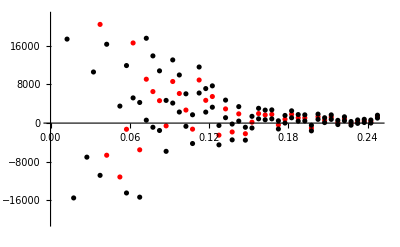

```mathematica
apple =With[{l=4},ListPlot[ {   Pr1datatabμk2[l][[1;;50]],  Pr1datatabErrorPlusμ[l][[1;;50]], Pr1datatabErrorMinusμ[l][[1;;50]]}, PlotStyle->{{Red},{Black},{Black}}] ]
```

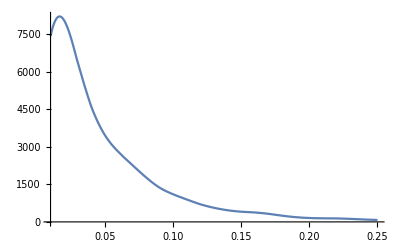

```mathematica
orange =Plot[ PrResumSubap56μ[4][k] , { k , .01 , .25}]
```

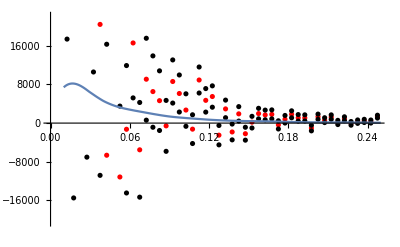

```mathematica
Show[apple,orange]
```

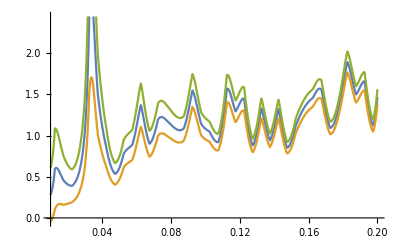

```mathematica
Plot[{PrResumSubap56μ[2][k] / Pr1dataap56μ[2][k] , (PrResumSubap56μ[2][k]+ Errordataap56intμ[2][k]) / Pr1dataap56μ[2][k], (PrResumSubap56μ[2][k]- Errordataap56intμ[2][k]) / Pr1dataap56μ[2][k]} , { k , .01 , .2}]
```

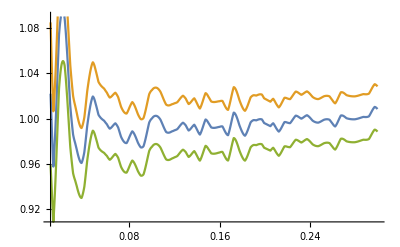

```mathematica
Plot[{PrResumSubap56μ[0][k] / Pr1dataap56μ[0][k] , (PrResumSubap56μ[0][k]+ Errordataap56intμ[0][k]) / Pr1dataap56μ[0][k], (PrResumSubap56μ[0][k]- Errordataap56intμ[0][k]) / Pr1dataap56μ[0][k]} , { k , .01 , .3}]
```

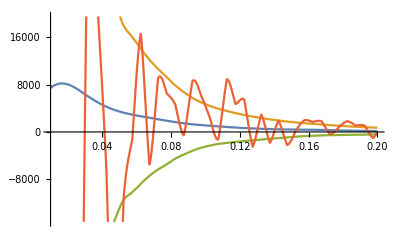

```mathematica
With[{l=4},Plot[{PrResumSubap56μ[l][k]  , (PrResumSubap56μ[l][k]+ Errordataap56intμ[l][k]) , (PrResumSubap56μ[l][k]- Errordataap56intμ[l][k]) , Pr1dataap56μ[l][k]} , { k , .01 , .2}]]
```

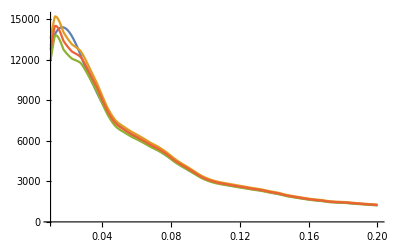

```mathematica
With[{l=0},Plot[{PrResumSubap56μ[l][k]  , (Pr1dataap56μ[l][k]+ Errordataap56intμ[l][k]), (Pr1dataap56μ[l][k]- Errordataap56intμ[l][k]) , Pr1dataap56μ[l][k]} , { k , .01 , .2}]]
```

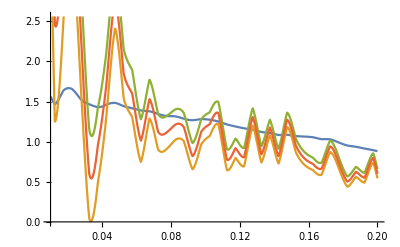

```mathematica
With[{l=2},Plot[{PrResumSubap56μ[l][k]/ Pr1dataap56μ[0][k]  , (Pr1dataap56μ[l][k]+ Errordataap56intμ[l][k])/ Pr1dataap56μ[0][k], (Pr1dataap56μ[l][k]- Errordataap56intμ[l][k])/ Pr1dataap56μ[0][k] , Pr1dataap56μ[l][k]/ Pr1dataap56μ[0][k]} , { k , .01 , .2}]]
```

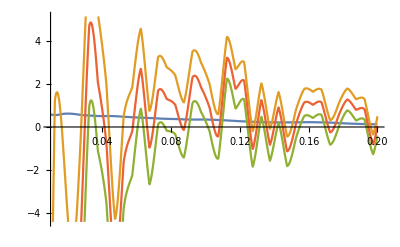

```mathematica
With[{l=4},Plot[{PrResumSubap56μ[l][k]/ Pr1dataap56μ[0][k]  , (Pr1dataap56μ[l][k]+ Errordataap56intμ[l][k])/ Pr1dataap56μ[0][k], (Pr1dataap56μ[l][k]- Errordataap56intμ[l][k])/ Pr1dataap56μ[0][k] , Pr1dataap56μ[l][k]/ Pr1dataap56μ[0][k]} , { k , .01 , .2}]]
```

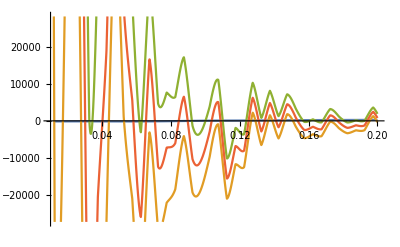

```mathematica
With[{l=6},Plot[{PrResumSubap56μ[l][k]  , (Pr1dataap56μ[l][k]+ Errordataap56intμ[l][k]), (Pr1dataap56μ[l][k]- Errordataap56intμ[l][k]) , Pr1dataap56μ[l][k]} , { k , .01 , .2}]]
```

# free the time dependence

## real space

### setup

```mathematica
NNβ[a_,β_]=EHPSslope[kren[a]]+β dndlogk[kren[a]];
cs1tβ[a_,β_]=cs1 Dgrowth[zz[a]]^(4/(3+ NNβ[a,β]));
```

```mathematica
cs1βa56[cs1_,β_] = Series[ cs1tβ[ap56,β] , {β,0,1}]//Normal ;
cs1βa0[cs1_,β_] = Series[ cs1tβ[1,β] , {β,0,1}]//Normal ;
dcs1βa56[cs1_,β_] =( Series[ x* D[cs1tβ[x,β],x]/.x->ap56, {β,0,1}]//Normal);
dcs1βa0[cs1_,β_] =( Series[ x* D[cs1tβ[x,β],x]/.x->1, {β,0,1}]//Normal);
```

```mathematica
P11csTimeRealSP[ap56][k_]=-Dgrowth[zz[ap56]]^2 2 cs1βa56[cs1,βt]  k^2/knl^2 P11in[k]/.knl-> 1;
P11csTimeRealSP[1][k_]=-Dgrowth[zz[1]]^2 2cs1βa0[cs1,βt]  k^2/knl^2 P11in[k]/.knl-> 1;
```

```mathematica
PrEFT1loopTimeRealSpinta0[k_,cs1_,βt_]=PSPT1loopTotRealSpint[1][k]+cs1 (P11csTimeRealSP[1][k]/.{cs1->1});
PrEFT1loopTimeRealSpinta56[k_,cs1_,βt_]= PSPT1loopTotRealSpint[ap56][k]+cs1 (P11csTimeRealSP[ap56][k]/.{cs1->1});
```

```mathematica
(*Manipulate[Plot[{(PNLdataintz0[k]/PrEFT1loopTimeRealSpinta0[k,cs1,β])^-1,(PNLdataint[k]/PrEFT1loopTimeRealSpinta56[k,cs1,β])^-1,((PNLdataint[k]+ErrordataNLint[k])/PNLdataint[k])^-1,((PNLdataint[k]-ErrordataNLint[k])/PNLdataint[k])^-1},{k,0.025,0.5},PlotRange->All,PlotLabel->"P_NL/real, z=0.56"],{{cs1,1.92},-2,4.5},{{β,0},-5,5}]*)
```

### Real Space: FINAL k’ integrals z = 0

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
(* M0P1loop terms *)
```

```mathematica
P11csRealSPfn[k_] =  (P11csTimeRealSP[1][k]/.{cs1->1, βt->0});
Clear[PRealResumM0Pcsβt0];PRealResumM0Pcsβt0 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTab[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
P11csRealSPfn[k_] =Coefficient[  Series[ (P11csTimeRealSP[1][k]/.{cs1->1}), {βt,0,1}]//Normal  , βt];
Clear[PRealResumM0Pcsβt1];PRealResumM0Pcsβt1 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTab[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
Clear[PRealResumβt];
PRealResumβt[k_,cs1_,βt_] =  PRealResumM1P0[k] + PRealResumM0P1loop[k] + cs1( PRealResumM0Pcsβt0[k] + βt PRealResumM0Pcsβt1[k]   )  ;
```

### Real Space: FINAL k’ integrals z = 0.56

```mathematica
(* M1P0 term *)
```

```mathematica
kmaxnumber=470
```

470

```mathematica
(* M0P1loop terms *)
```

```mathematica
P11csRealSPfn[k_] = (P11csTimeRealSP[ap56][k]/.{cs1->1, βt->0});
Clear[PRealResumM0Pcsβt0ap56];PRealResumM0Pcsβt0ap56 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTabap56[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1ap56[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ]; 

P11csRealSPfn[k_] = Coefficient[ Series[ (P11csTimeRealSP[ap56][k]/.{cs1->1}), { βt,0,1}]//Normal , βt];
Clear[PRealResumM0Pcsβt1ap56];PRealResumM0Pcsβt1ap56 = Interpolation[ Table[ { k ,     MidpointIntegrate[ Map[{#⟦1⟧,  (#⟦1⟧)^2/(2 π^2) #⟦2⟧ P11csRealSPfn[ #⟦1⟧] } & , MRealTabap56[k] [[1;;kmaxnumber]]  ]  ]   + (1/2 ⅇ^(-k^2/2 X1ap56[10000]) Iint[0][0][0][k,q] P11csRealSPfn[k] ) /. {X1temp->X1ap56[10000],ff->0, α->1/3, β->1/3}   } , {k , kouttab} ] , InterpolationOrder->3 ];
```

```mathematica
Clear[PRealResumβtap56];
PRealResumβtap56[k_,cs1_, βt_] =  PRealResumM1P0ap56[k] + PRealResumM0P1loopap56[k] + cs1( PRealResumM0Pcsβt0ap56[k] + βt  PRealResumM0Pcsβt1ap56[k] )  ;
```

### Plots real space

```mathematica
Manipulate[Plot[{(PNLdataintz0[k]/PRealResumβt[k,cs1,β])^-1,(PNLdataint[k]/PRealResumβtap56[k,cs1,β])^-1,((PNLdataint[k]+ErrordataNLint[k])/PNLdataint[k])^-1,((PNLdataint[k]-ErrordataNLint[k])/PNLdataint[k])^-1},{k,0.025,0.5},PlotRange->All,PlotLabel->"P_NL/real, z=0.56"],{{cs1,1.92},-2,4.5},{{β,-1.44},-5,5}]
```

## redshift space

### setup

```mathematica
NNβ[a_,β_]=EHPSslope[kren[a]]+β dndlogk[kren[a]];
cs1tβ[a_,β_]=cs1 Dgrowth[zz[a]]^(4/(3+ NNβ[a,β]));
```

```mathematica
cs1βa56[cs1_,β_] = Series[ cs1tβ[ap56,β] , {β,0,1}]//Normal ;
cs1βa0[cs1_,β_] = Series[ cs1tβ[1,β] , {β,0,1}]//Normal ;
dcs1βa56[cs1_,β_] =( Series[ x* D[cs1tβ[x,β],x]/.x->ap56, {β,0,1}]//Normal);
dcs1βa0[cs1_,β_] =( Series[ x* D[cs1tβ[x,β],x]/.x->1, {β,0,1}]//Normal);
```

```mathematica
dcs1βa56[cs1,β]
```

0.983705 cs1-0.0853587 cs1 β

```mathematica
Pr11counterTimeReal[ap56][k_,μ_, β_]=-Dgrowth[zz[a]]^2(2cs1βa56[cs1,β]+ (4 f[zz[a]]cs1βa56[cs1,β]+2 dcs1βa56[cs1,β]) μ^2+2( cs1βa56[cs1,β] f[zz[a]]^2+f[zz[a]] dcs1βa56[cs1,β]) μ^4 )  k^2/knl^2 P11in[k]/.{knl-> 1, a ->ap56};
Pr11counterTimeReal[1][k_,μ_, β_]=-Dgrowth[zz[a]]^2(2cs1βa0[cs1,β]+ (4 f[zz[a]]cs1βa0[cs1,β]+2 dcs1βa0[cs1,β]) μ^2+2( cs1βa0[cs1,β] f[zz[a]]^2+f[zz[a]] dcs1βa0[cs1,β]) μ^4 )  k^2/knl^2 P11in[k]/.{knl-> 1, a ->1};
```

### EFT manipulations

```mathematica
PrTimecsl0[1][k_]=Coefficient[((Pr11counterTimeReal[1][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterTimeReal[1][k,μ, βt]/.cs1-> 1//Expand)/.{μ->0});
PrTimecsl2[1][k_]=Coefficient[((Pr11counterTimeReal[1][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP2];
PrTimecsl4[1][k_]=Coefficient[((Pr11counterTimeReal[1][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP4];
```

```mathematica
PrTimecsl0[ap56][k_]=Coefficient[((Pr11counterTimeReal[ap56][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP0]+((Pr11counterTimeReal[1][k,μ, βt]/.cs1-> 1//Expand)/.{μ->0});
PrTimecsl2[ap56][k_]=Coefficient[((Pr11counterTimeReal[ap56][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP2];
PrTimecsl4[ap56][k_]=Coefficient[((Pr11counterTimeReal[ap56][k,μ, βt]/.cs1-> 1//Expand)/.LegendreSubs),LegendrePPP4];
```

```mathematica
Clear[PrTimecsl0tab,PrTimecsl2tab,PrTimecsl4tab]
PrTimecsl0tab[a_]:=Table[{k,PrTimecsl0[a][k]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
PrTimecsl2tab[a_]:=Table[{k,PrTimecsl2[a][k]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
PrTimecsl4tab[a_]:=Table[{k,PrTimecsl4[a][k]},{k,0.025,0.625,0.01}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
Clear[PrTimecsl0tabext,PrTimecsl2tabext,PrTimecsl4tabext]
PrTimecsl0tabext[a_]:=Table[{k,PrTimecsl0[a][k]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl0.dat",Prcsl0tab]*)
PrTimecsl2tabext[a_]:=Table[{k,PrTimecsl2[a][k]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl2tab.dat",Prcsl2tab]*)
PrTimecsl4tabext[a_]:=Table[{k,PrTimecsl4[a][k]},{k,.7,10,0.5}]
(*Export[NotebookDirectory[]<>"redshift_real_universe/mathematics/Prcsl4tab.dat",Prcsl4tab]*)
```

```mathematica
PTimecsl0int[a_]:=Interpolation[Join[ PrTimecsl0tab[a],PrTimecsl0tabext[a]]];
PTimecsl2int[a_]:=Interpolation[Join[ PrTimecsl2tab[a],PrTimecsl2tabext[a]]];
PTimecsl4int[a_]:=Interpolation[Join[ PrTimecsl4tab[a],PrTimecsl4tabext[a]]];
```

```mathematica
PrTimeEFT1loopl0int[1][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl0int[1][k]+cs1 PTimecsl0int[1][k]+c1 Pc1l0int[1][k]+c2 Pc2l0int[1][k];
PrTimeEFT1loopl2int[1][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl2int[1][k]+cs1 PTimecsl2int[1][k]+c1 Pc1l2int[1][k]+c2 Pc2l2int[1][k];
PrTimeEFT1loopl4int[1][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl4int[1][k]+cs1 PTimecsl4int[1][k]+c1 Pc1l4int[1][k]+c2 Pc2l4int[1][k];
PrTimeEFT1loopl6int[1][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl6int[1][k]+c1 Pc1l6int[1][k]+c2 Pc2l6int[1][k];
PrTimeEFT1loopl8int[1][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl8int[1][k]+c1 Pc1l8int[1][k]+c2 Pc2l8int[1][k];
```

```mathematica
PrTimeEFT1loopl0int[ap56][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl0int[ap56][k]+cs1 PTimecsl0int[ap56][k]+c1 Pc1l0int[ap56][k]+c2 Pc2l0int[ap56][k];
PrTimeEFT1loopl2int[ap56][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl2int[ap56][k]+cs1 PTimecsl2int[ap56][k]+c1 Pc1l2int[ap56][k]+c2 Pc2l2int[ap56][k];
PrTimeEFT1loopl4int[ap56][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl4int[ap56][k]+cs1 PTimecsl4int[ap56][k]+c1 Pc1l4int[ap56][k]+c2 Pc2l4int[ap56][k];
PrTimeEFT1loopl6int[ap56][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl6int[ap56][k]+c1 Pc1l6int[ap56][k]+c2 Pc2l6int[ap56][k];
PrTimeEFT1loopl8int[ap56][k_,cs1_,c1_,c2_,βt_]=PrSPT1loopl8int[ap56][k]+c1 Pc1l8int[ap56][k]+c2 Pc2l8int[ap56][k];
```

```mathematica
Manipulate[Quiet[{

Plot[{(PNLdataint[k]/PrEFT1loopRealSpintap56[k,cs1,c1,c2,0])^-1,(PNLdataint[k]/PrEFT1loopTimeRealSpinta56[k,cs1,β])^-1,1,(1 + ErrordataNLint[k]/PNLdataint[k]),(1-ErrordataNLint[k]/PNLdataint[k]),(PNLdataint[k]/PrEFT1loopRealSpintap56[k,0,0,0,0])^-1},{k,0.02,0.5},PlotRange->{.96,1.04}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "P^real/((P^real)_NL), z = 0.56"},PlotStyle->{{Darker[Red], DotDashed},{Darker[Blue], Thick}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }],

Plot[{PrTimeEFT1loopl0int[ap56][k,cs1,c1,c2,β]/Pr1datal0int[k],PrEFT1loopl0intap56[k,cs1,c1,c2,0]/Pr1datal0int[k],1,(Pr1datal0int[k]+Errordatal0int[k])/Pr1datal0int[k],(Pr1datal0int[k]-Errordatal0int[k])/Pr1datal0int[k],PrEFT1loopl0intap56[k,0,0,0,0]/Pr1datal0int[k]},{k,0.02,0.5},PlotRange->{.95,1.05}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_0)/((P^r)_(0, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] , 

Plot[{PrTimeEFT1loopl2int[ap56][k,cs1,c1,c2,β]/Pr1datal2int[k],PrEFT1loopl2intap56[k,cs1,c1,c2,0]/Pr1datal2int[k],1,(Pr1datal2int[k]+Errordatal2int[k])/Pr1datal2int[k],(Pr1datal2int[k]-Errordatal2int[k])/Pr1datal2int[k],PrEFT1loopl2intap56[k,0,0,0,0]/Pr1datal2int[k]},{k,0.02,0.5},PlotRange->{.9,1.1}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_2)/((P^r)_(2, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }], 

Plot[{Pr1Resumap56[4][k,cs1,c1,c2]/Pr1datal4int[k],PrEFT1loopl4intap56[k,cs1,c1,c2,0]/Pr1datal4int[k],1,(Pr1datal4int[k]+Errordatal4int[k])/Pr1datal4int[k],(Pr1datal4int[k]-Errordatal4int[k])/Pr1datal4int[k],PrEFT1loopl4intap56[k,0,0,0,0]/Pr1datal4int[k]},{k,0.02,0.5},PlotRange->{.3,1.7}, Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"k [h Mpc^-1]", "((P^r)_4)/((P^r)_(4, NL)), z = 0.56"},PlotStyle->{{Darker[Blue], Thick},{Darker[Red], DotDashed}, {Black},{Opacity[.1,Darker[Green]],Thick,Dashed},{Opacity[.1,Darker[Green]], Thick,Dashed},{Darker[Gray], DotDashed}},Filling->{{4->{{5},Opacity[.1,Darker[Green]]}}   }] }],{{cs1,1.96},-5,5},{{c1,-21.8},-30,+35},{{c2,5.1},-25,+20}, {{β , -1.44},-5,5}]
```